```mathematica
(* Fits to log stable below. Starting with 120d worth of data from WETH/USDC .... *)
```

```mathematica
(* Import from csv *)
```

```mathematica
Directory[]
```

/Users/personal

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]]
```

/Users/personal/Desktop/note7/points

```mathematica
(* Go back and download WETH/USDC data from cron. Look at that *)
```

```mathematica
tblWethUsdc120d = Import["120/data-1626472963_weth-usdc-twap.csv"]
```

{{,timestamp,twap},{0,1.61878×10^9,2.23957×10^9},{1,1.61878×10^9,2.24054×10^9},{2,1.61878×10^9,2.23817×10^9},{3,1.61878×10^9,2.25083×10^9},{4,1.61878×10^9,2.25656×10^9},11259,{11266,1.62647×10^9,1.91147×10^9},{11267,1.62647×10^9,1.90971×10^9},{11268,1.62647×10^9,1.90596×10^9},{11269,1.62647×10^9,1.90286×10^9},{11270,1.62647×10^9,1.90034×10^9},{11271,1.62647×10^9,1.89838×10^9}}
 |  |  |  |

```mathematica
Length[tblWethUsdc120d]
```

11271

```mathematica
FromUnixTime[tblWethUsdc120d[[2]][[2]]]
```

Sun 18 Apr 2021 16:50:52GMT-4.

```mathematica
FromUnixTime[tblWethUsdc120d[[Length[tblWethUsdc120d]]][[2]]]
```

Fri 16 Jul 2021 18:01:02GMT-4.

```mathematica
twapsWethUsdc120d = Table[tblWethUsdc120d[[i]][[3]], {i, 2, Length[tblWethUsdc120d]}]
```

{2.23957×10^9,2.24054×10^9,2.23817×10^9,2.25083×10^9,2.25656×10^9,2.25775×10^9,2.25804×10^9,2.257×10^9,2.25322×10^9,1.74585×10^9,1.74538×10^9,1.74413×10^9,1.74262×10^9,1.74205×10^9,2.12343×10^9,2.12508×10^9,2.12091×10^9,2.11964×10^9,2.1185×10^9,2.11908×10^9,2.12379×10^9,2.13378×10^9,2.1414×10^9,2.14916×10^9,2.15618×10^9,2.1627×10^9,2.16623×10^9,2.1675×10^9,2.16946×10^9,1.33059×10^10,1.52229×10^10,2.17316×10^9,2.17288×10^9,2.17448×10^9,2.18326×10^9,2.18968×10^9,2.19585×10^9,2.20047×10^9,2.20447×10^9,2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9,2.56814×10^9,2.57934×10^9,2.59744×10^9,2.61451×10^9,2.62719×10^9,2.63082×10^9,2.6356×10^9,2.64104×10^9,2.64795×10^9,2.65163×10^9,2.65855×10^9,2.65906×10^9,2.65748×10^9,2.65239×10^9,2.65007×10^9,2.64537×10^9,2.6422×10^9,2.63909×10^9,2.63922×10^9,2.63904×10^9,2.63858×10^9,2.63735×10^9,2.63764×10^9,2.63803×10^9,2.63722×10^9,2.63794×10^9,2.6394×10^9,2.63626×10^9,2.6309×10^9,2.62599×10^9,2.62427×10^9,2.62282×10^9,2.62459×10^9,2.62923×10^9,2.63363×10^9,2.63453×10^9,2.63619×10^9,2.63742×10^9,2.6365×10^9,2.63813×10^9,2.63956×10^9,2.63923×10^9,2.63813×10^9,2.63675×10^9,2.63277×10^9,2.62774×10^9,2.6252×10^9,2.62523×10^9,2.62802×10^9,2.63213×10^9,2.63998×10^9,2.65069×10^9,2.66276×10^9,2.67138×10^9,2.67884×10^9,2.6839×10^9,2.68591×10^9,2.68649×10^9,2.68838×10^9,2.69162×10^9,2.69579×10^9,2.69895×10^9,2.70219×10^9,2.70203×10^9,2.6985×10^9,2.69107×10^9,2.68116×10^9,2.6707×10^9,2.65959×10^9,2.65079×10^9,2.6437×10^9,2.64043×10^9,2.63928×10^9,2.63988×10^9,2.6411×10^9,2.64281×10^9,2.6419×10^9,2.63996×10^9,2.63913×10^9,2.63692×10^9,2.63059×10^9,2.629×10^9,2.62375×10^9,2.6125×10^9,2.6043×10^9,2.59472×10^9,2.59248×10^9,2.58477×10^9,2.58679×10^9,2.59057×10^9,2.5975×10^9,2.60157×10^9,2.60817×10^9,2.61214×10^9,2.61509×10^9,2.61697×10^9,2.61809×10^9,2.61915×10^9,2.61857×10^9,2.61463×10^9,2.60977×10^9,2.60421×10^9,2.6001×10^9,2.60019×10^9,2.60194×10^9,2.60676×10^9,2.61245×10^9,2.61714×10^9,2.62146×10^9,2.62891×10^9,2.63716×10^9,2.64614×10^9,2.65821×10^9,2.67367×10^9,2.68377×10^9,2.69346×10^9,2.70188×10^9,2.70791×10^9,2.71172×10^9,2.71441×10^9,2.71902×10^9,2.71242×10^9,2.70675×10^9,2.70174×10^9,2.69608×10^9,2.69353×10^9,2.69857×10^9,2.7032×10^9,2.70851×10^9,2.71255×10^9,2.71347×10^9,2.71033×10^9,2.70519×10^9,2.69555×10^9,2.68986×10^9,2.68374×10^9,2.68337×10^9,2.68503×10^9,2.68906×10^9,2.69365×10^9,2.70085×10^9,2.7055×10^9,2.71066×10^9,2.71477×10^9,2.71774×10^9,2.71978×10^9,2.71976×10^9,2.71957×10^9,2.72293×10^9,2.72605×10^9,2.72826×10^9,2.61748×10^9,2.72971×10^9,2.72785×10^9,2.72473×10^9,2.72449×10^9,2.83875×10^9,2.73048×10^9,2.70685×10^9,2.72574×10^9,2.72363×10^9,2.71831×10^9,2.71326×10^9,2.73625×10^9,2.71169×10^9,2.71164×10^9,2.71516×10^9,2.72376×10^9,2.73414×10^9,2.74182×10^9,2.74377×10^9,2.74286×10^9,2.73679×10^9,2.72737×10^9,2.72313×10^9,2.72223×10^9,2.72211×10^9,2.72412×10^9,2.73119×10^9,2.73578×10^9,2.73961×10^9,2.74275×10^9,2.74377×10^9,2.74148×10^9,2.73802×10^9,2.73215×10^9,2.72686×10^9,2.72274×10^9,2.71851×10^9,2.71589×10^9,2.71682×10^9,2.71852×10^9,2.71973×10^9,2.72099×10^9,2.72118×10^9,2.72036×10^9,2.71803×10^9,2.71711×10^9,2.71625×10^9,2.71402×10^9,2.7077×10^9,2.70253×10^9,2.69641×10^9,2.69104×10^9,2.68881×10^9,2.6873×10^9,2.68706×10^9,2.68928×10^9,2.69198×10^9,2.69406×10^9,2.69883×10^9,2.70389×10^9,2.70778×10^9,2.71183×10^9,2.71527×10^9,2.72096×10^9,2.72397×10^9,2.72755×10^9,2.72925×10^9,2.72992×10^9,2.73064×10^9,2.73154×10^9,2.73126×10^9,2.73096×10^9,2.7294×10^9,2.72633×10^9,2.724×10^9,2.72102×10^9,2.71824×10^9,2.72097×10^9,2.72841×10^9,2.73666×10^9,2.74697×10^9,2.75731×10^9,2.7641×10^9,2.76504×10^9,2.76546×10^9,2.76513×10^9,2.76459×10^9,2.76491×10^9,2.76668×10^9,2.76743×10^9,2.76769×10^9,2.76806×10^9,2.76717×10^9,2.76543×10^9,2.76721×10^9,2.77086×10^9,2.775×10^9,2.78064×10^9,2.78663×10^9,2.78752×10^9,2.78625×10^9,2.78341×10^9,2.77901×10^9,2.77219×10^9,2.76783×10^9,2.76488×10^9,2.76346×10^9,2.7638×10^9,2.76513×10^9,2.7666×10^9,2.76932×10^9,2.77417×10^9,2.77752×10^9,2.78108×10^9,2.7845×10^9,2.78344×10^9,2.77817×10^9,2.77243×10^9,2.76555×10^9,2.75762×10^9,2.74739×10^9,2.74127×10^9,2.738×10^9,2.7346×10^9,2.73519×10^9,2.73259×10^9,2.72757×10^9,2.72235×10^9,2.7184×10^9,2.71327×10^9,2.71615×10^9,2.71967×10^9,2.72248×10^9,2.72501×10^9,2.72742×10^9,2.72738×10^9,2.72296×10^9,2.71582×10^9,2.71306×10^9,2.71057×10^9,2.70641×10^9,2.70649×10^9,2.70927×10^9,2.7094×10^9,2.70879×10^9,2.71196×10^9,2.71795×10^9,2.72507×10^9,2.73315×10^9,2.74055×10^9,2.74832×10^9,2.7532×10^9,2.75747×10^9,2.76008×10^9,2.76143×10^9,2.76196×10^9,2.76191×10^9,2.76149×10^9,2.75977×10^9,2.7548×10^9,2.75368×10^9,2.75089×10^9,2.7477×10^9,2.74435×10^9,2.74318×10^9,2.73905×10^9,2.73823×10^9,2.73931×10^9,2.74195×10^9,2.74371×10^9,2.74567×10^9,2.74399×10^9,2.74219×10^9,2.7421×10^9,2.74112×10^9,2.74029×10^9,2.74087×10^9,2.74219×10^9,2.74109×10^9,2.7422×10^9,2.74414×10^9,2.74721×10^9,2.75003×10^9,2.75336×10^9,2.75674×10^9,2.75873×10^9,2.76045×10^9,2.76198×10^9,2.7632×10^9,2.76403×10^9,2.76461×10^9,2.76565×10^9,2.76728×10^9,2.77046×10^9,2.77379×10^9,2.77742×10^9,2.78123×10^9,2.78293×10^9,2.7827×10^9,2.78245×10^9,2.78097×10^9,2.77977×10^9,2.77746×10^9,2.77616×10^9,2.77466×10^9,2.77401×10^9,2.77533×10^9,2.7787×10^9,2.78216×10^9,2.80134×10^9,2.78906×10^9,2.78842×10^9,2.78723×10^9,2.82806×10^9,2.76798×10^9,2.78159×10^9,2.7813×10^9,2.77825×10^9,2.72922×10^9,2.76753×10^9,2.76317×10^9,2.75753×10^9,2.75353×10^9,2.75102×10^9,2.7483×10^9,2.74567×10^9,2.74392×10^9,2.74468×10^9,2.74638×10^9,2.74819×10^9,2.7477×10^9,2.74719×10^9,2.74595×10^9,2.74403×10^9,2.74128×10^9,2.74355×10^9,2.74612×10^9,2.7494×10^9,2.75331×10^9,2.75533×10^9,2.75248×10^9,2.7507×10^9,2.74822×10^9,2.74593×10^9,2.7459×10^9,2.74559×10^9,2.74579×10^9,2.74671×10^9,2.74729×10^9,2.7484×10^9,2.75239×10^9,2.75614×10^9,2.75919×10^9,2.76152×10^9,2.7637×10^9,2.76366×10^9,2.76471×10^9,2.76466×10^9,2.76468×10^9,2.76518×10^9,2.76498×10^9,2.76413×10^9,2.76529×10^9,2.76855×10^9,2.77194×10^9,2.77473×10^9,2.77689×10^9,2.77822×10^9,2.77799×10^9,2.77618×10^9,2.77409×10^9,2.77224×10^9,2.76982×10^9,2.76719×10^9,2.7649×10^9,2.7613×10^9,2.75929×10^9,2.75776×10^9,2.75645×10^9,2.75597×10^9,2.75652×10^9,2.75541×10^9,2.7544×10^9,2.75292×10^9,2.75267×10^9,2.75227×10^9,2.7536×10^9,2.75607×10^9,2.75943×10^9,2.76309×10^9,2.76715×10^9,2.76933×10^9,2.77048×10^9,2.77078×10^9,2.77071×10^9,2.76979×10^9,2.76909×10^9,2.76776×10^9,2.76768×10^9,2.76883×10^9,2.77949×10^9,2.79242×10^9,2.80527×10^9,2.81563×10^9,2.82967×10^9,2.83186×10^9,2.83186×10^9,2.83116×10^9,2.83322×10^9,2.83502×10^9,2.83731×10^9,2.8405×10^9,2.84328×10^9,2.84375×10^9,2.84361×10^9,2.84323×10^9,2.84274×10^9,2.84259×10^9,2.84563×10^9,2.85031×10^9,2.85527×10^9,2.85864×10^9,2.86233×10^9,2.86076×10^9,2.85856×10^9,2.85557×10^9,2.85439×10^9,2.85513×10^9,2.85625×10^9,2.85655×10^9,2.85682×10^9,2.85649×10^9,2.85557×10^9,2.85521×10^9,2.85615×10^9,2.85757×10^9,2.85818×10^9,2.8577×10^9,2.85372×10^9,2.84594×10^9,2.83934×10^9,2.83444×10^9,2.8325×10^9,2.83316×10^9,2.83598×10^9,2.8374×10^9,2.83687×10^9,2.83468×10^9,2.83461×10^9,2.83743×10^9,2.84098×10^9,2.84543×10^9,2.84947×10^9,2.8527×10^9,2.854×10^9,2.8552×10^9,2.85894×10^9,2.8634×10^9,2.86716×10^9,2.87105×10^9,2.87345×10^9,2.87385×10^9,2.87273×10^9,2.87143×10^9,2.86996×10^9,2.86907×10^9,2.86878×10^9,2.86857×10^9,2.86782×10^9,2.86742×10^9,2.86603×10^9,2.8637×10^9,2.86046×10^9,2.85818×10^9,2.85434×10^9,2.8527×10^9,2.85328×10^9,2.85804×10^9,2.86276×10^9,2.86969×10^9,2.87547×10^9,2.80645×10^9,2.88817×10^9,2.89516×10^9,2.90277×10^9,2.90995×10^9,2.99492×10^9,2.92215×10^9,2.92512×10^9,2.9281×10^9,2.93023×10^9,2.93112×10^9,2.9317×10^9,2.93274×10^9,2.93337×10^9,2.93337×10^9,2.93266×10^9,2.92963×10^9,2.92575×10^9,2.92503×10^9,2.92361×10^9,2.9247×10^9,2.9292×10^9,2.93421×10^9,2.93769×10^9,3.03478×10^9,2.93804×10^9,2.93441×10^9,2.93127×10^9,2.92849×10^9,2.84973×10^9,2.9289×10^9,2.93166×10^9,2.93378×10^9,2.93654×10^9,2.93757×10^9,2.93919×10^9,2.94188×10^9,2.94373×10^9,2.94649×10^9,2.94615×10^9,2.94533×10^9,2.94334×10^9,2.9416×10^9,2.93936×10^9,2.93819×10^9,2.93651×10^9,2.93576×10^9,2.93568×10^9,2.93596×10^9,2.93709×10^9,2.93933×10^9,2.94297×10^9,2.94542×10^9,2.94764×10^9,2.94994×10^9,2.95137×10^9,2.9515×10^9,2.95024×10^9,2.94409×10^9,2.93685×10^9,2.92533×10^9,2.91281×10^9,2.91113×10^9,2.91184×10^9,2.91191×10^9,2.91431×10^9,2.91738×10^9,2.91731×10^9,2.91522×10^9,2.91575×10^9,2.91633×10^9,2.9172×10^9,2.91769×10^9,2.91803×10^9,2.91747×10^9,2.91558×10^9,2.90994×10^9,2.90433×10^9,2.89991×10^9,2.89507×10^9,2.89195×10^9,2.88844×10^9,2.88498×10^9,2.87998×10^9,2.87532×10^9,2.87316×10^9,2.87376×10^9,2.875×10^9,2.87711×10^9,2.87898×10^9,2.88206×10^9,2.88564×10^9,2.89221×10^9,2.89905×10^9,2.90687×10^9,2.91168×10^9,2.9154×10^9,2.91581×10^9,2.91519×10^9,2.91474×10^9,2.91469×10^9,2.91541×10^9,2.91761×10^9,2.9211×10^9,2.92439×10^9,2.92719×10^9,2.92829×10^9,2.92738×10^9,2.92673×10^9,2.92583×10^9,2.92599×10^9,2.92453×10^9,2.92212×10^9,2.92077×10^9,2.91849×10^9,2.9166×10^9,2.9168×10^9,2.91798×10^9,2.91889×10^9,2.91928×10^9,2.91902×10^9,2.81586×10^9,2.91997×10^9,2.92207×10^9,2.92466×10^9,2.92757×10^9,3.04472×10^9,2.93313×10^9,2.93374×10^9,2.93474×10^9,2.93518×10^9,2.93494×10^9,2.93477×10^9,2.93473×10^9,2.93493×10^9,2.93632×10^9,2.938×10^9,2.94001×10^9,2.94144×10^9,2.94487×10^9,2.94892×10^9,2.95266×10^9,2.9592×10^9,2.96545×10^9,2.96951×10^9,2.97281×10^9,2.97447×10^9,2.97448×10^9,2.97352×10^9,2.97196×10^9,2.97037×10^9,2.96885×10^9,2.96757×10^9,2.96789×10^9,2.96959×10^9,2.97161×10^9,2.97374×10^9,2.97396×10^9,2.97038×10^9,2.96509×10^9,2.95729×10^9,2.94817×10^9,2.94357×10^9,2.94192×10^9,2.94294×10^9,2.94426×10^9,2.94644×10^9,2.95175×10^9,2.95794×10^9,2.96718×10^9,2.97438×10^9,2.98319×10^9,2.98637×10^9,2.98854×10^9,2.99013×10^9,2.99205×10^9,2.99826×10^9,3.00421×10^9,3.00858×10^9,3.01404×10^9,3.01764×10^9,3.01749×10^9,3.01875×10^9,3.02059×10^9,3.02486×10^9,3.02954×10^9,3.03463×10^9,3.03939×10^9,3.04473×10^9,3.04978×10^9,3.05285×10^9,3.0543×10^9,3.05471×10^9,3.0537×10^9,3.05238×10^9,3.05422×10^9,3.05571×10^9,3.06099×10^9,3.0702×10^9,3.08027×10^9,3.08642×10^9,3.08984×10^9,3.09292×10^9,3.09329×10^9,3.09247×10^9,3.09069×10^9,3.0893×10^9,3.09236×10^9,3.10229×10^9,3.11249×10^9,3.12166×10^9,3.13349×10^9,3.14192×10^9,3.14816×10^9,3.1563×10^9,3.16645×10^9,3.17416×10^9,3.17874×10^9,3.1755×10^9,3.17232×10^9,3.16874×10^9,3.16586×10^9,3.16861×10^9,3.16742×10^9,3.16414×10^9,3.1593×10^9,3.15435×10^9,3.14781×10^9,3.14722×10^9,3.14946×10^9,3.15466×10^9,3.15986×10^9,3.16539×10^9,3.16726×10^9,3.16749×10^9,3.16459×10^9,3.15916×10^9,3.1508×10^9,3.14581×10^9,3.14291×10^9,3.13797×10^9,3.13545×10^9,3.13475×10^9,3.12745×10^9,3.12068×10^9,3.11636×10^9,3.11706×10^9,3.11962×10^9,3.12807×10^9,3.14131×10^9,3.1519×10^9,3.15746×10^9,3.1652×10^9,3.17054×10^9,3.17034×10^9,3.17038×10^9,3.17194×10^9,3.17099×10^9,3.16982×10^9,3.17997×10^9,3.19805×10^9,3.21332×10^9,3.2328×10^9,3.25006×10^9,3.26408×10^9,3.26847×10^9,3.27346×10^9,3.28292×10^9,3.28874×10^9,3.29368×10^9,3.30162×10^9,3.30984×10^9,3.31551×10^9,3.31525×10^9,3.30975×10^9,3.30738×10^9,3.30371×10^9,3.29632×10^9,3.29271×10^9,3.2954×10^9,3.291×10^9,3.28432×10^9,3.28393×10^9,3.28365×10^9,3.28322×10^9,3.28341×10^9,3.28726×10^9,3.28674×10^9,3.29249×10^9,3.30197×10^9,3.32134×10^9,3.34054×10^9,3.35925×10^9,3.37253×10^9,3.38068×10^9,3.38782×10^9,3.39434×10^9,3.40513×10^9,3.41667×10^9,3.42637×10^9,3.51266×10^9,3.41029×10^9,3.39725×10^9,3.38664×10^9,3.35792×10^9,3.24986×10^9,3.32865×10^9,3.31206×10^9,3.29581×10^9,3.29777×10^9,3.30036×10^9,3.29862×10^9,3.28909×10^9,3.27985×10^9,3.27262×10^9,3.25998×10^9,3.24619×10^9,3.24303×10^9,3.24156×10^9,3.24031×10^9,3.24427×10^9,3.24642×10^9,3.24701×10^9,3.25556×10^9,3.26539×10^9,3.27686×10^9,3.29305×10^9,3.31134×10^9,3.32849×10^9,3.34022×10^9,3.35294×10^9,3.35822×10^9,3.36525×10^9,3.3693×10^9,3.37145×10^9,3.37457×10^9,3.37841×10^9,3.37754×10^9,3.37142×10^9,3.36896×10^9,3.36567×10^9,3.3615×10^9,3.35694×10^9,3.35295×10^9,3.34424×10^9,3.33067×10^9,3.32129×10^9,3.31551×10^9,3.30967×10^9,3.30488×10^9,3.31224×10^9,3.31948×10^9,3.33212×10^9,3.34441×10^9,3.35342×10^9,3.35429×10^9,3.35717×10^9,3.36256×10^9,3.36871×10^9,3.38226×10^9,3.39839×10^9,3.40725×10^9,3.41138×10^9,3.41839×10^9,3.42868×10^9,3.43749×10^9,3.44802×10^9,3.45623×10^9,3.45604×10^9,3.45006×10^9,3.45079×10^9,3.44972×10^9,3.45783×10^9,3.46868×10^9,3.51917×10^9,3.49037×10^9,3.48956×10^9,3.49155×10^9,3.48313×10^9,3.4358×10^9,3.43892×10^9,3.42236×10^9,3.39615×10^9,3.37087×10^9,3.34657×10^9,3.31593×10^9,3.29004×10^9,3.28075×10^9,3.27893×10^9,3.2681×10^9,3.25206×10^9,3.25651×10^9,3.26333×10^9,3.266×10^9,3.27289×10^9,3.29005×10^9,3.30333×10^9,3.30959×10^9,3.31795×10^9,3.3263×10^9,3.33685×10^9,3.34964×10^9,3.35788×10^9,3.36501×10^9,3.37315×10^9,3.38492×10^9,3.38066×10^9,3.3892×10^9,3.40191×10^9,3.40186×10^9,3.38829×10^9,3.39475×10^9,3.38859×10^9,3.38107×10^9,3.38142×10^9,3.38023×10^9,3.37093×10^9,3.36058×10^9,3.35022×10^9,3.33532×10^9,3.31576×10^9,3.30652×10^9,3.28881×10^9,3.28516×10^9,3.28866×10^9,3.29359×10^9,3.29752×10^9,3.29343×10^9,3.28286×10^9,3.2772×10^9,3.27467×10^9,3.27531×10^9,3.28842×10^9,3.30126×10^9,3.31071×10^9,3.3224×10^9,3.33405×10^9,3.34239×10^9,3.35175×10^9,3.36104×10^9,3.36×10^9,3.3598×10^9,3.35398×10^9,3.34512×10^9,3.33837×10^9,3.32631×10^9,3.31173×10^9,3.30417×10^9,3.29825×10^9,3.29722×10^9,3.29596×10^9,3.29762×10^9,3.3007×10^9,3.30004×10^9,3.29202×10^9,3.28085×10^9,3.27257×10^9,3.26674×10^9,3.26707×10^9,3.2698×10^9,3.27276×10^9,3.27289×10^9,3.26668×10^9,3.25799×10^9,3.25262×10^9,3.25011×10^9,3.25127×10^9,3.25661×10^9,3.26576×10^9,3.27656×10^9,3.29321×10^9,3.31361×10^9,3.32532×10^9,3.3378×10^9,3.34953×10^9,3.35215×10^9,3.35474×10^9,3.35306×10^9,3.35051×10^9,3.3493×10^9,3.35174×10^9,3.36157×10^9,3.37043×10^9,3.37489×10^9,3.3781×10^9,3.37729×10^9,3.37389×10^9,3.37052×10^9,3.36914×10^9,3.36728×10^9,3.36537×10^9,3.36126×10^9,3.35838×10^9,3.36096×10^9,3.36457×10^9,3.3672×10^9,3.3687×10^9,3.37161×10^9,3.37156×10^9,3.37133×10^9,3.37312×10^9,3.37377×10^9,3.37571×10^9,3.37184×10^9,3.36254×10^9,3.34794×10^9,3.33756×10^9,3.33144×10^9,3.3282×10^9,3.32911×10^9,3.33675×10^9,3.33777×10^9,3.33083×10^9,3.32658×10^9,3.32181×10^9,3.32384×10^9,3.33698×10^9,3.35683×10^9,3.37555×10^9,3.40635×10^9,3.42307×10^9,3.42605×10^9,3.42653×10^9,3.42208×10^9,3.41643×10^9,3.41196×10^9,3.41093×10^9,3.41133×10^9,3.41151×10^9,3.41222×10^9,3.41535×10^9,3.4203×10^9,3.42624×10^9,3.43622×10^9,3.44464×10^9,3.45552×10^9,3.46154×10^9,3.46323×10^9,3.46303×10^9,3.46052×10^9,3.45735×10^9,3.45413×10^9,3.45352×10^9,3.45198×10^9,3.4458×10^9,3.44212×10^9,3.43952×10^9,3.44475×10^9,3.4542×10^9,3.47486×10^9,3.48566×10^9,3.50763×10^9,3.5143×10^9,3.5187×10^9,3.52307×10^9,3.52401×10^9,3.52443×10^9,3.52302×10^9,3.51368×10^9,3.50429×10^9,3.49398×10^9,3.48502×10^9,3.47471×10^9,3.47133×10^9,3.46861×10^9,3.47011×10^9,3.47167×10^9,3.47457×10^9,3.47948×10^9,3.48454×10^9,3.48789×10^9,3.48886×10^9,3.4901×10^9,3.48767×10^9,3.48328×10^9,3.47816×10^9,3.47322×10^9,3.46939×10^9,3.47022×10^9,3.47472×10^9,3.47892×10^9,3.48229×10^9,3.48288×10^9,3.47733×10^9,3.46901×10^9,3.45886×10^9,3.45214×10^9,3.45047×10^9,3.4511×10^9,3.45088×10^9,3.45123×10^9,3.44522×10^9,3.43796×10^9,3.42941×10^9,3.42031×10^9,3.41839×10^9,3.41277×10^9,3.41588×10^9,3.42038×10^9,3.42859×10^9,3.43534×10^9,3.43857×10^9,3.44491×10^9,3.44685×10^9,3.44589×10^9,3.44467×10^9,3.44487×10^9,3.44461×10^9,3.44562×10^9,3.44888×10^9,3.4538×10^9,3.46161×10^9,3.46931×10^9,3.47585×10^9,3.48429×10^9,3.48798×10^9,3.48863×10^9,3.48842×10^9,3.49183×10^9,3.49581×10^9,3.50211×10^9,3.50543×10^9,3.50945×10^9,3.50871×10^9,3.50535×10^9,3.49845×10^9,3.49544×10^9,3.49064×10^9,3.48719×10^9,3.48625×10^9,3.48553×10^9,3.48357×10^9,3.48326×10^9,3.48508×10^9,3.48769×10^9,3.49314×10^9,3.50298×10^9,3.51713×10^9,3.53195×10^9,3.54276×10^9,3.552×10^9,3.56154×10^9,3.56924×10^9,3.57419×10^9,3.57553×10^9,3.57612×10^9,3.5747×10^9,3.57416×10^9,3.57271×10^9,3.57542×10^9,3.57985×10^9,3.57558×10^9,3.56714×10^9,3.55475×10^9,3.52847×10^9,3.506×10^9,3.48667×10^9,3.46469×10^9,3.44775×10^9,3.44929×10^9,3.45703×10^9,3.45856×10^9,3.46189×10^9,3.46556×10^9,3.46594×10^9,3.45981×10^9,3.46164×10^9,3.46529×10^9,3.47151×10^9,3.47804×10^9,3.48588×10^9,3.49797×10^9,3.50547×10^9,3.51189×10^9,3.51617×10^9,3.52243×10^9,3.52508×10^9,3.52548×10^9,3.52188×10^9,3.51816×10^9,3.51098×10^9,3.5064×10^9,3.49862×10^9,3.50178×10^9,3.50415×10^9,3.50526×10^9,3.50894×10^9,3.5134×10^9,3.5073×10^9,3.50054×10^9,3.49562×10^9,3.48685×10^9,3.47766×10^9,3.47324×10^9,3.47043×10^9,3.46536×10^9,3.45702×10^9,3.4508×10^9,3.44617×10^9,3.44086×10^9,3.43222×10^9,3.43008×10^9,3.42999×10^9,3.43042×10^9,3.42504×10^9,3.41593×10^9,3.41047×10^9,3.40174×10^9,3.39355×10^9,3.39232×10^9,3.39781×10^9,3.40048×10^9,3.40425×10^9,3.40721×10^9,3.41089×10^9,3.41145×10^9,3.41513×10^9,3.42119×10^9,3.42648×10^9,3.43154×10^9,3.43707×10^9,3.44033×10^9,3.44466×10^9,3.44982×10^9,3.45443×10^9,3.45705×10^9,3.45833×10^9,3.45358×10^9,3.44406×10^9,3.43438×10^9,3.42884×10^9,3.42397×10^9,3.42558×10^9,3.43182×10^9,3.43596×10^9,3.43922×10^9,3.44556×10^9,3.44838×10^9,3.45155×10^9,3.45631×10^9,3.46055×10^9,3.46326×10^9,3.46416×10^9,3.46344×10^9,3.4616×10^9,3.45656×10^9,3.45483×10^9,3.45399×10^9,3.45334×10^9,3.4524×10^9,3.48259×10^9,3.45006×10^9,3.45084×10^9,3.45551×10^9,3.46291×10^9,3.44362×10^9,3.48645×10^9,3.49336×10^9,3.49991×10^9,3.50422×10^9,3.5041×10^9,3.50287×10^9,3.50247×10^9,3.49927×10^9,3.49578×10^9,3.49292×10^9,3.49464×10^9,3.49896×10^9,3.50403×10^9,3.50865×10^9,3.52156×10^9,3.53279×10^9,3.54307×10^9,3.55467×10^9,3.56184×10^9,3.56177×10^9,3.55953×10^9,3.55826×10^9,3.5549×10^9,3.55463×10^9,3.5554×10^9,3.55588×10^9,3.55096×10^9,3.54634×10^9,3.54119×10^9,3.53287×10^9,3.52885×10^9,3.52548×10^9,3.52295×10^9,3.52355×10^9,3.52329×10^9,3.52053×10^9,3.52009×10^9,3.51894×10^9,3.5189×10^9,3.51917×10^9,3.51978×10^9,3.51727×10^9,3.513×10^9,3.50502×10^9,3.49649×10^9,3.48896×10^9,3.48574×10^9,3.48453×10^9,3.48352×10^9,3.48605×10^9,3.4836×10^9,3.4751×10^9,3.46672×10^9,3.45863×10^9,3.45155×10^9,3.45079×10^9,3.45319×10^9,3.46011×10^9,3.46729×10^9,3.47273×10^9,3.47608×10^9,3.48421×10^9,3.49115×10^9,3.49783×10^9,3.50477×10^9,3.5158×10^9,3.52132×10^9,3.52755×10^9,3.53403×10^9,3.5384×10^9,3.54106×10^9,3.54225×10^9,3.54153×10^9,3.54076×10^9,3.53726×10^9,3.53578×10^9,3.53457×10^9,3.53343×10^9,3.53254×10^9,3.53249×10^9,3.53413×10^9,3.5379×10^9,3.54604×10^9,3.555×10^9,3.56171×10^9,3.56992×10^9,3.57051×10^9,3.5657×10^9,3.56091×10^9,3.55599×10^9,3.55004×10^9,3.54756×10^9,3.546×10^9,3.54357×10^9,3.54105×10^9,3.5373×10^9,3.53342×10^9,3.52933×10^9,3.52608×10^9,3.52486×10^9,3.52497×10^9,3.52657×10^9,3.52903×10^9,3.53244×10^9,3.53782×10^9,3.54737×10^9,3.55503×10^9,3.56132×10^9,3.56555×10^9,3.56615×10^9,3.56188×10^9,3.5572×10^9,3.55476×10^9,3.55486×10^9,3.55928×10^9,3.5612×10^9,3.56232×10^9,3.56165×10^9,3.55885×10^9,3.55148×10^9,3.54795×10^9,3.54436×10^9,3.54423×10^9,3.54521×10^9,3.54639×10^9,3.54656×10^9,3.54602×10^9,3.54691×10^9,3.54778×10^9,3.55148×10^9,3.55441×10^9,3.56148×10^9,3.56937×10^9,3.58262×10^9,3.59933×10^9,3.61527×10^9,3.63149×10^9,3.6437×10^9,3.65117×10^9,3.65586×10^9,3.74326×10^9,3.66334×10^9,3.66661×10^9,3.66961×10^9,3.66529×10^9,3.58062×10^9,3.67276×10^9,3.68607×10^9,3.70349×10^9,3.73005×10^9,3.75874×10^9,3.7727×10^9,3.78864×10^9,3.8036×10^9,3.80744×10^9,3.81306×10^9,3.82212×10^9,3.82237×10^9,3.82177×10^9,3.8259×10^9,3.82697×10^9,3.82686×10^9,3.83094×10^9,3.83128×10^9,3.82934×10^9,3.82333×10^9,3.81804×10^9,3.81513×10^9,3.8205×10^9,3.8228×10^9,3.8334×10^9,3.8387×10^9,3.84762×10^9,3.85025×10^9,3.85652×10^9,3.86521×10^9,3.87248×10^9,3.88772×10^9,3.9009×10^9,3.91286×10^9,3.9101×10^9,3.90859×10^9,3.90165×10^9,3.88923×10^9,3.87884×10^9,3.88083×10^9,3.87914×10^9,3.8787×10^9,3.88338×10^9,3.88987×10^9,3.88709×10^9,3.87769×10^9,3.87059×10^9,3.8657×10^9,3.86086×10^9,3.86243×10^9,3.86859×10^9,3.87537×10^9,3.88022×10^9,3.88178×10^9,3.87943×10^9,3.87686×10^9,3.87545×10^9,3.87447×10^9,3.88122×10^9,3.89524×10^9,3.90199×10^9,3.91966×10^9,3.92358×10^9,3.9207×10^9,3.90401×10^9,3.89336×10^9,3.87701×10^9,3.8737×10^9,3.87154×10^9,3.88374×10^9,3.8963×10^9,3.90608×10^9,3.9156×10^9,3.91413×10^9,3.92121×10^9,3.9208×10^9,3.92473×10^9,3.93227×10^9,3.94533×10^9,3.95065×10^9,3.95786×10^9,3.96287×10^9,3.96081×10^9,3.95864×10^9,3.95562×10^9,3.95397×10^9,3.95018×10^9,3.9494×10^9,3.95063×10^9,3.95068×10^9,3.94702×10^9,3.94391×10^9,3.93913×10^9,3.93279×10^9,3.92526×10^9,3.91603×10^9,3.90935×10^9,3.90407×10^9,3.89265×10^9,3.88928×10^9,3.88986×10^9,3.88966×10^9,3.89156×10^9,3.90097×10^9,3.90861×10^9,3.91014×10^9,3.90766×10^9,3.89569×10^9,3.87776×10^9,3.85599×10^9,3.83389×10^9,3.81877×10^9,3.79687×10^9,3.78543×10^9,3.78158×10^9,3.78076×10^9,3.77862×10^9,3.78814×10^9,3.79799×10^9,3.80714×10^9,3.8117×10^9,3.82145×10^9,3.82276×10^9,3.82603×10^9,3.82963×10^9,3.83344×10^9,3.83762×10^9,3.84004×10^9,3.84046×10^9,3.85241×10^9,3.87475×10^9,3.89274×10^9,3.91039×10^9,3.92044×10^9,3.93896×10^9,3.93446×10^9,3.92695×10^9,3.92455×10^9,3.92062×10^9,3.9149×10^9,3.91396×10^9,3.91726×10^9,3.91603×10^9,3.9148×10^9,3.9137×10^9,3.91081×10^9,3.90568×10^9,3.90178×10^9,3.89364×10^9,3.88842×10^9,3.88053×10^9,3.87582×10^9,3.87271×10^9,3.87447×10^9,3.87734×10^9,3.88696×10^9,3.89727×10^9,3.90291×10^9,3.91011×10^9,3.91503×10^9,3.91713×10^9,3.91573×10^9,3.91292×10^9,3.91268×10^9,3.91105×10^9,3.90838×10^9,3.90527×10^9,3.90068×10^9,3.89814×10^9,3.89481×10^9,3.89418×10^9,3.89928×10^9,3.90413×10^9,3.90845×10^9,3.91364×10^9,3.91295×10^9,3.91273×10^9,3.91261×10^9,3.91085×10^9,3.90923×10^9,3.90935×10^9,3.90863×10^9,3.90809×10^9,3.9114×10^9,3.91824×10^9,3.92922×10^9,3.93884×10^9,3.94696×10^9,3.95091×10^9,3.95728×10^9,3.96449×10^9,3.97542×10^9,3.98863×10^9,4.00553×10^9,4.02269×10^9,4.03878×10^9,4.04689×10^9,4.05106×10^9,4.05204×10^9,4.05688×10^9,4.06387×10^9,4.07824×10^9,4.09434×10^9,4.10581×10^9,4.11046×10^9,4.11433×10^9,4.1096×10^9,4.11164×10^9,4.11802×10^9,4.12089×10^9,4.12371×10^9,4.12413×10^9,4.12402×10^9,4.12086×10^9,4.11994×10^9,4.12081×10^9,4.12175×10^9,4.11911×10^9,4.11287×10^9,4.10647×10^9,4.1053×10^9,4.10294×10^9,4.1093×10^9,4.12199×10^9,4.13228×10^9,4.13055×10^9,4.12923×10^9,4.12322×10^9,4.11544×10^9,4.10711×10^9,4.10555×10^9,4.09933×10^9,4.09214×10^9,4.07891×10^9,4.06908×10^9,4.06019×10^9,4.04088×10^9,4.0377×10^9,4.04324×10^9,4.05166×10^9,4.06354×10^9,4.08282×10^9,4.09337×10^9,4.10737×10^9,4.11946×10^9,4.1261×10^9,4.13067×10^9,4.13378×10^9,4.13685×10^9,4.13495×10^9,4.12867×10^9,4.12469×10^9,4.11769×10^9,4.11084×10^9,4.09416×10^9,4.08423×10^9,4.08005×10^9,4.08194×10^9,4.08887×10^9,4.10197×10^9,4.1178×10^9,4.14411×10^9,4.15898×10^9,4.17201×10^9,4.18035×10^9,4.17842×10^9,4.17438×10^9,4.17571×10^9,4.17385×10^9,4.16758×10^9,4.16599×10^9,4.16096×10^9,4.15324×10^9,4.14485×10^9,4.13754×10^9,4.13623×10^9,4.13513×10^9,4.13348×10^9,4.13164×10^9,4.12502×10^9,4.11164×10^9,4.08348×10^9,4.0371×10^9,3.98437×10^9,3.94978×10^9,3.91265×10^9,3.88432×10^9,3.88932×10^9,3.90739×10^9,3.92498×10^9,3.94076×10^9,3.96802×10^9,3.99134×10^9,4.00082×10^9,4.01357×10^9,4.02153×10^9,3.85186×10^9,4.00533×10^9,3.99305×10^9,3.97904×10^9,3.96902×10^9,4.13465×10^9,3.94583×10^9,3.94787×10^9,3.95986×10^9,3.95799×10^9,3.948×10^9,3.93562×10^9,3.91788×10^9,3.89444×10^9,3.88262×10^9,3.88678×10^9,3.89112×10^9,3.89406×10^9,3.89697×10^9,3.88851×10^9,3.87404×10^9,3.86068×10^9,3.84955×10^9,3.82838×10^9,3.82168×10^9,3.82463×10^9,3.82746×10^9,3.83452×10^9,3.8513×10^9,3.86618×10^9,3.87339×10^9,3.88578×10^9,3.8937×10^9,3.90141×10^9,3.89917×10^9,3.8946×10^9,3.89215×10^9,3.88863×10^9,3.88553×10^9,3.89406×10^9,3.90707×10^9,3.91958×10^9,3.93413×10^9,3.94034×10^9,3.9459×10^9,3.94848×10^9,3.94808×10^9,3.94747×10^9,3.94697×10^9,3.94368×10^9,3.93986×10^9,3.93445×10^9,3.93142×10^9,3.92677×10^9,3.93244×10^9,3.93591×10^9,3.94447×10^9,3.9596×10^9,3.97429×10^9,3.99649×10^9,4.0189×10^9,4.03843×10^9,4.04758×10^9,4.0512×10^9,4.05322×10^9,4.05116×10^9,4.04583×10^9,4.0316×10^9,4.01485×10^9,3.99749×10^9,3.96917×10^9,3.95836×10^9,3.94772×10^9,3.94967×10^9,3.94708×10^9,3.95243×10^9,3.94382×10^9,3.94227×10^9,3.94069×10^9,3.94402×10^9,3.95375×10^9,3.96281×10^9,3.96818×10^9,3.97542×10^9,3.98022×10^9,3.98711×10^9,3.99905×10^9,4.00156×10^9,4.01059×10^9,4.02501×10^9,4.03681×10^9,4.03996×10^9,4.0411×10^9,4.04201×10^9,4.03566×10^9,4.02696×10^9,4.02386×10^9,4.02746×10^9,4.03039×10^9,4.0344×10^9,4.04182×10^9,4.05218×10^9,4.0643×10^9,4.06866×10^9,4.07165×10^9,4.06711×10^9,4.06119×10^9,4.05768×10^9,4.05645×10^9,4.05441×10^9,4.05656×10^9,4.06441×10^9,4.07113×10^9,4.08582×10^9,4.09817×10^9,4.11539×10^9,4.1267×10^9,4.13384×10^9,4.1404×10^9,4.13459×10^9,4.13162×10^9,4.12614×10^9,4.12262×10^9,4.11788×10^9,4.12311×10^9,4.12381×10^9,4.12715×10^9,4.13142×10^9,4.13466×10^9,4.13899×10^9,4.1451×10^9,4.1554×10^9,4.1597×10^9,4.16642×10^9,4.16956×10^9,4.17178×10^9,4.17319×10^9,4.17379×10^9,4.17413×10^9,4.17599×10^9,4.178×10^9,4.18279×10^9,4.19262×10^9,4.21841×10^9,4.22934×10^9,4.24625×10^9,4.25853×10^9,4.2641×10^9,4.26884×10^9,4.28496×10^9,4.29803×10^9,4.30818×10^9,4.32035×10^9,4.32243×10^9,4.31363×10^9,4.30757×10^9,4.30775×10^9,4.30777×10^9,4.31554×10^9,4.32228×10^9,4.3306×10^9,4.33586×10^9,4.33479×10^9,4.33472×10^9,4.33339×10^9,4.32988×10^9,4.31945×10^9,4.31652×10^9,4.31475×10^9,4.31221×10^9,4.30964×10^9,4.30912×10^9,4.30283×10^9,4.29696×10^9,4.29292×10^9,4.29223×10^9,4.29086×10^9,4.29344×10^9,4.2976×10^9,4.29786×10^9,4.30192×10^9,4.2991×10^9,4.29303×10^9,4.28969×10^9,4.28404×10^9,4.27129×10^9,4.26228×10^9,4.25718×10^9,4.25482×10^9,4.25303×10^9,4.25589×10^9,4.26054×10^9,4.26471×10^9,4.26564×10^9,4.27134×10^9,4.27796×10^9,4.28465×10^9,4.29109×10^9,4.29802×10^9,4.29509×10^9,4.28895×10^9,4.28761×10^9,4.28702×10^9,4.28449×10^9,4.29269×10^9,4.31599×10^9,4.32665×10^9,4.33239×10^9,4.32753×10^9,4.29907×10^9,4.27056×10^9,4.25056×10^9,4.23096×10^9,4.20803×10^9,4.17998×10^9,4.1656×10^9,4.14873×10^9,4.13581×10^9,4.13993×10^9,4.14267×10^9,4.14784×10^9,4.15588×10^9,4.15545×10^9,4.14856×10^9,4.13743×10^9,4.11796×10^9,4.09202×10^9,4.07036×10^9,4.04037×10^9,4.01414×10^9,4.00195×10^9,4.00064×10^9,4.00639×10^9,4.01645×10^9,4.04288×10^9,4.05523×10^9,4.06683×10^9,4.07428×10^9,4.08173×10^9,4.08269×10^9,4.08557×10^9,4.09494×10^9,4.10324×10^9,4.10879×10^9,4.11033×10^9,4.11072×10^9,4.09757×10^9,4.0866×10^9,4.09114×10^9,4.101×10^9,4.10673×10^9,4.10948×10^9,4.09899×10^9,4.06445×10^9,3.97699×10^9,3.9062×10^9,3.86404×10^9,3.84488×10^9,3.83713×10^9,3.87749×10^9,3.91116×10^9,3.93195×10^9,3.94073×10^9,3.94516×10^9,3.95084×10^9,3.9649×10^9,3.97689×10^9,3.99148×10^9,4.00052×10^9,4.00722×10^9,4.00834×10^9,3.99984×10^9,3.98238×10^9,3.96865×10^9,3.95305×10^9,3.92907×10^9,3.92149×10^9,3.92724×10^9,3.93341×10^9,3.94099×10^9,3.9467×10^9,3.94129×10^9,3.93463×10^9,3.93509×10^9,3.94109×10^9,3.95475×10^9,3.97365×10^9,3.98573×10^9,3.99733×10^9,4.00034×10^9,4.00154×10^9,4.00017×10^9,4.00303×10^9,4.00519×10^9,4.00478×10^9,4.00375×10^9,3.99974×10^9,3.70516×10^9,3.97774×10^9,3.96542×10^9,3.95163×10^9,3.94021×10^9,4.20291×10^9,3.8932×10^9,3.87303×10^9,3.84551×10^9,3.81867×10^9,3.78708×10^9,3.76584×10^9,3.75988×10^9,3.75193×10^9,3.74188×10^9,3.73482×10^9,3.71064×10^9,3.6852×10^9,3.67637×10^9,3.67809×10^9,3.69009×10^9,3.7175×10^9,3.73143×10^9,3.75276×10^9,3.76666×10^9,3.77533×10^9,3.79091×10^9,3.80972×10^9,3.80562×10^9,3.80911×10^9,3.81998×10^9,3.82782×10^9,3.83836×10^9,3.858×10^9,3.8728×10^9,3.87842×10^9,3.87894×10^9,3.8643×10^9,3.84876×10^9,3.83156×10^9,3.81204×10^9,3.7935×10^9,3.79171×10^9,3.79783×10^9,3.80823×10^9,3.81974×10^9,3.80815×10^9,3.7866×10^9,3.74747×10^9,3.69395×10^9,3.65261×10^9,3.64082×10^9,3.64927×10^9,3.65415×10^9,3.66856×10^9,3.67319×10^9,3.66206×10^9,3.64099×10^9,3.62802×10^9,3.62655×10^9,3.63904×10^9,3.6556×10^9,3.66925×10^9,3.67507×10^9,3.6808×10^9,3.68184×10^9,3.6837×10^9,3.69111×10^9,3.70419×10^9,3.71354×10^9,3.72905×10^9,3.7436×10^9,3.74649×10^9,3.75631×10^9,3.75731×10^9,3.74585×10^9,3.73632×10^9,3.73822×10^9,3.73536×10^9,3.71834×10^9,3.70471×10^9,3.69195×10^9,3.66884×10^9,3.65843×10^9,3.66591×10^9,3.69031×10^9,3.7137×10^9,3.74114×10^9,3.75996×10^9,3.7771×10^9,3.79488×10^9,3.80858×10^9,3.82854×10^9,3.84068×10^9,3.85742×10^9,3.86703×10^9,3.86848×10^9,3.85861×10^9,3.84793×10^9,3.84004×10^9,3.83009×10^9,3.82052×10^9,3.8135×10^9,3.81248×10^9,3.81188×10^9,3.80576×10^9,3.80374×10^9,3.80348×10^9,3.80587×10^9,3.80467×10^9,3.80264×10^9,3.80043×10^9,3.79869×10^9,3.79545×10^9,3.79661×10^9,3.80313×10^9,3.80907×10^9,3.81975×10^9,3.82968×10^9,3.835×10^9,3.84017×10^9,3.83573×10^9,3.82728×10^9,3.82029×10^9,3.82075×10^9,3.82943×10^9,3.84185×10^9,3.85652×10^9,3.86788×10^9,3.87371×10^9,3.87946×10^9,3.88113×10^9,3.88821×10^9,3.8989×10^9,3.90701×10^9,3.91861×10^9,3.93899×10^9,3.95347×10^9,3.95715×10^9,3.96215×10^9,3.96708×10^9,3.96727×10^9,3.96332×10^9,3.96359×10^9,3.96538×10^9,3.9754×10^9,3.98139×10^9,3.99539×10^9,4.00378×10^9,4.01067×10^9,4.01401×10^9,4.01073×10^9,4.00375×10^9,3.99989×10^9,3.99333×10^9,3.98991×10^9,3.98888×10^9,3.9904×10^9,3.991×10^9,3.99628×10^9,4.00986×10^9,4.02117×10^9,4.03532×10^9,4.04613×10^9,4.05591×10^9,4.05978×10^9,4.07181×10^9,4.08964×10^9,4.1101×10^9,4.12565×10^9,4.13557×10^9,4.14346×10^9,4.14819×10^9,4.14689×10^9,4.13953×10^9,4.13699×10^9,4.13251×10^9,4.12609×10^9,4.12334×10^9,4.1271×10^9,4.12435×10^9,4.1194×10^9,4.11599×10^9,4.11084×10^9,4.10086×10^9,4.09684×10^9,4.08958×10^9,4.08225×10^9,4.07492×10^9,4.07146×10^9,4.0673×10^9,4.06102×10^9,4.06048×10^9,4.05844×10^9,4.04483×10^9,4.03704×10^9,4.02716×10^9,4.01433×10^9,4.00694×10^9,4.01143×10^9,4.01332×10^9,4.02135×10^9,4.0288×10^9,4.03247×10^9,4.04564×10^9,4.06069×10^9,4.06911×10^9,4.07811×10^9,4.08954×10^9,4.08947×10^9,4.08735×10^9,4.08853×10^9,4.09105×10^9,4.09529×10^9,4.09122×10^9,4.08772×10^9,4.08315×10^9,4.06805×10^9,4.05367×10^9,4.05716×10^9,4.05915×10^9,4.07135×10^9,4.08834×10^9,4.09795×10^9,4.10043×10^9,4.10002×10^9,4.09633×10^9,4.09197×10^9,4.08866×10^9,4.07991×10^9,4.0731×10^9,4.06326×10^9,4.05349×10^9,4.04811×10^9,4.04452×10^9,4.04299×10^9,4.04247×10^9,4.04254×10^9,4.03915×10^9,4.03361×10^9,4.02976×10^9,4.02445×10^9,4.0155×10^9,4.01218×10^9,4.01559×10^9,4.0196×10^9,4.01826×10^9,4.01783×10^9,4.00578×10^9,3.99349×10^9,3.9788×10^9,3.95909×10^9,3.94742×10^9,3.93752×10^9,3.93218×10^9,3.92996×10^9,3.92946×10^9,3.92676×10^9,3.91848×10^9,3.91376×10^9,3.91814×10^9,3.92165×10^9,3.9173×10^9,3.91287×10^9,3.90952×10^9,3.89983×10^9,3.88475×10^9,3.87476×10^9,3.86729×10^9,3.85392×10^9,3.84696×10^9,3.84537×10^9,3.85319×10^9,3.86077×10^9,3.86792×10^9,3.87548×10^9,3.88051×10^9,3.88384×10^9,3.88701×10^9,3.89636×10^9,3.90272×10^9,3.90553×10^9,3.91314×10^9,3.91834×10^9,3.91385×10^9,3.90982×10^9,3.9062×10^9,3.90051×10^9,3.88868×10^9,3.88203×10^9,3.87844×10^9,3.8802×10^9,3.88163×10^9,3.8911×10^9,3.89863×10^9,3.89764×10^9,3.88925×10^9,3.87519×10^9,3.85675×10^9,3.83288×10^9,3.8112×10^9,3.78852×10^9,3.77324×10^9,3.75417×10^9,3.74964×10^9,3.75195×10^9,3.75167×10^9,3.75406×10^9,3.75859×10^9,3.7601×10^9,3.7561×10^9,3.7538×10^9,3.75383×10^9,3.74847×10^9,3.7327×10^9,3.71723×10^9,3.71138×10^9,3.71137×10^9,3.72038×10^9,3.73879×10^9,3.76266×10^9,3.77701×10^9,3.78842×10^9,3.79554×10^9,3.80199×10^9,3.80225×10^9,3.80331×10^9,3.80418×10^9,3.80375×10^9,3.80488×10^9,3.80815×10^9,3.8016×10^9,3.79629×10^9,3.78581×10^9,3.76917×10^9,3.7466×10^9,3.72712×10^9,3.70084×10^9,3.68271×10^9,3.68499×10^9,3.70206×10^9,3.72393×10^9,3.74674×10^9,3.76983×10^9,3.7813×10^9,3.78777×10^9,3.7941×10^9,3.80971×10^9,3.82092×10^9,3.82389×10^9,3.82489×10^9,3.82798×10^9,3.82806×10^9,3.8274×10^9,3.82716×10^9,3.82573×10^9,3.81908×10^9,3.81205×10^9,3.80678×10^9,3.80746×10^9,3.80786×10^9,3.81309×10^9,3.8177×10^9,3.82191×10^9,3.81736×10^9,3.81479×10^9,3.81177×10^9,3.80858×10^9,3.80405×10^9,3.79932×10^9,3.79695×10^9,3.8055×10^9,3.82047×10^9,3.84291×10^9,3.85581×10^9,3.86446×10^9,3.86402×10^9,3.86225×10^9,3.85114×10^9,3.84846×10^9,3.84334×10^9,3.83576×10^9,3.83204×10^9,3.82653×10^9,3.81438×10^9,3.81169×10^9,3.8067×10^9,3.80405×10^9,3.80544×10^9,3.81012×10^9,3.81295×10^9,3.81772×10^9,3.82244×10^9,3.82612×10^9,3.83045×10^9,3.83302×10^9,3.83784×10^9,3.84138×10^9,3.84076×10^9,3.83861×10^9,3.83397×10^9,3.82396×10^9,3.81755×10^9,3.80794×10^9,3.80186×10^9,3.79059×10^9,3.77531×10^9,3.75618×10^9,3.74056×10^9,3.72866×10^9,3.71073×10^9,3.709×10^9,3.71065×10^9,3.71264×10^9,3.71543×10^9,3.71926×10^9,3.7137×10^9,3.70714×10^9,3.69902×10^9,3.6873×10^9,3.67614×10^9,3.67616×10^9,3.67063×10^9,3.66337×10^9,3.65393×10^9,3.65301×10^9,3.64593×10^9,3.63065×10^9,3.61561×10^9,3.60695×10^9,3.58391×10^9,3.55542×10^9,3.54398×10^9,3.54134×10^9,3.54672×10^9,3.56603×10^9,3.58846×10^9,3.59698×10^9,3.59328×10^9,3.58517×10^9,3.56207×10^9,3.52941×10^9,3.50644×10^9,3.49614×10^9,3.47452×10^9,3.4552×10^9,3.4473×10^9,3.44514×10^9,3.43114×10^9,3.42176×10^9,3.41747×10^9,3.40836×10^9,3.39745×10^9,3.38722×10^9,3.3801×10^9,3.39227×10^9,3.41376×10^9,3.43443×10^9,3.46563×10^9,3.5025×10^9,3.52167×10^9,3.53027×10^9,3.54028×10^9,3.54086×10^9,3.53637×10^9,3.53978×10^9,3.54635×10^9,3.5513×10^9,3.55881×10^9,3.564×10^9,3.55829×10^9,3.55339×10^9,3.54879×10^9,3.53222×10^9,3.51549×10^9,3.48597×10^9,3.46743×10^9,3.43759×10^9,3.42065×10^9,3.41531×10^9,3.41854×10^9,3.42143×10^9,3.41843×10^9,3.41376×10^9,3.40806×10^9,3.3968×10^9,3.38051×10^9,3.3582×10^9,3.3375×10^9,3.3191×10^9,3.2837×10^9,3.25385×10^9,3.2503×10^9,3.25282×10^9,3.25561×10^9,3.27644×10^9,3.29355×10^9,3.29819×10^9,3.29619×10^9,3.29324×10^9,3.28084×10^9,3.294×10^9,3.32167×10^9,3.34413×10^9,3.37912×10^9,3.41236×10^9,3.41805×10^9,3.41972×10^9,3.43337×10^9,3.44422×10^9,3.46301×10^9,3.48328×10^9,3.49395×10^9,3.50439×10^9,3.51771×10^9,3.52385×10^9,3.53029×10^9,3.53401×10^9,3.53384×10^9,3.52425×10^9,3.5185×10^9,3.50984×10^9,3.51009×10^9,3.51055×10^9,3.5079×10^9,3.50481×10^9,3.497×10^9,3.48291×10^9,3.47397×10^9,3.47564×10^9,3.47732×10^9,3.48441×10^9,3.49703×10^9,3.51061×10^9,3.51707×10^9,3.51713×10^9,3.50768×10^9,3.50096×10^9,3.49012×10^9,3.47923×10^9,3.46885×10^9,3.4643×10^9,3.45705×10^9,3.4505×10^9,3.43438×10^9,3.42214×10^9,3.41067×10^9,3.39936×10^9,3.38738×10^9,3.38175×10^9,3.37698×10^9,3.36697×10^9,3.34839×10^9,3.32999×10^9,3.31463×10^9,3.29967×10^9,3.28977×10^9,3.28033×10^9,3.26675×10^9,3.24697×10^9,3.22138×10^9,3.1982×10^9,3.19106×10^9,3.18923×10^9,3.20058×10^9,3.22251×10^9,3.24451×10^9,3.2672×10^9,3.30093×10^9,3.31948×10^9,3.34981×10^9,3.37183×10^9,3.37946×10^9,3.37531×10^9,3.37742×10^9,3.37943×10^9,3.38169×10^9,3.39435×10^9,3.41114×10^9,3.4237×10^9,3.4277×10^9,3.42172×10^9,3.41716×10^9,3.39205×10^9,3.36288×10^9,3.33827×10^9,3.32505×10^9,3.31657×10^9,3.28975×10^9,3.27702×10^9,3.26224×10^9,3.24558×10^9,3.23244×10^9,3.23444×10^9,3.24783×10^9,3.26537×10^9,3.27293×10^9,3.29442×10^9,3.31251×10^9,3.32269×10^9,3.33485×10^9,3.34912×10^9,3.35681×10^9,3.36179×10^9,3.36964×10^9,3.37671×10^9,3.38295×10^9,3.39009×10^9,3.39029×10^9,3.38404×10^9,3.38192×10^9,3.38019×10^9,3.38069×10^9,3.38427×10^9,3.3893×10^9,3.39349×10^9,3.39409×10^9,3.3919×10^9,3.39906×10^9,3.41108×10^9,3.42081×10^9,3.43875×10^9,3.46341×10^9,3.47802×10^9,3.49311×10^9,3.51076×10^9,3.5215×10^9,3.52784×10^9,3.53129×10^9,3.5333×10^9,3.53709×10^9,3.53957×10^9,3.53348×10^9,3.52693×10^9,3.51451×10^9,3.4999×10^9,3.49063×10^9,3.49024×10^9,3.49137×10^9,3.49716×10^9,3.50291×10^9,3.50517×10^9,3.50745×10^9,3.50475×10^9,3.49822×10^9,3.48781×10^9,3.47665×10^9,3.4705×10^9,3.46524×10^9,3.46324×10^9,3.46422×10^9,3.46992×10^9,3.47527×10^9,3.4825×10^9,3.48955×10^9,3.49684×10^9,3.49955×10^9,3.50225×10^9,3.50646×10^9,3.51546×10^9,3.51933×10^9,3.51881×10^9,3.51567×10^9,3.50545×10^9,3.48399×10^9,3.4638×10^9,3.4446×10^9,3.41714×10^9,3.4054×10^9,3.39857×10^9,3.38696×10^9,3.3702×10^9,3.36171×10^9,3.34232×10^9,3.31536×10^9,3.30122×10^9,3.3037×10^9,3.31068×10^9,3.32665×10^9,3.34775×10^9,3.36065×10^9,3.37053×10^9,3.36699×10^9,3.36075×10^9,3.36827×10^9,3.38003×10^9,3.38721×10^9,3.40152×10^9,3.41784×10^9,3.42242×10^9,3.42075×10^9,3.4179×10^9,3.40497×10^9,3.39331×10^9,3.46745×10^9,3.37066×10^9,3.36602×10^9,3.36274×10^9,3.35827×10^9,3.26953×10^9,3.35576×10^9,3.36708×10^9,3.37949×10^9,3.3863×10^9,3.39782×10^9,3.40859×10^9,3.41447×10^9,3.41987×10^9,3.43181×10^9,3.43977×10^9,3.4425×10^9,3.44108×10^9,3.43483×10^9,3.42398×10^9,3.41218×10^9,3.40557×10^9,3.40596×10^9,3.40356×10^9,3.39199×10^9,3.38298×10^9,3.37345×10^9,3.3571×10^9,3.35395×10^9,3.36529×10^9,3.37867×10^9,3.38987×10^9,3.40067×10^9,3.40469×10^9,3.40322×10^9,3.38928×10^9,3.36517×10^9,3.33857×10^9,3.30036×10^9,3.26438×10^9,3.23868×10^9,3.21833×10^9,3.20198×10^9,3.19096×10^9,3.1874×10^9,3.17792×10^9,3.15504×10^9,3.1414×10^9,3.1309×10^9,3.1214×10^9,3.11368×10^9,3.11638×10^9,3.11358×10^9,3.09728×10^9,3.06619×10^9,3.02977×10^9,2.98709×10^9,2.95552×10^9,2.9444×10^9,2.95064×10^9,2.96126×10^9,2.96879×10^9,2.93567×10^9,2.96811×10^9,2.96511×10^9,2.96704×10^9,2.97348×10^9,3.01105×10^9,2.97019×10^9,2.95301×10^9,2.9397×10^9,2.93333×10^9,2.93951×10^9,2.94842×10^9,2.96169×10^9,2.96481×10^9,2.96503×10^9,2.96114×10^9,2.95889×10^9,2.96274×10^9,2.97333×10^9,2.9802×10^9,2.97965×10^9,2.97485×10^9,2.96867×10^9,2.96082×10^9,2.94925×10^9,2.94094×10^9,2.92352×10^9,2.90231×10^9,2.87697×10^9,2.85292×10^9,2.81334×10^9,2.75973×10^9,2.72022×10^9,2.69109×10^9,2.67203×10^9,2.67034×10^9,2.67634×10^9,2.65766×10^9,2.6005×10^9,2.49539×10^9,2.37073×10^9,2.25079×10^9,2.15935×10^9,2.14177×10^9,2.16493×10^9,2.21783×10^9,2.27171×10^9,2.33792×10^9,2.36736×10^9,2.38907×10^9,2.42316×10^9,2.46285×10^9,2.50175×10^9,2.5499×10^9,2.6269×10^9,2.65763×10^9,2.67786×10^9,2.70249×10^9,2.73176×10^9,2.75894×10^9,2.8034×10^9,2.84431×10^9,2.85691×10^9,2.84385×10^9,2.83104×10^9,2.80202×10^9,2.75192×10^9,2.71938×10^9,2.68778×10^9,2.65168×10^9,2.63364×10^9,2.62987×10^9,2.61962×10^9,2.61207×10^9,2.61669×10^9,2.62404×10^9,2.62965×10^9,2.63081×10^9,2.63998×10^9,2.644×10^9,2.60872×10^9,2.57297×10^9,2.54035×10^9,2.52747×10^9,2.52109×10^9,2.52907×10^9,2.54964×10^9,2.58367×10^9,2.61213×10^9,2.63511×10^9,2.65692×10^9,2.66708×10^9,2.65734×10^9,2.64494×10^9,2.62796×10^9,2.59282×10^9,2.55795×10^9,2.53731×10^9,2.51791×10^9,2.48047×10^9,2.43425×10^9,2.37828×10^9,2.32305×10^9,2.27059×10^9,2.25089×10^9,2.2544×10^9,2.27455×10^9,2.29866×10^9,2.33289×10^9,2.35644×10^9,2.37997×10^9,2.40211×10^9,2.42699×10^9,2.44083×10^9,2.45114×10^9,2.45714×10^9,2.45984×10^9,2.47047×10^9,2.45603×10^9,2.50288×10^9,2.51589×10^9,2.53232×10^9,2.5613×10^9,2.61062×10^9,2.57743×10^9,2.5912×10^9,2.6125×10^9,2.62724×10^9,2.62706×10^9,2.62757×10^9,2.63143×10^9,2.63508×10^9,2.63982×10^9,2.65345×10^9,2.67663×10^9,2.70064×10^9,2.71826×10^9,2.72547×10^9,2.73084×10^9,2.72955×10^9,2.71794×10^9,2.70465×10^9,2.69715×10^9,2.68771×10^9,2.67406×10^9,2.65752×10^9,2.64683×10^9,2.64366×10^9,2.64262×10^9,2.65154×10^9,2.66519×10^9,2.67455×10^9,2.67846×10^9,2.68537×10^9,2.68761×10^9,2.69131×10^9,2.69874×10^9,2.71118×10^9,2.71914×10^9,2.73055×10^9,2.75426×10^9,2.78×10^9,2.81168×10^9,2.84145×10^9,2.88063×10^9,2.91068×10^9,2.92932×10^9,2.93362×10^9,2.93724×10^9,2.93834×10^9,2.92258×10^9,2.92069×10^9,2.92673×10^9,2.92367×10^9,2.92148×10^9,2.92897×10^9,2.92825×10^9,2.92525×10^9,2.92122×10^9,2.88556×10^9,2.84109×10^9,2.79943×10^9,2.746×10^9,2.70382×10^9,2.69799×10^9,2.70045×10^9,2.69956×10^9,2.71662×10^9,2.72979×10^9,2.73432×10^9,2.74321×10^9,2.75503×10^9,2.76519×10^9,2.77379×10^9,2.78303×10^9,2.78905×10^9,2.79372×10^9,2.79798×10^9,2.79801×10^9,2.7975×10^9,2.80456×10^9,2.80871×10^9,2.80901×10^9,2.79885×10^9,2.79091×10^9,2.78269×10^9,2.77717×10^9,2.7802×10^9,2.79453×10^9,2.8091×10^9,2.81874×10^9,2.82017×10^9,2.80995×10^9,2.79691×10^9,2.79718×10^9,2.79182×10^9,2.78922×10^9,2.79353×10^9,2.795×10^9,2.78593×10^9,2.78919×10^9,2.79507×10^9,2.80891×10^9,2.83336×10^9,2.85983×10^9,2.87766×10^9,2.89546×10^9,2.90734×10^9,2.91099×10^9,2.90954×10^9,2.90669×10^9,2.89765×10^9,2.88678×10^9,2.87633×10^9,2.86832×10^9,2.85796×10^9,2.85039×10^9,2.8369×10^9,2.82659×10^9,2.81418×10^9,2.80395×10^9,2.79674×10^9,2.81205×10^9,2.78302×10^9,2.77762×10^9,2.77592×10^9,2.77003×10^9,2.74518×10^9,2.7719×10^9,2.77056×10^9,2.76178×10^9,2.75576×10^9,2.7476×10^9,2.74071×10^9,2.7343×10^9,2.73731×10^9,2.74401×10^9,2.74696×10^9,2.74057×10^9,2.7305×10^9,2.71851×10^9,2.70311×10^9,2.68781×10^9,2.6839×10^9,2.68311×10^9,2.68006×10^9,2.68549×10^9,2.70027×10^9,2.70863×10^9,2.7202×10^9,2.73787×10^9,2.74785×10^9,2.75069×10^9,2.75417×10^9,2.75373×10^9,2.75216×10^9,2.74915×10^9,2.73921×10^9,2.72338×10^9,2.7081×10^9,2.69456×10^9,2.68192×10^9,2.68519×10^9,2.6948×10^9,2.7022×10^9,2.70246×10^9,2.69932×10^9,2.68961×10^9,2.67897×10^9,2.67623×10^9,2.6796×10^9,2.68847×10^9,2.70033×10^9,2.71648×10^9,2.70065×10^9,2.66661×10^9,2.61492×10^9,2.57589×10^9,2.53255×10^9,2.51784×10^9,2.51586×10^9,2.51512×10^9,2.50147×10^9,2.47884×10^9,2.45463×10^9,2.44665×10^9,2.45171×10^9,2.45972×10^9,2.46786×10^9,2.47343×10^9,2.47453×10^9,2.46746×10^9,2.46356×10^9,2.46744×10^9,2.47106×10^9,2.4597×10^9,2.44947×10^9,2.4442×10^9,2.44123×10^9,2.43694×10^9,2.44439×10^9,2.44325×10^9,2.42747×10^9,2.40484×10^9,2.38947×10^9,2.35682×10^9,2.33415×10^9,2.32814×10^9,2.32239×10^9,2.30124×10^9,2.28722×10^9,2.25795×10^9,2.24119×10^9,2.23561×10^9,2.25666×10^9,2.27949×10^9,2.31838×10^9,2.34556×10^9,2.36564×10^9,2.37936×10^9,2.38099×10^9,2.38754×10^9,2.39971×10^9,2.40263×10^9,2.40377×10^9,2.40912×10^9,2.41644×10^9,2.41331×10^9,2.41079×10^9,2.40999×10^9,2.41497×10^9,2.41844×10^9,2.42514×10^9,2.43098×10^9,2.44199×10^9,2.4506×10^9,2.45167×10^9,2.45396×10^9,2.46125×10^9,2.46292×10^9,2.45616×10^9,2.44802×10^9,2.43633×10^9,2.42164×10^9,2.39903×10^9,2.38346×10^9,2.36796×10^9,2.35181×10^9,2.33982×10^9,2.33269×10^9,2.31526×10^9,2.3019×10^9,2.28611×10^9,2.2708×10^9,2.25099×10^9,2.23506×10^9,2.22294×10^9,2.22082×10^9,2.21496×10^9,2.21121×10^9,2.21445×10^9,2.21703×10^9,2.21478×10^9,2.21619×10^9,2.21985×10^9,2.21927×10^9,2.22265×10^9,2.22253×10^9,2.2241×10^9,2.23668×10^9,2.25847×10^9,2.2812×10^9,2.30661×10^9,2.33077×10^9,2.34303×10^9,2.34106×10^9,2.33893×10^9,2.34311×10^9,2.34545×10^9,2.34542×10^9,2.3483×10^9,2.35262×10^9,2.35182×10^9,2.36036×10^9,2.38342×10^9,2.40797×10^9,2.42738×10^9,2.44067×10^9,2.43979×10^9,2.42859×10^9,2.42371×10^9,2.41839×10^9,2.41631×10^9,2.42133×10^9,2.42501×10^9,2.41935×10^9,2.41655×10^9,2.41753×10^9,2.41933×10^9,2.42702×10^9,2.43602×10^9,2.44392×10^9,2.44284×10^9,2.43871×10^9,2.42119×10^9,2.39165×10^9,2.38553×10^9,2.37165×10^9,2.34877×10^9,2.33798×10^9,2.34889×10^9,2.34152×10^9,2.34224×10^9,2.35317×10^9,2.36145×10^9,2.36474×10^9,2.36468×10^9,2.36595×10^9,2.36377×10^9,2.35671×10^9,2.34474×10^9,2.33049×10^9,2.31787×10^9,2.30237×10^9,2.29556×10^9,2.29×10^9,2.28693×10^9,2.28617×10^9,2.28672×10^9,2.29065×10^9,2.29343×10^9,2.29722×10^9,2.30374×10^9,2.30034×10^9,2.29588×10^9,2.29798×10^9,2.30329×10^9,2.3086×10^9,2.3243×10^9,2.33826×10^9,2.34612×10^9,2.35339×10^9,2.3574×10^9,2.35811×10^9,2.35962×10^9,2.36238×10^9,2.35849×10^9,2.35345×10^9,2.35043×10^9,2.34349×10^9,2.33761×10^9,2.34065×10^9,2.34411×10^9,2.34512×10^9,2.34296×10^9,2.33723×10^9,2.31858×10^9,2.30777×10^9,2.29725×10^9,2.29757×10^9,2.30606×10^9,2.32298×10^9,2.335×10^9,2.3491×10^9,2.36042×10^9,2.36366×10^9,2.36381×10^9,2.3618×10^9,2.35481×10^9,2.34455×10^9,2.33526×10^9,2.32488×10^9,2.31402×10^9,2.30486×10^9,2.3011×10^9,2.30283×10^9,2.30634×10^9,2.31186×10^9,2.31487×10^9,2.31466×10^9,2.30791×10^9,2.30148×10^9,2.29498×10^9,2.29124×10^9,2.28093×10^9,2.26734×10^9,2.25572×10^9,2.24647×10^9,2.23581×10^9,2.23276×10^9,2.23564×10^9,2.23314×10^9,2.2287×10^9,2.22157×10^9,2.21458×10^9,2.2099×10^9,2.20298×10^9,2.19577×10^9,2.18839×10^9,2.17887×10^9,2.16508×10^9,2.15088×10^9,2.1397×10^9,2.12481×10^9,2.10782×10^9,2.08291×10^9,2.08872×10^9,2.04866×10^9,2.03948×10^9,2.0395×10^9,2.04301×10^9,2.02197×10^9,2.05217×10^9,2.06061×10^9,2.07315×10^9,2.09851×10^9,2.11913×10^9,2.13243×10^9,2.13276×10^9,2.13451×10^9,2.12854×10^9,2.12569×10^9,2.12002×10^9,2.1168×10^9,2.10283×10^9,2.08218×10^9,2.05156×10^9,2.01441×10^9,1.9772×10^9,1.94687×10^9,1.92281×10^9,1.91342×10^9,1.91851×10^9,1.92902×10^9,1.93224×10^9,1.93987×10^9,1.94832×10^9,1.95525×10^9,1.95859×10^9,1.9594×10^9,1.95751×10^9,1.95475×10^9,1.94102×10^9,1.92948×10^9,1.92022×10^9,1.90136×10^9,1.87389×10^9,1.84232×10^9,1.81688×10^9,1.80834×10^9,1.82923×10^9,1.85579×10^9,1.88803×10^9,1.91853×10^9,1.93313×10^9,1.91627×10^9,1.90531×10^9,1.9044×10^9,1.90152×10^9,1.89559×10^9,1.90358×10^9,1.90779×10^9,1.91441×10^9,1.92677×10^9,1.94121×10^9,1.95337×10^9,1.97278×10^9,1.99033×10^9,2.00052×10^9,2.01489×10^9,2.03715×10^9,2.05374×10^9,2.06183×10^9,2.08252×10^9,2.09834×10^9,2.10081×10^9,2.10179×10^9,2.10635×10^9,2.10593×10^9,2.10943×10^9,2.11359×10^9,2.11239×10^9,2.10323×10^9,2.09485×10^9,2.08502×10^9,2.0855×10^9,2.08928×10^9,2.09697×10^9,2.10482×10^9,2.11692×10^9,2.13267×10^9,2.14699×10^9,2.15855×10^9,2.1642×10^9,2.15925×10^9,2.14294×10^9,2.12797×10^9,2.12194×10^9,2.12077×10^9,2.1225×10^9,2.12366×10^9,2.12767×10^9,2.13077×10^9,2.12995×10^9,2.13307×10^9,2.14664×10^9,2.15705×10^9,2.16493×10^9,2.17127×10^9,2.16975×10^9,2.16501×10^9,2.15735×10^9,2.14897×10^9,2.14101×10^9,2.13132×10^9,2.12526×10^9,2.12698×10^9,2.12746×10^9,2.1258×10^9,2.12862×10^9,2.13039×10^9,2.1258×10^9,2.12448×10^9,2.12939×10^9,2.13725×10^9,2.14599×10^9,2.16402×10^9,2.18078×10^9,2.20476×10^9,2.22772×10^9,2.25081×10^9,2.2645×10^9,2.27296×10^9,2.28532×10^9,2.28613×10^9,2.28379×10^9,2.28367×10^9,2.28184×10^9,2.27583×10^9,2.27618×10^9,2.27467×10^9,2.26816×10^9,2.26082×10^9,2.25965×10^9,2.26052×10^9,2.25544×10^9,2.25365×10^9,2.25794×10^9,2.26414×10^9,2.2685×10^9,2.28612×10^9,2.30938×10^9,2.32941×10^9,2.34747×10^9,2.3654×10^9,2.38635×10^9,2.39823×10^9,2.4063×10^9,2.41567×10^9,2.41143×10^9,2.40405×10^9,2.39549×10^9,2.39253×10^9,2.40398×10^9,2.41375×10^9,2.41393×10^9,2.41955×10^9,2.42829×10^9,2.43206×10^9,2.44366×10^9,2.46255×10^9,2.47614×10^9,2.48828×10^9,2.49199×10^9,2.47867×10^9,2.46853×10^9,2.46446×10^9,2.45647×10^9,2.45665×10^9,2.46655×10^9,2.47303×10^9,2.48374×10^9,2.49943×10^9,2.51468×10^9,2.52765×10^9,2.54735×10^9,2.55925×10^9,2.56296×10^9,2.56853×10^9,2.56952×10^9,2.56109×10^9,2.55648×10^9,2.57011×10^9,2.58939×10^9,2.60418×10^9,2.61965×10^9,2.62907×10^9,2.62263×10^9,2.6163×10^9,2.61981×10^9,2.62629×10^9,2.63563×10^9,2.6391×10^9,2.63616×10^9,2.63108×10^9,2.62524×10^9,2.6007×10^9,2.61096×10^9,2.60204×10^9,2.59591×10^9,2.59016×10^9,2.6075×10^9,2.59947×10^9,2.61283×10^9,2.62424×10^9,2.64296×10^9,2.66851×10^9,2.68983×10^9,2.70917×10^9,2.72429×10^9,2.72552×10^9,2.72137×10^9,2.70719×10^9,2.69369×10^9,2.67928×10^9,2.66577×10^9,2.64792×10^9,2.63911×10^9,2.63378×10^9,2.61889×10^9,2.60257×10^9,2.59332×10^9,2.58293×10^9,2.57105×10^9,2.56875×10^9,2.57464×10^9,2.58246×10^9,2.57721×10^9,2.57395×10^9,2.57586×10^9,2.57963×10^9,2.57492×10^9,2.58118×10^9,2.55599×10^9,2.58192×10^9,2.57702×10^9,2.57817×10^9,2.58509×10^9,2.62988×10^9,2.61191×10^9,2.62627×10^9,2.64264×10^9,2.65303×10^9,2.65577×10^9,2.65936×10^9,2.65692×10^9,2.65282×10^9,2.65168×10^9,2.64744×10^9,2.64222×10^9,2.63664×10^9,2.62791×10^9,2.6146×10^9,2.60128×10^9,2.59345×10^9,2.58376×10^9,2.57462×10^9,2.57044×10^9,2.56036×10^9,2.54148×10^9,2.52354×10^9,2.50155×10^9,2.47356×10^9,2.45578×10^9,2.45286×10^9,2.4456×10^9,2.44655×10^9,2.45019×10^9,2.4472×10^9,2.43582×10^9,2.4328×10^9,2.43472×10^9,2.43128×10^9,2.43128×10^9,2.44466×10^9,2.45633×10^9,2.47307×10^9,2.50261×10^9,2.52341×10^9,2.53584×10^9,2.55324×10^9,2.5692×10^9,2.58751×10^9,2.603×10^9,2.61357×10^9,2.61262×10^9,2.6091×10^9,2.59769×10^9,2.59091×10^9,2.59036×10^9,2.59179×10^9,2.58713×10^9,2.58593×10^9,2.582×10^9,2.58018×10^9,2.58068×10^9,2.57888×10^9,2.57336×10^9,2.57203×10^9,2.57123×10^9,2.56968×10^9,2.57254×10^9,2.5831×10^9,2.59274×10^9,2.59658×10^9,2.59481×10^9,2.59007×10^9,2.58356×10^9,2.57556×10^9,2.5633×10^9,2.55355×10^9,2.55179×10^9,2.5472×10^9,2.54264×10^9,2.54677×10^9,2.55192×10^9,2.55157×10^9,2.55341×10^9,2.56177×10^9,2.57179×10^9,2.5823×10^9,2.60243×10^9,2.62326×10^9,2.64533×10^9,2.66556×10^9,2.6852×10^9,2.69465×10^9,2.70174×10^9,2.70456×10^9,2.69913×10^9,2.6963×10^9,2.69975×10^9,2.69888×10^9,2.694×10^9,2.6901×10^9,2.68633×10^9,2.68067×10^9,2.68113×10^9,2.6877×10^9,2.70016×10^9,2.71271×10^9,2.72797×10^9,2.74408×10^9,2.76132×10^9,2.78246×10^9,2.79534×10^9,2.80243×10^9,2.80859×10^9,2.8095×10^9,2.80808×10^9,2.81023×10^9,2.8171×10^9,2.82337×10^9,2.82541×10^9,2.81988×10^9,2.81487×10^9,2.80877×10^9,2.80292×10^9,2.80471×10^9,2.80705×10^9,2.81328×10^9,2.81813×10^9,2.81929×10^9,2.81787×10^9,2.81905×10^9,2.82411×10^9,2.83479×10^9,2.85018×10^9,2.86418×10^9,2.87363×10^9,2.87779×10^9,2.87639×10^9,2.87858×10^9,2.87586×10^9,2.87058×10^9,2.8682×10^9,2.8659×10^9,2.85333×10^9,2.85279×10^9,2.85731×10^9,2.8563×10^9,2.85406×10^9,2.85532×10^9,2.85066×10^9,2.84153×10^9,2.83043×10^9,2.81883×10^9,2.81028×10^9,2.80625×10^9,2.80347×10^9,2.8083×10^9,2.8126×10^9,2.81784×10^9,2.82588×10^9,2.83752×10^9,2.84581×10^9,2.85485×10^9,2.85085×10^9,2.83444×10^9,2.81795×10^9,2.80103×10^9,2.77821×10^9,2.75027×10^9,2.74368×10^9,2.74302×10^9,2.74585×10^9,2.75038×10^9,2.75594×10^9,2.75475×10^9,2.74597×10^9,2.74127×10^9,2.73659×10^9,2.73624×10^9,2.7431×10^9,2.75705×10^9,2.75865×10^9,2.75833×10^9,2.75064×10^9,2.72826×10^9,2.7095×10^9,2.70045×10^9,2.69831×10^9,2.69752×10^9,2.70905×10^9,2.71526×10^9,2.72107×10^9,2.72453×10^9,2.73178×10^9,2.73385×10^9,2.73593×10^9,2.73084×10^9,2.72664×10^9,2.7238×10^9,2.72409×10^9,2.72555×10^9,2.73793×10^9,2.74952×10^9,2.7678×10^9,2.77874×10^9,2.79109×10^9,2.7971×10^9,2.79805×10^9,2.79831×10^9,2.80325×10^9,2.80524×10^9,2.80945×10^9,2.816×10^9,2.82366×10^9,2.82472×10^9,2.82848×10^9,2.83188×10^9,2.83348×10^9,2.83909×10^9,2.84947×10^9,2.8591×10^9,2.86381×10^9,2.86325×10^9,2.85351×10^9,2.83951×10^9,2.82705×10^9,2.80976×10^9,2.79355×10^9,2.81021×10^9,2.76887×10^9,2.74771×10^9,2.72987×10^9,2.72499×10^9,2.69178×10^9,2.71146×10^9,2.7128×10^9,2.71183×10^9,2.69973×10^9,2.68942×10^9,2.68391×10^9,2.67809×10^9,2.67071×10^9,2.67336×10^9,2.6769×10^9,2.67599×10^9,2.67507×10^9,2.68036×10^9,2.68475×10^9,2.68483×10^9,2.6853×10^9,2.68711×10^9,2.6886×10^9,2.69386×10^9,2.70366×10^9,2.71153×10^9,2.72148×10^9,2.72732×10^9,2.73025×10^9,2.73743×10^9,2.74029×10^9,2.74207×10^9,2.74389×10^9,2.74377×10^9,2.74011×10^9,2.73525×10^9,2.73615×10^9,2.7385×10^9,2.74504×10^9,2.75202×10^9,2.7622×10^9,2.77184×10^9,2.77874×10^9,2.78282×10^9,2.78718×10^9,2.78968×10^9,2.7926×10^9,2.79205×10^9,2.79278×10^9,2.79329×10^9,2.79438×10^9,2.79417×10^9,2.79554×10^9,2.79879×10^9,2.80314×10^9,2.80892×10^9,2.81663×10^9,2.81961×10^9,2.81859×10^9,2.81833×10^9,2.81125×10^9,2.80347×10^9,2.80333×10^9,2.81068×10^9,2.81825×10^9,2.82938×10^9,2.83722×10^9,2.84805×10^9,2.84757×10^9,2.84947×10^9,2.8515×10^9,2.8548×10^9,2.85459×10^9,2.84818×10^9,2.8375×10^9,2.82639×10^9,2.81899×10^9,2.81094×10^9,2.80255×10^9,2.79871×10^9,2.79345×10^9,2.78639×10^9,2.77999×10^9,2.77807×10^9,2.77742×10^9,2.77793×10^9,2.7796×10^9,2.78214×10^9,2.78634×10^9,2.78733×10^9,2.78716×10^9,2.78701×10^9,2.78693×10^9,2.78518×10^9,2.78388×10^9,2.77994×10^9,2.77317×10^9,2.76658×10^9,2.76099×10^9,2.75375×10^9,2.75163×10^9,2.75124×10^9,2.75049×10^9,2.74465×10^9,2.73856×10^9,2.73266×10^9,2.73131×10^9,2.73552×10^9,2.74567×10^9,2.75822×10^9,2.76942×10^9,2.77527×10^9,2.7779×10^9,2.7763×10^9,2.77146×10^9,2.77002×10^9,2.69536×10^9,2.75624×10^9,2.76639×10^9,2.74842×10^9,2.74038×10^9,2.80948×10^9,2.74098×10^9,2.72327×10^9,2.73443×10^9,2.72902×10^9,2.71845×10^9,2.7059×10^9,2.70122×10^9,2.69812×10^9,2.70003×10^9,2.70613×10^9,2.71233×10^9,2.71572×10^9,2.71969×10^9,2.72264×10^9,2.72488×10^9,2.72476×10^9,2.72305×10^9,2.72058×10^9,2.71975×10^9,2.71735×10^9,2.7138×10^9,2.71064×10^9,2.7036×10^9,2.6952×10^9,2.68633×10^9,2.67653×10^9,2.67166×10^9,2.66786×10^9,2.6655×10^9,2.6529×10^9,2.63633×10^9,2.62059×10^9,2.59407×10^9,2.56904×10^9,2.5572×10^9,2.55292×10^9,2.5503×10^9,2.55426×10^9,2.55998×10^9,2.56157×10^9,2.5644×10^9,2.56601×10^9,2.56341×10^9,2.56129×10^9,2.56194×10^9,2.55948×10^9,2.54249×10^9,2.52547×10^9,2.50509×10^9,2.48811×10^9,2.47486×10^9,2.47661×10^9,2.47769×10^9,2.48435×10^9,2.49226×10^9,2.49588×10^9,2.49722×10^9,2.50171×10^9,2.50258×10^9,2.49977×10^9,2.49429×10^9,2.48381×10^9,2.47553×10^9,2.46904×10^9,2.47901×10^9,2.49262×10^9,2.51205×10^9,2.53097×10^9,2.55693×10^9,2.56926×10^9,2.57723×10^9,2.58729×10^9,2.59539×10^9,2.59247×10^9,2.58823×10^9,2.5844×10^9,2.57588×10^9,2.56752×10^9,2.56149×10^9,2.55763×10^9,2.55691×10^9,2.55107×10^9,2.55849×10^9,2.55805×10^9,2.55152×10^9,2.54233×10^9,2.53965×10^9,2.52252×10^9,2.50841×10^9,2.50346×10^9,2.50029×10^9,2.49725×10^9,2.49438×10^9,2.49784×10^9,2.49658×10^9,2.49456×10^9,2.4962×10^9,2.49829×10^9,2.50381×10^9,2.51186×10^9,2.52018×10^9,2.52315×10^9,2.52173×10^9,2.51674×10^9,2.51212×10^9,2.50712×10^9,2.50578×10^9,2.50032×10^9,2.48967×10^9,2.47639×10^9,2.45201×10^9,2.41823×10^9,2.39925×10^9,2.38055×10^9,2.36964×10^9,2.36618×10^9,2.37489×10^9,2.37343×10^9,2.37814×10^9,2.3813×10^9,2.38279×10^9,2.38693×10^9,2.39295×10^9,2.40088×10^9,2.40845×10^9,2.4129×10^9,2.42297×10^9,2.43233×10^9,2.4381×10^9,2.44722×10^9,2.46615×10^9,2.47956×10^9,2.49543×10^9,2.5117×10^9,2.52047×10^9,2.5239×10^9,2.52485×10^9,2.52159×10^9,2.51745×10^9,2.51506×10^9,2.513×10^9,2.51094×10^9,2.51065×10^9,2.51608×10^9,2.51905×10^9,2.52151×10^9,2.52305×10^9,2.52594×10^9,2.52258×10^9,2.52129×10^9,2.51967×10^9,2.51232×10^9,2.50357×10^9,2.50825×10^9,2.51491×10^9,2.52159×10^9,2.53373×10^9,2.54846×10^9,2.5511×10^9,2.5498×10^9,2.54896×10^9,2.54769×10^9,2.54445×10^9,2.53907×10^9,2.53389×10^9,2.52965×10^9,2.5197×10^9,2.51634×10^9,2.50535×10^9,2.49615×10^9,2.48709×10^9,2.47967×10^9,2.47453×10^9,2.46543×10^9,2.45551×10^9,2.44633×10^9,2.43671×10^9,2.43082×10^9,2.42609×10^9,2.42579×10^9,2.42596×10^9,2.429×10^9,2.42939×10^9,2.42911×10^9,2.42782×10^9,2.4253×10^9,2.41966×10^9,2.422×10^9,2.42559×10^9,2.43081×10^9,2.43445×10^9,2.44039×10^9,2.43539×10^9,2.4289×10^9,2.41692×10^9,2.40996×10^9,2.40055×10^9,2.39101×10^9,2.38061×10^9,2.37344×10^9,2.37159×10^9,2.38147×10^9,2.38376×10^9,2.38581×10^9,2.41012×10^9,2.38374×10^9,2.36402×10^9,2.35063×10^9,2.34077×10^9,2.3038×10^9,2.32513×10^9,2.31907×10^9,2.31995×10^9,2.3233×10^9,2.32936×10^9,2.33753×10^9,2.34536×10^9,2.346×10^9,2.34141×10^9,2.32964×10^9,2.31097×10^9,2.29427×10^9,2.28139×10^9,2.27229×10^9,2.26794×10^9,2.3222×10^9,2.26726×10^9,2.2682×10^9,2.26124×10^9,2.25483×10^9,2.20661×10^9,2.25208×10^9,2.24699×10^9,2.246×10^9,2.24226×10^9,2.23587×10^9,2.23178×10^9,2.23594×10^9,2.23923×10^9,2.24079×10^9,2.24629×10^9,2.25227×10^9,2.25674×10^9,2.2602×10^9,2.26551×10^9,2.27017×10^9,2.2693×10^9,2.26669×10^9,2.26785×10^9,2.2703×10^9,2.2745×10^9,2.28373×10^9,2.2878×10^9,2.28777×10^9,2.27834×10^9,2.26454×10^9,2.2424×10^9,2.22659×10^9,2.22068×10^9,2.21746×10^9,2.21617×10^9,2.2184×10^9,2.21857×10^9,2.21607×10^9,2.21699×10^9,2.22336×10^9,2.23187×10^9,2.24231×10^9,2.25095×10^9,2.25775×10^9,2.26961×10^9,2.2787×10^9,2.28207×10^9,2.28393×10^9,2.28735×10^9,2.28994×10^9,2.28765×10^9,2.28894×10^9,2.29428×10^9,2.29695×10^9,2.29923×10^9,2.30728×10^9,2.31885×10^9,2.32744×10^9,2.33874×10^9,2.35394×10^9,2.36767×10^9,2.37978×10^9,2.38804×10^9,2.39486×10^9,2.40391×10^9,2.41136×10^9,2.4183×10^9,2.42198×10^9,2.42654×10^9,2.43264×10^9,2.43614×10^9,2.4408×10^9,2.4441×10^9,2.4466×10^9,2.44407×10^9,2.44064×10^9,2.43531×10^9,2.43326×10^9,2.43304×10^9,2.43218×10^9,2.42994×10^9,2.42846×10^9,2.4266×10^9,2.4236×10^9,2.41804×10^9,2.41706×10^9,2.41619×10^9,2.41287×10^9,2.4123×10^9,2.41353×10^9,2.41231×10^9,2.41073×10^9,2.41443×10^9,2.42129×10^9,2.42748×10^9,2.43101×10^9,2.43547×10^9,2.43134×10^9,2.41884×10^9,2.4069×10^9,2.39985×10^9,2.39362×10^9,2.38932×10^9,2.38903×10^9,2.38989×10^9,2.38832×10^9,2.38156×10^9,2.37474×10^9,2.3693×10^9,2.36316×10^9,2.35888×10^9,2.35911×10^9,2.36082×10^9,2.36176×10^9,2.36411×10^9,2.36892×10^9,2.37328×10^9,2.38198×10^9,2.39345×10^9,2.3973×10^9,2.40372×10^9,2.41047×10^9,2.3809×10^9,2.41598×10^9,2.42007×10^9,2.4253×10^9,2.4291×10^9,2.46511×10^9,2.43627×10^9,2.44192×10^9,2.44794×10^9,2.45287×10^9,2.45625×10^9,2.45693×10^9,2.45544×10^9,2.45334×10^9,2.44938×10^9,2.44514×10^9,2.4448×10^9,2.4444×10^9,2.44335×10^9,2.44309×10^9,2.44261×10^9,2.43783×10^9,2.43691×10^9,2.43585×10^9,2.43377×10^9,2.43316×10^9,2.43315×10^9,2.42857×10^9,2.42175×10^9,2.41917×10^9,2.41244×10^9,2.40453×10^9,2.40177×10^9,2.39837×10^9,2.39364×10^9,2.39182×10^9,2.39352×10^9,2.38925×10^9,2.38138×10^9,2.37633×10^9,2.37053×10^9,2.36071×10^9,2.3536×10^9,2.34751×10^9,2.33994×10^9,2.3303×10^9,2.31865×10^9,2.31186×10^9,2.30592×10^9,2.3045×10^9,2.30482×10^9,2.30829×10^9,2.3066×10^9,2.30595×10^9,2.30668×10^9,2.30512×10^9,2.30006×10^9,2.30274×10^9,2.30474×10^9,2.30228×10^9,2.30135×10^9,2.3022×10^9,2.30286×10^9,2.30325×10^9,2.30704×10^9,2.31289×10^9,2.31766×10^9,2.32221×10^9,2.32531×10^9,2.33051×10^9,2.33568×10^9,2.34248×10^9,2.35003×10^9,2.36074×10^9,2.37429×10^9,2.38883×10^9,2.40452×10^9,2.57445×10^9,2.57836×10^9,2.58176×10^9,2.58514×10^9,2.58805×10^9,2.72165×10^9,2.71493×10^9,2.70345×10^9,2.69345×10^9,2.68068×10^9,2.66429×10^9,2.65542×10^9,2.64857×10^9,2.6421×10^9,2.63788×10^9,2.64493×10^9,2.65108×10^9,2.65041×10^9,2.64734×10^9,2.64523×10^9,2.63788×10^9,2.63315×10^9,2.63461×10^9,2.63922×10^9,2.64185×10^9,2.64586×10^9,2.65214×10^9,2.65685×10^9,2.66682×10^9,2.67845×10^9,2.68942×10^9,2.69143×10^9,2.68763×10^9,2.68164×10^9,2.66958×10^9,2.66311×10^9,2.65893×10^9,2.65645×10^9,2.65425×10^9,2.65266×10^9,2.64731×10^9,2.63816×10^9,2.62714×10^9,2.61116×10^9,2.59494×10^9,2.58141×10^9,2.57975×10^9,2.57622×10^9,2.57428×10^9,2.57487×10^9,2.57384×10^9,2.57244×10^9,2.57601×10^9,2.58182×10^9,2.58887×10^9,2.59517×10^9,2.60018×10^9,2.60322×10^9,2.60836×10^9,2.61311×10^9,2.61789×10^9,2.6173×10^9,2.61164×10^9,2.60358×10^9,2.59549×10^9,2.58529×10^9,2.57483×10^9,2.56608×10^9,2.56346×10^9,2.57098×10^9,2.58301×10^9,2.59909×10^9,2.61778×10^9,2.62569×10^9,2.6244×10^9,2.61957×10^9,2.61271×10^9,2.60015×10^9,2.5915×10^9,2.58216×10^9,2.57192×10^9,2.56802×10^9,2.56545×10^9,2.56446×10^9,2.56504×10^9,2.56617×10^9,2.56409×10^9,2.56018×10^9,2.55589×10^9,2.54941×10^9,2.54398×10^9,2.54328×10^9,2.54594×10^9,2.54984×10^9,2.55483×10^9,2.55961×10^9,2.56415×10^9,2.56772×10^9,2.56788×10^9,2.5663×10^9,2.56446×10^9,2.55841×10^9,2.55167×10^9,2.54942×10^9,2.54766×10^9,2.54875×10^9,2.55359×10^9,2.55881×10^9,2.57859×10^9,2.56648×10^9,2.57164×10^9,2.5745×10^9,2.57622×10^9,2.56499×10^9,2.58564×10^9,2.59039×10^9,2.59317×10^9,2.59597×10^9,2.59444×10^9,2.59253×10^9,2.59051×10^9,2.59318×10^9,2.60102×10^9,2.61212×10^9,2.62078×10^9,2.62693×10^9,2.62332×10^9,2.61868×10^9,2.61326×10^9,2.60529×10^9,2.59498×10^9,2.58536×10^9,2.57883×10^9,2.57091×10^9,2.56877×10^9,2.57298×10^9,2.57948×10^9,2.58754×10^9,2.59499×10^9,2.60213×10^9,2.60571×10^9,2.61156×10^9,2.61611×10^9,2.61927×10^9,2.62127×10^9,2.62418×10^9,2.62338×10^9,2.6232×10^9,2.62444×10^9,2.62736×10^9,2.62935×10^9,2.63004×10^9,2.62887×10^9,2.62619×10^9,2.6237×10^9,2.6224×10^9,2.62341×10^9,2.62727×10^9,2.63193×10^9,2.63644×10^9,2.64037×10^9,2.64179×10^9,2.6146×10^9,2.64201×10^9,2.64567×10^9,2.65105×10^9,2.6624×10^9,2.70085×10^9,2.68222×10^9,2.6871×10^9,2.69064×10^9,2.68954×10^9,2.68955×10^9,2.69117×10^9,2.69473×10^9,2.69733×10^9,2.69869×10^9,2.69914×10^9,2.69765×10^9,2.6943×10^9,2.90045×10^9,2.69111×10^9,2.69063×10^9,2.68889×10^9,2.68729×10^9,2.49924×10^9,2.68333×10^9,2.68144×10^9,2.68315×10^9,2.68649×10^9,2.69025×10^9,2.69689×10^9,2.70172×10^9,2.70435×10^9,2.70558×10^9,2.70515×10^9,2.70264×10^9,2.70218×10^9,2.70775×10^9,2.71249×10^9,2.72211×10^9,2.72875×10^9,2.73552×10^9,2.73595×10^9,2.73932×10^9,2.74564×10^9,2.7537×10^9,2.76283×10^9,2.77404×10^9,2.7772×10^9,2.78275×10^9,2.7864×10^9,2.78665×10^9,2.78717×10^9,2.78325×10^9,2.77823×10^9,2.77424×10^9,2.77034×10^9,2.76457×10^9,2.75854×10^9,2.75927×10^9,2.76037×10^9,2.76234×10^9,2.76335×10^9,2.76474×10^9,2.76491×10^9,2.76492×10^9,2.76456×10^9,2.76538×10^9,2.76521×10^9,2.76428×10^9,2.7641×10^9,2.76286×10^9,2.75976×10^9,2.75361×10^9,2.74813×10^9,2.75045×10^9,2.73441×10^9,2.73021×10^9,2.72843×10^9,2.72747×10^9,2.71621×10^9,2.72586×10^9,2.72517×10^9,2.7241×10^9,2.72082×10^9,2.71513×10^9,2.70821×10^9,2.70339×10^9,2.69784×10^9,2.69481×10^9,2.69879×10^9,2.70411×10^9,2.70712×10^9,2.71108×10^9,2.70853×10^9,2.70673×10^9,2.7039×10^9,2.70136×10^9,2.7002×10^9,2.702×10^9,2.70323×10^9,2.70339×10^9,2.70198×10^9,2.69567×10^9,2.69244×10^9,2.68777×10^9,2.68565×10^9,2.68589×10^9,2.69129×10^9,2.69628×10^9,2.70027×10^9,2.70814×10^9,2.7151×10^9,2.7223×10^9,2.72735×10^9,2.73354×10^9,2.74689×10^9,2.75585×10^9,2.7653×10^9,2.77317×10^9,2.78288×10^9,2.7925×10^9,2.80129×10^9,2.8057×10^9,2.81031×10^9,2.81721×10^9,2.82306×10^9,2.82923×10^9,2.83352×10^9,2.8356×10^9,2.83382×10^9,2.83103×10^9,2.82496×10^9,2.82373×10^9,2.82514×10^9,2.82846×10^9,2.83111×10^9,2.83537×10^9,2.83791×10^9,2.84173×10^9,2.84523×10^9,2.8477×10^9,2.85539×10^9,2.86393×10^9,2.87147×10^9,2.8783×10^9,2.8818×10^9,2.88601×10^9,2.88325×10^9,2.87474×10^9,2.86477×10^9,2.85756×10^9,2.84812×10^9,2.83304×10^9,2.82239×10^9,2.81638×10^9,2.81076×10^9,2.80905×10^9,2.81484×10^9,2.82326×10^9,2.82739×10^9,2.82683×10^9,2.82161×10^9,2.81099×10^9,2.80068×10^9,2.79364×10^9,2.78657×10^9,2.78374×10^9,2.78443×10^9,2.78527×10^9,2.78703×10^9,2.79149×10^9,2.79475×10^9,2.79843×10^9,2.7987×10^9,2.79553×10^9,2.79336×10^9,2.79408×10^9,2.79587×10^9,2.80483×10^9,2.81341×10^9,2.82124×10^9,2.8273×10^9,2.83155×10^9,2.8338×10^9,2.83427×10^9,2.83497×10^9,2.83522×10^9,2.83259×10^9,2.82645×10^9,2.82134×10^9,2.81418×10^9,2.80887×10^9,2.80083×10^9,2.79668×10^9,2.7951×10^9,2.79432×10^9,2.79407×10^9,2.79509×10^9,2.79639×10^9,2.79811×10^9,2.80006×10^9,2.80275×10^9,2.80777×10^9,2.81496×10^9,2.82152×10^9,2.82541×10^9,2.82871×10^9,2.82781×10^9,2.82637×10^9,2.82611×10^9,2.82932×10^9,2.83218×10^9,2.83574×10^9,2.8386×10^9,2.84193×10^9,2.85037×10^9,2.85445×10^9,2.85543×10^9,2.85143×10^9,2.84488×10^9,2.83354×10^9,2.82282×10^9,2.81499×10^9,2.80181×10^9,2.79018×10^9,2.77306×10^9,2.75883×10^9,2.74063×10^9,2.73032×10^9,2.72239×10^9,2.72433×10^9,2.72547×10^9,2.72607×10^9,2.7311×10^9,2.73517×10^9,2.74266×10^9,2.74829×10^9,2.75169×10^9,2.75802×10^9,2.75951×10^9,2.75635×10^9,2.75209×10^9,2.74784×10^9,2.74003×10^9,2.72931×10^9,2.71862×10^9,2.70206×10^9,2.68917×10^9,2.67608×10^9,2.67026×10^9,2.66428×10^9,2.66176×10^9,2.65434×10^9,2.64488×10^9,2.63275×10^9,2.62166×10^9,2.61703×10^9,2.61836×10^9,2.61929×10^9,2.62199×10^9,2.62653×10^9,2.62783×10^9,2.62934×10^9,2.63181×10^9,2.63111×10^9,2.63059×10^9,2.62981×10^9,2.63032×10^9,2.63384×10^9,2.64083×10^9,2.64756×10^9,2.65092×10^9,2.65079×10^9,2.64941×10^9,2.64512×10^9,2.64138×10^9,2.63868×10^9,2.6375×10^9,2.63591×10^9,2.63416×10^9,2.61967×10^9,2.60966×10^9,2.59965×10^9,2.59548×10^9,2.6007×10^9,2.61601×10^9,2.62768×10^9,2.64316×10^9,2.65117×10^9,2.65334×10^9,2.65359×10^9,2.65208×10^9,2.64438×10^9,2.63716×10^9,2.63261×10^9,2.63187×10^9,2.63505×10^9,2.63952×10^9,2.64338×10^9,2.64703×10^9,2.64903×10^9,2.65208×10^9,2.65819×10^9,2.66395×10^9,2.6675×10^9,2.67026×10^9,2.67066×10^9,2.66834×10^9,2.66823×10^9,2.67397×10^9,2.68274×10^9,2.69048×10^9,2.69616×10^9,2.69953×10^9,2.69806×10^9,2.69543×10^9,2.69409×10^9,2.69511×10^9,2.69804×10^9,2.69989×10^9,2.70081×10^9,2.69944×10^9,2.69552×10^9,2.69148×10^9,2.6893×10^9,2.68804×10^9,2.68905×10^9,2.69279×10^9,2.69532×10^9,2.70154×10^9,2.7084×10^9,2.71383×10^9,2.7213×10^9,2.72551×10^9,2.7274×10^9,2.72686×10^9,2.72554×10^9,2.72495×10^9,2.72595×10^9,2.72544×10^9,2.72242×10^9,2.71131×10^9,2.70157×10^9,2.73426×10^9,2.68776×10^9,2.68386×10^9,2.69302×10^9,2.70267×10^9,2.67201×10^9,2.72605×10^9,2.74104×10^9,2.75268×10^9,2.75871×10^9,2.76195×10^9,2.76389×10^9,2.76513×10^9,2.76586×10^9,2.76634×10^9,2.76706×10^9,2.76524×10^9,2.76238×10^9,2.76023×10^9,2.76066×10^9,2.76314×10^9,2.76454×10^9,2.76643×10^9,2.76726×10^9,2.76694×10^9,2.76729×10^9,2.76823×10^9,2.76924×10^9,2.77163×10^9,2.77285×10^9,2.77571×10^9,2.77716×10^9,2.77812×10^9,2.77656×10^9,2.77477×10^9,2.77104×10^9,2.77006×10^9,2.77033×10^9,2.7728×10^9,2.77476×10^9,2.77631×10^9,2.77726×10^9,2.78027×10^9,2.78586×10^9,2.7917×10^9,2.79648×10^9,2.79759×10^9,2.79585×10^9,2.79337×10^9,2.79361×10^9,2.79538×10^9,2.79885×10^9,2.80212×10^9,2.8043×10^9,2.80394×10^9,2.79215×10^9,2.77104×10^9,2.75148×10^9,2.73449×10^9,2.72068×10^9,2.7129×10^9,2.71228×10^9,2.71336×10^9,2.70718×10^9,2.69948×10^9,2.68931×10^9,2.67614×10^9,2.65956×10^9,2.65×10^9,2.64371×10^9,2.63962×10^9,2.63986×10^9,2.6416×10^9,2.63983×10^9,2.63921×10^9,2.63675×10^9,2.63459×10^9,2.63201×10^9,2.62922×10^9,2.62623×10^9,2.62353×10^9,2.6223×10^9,2.61744×10^9,2.61409×10^9,2.60994×10^9,2.60797×10^9,2.60715×10^9,2.61586×10^9,2.62608×10^9,2.6345×10^9,2.63884×10^9,2.64143×10^9,2.63917×10^9,2.6349×10^9,2.63127×10^9,2.62934×10^9,2.62722×10^9,2.62719×10^9,2.62653×10^9,2.62634×10^9,2.62616×10^9,2.62606×10^9,2.62637×10^9,2.62747×10^9,2.6287×10^9,2.62926×10^9,2.62989×10^9,2.63006×10^9,2.62801×10^9,2.62485×10^9,2.62434×10^9,2.62259×10^9,2.62214×10^9,2.62335×10^9,2.62744×10^9,2.62734×10^9,2.62372×10^9,2.61227×10^9,2.60023×10^9,2.58598×10^9,2.5787×10^9,2.57013×10^9,2.57253×10^9,2.57514×10^9,2.57834×10^9,2.57997×10^9,2.58245×10^9,2.58446×10^9,2.58684×10^9,2.59273×10^9,2.59993×10^9,2.60596×10^9,2.61284×10^9,2.62131×10^9,2.62679×10^9,2.62825×10^9,2.62991×10^9,2.63653×10^9,2.64309×10^9,2.64994×10^9,2.65794×10^9,2.66495×10^9,2.67156×10^9,2.67588×10^9,2.68038×10^9,2.68378×10^9,2.68501×10^9,2.68505×10^9,2.68251×10^9,2.67985×10^9,2.67763×10^9,2.67543×10^9,2.67465×10^9,2.67587×10^9,2.67719×10^9,2.67888×10^9,2.68044×10^9,2.6817×10^9,2.68201×10^9,2.68206×10^9,2.68139×10^9,2.6811×10^9,2.68112×10^9,2.68312×10^9,2.68619×10^9,2.68425×10^9,2.67978×10^9,2.67608×10^9,2.67119×10^9,2.66487×10^9,2.6651×10^9,2.66847×10^9,2.67241×10^9,2.67777×10^9,2.68407×10^9,2.69257×10^9,2.70003×10^9,2.70455×10^9,2.71018×10^9,2.71677×10^9,2.72105×10^9,2.72531×10^9,2.72904×10^9,2.73163×10^9,2.73032×10^9,2.72794×10^9,2.7254×10^9,2.72154×10^9,2.71748×10^9,2.71537×10^9,2.71266×10^9,2.70956×10^9,2.70863×10^9,2.70823×10^9,2.70473×10^9,2.70251×10^9,2.70398×10^9,2.70359×10^9,2.70284×10^9,2.70237×10^9,2.70209×10^9,2.69651×10^9,2.69055×10^9,2.68701×10^9,2.67865×10^9,2.67172×10^9,2.66856×10^9,2.66863×10^9,2.66929×10^9,2.67312×10^9,2.68344×10^9,2.69476×10^9,2.70386×10^9,2.7137×10^9,2.71782×10^9,2.71957×10^9,2.72094×10^9,2.7227×10^9,2.72357×10^9,2.72539×10^9,2.72622×10^9,2.72458×10^9,2.72212×10^9,2.71799×10^9,2.71409×10^9,2.70687×10^9,2.70194×10^9,2.69656×10^9,2.69392×10^9,2.69153×10^9,2.69056×10^9,2.68965×10^9,2.68853×10^9,2.68767×10^9,2.68626×10^9,2.685×10^9,2.68423×10^9,2.68229×10^9,2.68051×10^9,2.68054×10^9,2.68046×10^9,2.68329×10^9,2.68672×10^9,2.69327×10^9,2.69713×10^9,2.70401×10^9,2.70619×10^9,2.70694×10^9,2.70662×10^9,2.70277×10^9,2.69792×10^9,2.69258×10^9,2.6894×10^9,2.6891×10^9,2.68983×10^9,2.69338×10^9,2.69724×10^9,2.70069×10^9,2.70323×10^9,2.71029×10^9,2.71973×10^9,2.7279×10^9,2.7386×10^9,2.74947×10^9,2.75317×10^9,2.75564×10^9,2.75783×10^9,2.76261×10^9,2.76588×10^9,2.77105×10^9,2.78022×10^9,2.78674×10^9,2.78989×10^9,2.79181×10^9,2.79236×10^9,2.79366×10^9,2.79341×10^9,2.79008×10^9,2.78469×10^9,2.77975×10^9,2.77705×10^9,2.77648×10^9,2.77684×10^9,2.77828×10^9,2.78029×10^9,2.77854×10^9,2.77712×10^9,2.77676×10^9,2.77629×10^9,2.7764×10^9,2.77768×10^9,2.77903×10^9,2.78011×10^9,2.78127×10^9,2.78106×10^9,2.77746×10^9,2.77111×10^9,2.76582×10^9,2.75973×10^9,2.75699×10^9,2.75627×10^9,2.75832×10^9,2.76137×10^9,2.7618×10^9,2.76084×10^9,2.76077×10^9,2.76003×10^9,2.75931×10^9,2.76181×10^9,2.76634×10^9,2.77055×10^9,2.77723×10^9,2.78605×10^9,2.7938×10^9,2.80158×10^9,2.81172×10^9,2.8225×10^9,2.82629×10^9,2.8275×10^9,2.82688×10^9,2.82517×10^9,2.82214×10^9,2.81911×10^9,2.81633×10^9,2.81328×10^9,2.81454×10^9,2.81807×10^9,2.82248×10^9,2.82858×10^9,2.83221×10^9,2.82842×10^9,2.82294×10^9,2.81629×10^9,2.80511×10^9,2.79691×10^9,2.79234×10^9,2.78589×10^9,2.77959×10^9,2.77698×10^9,2.77502×10^9,2.77393×10^9,2.77493×10^9,2.77741×10^9,2.77829×10^9,2.77978×10^9,2.7794×10^9,2.7767×10^9,2.77402×10^9,2.77194×10^9,2.76748×10^9,2.75977×10^9,2.75116×10^9,2.74457×10^9,2.73554×10^9,2.72949×10^9,2.72537×10^9,2.71817×10^9,2.71319×10^9,2.70967×10^9,2.70455×10^9,2.69859×10^9,2.69883×10^9,2.6971×10^9,2.69817×10^9,2.70253×10^9,2.7094×10^9,2.71529×10^9,2.71989×10^9,2.72094×10^9,2.71878×10^9,2.70689×10^9,2.69283×10^9,2.6724×10^9,2.64823×10^9,2.62937×10^9,2.61644×10^9,2.60727×10^9,2.60954×10^9,2.61481×10^9,2.61717×10^9,2.6198×10^9,2.62221×10^9,2.62121×10^9,2.61925×10^9,2.61631×10^9,2.61386×10^9,2.60817×10^9,2.60185×10^9,2.59933×10^9,2.59933×10^9,2.59401×10^9,2.59071×10^9,2.58823×10^9,2.58711×10^9,2.58776×10^9,2.5933×10^9,2.59882×10^9,2.60328×10^9,2.60421×10^9,2.60207×10^9,2.60115×10^9,2.5978×10^9,2.58385×10^9,2.56237×10^9,2.53923×10^9,2.51383×10^9,2.49122×10^9,2.47822×10^9,2.47561×10^9,2.47989×10^9,2.48908×10^9,2.49894×10^9,2.50517×10^9,2.50799×10^9,2.50873×10^9,2.50604×10^9,2.50315×10^9,2.49681×10^9,2.49126×10^9,2.48833×10^9,2.48838×10^9,2.48745×10^9,2.49024×10^9,2.49264×10^9,2.49184×10^9,2.48538×10^9,2.48219×10^9,2.48588×10^9,2.49063×10^9,2.49526×10^9,2.50335×10^9,2.51368×10^9,2.52063×10^9,2.52579×10^9,2.53447×10^9,2.54049×10^9,2.54051×10^9,2.53605×10^9,2.52892×10^9,2.518×10^9,2.50864×10^9,2.50319×10^9,2.5028×10^9,2.50504×10^9,2.50458×10^9,2.50364×10^9,2.50268×10^9,2.49917×10^9,2.49588×10^9,2.49915×10^9,2.50195×10^9,2.50658×10^9,2.51367×10^9,2.51773×10^9,2.53617×10^9,2.52517×10^9,2.52457×10^9,2.52012×10^9,2.51666×10^9,2.4939×10^9,2.49993×10^9,2.49439×10^9,2.48715×10^9,2.47676×10^9,2.46046×10^9,2.44028×10^9,2.42425×10^9,2.4058×10^9,2.39208×10^9,2.38443×10^9,2.37343×10^9,2.36112×10^9,2.3518×10^9,2.35244×10^9,2.35511×10^9,2.37037×10^9,2.38572×10^9,2.39878×10^9,2.40567×10^9,2.40792×10^9,2.40678×10^9,2.40551×10^9,2.40407×10^9,2.40324×10^9,2.40453×10^9,2.40735×10^9,2.41543×10^9,2.42494×10^9,2.43513×10^9,2.44796×10^9,2.45774×10^9,2.4639×10^9,2.46794×10^9,2.47183×10^9,2.47727×10^9,2.48089×10^9,2.48481×10^9,2.4896×10^9,2.49533×10^9,2.50014×10^9,2.50996×10^9,2.51832×10^9,2.52481×10^9,2.53018×10^9,2.53069×10^9,2.52815×10^9,2.55472×10^9,2.5242×10^9,2.52444×10^9,2.5254×10^9,2.52839×10^9,2.49916×10^9,2.5285×10^9,2.52925×10^9,2.5288×10^9,2.52646×10^9,2.52486×10^9,2.52309×10^9,2.51699×10^9,2.50804×10^9,2.4992×10^9,2.49131×10^9,2.48109×10^9,2.47285×10^9,2.4684×10^9,2.46625×10^9,2.4625×10^9,2.45876×10^9,2.45399×10^9,2.44919×10^9,2.44291×10^9,2.43535×10^9,2.43519×10^9,2.43933×10^9,2.4419×10^9,2.44831×10^9,2.45522×10^9,2.45686×10^9,2.45876×10^9,2.45839×10^9,2.45218×10^9,2.44405×10^9,2.43928×10^9,2.43353×10^9,2.43392×10^9,2.44166×10^9,2.45428×10^9,2.46379×10^9,2.47396×10^9,2.47863×10^9,2.48103×10^9,2.48295×10^9,2.48798×10^9,2.49834×10^9,2.50799×10^9,2.52067×10^9,2.52738×10^9,2.52867×10^9,2.52911×10^9,2.52692×10^9,2.5188×10^9,2.51294×10^9,2.5083×10^9,2.50204×10^9,2.49609×10^9,2.49402×10^9,2.49054×10^9,2.49086×10^9,2.4921×10^9,2.49387×10^9,2.49448×10^9,2.49398×10^9,2.4913×10^9,2.49153×10^9,2.49461×10^9,2.49795×10^9,2.50139×10^9,2.50451×10^9,2.50533×10^9,2.50445×10^9,2.50947×10^9,2.52352×10^9,2.53535×10^9,2.54774×10^9,2.55751×10^9,2.5605×10^9,2.55559×10^9,2.54992×10^9,2.54453×10^9,2.5386×10^9,2.53426×10^9,2.53218×10^9,2.53209×10^9,2.53017×10^9,2.52868×10^9,2.52718×10^9,2.51771×10^9,2.51369×10^9,2.51659×10^9,2.52624×10^9,2.53619×10^9,2.55263×10^9,2.56468×10^9,2.56986×10^9,2.57317×10^9,2.57942×10^9,2.58666×10^9,2.59411×10^9,2.60134×10^9,2.6062×10^9,2.60497×10^9,2.6002×10^9,2.59827×10^9,2.59312×10^9,2.5915×10^9,2.58812×10^9,2.58688×10^9,2.58329×10^9,2.57772×10^9,2.5722×10^9,2.56967×10^9,2.56691×10^9,2.56606×10^9,2.56439×10^9,2.5639×10^9,2.56383×10^9,2.56455×10^9,2.56569×10^9,2.56608×10^9,2.5666×10^9,2.56864×10^9,2.57223×10^9,2.56241×10^9,2.58327×10^9,2.59279×10^9,2.59826×10^9,2.60186×10^9,2.621×10^9,2.6058×10^9,2.6037×10^9,2.60234×10^9,2.60069×10^9,2.60115×10^9,2.5748×10^9,2.60031×10^9,2.59758×10^9,2.59489×10^9,2.59164×10^9,2.61622×10^9,2.58697×10^9,2.58872×10^9,2.59113×10^9,2.5926×10^9,2.59146×10^9,2.59088×10^9,2.58242×10^9,2.577×10^9,2.5719×10^9,2.57037×10^9,2.57067×10^9,2.57269×10^9,2.57687×10^9,2.58045×10^9,2.58177×10^9,2.58071×10^9,2.57765×10^9,2.57339×10^9,2.56923×10^9,2.5637×10^9,2.55925×10^9,2.5561×10^9,2.5523×10^9,2.54698×10^9,2.54331×10^9,2.54001×10^9,2.5371×10^9,2.5329×10^9,2.53188×10^9,2.53287×10^9,2.53427×10^9,2.53572×10^9,2.53747×10^9,2.54006×10^9,2.54219×10^9,2.54325×10^9,2.54461×10^9,2.5455×10^9,2.5457×10^9,2.5441×10^9,2.54324×10^9,2.53863×10^9,2.53271×10^9,2.52835×10^9,2.52039×10^9,2.51581×10^9,2.5193×10^9,2.52663×10^9,2.53727×10^9,2.55295×10^9,2.56919×10^9,2.58194×10^9,2.58855×10^9,2.59142×10^9,2.59084×10^9,2.58843×10^9,2.58337×10^9,2.57865×10^9,2.57373×10^9,2.57059×10^9,2.56632×10^9,2.56088×10^9,2.55682×10^9,2.55376×10^9,2.55195×10^9,2.55063×10^9,2.5499×10^9,2.5486×10^9,2.5459×10^9,2.54316×10^9,2.54096×10^9,2.53805×10^9,2.53541×10^9,2.53206×10^9,2.52739×10^9,2.52307×10^9,2.52099×10^9,2.51963×10^9,2.51913×10^9,2.51749×10^9,2.51445×10^9,2.50866×10^9,2.5025×10^9,2.49554×10^9,2.49173×10^9,2.48623×10^9,2.4833×10^9,2.47936×10^9,2.47429×10^9,2.47009×10^9,2.46765×10^9,2.46569×10^9,2.46674×10^9,2.46821×10^9,2.46844×10^9,2.46794×10^9,2.4673×10^9,2.4675×10^9,2.4666×10^9,2.46478×10^9,2.46504×10^9,2.46523×10^9,2.46221×10^9,2.45726×10^9,2.45202×10^9,2.44645×10^9,2.44389×10^9,2.44577×10^9,2.44993×10^9,2.45788×10^9,2.46411×10^9,2.46705×10^9,2.46991×10^9,2.47368×10^9,2.47741×10^9,2.48019×10^9,2.48266×10^9,2.48608×10^9,2.4885×10^9,2.48952×10^9,2.49042×10^9,2.49148×10^9,2.48923×10^9,2.48324×10^9,2.48234×10^9,2.47839×10^9,2.47243×10^9,2.46576×10^9,2.45956×10^9,2.44513×10^9,2.43326×10^9,2.42561×10^9,2.42047×10^9,2.41859×10^9,2.4189×10^9,2.41871×10^9,2.41875×10^9,2.41954×10^9,2.41968×10^9,2.42379×10^9,2.43332×10^9,2.44352×10^9,2.45028×10^9,2.45713×10^9,2.46017×10^9,2.46204×10^9,2.46239×10^9,2.46358×10^9,2.46654×10^9,2.469×10^9,2.47198×10^9,2.47468×10^9,2.4776×10^9,2.47808×10^9,2.47789×10^9,2.47566×10^9,2.47164×10^9,2.46564×10^9,2.45969×10^9,2.45501×10^9,2.44771×10^9,2.44111×10^9,2.4363×10^9,2.43453×10^9,2.43479×10^9,2.43454×10^9,2.43867×10^9,2.44462×10^9,2.44903×10^9,2.45131×10^9,2.45562×10^9,2.45652×10^9,2.45557×10^9,2.45521×10^9,2.45647×10^9,2.4583×10^9,2.46072×10^9,2.46398×10^9,2.46662×10^9,2.46707×10^9,2.4689×10^9,2.47133×10^9,2.47313×10^9,2.47405×10^9,2.47386×10^9,2.47235×10^9,2.47141×10^9,2.46929×10^9,2.46739×10^9,2.46458×10^9,2.46236×10^9,2.46073×10^9,2.45833×10^9,2.45866×10^9,2.4604×10^9,2.46239×10^9,2.46517×10^9,2.46662×10^9,2.46981×10^9,2.46987×10^9,2.46923×10^9,2.4674×10^9,2.46548×10^9,2.4608×10^9,2.45503×10^9,2.44768×10^9,2.4391×10^9,2.43153×10^9,2.42387×10^9,2.41992×10^9,2.41865×10^9,2.41324×10^9,2.40526×10^9,2.39778×10^9,2.38978×10^9,2.3835×10^9,2.38369×10^9,2.38766×10^9,2.39214×10^9,2.39666×10^9,2.39949×10^9,2.40008×10^9,2.39855×10^9,2.39769×10^9,2.39877×10^9,2.40051×10^9,2.4031×10^9,2.40705×10^9,2.40891×10^9,2.40825×10^9,2.40574×10^9,2.40405×10^9,2.40232×10^9,2.40051×10^9,2.39932×10^9,2.39519×10^9,2.39091×10^9,2.38351×10^9,2.36886×10^9,2.35853×10^9,2.35237×10^9,2.3471×10^9,2.34792×10^9,2.35353×10^9,2.35819×10^9,2.36192×10^9,2.36311×10^9,2.35787×10^9,2.3508×10^9,2.34577×10^9,2.34346×10^9,2.34231×10^9,2.34386×10^9,2.34531×10^9,2.34504×10^9,2.34265×10^9,2.3404×10^9,2.33938×10^9,2.33974×10^9,2.33419×10^9,2.32693×10^9,2.31954×10^9,2.30985×10^9,2.29744×10^9,2.2892×10^9,2.28382×10^9,2.27946×10^9,2.27621×10^9,2.27902×10^9,2.28539×10^9,2.28625×10^9,2.2872×10^9,2.29097×10^9,2.29259×10^9,2.29218×10^9,2.2942×10^9,2.29496×10^9,2.29219×10^9,2.28865×10^9,2.28681×10^9,2.28612×10^9,2.28773×10^9,2.28863×10^9,2.28994×10^9,2.28998×10^9,2.29041×10^9,2.29066×10^9,2.29081×10^9,2.29229×10^9,2.29672×10^9,2.30024×10^9,2.30512×10^9,2.31077×10^9,2.31562×10^9,2.316×10^9,2.31619×10^9,2.31651×10^9,2.31623×10^9,2.31533×10^9,2.31425×10^9,2.31452×10^9,2.31512×10^9,2.31598×10^9,2.31736×10^9,2.3198×10^9,2.32141×10^9,2.32021×10^9,2.32822×10^9,2.34157×10^9,2.35447×10^9,2.36543×10^9,2.38096×10^9,2.38545×10^9,2.38414×10^9,2.38313×10^9,2.38303×10^9,2.38698×10^9,2.394×10^9,2.40632×10^9,2.41678×10^9,2.42772×10^9,2.43428×10^9,2.43812×10^9,2.43837×10^9,2.4379×10^9,2.43769×10^9,2.43492×10^9,2.43069×10^9,2.42592×10^9,2.4223×10^9,2.41939×10^9,2.41933×10^9,2.4204×10^9,2.42076×10^9,2.42124×10^9,2.41465×10^9,2.40946×10^9,2.40354×10^9,2.39931×10^9,2.39804×10^9,2.39202×10^9,2.38942×10^9,2.39009×10^9,2.39054×10^9,2.39104×10^9,2.39102×10^9,2.39109×10^9,2.39122×10^9,2.39183×10^9,2.39285×10^9,2.39799×10^9,2.40315×10^9,2.40703×10^9,2.41013×10^9,2.41322×10^9,2.41274×10^9,2.41409×10^9,2.4156×10^9,2.41705×10^9,2.41845×10^9,2.41925×10^9,2.41893×10^9,2.41818×10^9,2.41723×10^9,2.41615×10^9,2.41596×10^9,2.41511×10^9,2.41446×10^9,2.41232×10^9,2.41086×10^9,2.40891×10^9,2.40703×10^9,2.40498×10^9,2.40503×10^9,2.40387×10^9,2.40033×10^9,2.39602×10^9,2.39076×10^9,2.38659×10^9,2.38185×10^9,2.38174×10^9,2.38226×10^9,2.38341×10^9,2.38237×10^9,2.37984×10^9,2.37498×10^9,2.37237×10^9,2.36533×10^9,2.36458×10^9,2.37085×10^9,2.38012×10^9,2.38707×10^9,2.3974×10^9,2.40374×10^9,2.40561×10^9,2.40601×10^9,2.40643×10^9,2.40619×10^9,2.40554×10^9,2.4031×10^9,2.39857×10^9,2.39143×10^9,2.3825×10^9,2.36813×10^9,2.357×10^9,2.3474×10^9,2.34042×10^9,2.33576×10^9,2.33556×10^9,2.33653×10^9,2.33749×10^9,2.33823×10^9,2.33759×10^9,2.33389×10^9,2.33131×10^9,2.32812×10^9,2.32532×10^9,2.32342×10^9,2.32238×10^9,2.32147×10^9,2.32081×10^9,2.322×10^9,2.32536×10^9,2.32866×10^9,2.33305×10^9,2.33551×10^9,2.33704×10^9,2.33615×10^9,2.33478×10^9,2.33264×10^9,2.33399×10^9,2.33856×10^9,2.3432×10^9,2.34796×10^9,2.35237×10^9,2.35439×10^9,2.35301×10^9,2.35314×10^9,2.35424×10^9,2.35588×10^9,2.35814×10^9,2.3622×10^9,2.36456×10^9,2.36762×10^9,2.36876×10^9,2.37017×10^9,2.37055×10^9,2.37014×10^9,2.36851×10^9,2.36741×10^9,2.36812×10^9,2.36937×10^9,2.36953×10^9,2.37018×10^9,2.37057×10^9,2.36682×10^9,2.3621×10^9,2.35979×10^9,2.35808×10^9,2.35654×10^9,2.35732×10^9,2.35804×10^9,2.35666×10^9,2.35331×10^9,2.35×10^9,2.34627×10^9,2.34237×10^9,2.34062×10^9,2.34085×10^9,2.34101×10^9,2.34119×10^9,2.34225×10^9,2.34396×10^9,2.35031×10^9,2.36042×10^9,2.37123×10^9,2.38004×10^9,2.39059×10^9,2.39504×10^9,2.39704×10^9,2.40002×10^9,2.40257×10^9,2.40608×10^9,2.41272×10^9,2.41994×10^9,2.42569×10^9,2.43132×10^9,2.43451×10^9,2.43774×10^9,2.43884×10^9,2.43594×10^9,2.43496×10^9,2.43456×10^9,2.43418×10^9,2.43778×10^9,2.44854×10^9,2.45845×10^9,2.4695×10^9,2.48487×10^9,2.4979×10^9,2.50569×10^9,2.51404×10^9,2.52202×10^9,2.52935×10^9,2.53103×10^9,2.5308×10^9,2.5293×10^9,2.52591×10^9,2.52193×10^9,2.51875×10^9,2.5118×10^9,2.50899×10^9,2.50757×10^9,2.50664×10^9,2.50532×10^9,2.50442×10^9,2.50272×10^9,2.50176×10^9,2.50093×10^9,2.49909×10^9,2.49938×10^9,2.49943×10^9,2.50074×10^9,2.50242×10^9,2.50328×10^9,2.50431×10^9,2.50532×10^9,2.50484×10^9,2.50303×10^9,2.50241×10^9,2.50138×10^9,2.50029×10^9,2.49906×10^9,2.49553×10^9,2.49041×10^9,2.48515×10^9,2.48047×10^9,2.47665×10^9,2.4765×10^9,2.47883×10^9,2.48077×10^9,2.48211×10^9,2.48339×10^9,2.48417×10^9,2.48615×10^9,2.48992×10^9,2.49405×10^9,2.49721×10^9,2.50012×10^9,2.50055×10^9,2.49971×10^9,2.49881×10^9,2.49807×10^9,2.49846×10^9,2.49927×10^9,2.49988×10^9,2.50026×10^9,2.50019×10^9,2.49903×10^9,2.49593×10^9,2.4923×10^9,2.48864×10^9,2.48475×10^9,2.48244×10^9,2.48209×10^9,2.48149×10^9,2.48104×10^9,2.48086×10^9,2.47977×10^9,2.47819×10^9,2.47645×10^9,2.47585×10^9,2.47601×10^9,2.47964×10^9,2.48369×10^9,2.48749×10^9,2.48929×10^9,2.49002×10^9,2.48789×10^9,2.48611×10^9,2.48417×10^9,2.48312×10^9,2.48178×10^9,2.48216×10^9,2.48322×10^9,2.48645×10^9,2.49433×10^9,2.50312×10^9,2.51605×10^9,2.52809×10^9,2.54183×10^9,2.54793×10^9,2.55429×10^9,2.5611×10^9,2.56483×10^9,2.56739×10^9,2.56844×10^9,2.56762×10^9,2.56504×10^9,2.56186×10^9,2.55813×10^9,2.55865×10^9,2.56356×10^9,2.57003×10^9,2.57785×10^9,2.58297×10^9,2.58343×10^9,2.58159×10^9,2.57797×10^9,2.5725×10^9,2.57201×10^9,2.57232×10^9,2.57265×10^9,2.5728×10^9,2.57277×10^9,2.57212×10^9,2.56925×10^9,2.56227×10^9,2.556×10^9,2.54604×10^9,2.53768×10^9,2.53308×10^9,2.53191×10^9,2.53045×10^9,2.53355×10^9,2.53606×10^9,2.5363×10^9,2.53643×10^9,2.53795×10^9,2.54227×10^9,2.54689×10^9,2.55144×10^9,2.55609×10^9,2.5611×10^9,2.56172×10^9,2.56227×10^9,2.56273×10^9,2.56364×10^9,2.56365×10^9,2.56353×10^9,2.56322×10^9,2.56368×10^9,2.5649×10^9,2.56629×10^9,2.56993×10^9,2.57333×10^9,2.57816×10^9,2.58283×10^9,2.59201×10^9,2.60095×10^9,2.6061×10^9,2.60762×10^9,2.60503×10^9,2.60168×10^9,2.59752×10^9,2.59292×10^9,2.58776×10^9,2.58387×10^9,2.58232×10^9,2.58145×10^9,2.58238×10^9,2.58651×10^9,2.58921×10^9,2.5902×10^9,2.59079×10^9,2.59152×10^9,2.59209×10^9,2.59206×10^9,2.59204×10^9,2.59378×10^9,2.59743×10^9,2.60474×10^9,2.61267×10^9,2.61997×10^9,2.62462×10^9,2.62592×10^9,2.62422×10^9,2.62183×10^9,2.62044×10^9,2.62086×10^9,2.62241×10^9,2.62374×10^9,2.62369×10^9,2.62255×10^9,2.62023×10^9,2.61631×10^9,2.61297×10^9,2.61138×10^9,2.61099×10^9,2.61166×10^9,2.61314×10^9,2.61495×10^9,2.61404×10^9,2.6094×10^9,2.60235×10^9,2.5935×10^9,2.58468×10^9,2.5814×10^9,2.58215×10^9,2.58329×10^9,2.58597×10^9,2.5872×10^9,2.5865×10^9,2.58544×10^9,2.58476×10^9,2.58406×10^9,2.58349×10^9,2.58321×10^9,2.58218×10^9,2.58054×10^9,2.57916×10^9,2.57982×10^9,2.58202×10^9,2.58515×10^9,2.58794×10^9,2.59092×10^9,2.59223×10^9,2.59278×10^9,2.59249×10^9,2.59368×10^9,2.59359×10^9,2.59247×10^9,2.58928×10^9,2.58436×10^9,2.57535×10^9,2.56782×10^9,2.56016×10^9,2.55409×10^9,2.54897×10^9,2.54683×10^9,2.54527×10^9,2.54313×10^9,2.54289×10^9,2.54381×10^9,2.54507×10^9,2.5465×10^9,2.54802×10^9,2.55015×10^9,2.55399×10^9,2.55598×10^9,2.55785×10^9,2.55972×10^9,2.56377×10^9,2.57271×10^9,2.58105×10^9,2.58902×10^9,2.59413×10^9,2.59808×10^9,2.5912×10^9,2.586×10^9,2.57857×10^9,2.56802×10^9,2.56193×10^9,2.54913×10^9,2.54119×10^9,2.53326×10^9,2.52793×10^9,2.52665×10^9,2.52599×10^9,2.52679×10^9,2.5272×10^9,2.52696×10^9,2.52737×10^9,2.52772×10^9,2.52835×10^9,2.53009×10^9,2.53279×10^9,2.53679×10^9,2.54115×10^9,2.54607×10^9,2.55017×10^9,2.55399×10^9,2.5572×10^9,2.55797×10^9,2.55497×10^9,2.54945×10^9,2.54389×10^9,2.53779×10^9,2.53196×10^9,2.52897×10^9,2.52682×10^9,2.52248×10^9,2.51982×10^9,2.51656×10^9,2.51343×10^9,2.51314×10^9,2.51529×10^9,2.51779×10^9,2.5212×10^9,2.52228×10^9,2.52355×10^9,2.52496×10^9,2.52524×10^9,2.52452×10^9,2.52328×10^9,2.52178×10^9,2.52043×10^9,2.5196×10^9,2.519×10^9,2.51894×10^9,2.51923×10^9,2.52078×10^9,2.52255×10^9,2.52532×10^9,2.52753×10^9,2.52938×10^9,2.53012×10^9,2.52965×10^9,2.52928×10^9,2.52846×10^9,2.52804×10^9,2.52781×10^9,2.5276×10^9,2.5276×10^9,2.52826×10^9,2.53247×10^9,2.53589×10^9,2.5395×10^9,2.54162×10^9,2.54479×10^9,2.54278×10^9,2.54082×10^9,2.53898×10^9,2.53677×10^9,2.53386×10^9,2.5324×10^9,2.5301×10^9,2.52763×10^9,2.52605×10^9,2.52425×10^9,2.5231×10^9,2.52058×10^9,2.5196×10^9,2.51781×10^9,2.51265×10^9,2.50439×10^9,2.49764×10^9,2.48981×10^9,2.47995×10^9,2.47224×10^9,2.46614×10^9,2.46097×10^9,2.45849×10^9,2.45519×10^9,2.45279×10^9,2.45018×10^9,2.44939×10^9,2.44859×10^9,2.45065×10^9,2.45367×10^9,2.45532×10^9,2.45636×10^9,2.45691×10^9,2.45551×10^9,2.45253×10^9,2.45047×10^9,2.44502×10^9,2.43922×10^9,2.43198×10^9,2.42663×10^9,2.42017×10^9,2.41822×10^9,2.52531×10^9,2.4259×10^9,2.42762×10^9,2.42774×10^9,2.42395×10^9,2.31109×10^9,2.40764×10^9,2.40257×10^9,2.40256×10^9,2.40626×10^9,2.41323×10^9,2.41333×10^9,2.41154×10^9,2.40989×10^9,2.41042×10^9,2.4093×10^9,2.4133×10^9,2.41865×10^9,2.42333×10^9,2.42455×10^9,2.42319×10^9,2.42078×10^9,2.41831×10^9,2.41268×10^9,2.40913×10^9,2.4065×10^9,2.40385×10^9,2.40283×10^9,2.40342×10^9,2.40414×10^9,2.40558×10^9,2.4066×10^9,2.40619×10^9,2.40454×10^9,2.40159×10^9,2.3962×10^9,2.38611×10^9,2.37748×10^9,2.37018×10^9,2.36403×10^9,2.36185×10^9,2.36452×10^9,2.36994×10^9,2.37685×10^9,2.3838×10^9,2.38803×10^9,2.39227×10^9,2.39556×10^9,2.39842×10^9,2.40028×10^9,2.40298×10^9,2.40579×10^9,2.40792×10^9,2.41157×10^9,2.41524×10^9,2.41823×10^9,2.42034×10^9,2.42292×10^9,2.42511×10^9,2.42747×10^9,2.43026×10^9,2.43165×10^9,2.43219×10^9,2.43226×10^9,2.43206×10^9,2.42955×10^9,2.42656×10^9,2.42426×10^9,2.42291×10^9,2.42127×10^9,2.5721×10^9,2.4217×10^9,2.42401×10^9,2.42672×10^9,2.43031×10^9,2.29382×10^9,2.441×10^9,2.44407×10^9,2.44808×10^9,2.45023×10^9,2.45061×10^9,2.44996×10^9,2.44924×10^9,2.4474×10^9,2.44476×10^9,2.44287×10^9,2.44121×10^9,2.43928×10^9,2.43655×10^9,2.43615×10^9,2.43681×10^9,2.43757×10^9,2.4392×10^9,2.44076×10^9,2.44227×10^9,2.44177×10^9,2.44122×10^9,2.4401×10^9,2.43837×10^9,2.43676×10^9,2.43523×10^9,2.43259×10^9,2.42555×10^9,2.41723×10^9,2.40859×10^9,2.40051×10^9,2.39422×10^9,2.39074×10^9,2.38738×10^9,2.38518×10^9,2.38315×10^9,2.38089×10^9,2.37879×10^9,2.37916×10^9,2.38393×10^9,2.38757×10^9,2.39098×10^9,2.39629×10^9,2.39946×10^9,2.39871×10^9,2.39905×10^9,2.40232×10^9,2.40467×10^9,2.45928×10^9,2.40145×10^9,2.39666×10^9,2.38731×10^9,2.37836×10^9,2.3143×10^9,2.35654×10^9,2.34553×10^9,2.33631×10^9,2.32683×10^9,2.32102×10^9,2.31908×10^9,2.31824×10^9,2.31992×10^9,2.32223×10^9,2.32525×10^9,2.32857×10^9,2.34206×10^9,2.33373×10^9,2.33564×10^9,2.33709×10^9,2.33754×10^9,2.33006×10^9,2.34155×10^9,2.34143×10^9,2.34236×10^9,2.34329×10^9,2.34242×10^9,2.34109×10^9,2.34057×10^9,2.34036×10^9,2.34039×10^9,2.34057×10^9,2.34127×10^9,2.34178×10^9,2.34173×10^9,2.34354×10^9,2.34799×10^9,2.35436×10^9,2.35961×10^9,2.36446×10^9,2.36907×10^9,2.36941×10^9,2.36906×10^9,2.36956×10^9,2.37023×10^9,2.36957×10^9,2.36636×10^9,2.36342×10^9,2.35783×10^9,2.3527×10^9,2.34465×10^9,2.34052×10^9,2.33696×10^9,2.33075×10^9,2.32757×10^9,2.32799×10^9,2.32903×10^9,2.33204×10^9,2.33461×10^9,2.33862×10^9,2.3385×10^9,2.33904×10^9,2.33979×10^9,2.34111×10^9,2.34276×10^9,2.34487×10^9,2.34653×10^9,2.34836×10^9,2.35066×10^9,2.35292×10^9,2.35613×10^9,2.35829×10^9,2.3568×10^9,2.35375×10^9,2.35061×10^9,2.34627×10^9,2.34112×10^9,2.3366×10^9,2.33436×10^9,2.3329×10^9,2.33197×10^9,2.33197×10^9,2.33401×10^9,2.3367×10^9,2.33905×10^9,2.34251×10^9,2.34562×10^9,2.34737×10^9,2.3487×10^9,2.35003×10^9,2.34939×10^9,2.34806×10^9,2.34338×10^9,2.3379×10^9,2.32989×10^9,2.32031×10^9,2.31205×10^9,2.30489×10^9,2.30352×10^9,2.30508×10^9,2.31022×10^9,2.31804×10^9,2.3253×10^9,2.32648×10^9,2.32579×10^9,2.32484×10^9,2.32244×10^9,2.31719×10^9,2.31226×10^9,2.30585×10^9,2.29923×10^9,2.29329×10^9,2.289×10^9,2.28622×10^9,2.28161×10^9,2.27901×10^9,2.27676×10^9,2.27331×10^9,2.27041×10^9,2.26512×10^9,2.26043×10^9,2.25559×10^9,2.25081×10^9,2.24779×10^9,2.24882×10^9,2.24695×10^9,2.24408×10^9,2.24034×10^9,2.23356×10^9,2.2263×10^9,2.22348×10^9,2.2222×10^9,2.22367×10^9,2.22774×10^9,2.23093×10^9,2.23181×10^9,2.22957×10^9,2.22669×10^9,2.22165×10^9,2.21619×10^9,2.21213×10^9,2.20604×10^9,2.19688×10^9,2.1859×10^9,2.17554×10^9,2.16659×10^9,2.15953×10^9,2.15776×10^9,2.15795×10^9,2.15908×10^9,2.1601×10^9,2.16355×10^9,2.17018×10^9,2.17828×10^9,2.18433×10^9,2.18921×10^9,2.1931×10^9,2.19464×10^9,2.19477×10^9,2.19837×10^9,2.20334×10^9,2.20648×10^9,2.20883×10^9,2.21074×10^9,2.2108×10^9,2.21057×10^9,2.20867×10^9,2.20774×10^9,2.20719×10^9,2.20876×10^9,2.21144×10^9,2.21711×10^9,2.22131×10^9,2.22628×10^9,2.23266×10^9,2.23624×10^9,2.24022×10^9,2.24319×10^9,2.24424×10^9,2.24537×10^9,2.24551×10^9,2.24613×10^9,2.24654×10^9,2.24771×10^9,2.24788×10^9,2.24681×10^9,2.24308×10^9,2.23751×10^9,2.23181×10^9,2.22429×10^9,2.21647×10^9,2.2076×10^9,2.2013×10^9,2.19507×10^9,2.19013×10^9,2.18717×10^9,2.18767×10^9,2.19085×10^9,2.19442×10^9,2.19684×10^9,2.19995×10^9,2.20479×10^9,2.20943×10^9,2.21522×10^9,2.22312×10^9,2.22987×10^9,2.2344×10^9,2.23647×10^9,2.23837×10^9,2.23906×10^9,2.23824×10^9,2.23671×10^9,2.23365×10^9,2.23163×10^9,2.23071×10^9,2.23148×10^9,2.23355×10^9,2.23602×10^9,2.239×10^9,2.24126×10^9,2.24349×10^9,2.24606×10^9,2.24878×10^9,2.24976×10^9,2.24884×10^9,2.24765×10^9,2.24318×10^9,2.239×10^9,2.23572×10^9,2.23191×10^9,2.23013×10^9,2.22934×10^9,2.22888×10^9,2.22915×10^9,2.22984×10^9,2.23067×10^9,2.23154×10^9,2.23261×10^9,2.23657×10^9,2.24359×10^9,2.24964×10^9,2.25462×10^9,2.25484×10^9,2.2535×10^9,2.24555×10^9,2.23905×10^9,2.23457×10^9,2.2331×10^9,2.23195×10^9,2.23217×10^9,2.23207×10^9,2.23275×10^9,2.23295×10^9,2.23867×10^9,2.24293×10^9,2.24745×10^9,2.24877×10^9,2.2484×10^9,2.24789×10^9,2.24583×10^9,2.2444×10^9,2.24329×10^9,2.24105×10^9,2.24059×10^9,2.2401×10^9,2.23886×10^9,2.23815×10^9,2.23797×10^9,2.23722×10^9,2.23572×10^9,2.23418×10^9,2.22718×10^9,2.22057×10^9,2.21481×10^9,2.20648×10^9,2.20019×10^9,2.19948×10^9,2.19979×10^9,2.20134×10^9,2.20616×10^9,2.20945×10^9,2.21271×10^9,2.21615×10^9,2.21834×10^9,2.21836×10^9,2.2175×10^9,2.21682×10^9,2.21758×10^9,2.2185×10^9,2.21943×10^9,2.22168×10^9,2.2234×10^9,2.22236×10^9,2.21829×10^9,2.21304×10^9,2.20584×10^9,2.19895×10^9,2.1918×10^9,2.18729×10^9,2.18386×10^9,2.18242×10^9,2.1815×10^9,2.17987×10^9,2.17805×10^9,2.17645×10^9,2.17197×10^9,2.16742×10^9,2.16199×10^9,2.1589×10^9,2.15739×10^9,2.16053×10^9,2.16427×10^9,2.16998×10^9,2.17492×10^9,2.17915×10^9,2.1802×10^9,2.17999×10^9,2.17808×10^9,2.17527×10^9,2.17149×10^9,2.16952×10^9,2.16929×10^9,2.17245×10^9,2.17582×10^9,2.17987×10^9,2.18257×10^9,2.18391×10^9,2.18484×10^9,2.18765×10^9,2.19215×10^9,2.197×10^9,2.20031×10^9,2.20454×10^9,2.20744×10^9,2.20896×10^9,2.20992×10^9,2.21066×10^9,2.21112×10^9,2.21177×10^9,2.21107×10^9,2.21032×10^9,2.20943×10^9,2.20838×10^9,2.20704×10^9,2.20605×10^9,2.20461×10^9,2.20257×10^9,2.20084×10^9,2.19806×10^9,2.19768×10^9,2.19805×10^9,2.19721×10^9,2.1968×10^9,2.19396×10^9,2.19031×10^9,2.18635×10^9,2.18223×10^9,2.18015×10^9,2.17951×10^9,2.1778×10^9,2.17305×10^9,2.16475×10^9,2.15015×10^9,2.13462×10^9,2.11701×10^9,2.10542×10^9,2.09887×10^9,2.09601×10^9,2.0909×10^9,2.0861×10^9,2.08351×10^9,2.07836×10^9,2.07217×10^9,2.06717×10^9,2.0638×10^9,2.06173×10^9,2.06409×10^9,2.07215×10^9,2.07997×10^9,2.08467×10^9,2.0864×10^9,2.08854×10^9,2.08603×10^9,2.0861×10^9,2.08676×10^9,2.08772×10^9,2.08996×10^9,2.09621×10^9,2.10111×10^9,2.10638×10^9,2.11171×10^9,2.11543×10^9,2.11552×10^9,2.11617×10^9,2.1176×10^9,2.11782×10^9,2.12028×10^9,2.12279×10^9,2.12428×10^9,2.12534×10^9,2.12632×10^9,2.12815×10^9,2.12916×10^9,2.13156×10^9,2.1323×10^9,2.13355×10^9,2.13533×10^9,2.13827×10^9,2.14239×10^9,2.14895×10^9,2.15409×10^9,2.16145×10^9,2.17697×10^9,2.18994×10^9,2.20129×10^9,2.2148×10^9,2.23082×10^9,2.23481×10^9,2.24219×10^9,2.24819×10^9,2.25075×10^9,2.25121×10^9,2.25354×10^9,2.2565×10^9,2.25775×10^9,2.25875×10^9,2.26177×10^9,2.26022×10^9,2.25751×10^9,2.25537×10^9,2.25307×10^9,2.25118×10^9,2.24982×10^9,2.24877×10^9,2.24639×10^9,2.24382×10^9,2.24413×10^9,2.24192×10^9,2.23833×10^9,2.23587×10^9,2.23346×10^9,2.22915×10^9,2.22902×10^9,2.22847×10^9,2.22718×10^9,2.22441×10^9,2.2206×10^9,2.2149×10^9,2.21159×10^9,2.20919×10^9,2.20584×10^9,2.20166×10^9,2.1965×10^9,2.19028×10^9,2.18567×10^9,2.18236×10^9,2.17911×10^9,2.17594×10^9,2.17014×10^9,2.15963×10^9,2.14525×10^9,2.12941×10^9,2.11385×10^9,2.10239×10^9,2.1015×10^9,2.1004×10^9,2.1013×10^9,2.10573×10^9,2.10915×10^9,2.10912×10^9,2.11634×10^9,2.12263×10^9,2.11309×10^9,2.09511×10^9,2.07485×10^9,2.05386×10^9,2.03303×10^9,2.02279×10^9,2.01959×10^9,2.01608×10^9,2.01161×10^9,2.00998×10^9,2.01231×10^9,2.01491×10^9,2.01738×10^9,2.01964×10^9,2.02021×10^9,2.01795×10^9,2.00878×10^9,2.00708×10^9,2.00542×10^9,2.00417×10^9,2.00132×10^9,2.00406×10^9,1.99496×10^9,1.98553×10^9,1.97741×10^9,1.96369×10^9,1.95336×10^9,1.94033×10^9,1.93415×10^9,1.93333×10^9,1.93946×10^9,1.9459×10^9,1.9544×10^9,1.96084×10^9,1.96393×10^9,1.96116×10^9,1.95532×10^9,1.9516×10^9,1.94996×10^9,1.94806×10^9,1.95158×10^9,1.9643×10^9,1.97879×10^9,1.9859×10^9,1.99109×10^9,1.99652×10^9,1.99851×10^9,1.99706×10^9,1.99989×10^9,1.99801×10^9,1.99193×10^9,1.98739×10^9,1.98504×10^9,1.97988×10^9,1.97141×10^9,1.96047×10^9,1.94963×10^9,1.93911×10^9,1.93365×10^9,1.93104×10^9,1.93346×10^9,1.93292×10^9,1.93093×10^9,1.92986×10^9,1.92788×10^9,1.92826×10^9,1.93422×10^9,1.94084×10^9,1.9447×10^9,1.94715×10^9,1.94466×10^9,1.94008×10^9,1.93646×10^9,1.93629×10^9,1.93683×10^9,1.94017×10^9,1.94345×10^9,1.94428×10^9,1.94139×10^9,1.93658×10^9,1.93318×10^9,1.92696×10^9,1.91639×10^9,1.90607×10^9,1.90045×10^9,1.89737×10^9,1.89045×10^9,1.88846×10^9,1.88642×10^9,1.88547×10^9,1.88578×10^9,1.89236×10^9,1.89826×10^9,1.90211×10^9,1.90284×10^9,1.89719×10^9,1.88782×10^9,1.88425×10^9,1.88555×10^9,1.8904×10^9,1.90439×10^9,1.92132×10^9,1.93414×10^9,1.94413×10^9,1.95196×10^9,1.95379×10^9,1.95081×10^9,1.94889×10^9,1.94882×10^9,1.94726×10^9,1.949×10^9,1.95217×10^9,1.95584×10^9,1.96095×10^9,1.96786×10^9,1.97142×10^9,1.97325×10^9,1.97426×10^9,1.97278×10^9,1.96883×10^9,1.96598×10^9,1.96636×10^9,1.96607×10^9,1.96436×10^9,1.95927×10^9,1.95445×10^9,1.94725×10^9,1.94071×10^9,1.9377×10^9,1.93824×10^9,1.93914×10^9,1.94017×10^9,1.94286×10^9,1.94333×10^9,1.94266×10^9,1.94357×10^9,1.94494×10^9,1.94279×10^9,1.93818×10^9,1.92919×10^9,1.91807×10^9,1.90442×10^9,1.89321×10^9,1.8854×10^9,1.88158×10^9,1.87837×10^9,1.87605×10^9,1.87313×10^9,1.87222×10^9,1.86947×10^9,1.86881×10^9,1.87233×10^9,1.88139×10^9,1.88642×10^9,1.89017×10^9,1.89336×10^9,1.88938×10^9,1.8815×10^9,1.8759×10^9,1.86925×10^9,1.86021×10^9,1.85126×10^9,1.84003×10^9,1.81842×10^9,1.80483×10^9,1.79496×10^9,1.7849×10^9,1.7771×10^9,1.77392×10^9,1.7601×10^9,1.74707×10^9,1.73802×10^9,1.73704×10^9,1.74243×10^9,1.75722×10^9,1.77355×10^9,1.79179×10^9,1.82214×10^9,1.83942×10^9,1.85061×10^9,1.86773×10^9,1.88427×10^9,1.89065×10^9,1.89728×10^9,1.90474×10^9,1.90543×10^9,1.90119×10^9,1.90059×10^9,1.90337×10^9,1.90336×10^9,1.90264×10^9,1.9035×10^9,1.90558×10^9,1.9112×10^9,1.91875×10^9,1.9238×10^9,1.92812×10^9,1.92792×10^9,1.92154×10^9,1.91479×10^9,1.9088×10^9,1.90547×10^9,1.90529×10^9,1.90831×10^9,1.91232×10^9,1.91679×10^9,1.92103×10^9,1.92273×10^9,1.91974×10^9,1.9107×10^9,1.9017×10^9,1.88936×10^9,1.88616×10^9,1.88144×10^9,1.88022×10^9,1.8805×10^9,1.8817×10^9,1.87994×10^9,1.87804×10^9,1.87469×10^9,1.87234×10^9,1.87046×10^9,1.86401×10^9,1.85695×10^9,1.85902×10^9,1.87015×10^9,1.88148×10^9,1.90427×10^9,1.9301×10^9,1.95058×10^9,1.96421×10^9,1.975×10^9,1.98437×10^9,1.9908×10^9,1.99613×10^9,2.00302×10^9,2.00966×10^9,2.0091×10^9,2.00854×10^9,2.00957×10^9,2.00821×10^9,2.00509×10^9,2.0068×10^9,2.00938×10^9,2.00919×10^9,2.00911×10^9,2.00966×10^9,2.00867×10^9,2.00638×10^9,2.00501×10^9,2.00471×10^9,2.00592×10^9,2.01228×10^9,2.01808×10^9,2.02348×10^9,2.02694×10^9,2.02776×10^9,2.02315×10^9,2.0198×10^9,2.01561×10^9,2.01137×10^9,2.00953×10^9,2.00943×10^9,2.00969×10^9,2.00925×10^9,2.00919×10^9,2.00682×10^9,2.00144×10^9,1.99439×10^9,1.98977×10^9,1.98795×10^9,1.98756×10^9,1.98954×10^9,1.99305×10^9,1.99437×10^9,1.99347×10^9,1.99395×10^9,1.99606×10^9,1.99833×10^9,2.00323×10^9,2.00353×10^9,2.00311×10^9,2.00126×10^9,1.99929×10^9,1.99524×10^9,1.99606×10^9,1.99861×10^9,2.00018×10^9,2.00207×10^9,2.00578×10^9,2.01284×10^9,2.01758×10^9,2.01879×10^9,2.01835×10^9,2.01308×10^9,2.00494×10^9,1.9977×10^9,1.99587×10^9,1.99513×10^9,1.99552×10^9,1.99268×10^9,1.98994×10^9,1.98715×10^9,1.98233×10^9,1.97916×10^9,1.98138×10^9,1.98434×10^9,1.98626×10^9,1.98865×10^9,1.99112×10^9,1.99061×10^9,1.98835×10^9,1.98614×10^9,1.98435×10^9,1.98195×10^9,1.97779×10^9,1.97104×10^9,1.96592×10^9,1.96233×10^9,1.95747×10^9,1.95446×10^9,1.95545×10^9,1.95554×10^9,1.95322×10^9,1.95016×10^9,1.94397×10^9,1.93834×10^9,1.93358×10^9,1.93001×10^9,1.92922×10^9,1.93201×10^9,1.93375×10^9,1.93795×10^9,1.93936×10^9,1.9387×10^9,1.94004×10^9,1.94099×10^9,1.93964×10^9,1.94006×10^9,1.94363×10^9,1.94531×10^9,1.94742×10^9,1.94727×10^9,1.9467×10^9,1.94764×10^9,1.94986×10^9,1.95405×10^9,1.9582×10^9,1.96307×10^9,1.96746×10^9,1.96847×10^9,1.96588×10^9,1.96138×10^9,1.95446×10^9,1.94737×10^9,1.9408×10^9,1.93468×10^9,1.92875×10^9,1.92319×10^9,1.91714×10^9,1.91134×10^9,1.90441×10^9,1.9005×10^9,1.89777×10^9,1.89605×10^9,1.89488×10^9,1.89904×10^9,1.90327×10^9,1.90392×10^9,1.90516×10^9,1.90767×10^9,1.90669×10^9,1.90495×10^9,1.90569×10^9,1.90536×10^9,1.90457×10^9,1.9056×10^9,1.90763×10^9,1.91042×10^9,1.91447×10^9,1.91759×10^9,1.92016×10^9,1.92177×10^9,1.92202×10^9,1.92311×10^9,1.92458×10^9,1.92533×10^9,1.92701×10^9,1.92953×10^9,1.93152×10^9,1.9312×10^9,1.93032×10^9,1.92939×10^9,1.92814×10^9,1.92681×10^9,1.92752×10^9,1.93136×10^9,1.93561×10^9,1.93907×10^9,1.94227×10^9,1.94553×10^9,1.94591×10^9,1.94566×10^9,1.94508×10^9,1.94495×10^9,1.94327×10^9,1.94158×10^9,1.94018×10^9,1.93889×10^9,1.93849×10^9,1.9392×10^9,1.94263×10^9,1.94756×10^9,1.95661×10^9,1.96344×10^9,1.97029×10^9,1.97349×10^9,1.97518×10^9,1.97361×10^9,1.97208×10^9,1.96996×10^9,1.96912×10^9,1.9673×10^9,1.96587×10^9,1.96485×10^9,1.96508×10^9,1.96583×10^9,1.96696×10^9,1.96762×10^9,1.9704×10^9,1.97537×10^9,1.9829×10^9,1.99017×10^9,1.99617×10^9,2.00106×10^9,1.99819×10^9,1.99311×10^9,1.98875×10^9,1.99063×10^9,1.99555×10^9,2.00344×10^9,2.01084×10^9,2.01666×10^9,2.02074×10^9,2.02226×10^9,2.02309×10^9,2.02364×10^9,2.02254×10^9,2.02196×10^9,2.02272×10^9,2.02107×10^9,2.01977×10^9,2.01916×10^9,2.0188×10^9,2.018×10^9,2.01619×10^9,2.01498×10^9,2.01386×10^9,2.01257×10^9,2.00995×10^9,2.00907×10^9,2.00788×10^9,2.00581×10^9,2.0037×10^9,2.00337×10^9,2.00207×10^9,1.99992×10^9,1.99928×10^9,1.99754×10^9,1.99422×10^9,1.99157×10^9,1.98927×10^9,1.98689×10^9,1.98413×10^9,1.98314×10^9,1.98379×10^9,1.98491×10^9,1.98647×10^9,1.98819×10^9,1.99252×10^9,1.99599×10^9,1.99982×10^9,2.00231×10^9,2.00116×10^9,1.99643×10^9,1.98846×10^9,1.98101×10^9,1.97453×10^9,1.97259×10^9,1.97596×10^9,1.98206×10^9,1.99114×10^9,1.99995×10^9,2.00821×10^9,2.0111×10^9,2.00941×10^9,2.00756×10^9,2.00209×10^9,1.9972×10^9,1.99447×10^9,1.9929×10^9,1.99248×10^9,1.9916×10^9,1.9899×10^9,1.987×10^9,1.98428×10^9,1.98117×10^9,1.97906×10^9,1.97676×10^9,1.97419×10^9,1.97119×10^9,1.96921×10^9,1.9664×10^9,1.96543×10^9,1.96309×10^9,1.96309×10^9,1.96337×10^9,1.96202×10^9,1.95864×10^9,1.95394×10^9,1.94853×10^9,1.94254×10^9,1.93851×10^9,1.93491×10^9,1.93258×10^9,1.9311×10^9,1.93007×10^9,1.92899×10^9,1.93112×10^9,1.93403×10^9,1.9352×10^9,1.93244×10^9,1.9274×10^9,1.92172×10^9,1.91373×10^9,1.90725×10^9,1.90055×10^9,1.89449×10^9,1.88941×10^9,1.88293×10^9,1.87577×10^9,1.86918×10^9,1.86602×10^9,1.86088×10^9,1.85755×10^9,1.85962×10^9,1.86221×10^9,1.8612×10^9,1.86023×10^9,1.86056×10^9,1.85659×10^9,1.8518×10^9,1.8507×10^9,1.85201×10^9,1.8528×10^9,1.8558×10^9,1.86024×10^9,1.86145×10^9,1.85596×10^9,1.85105×10^9,1.84013×10^9,1.82466×10^9,1.8188×10^9,1.81901×10^9,1.82019×10^9,1.82454×10^9,1.82839×10^9,1.82473×10^9,1.82084×10^9,1.81793×10^9,1.81559×10^9,1.81841×10^9,1.82241×10^9,1.82125×10^9,1.82043×10^9,1.81814×10^9,1.81803×10^9,1.82037×10^9,1.82596×10^9,1.82968×10^9,1.83522×10^9,1.83665×10^9,1.84157×10^9,1.84855×10^9,1.85047×10^9,1.85241×10^9,1.85428×10^9,1.8527×10^9,1.85048×10^9,1.85234×10^9,1.85518×10^9,1.85751×10^9,1.85634×10^9,1.85484×10^9,1.8543×10^9,1.853×10^9,1.85028×10^9,1.8509×10^9,1.85044×10^9,1.84813×10^9,1.8411×10^9,1.83318×10^9,1.82543×10^9,1.81792×10^9,1.81194×10^9,1.81194×10^9,1.81562×10^9,1.81554×10^9,1.81494×10^9,1.81654×10^9,1.81808×10^9,1.81928×10^9,1.82381×10^9,1.82784×10^9,1.82681×10^9,1.82338×10^9,1.81861×10^9,1.81489×10^9,1.81441×10^9,1.81605×10^9,1.81929×10^9,1.82072×10^9,1.82153×10^9,1.82136×10^9,1.82119×10^9,1.82364×10^9,1.82499×10^9,1.82877×10^9,1.83232×10^9,1.83545×10^9,1.8378×10^9,1.83775×10^9,1.83611×10^9,1.8353×10^9,1.83501×10^9,1.83421×10^9,1.83007×10^9,1.82486×10^9,1.81447×10^9,1.80237×10^9,1.78704×10^9,1.77673×10^9,1.76562×10^9,1.75639×10^9,1.74821×10^9,1.7415×10^9,1.73677×10^9,1.73213×10^9,1.73026×10^9,1.73045×10^9,1.73085×10^9,1.73457×10^9,1.74004×10^9,1.74953×10^9,1.75722×10^9,1.76325×10^9,1.76514×10^9,1.76333×10^9,1.76051×10^9,1.76312×10^9,1.7683×10^9,1.77186×10^9,1.78061×10^9,1.78986×10^9,1.7946×10^9,1.79616×10^9,1.79735×10^9,1.80094×10^9,1.80047×10^9,1.79888×10^9,1.79679×10^9,1.7951×10^9,1.79042×10^9,1.7833×10^9,1.77377×10^9,1.76258×10^9,1.75358×10^9,1.74655×10^9,1.74571×10^9,1.75233×10^9,1.76107×10^9,1.76782×10^9,1.77301×10^9,1.77434×10^9,1.77325×10^9,1.77272×10^9,1.77146×10^9,1.7657×10^9,1.76155×10^9,1.7565×10^9,1.75189×10^9,1.75108×10^9,1.75535×10^9,1.75637×10^9,1.75739×10^9,1.75859×10^9,1.76299×10^9,1.76829×10^9,1.7752×10^9,1.78093×10^9,1.78642×10^9,1.78672×10^9,1.78696×10^9,1.78761×10^9,1.78798×10^9,1.78759×10^9,1.78798×10^9,1.78791×10^9,1.78372×10^9,1.77922×10^9,1.77506×10^9,1.7707×10^9,1.76712×10^9,1.76459×10^9,1.76361×10^9,1.76271×10^9,1.76162×10^9,1.76165×10^9,1.76268×10^9,1.7661×10^9,1.76902×10^9,1.77266×10^9,1.77512×10^9,1.77759×10^9,1.77936×10^9,1.78346×10^9,1.78698×10^9,1.78916×10^9,1.79282×10^9,1.79765×10^9,1.80539×10^9,1.81438×10^9,1.82361×10^9,1.83097×10^9,1.83337×10^9,1.83502×10^9,1.836×10^9,1.83799×10^9,1.84322×10^9,1.85021×10^9,1.85689×10^9,1.86132×10^9,1.86402×10^9,1.87521×10^9,1.87626×10^9,1.87719×10^9,1.87844×10^9,1.87954×10^9,1.88204×10^9,1.88323×10^9,1.8849×10^9,1.88414×10^9,1.88211×10^9,1.88006×10^9,1.87799×10^9,1.87497×10^9,1.87166×10^9,1.86788×10^9,1.86528×10^9,1.86223×10^9,1.85925×10^9,1.8591×10^9,1.86045×10^9,1.86117×10^9,1.86261×10^9,1.86469×10^9,1.86636×10^9,1.86701×10^9,1.86664×10^9,1.86521×10^9,1.86229×10^9,1.85953×10^9,1.85507×10^9,1.84522×10^9,1.83946×10^9,1.83348×10^9,1.83112×10^9,1.82664×10^9,1.82552×10^9,1.8241×10^9,1.8232×10^9,1.82268×10^9,1.82193×10^9,1.82588×10^9,1.82955×10^9,1.83302×10^9,1.83581×10^9,1.84067×10^9,1.84228×10^9,1.84602×10^9,1.84911×10^9,1.85227×10^9,1.85408×10^9,1.8545×10^9,1.8534×10^9,1.85149×10^9,1.8483×10^9,1.84444×10^9,1.83965×10^9,1.83629×10^9,1.83387×10^9,1.83347×10^9,1.83354×10^9,1.83536×10^9,1.83623×10^9,1.83792×10^9,1.83893×10^9,1.83947×10^9,1.84098×10^9,1.84211×10^9,1.84144×10^9,1.84077×10^9,1.83951×10^9,1.83555×10^9,1.83212×10^9,1.82917×10^9,1.8269×10^9,1.82502×10^9,1.82479×10^9,1.82249×10^9,1.82041×10^9,1.81811×10^9,1.81643×10^9,1.81486×10^9,1.81549×10^9,1.81597×10^9,1.81584×10^9,1.8151×10^9,1.8156×10^9,1.81671×10^9,1.81788×10^9,1.8203×10^9,1.82284×10^9,1.82389×10^9,1.82396×10^9,1.82403×10^9,1.8233×10^9,1.82167×10^9,1.82146×10^9,1.82184×10^9,1.82609×10^9,1.83706×10^9,1.85844×10^9,1.88163×10^9,1.89713×10^9,1.9272×10^9,1.94104×10^9,1.94498×10^9,1.94829×10^9,1.95155×10^9,1.95561×10^9,1.96197×10^9,1.96693×10^9,1.97221×10^9,1.97571×10^9,1.97995×10^9,1.98145×10^9,1.98232×10^9,1.98443×10^9,1.98372×10^9,1.97915×10^9,1.97518×10^9,1.97242×10^9,1.96994×10^9,1.96833×10^9,1.97039×10^9,1.97204×10^9,1.97334×10^9,1.97437×10^9,1.97531×10^9,1.97487×10^9,1.9738×10^9,1.97284×10^9,1.97217×10^9,1.97208×10^9,1.9726×10^9,1.97318×10^9,1.97252×10^9,1.97169×10^9,1.97088×10^9,1.97079×10^9,1.97219×10^9,1.97432×10^9,1.97534×10^9,1.97587×10^9,1.97681×10^9,1.97851×10^9,1.97962×10^9,2.01868×10^9,1.98354×10^9,1.98442×10^9,1.98876×10^9,1.99681×10^9,1.96942×10^9,2.01748×10^9,2.02845×10^9,2.03805×10^9,2.04771×10^9,2.05387×10^9,2.05694×10^9,2.05892×10^9,2.06232×10^9,2.05973×10^9,2.05925×10^9,2.05819×10^9,2.05458×10^9,2.05052×10^9,2.04424×10^9,2.03444×10^9,2.0229×10^9,2.01291×10^9,2.00485×10^9,1.99984×10^9,1.99483×10^9,1.99326×10^9,1.99659×10^9,1.99756×10^9,1.99782×10^9,1.99921×10^9,2.00444×10^9,2.00593×10^9,2.00719×10^9,2.01039×10^9,2.01241×10^9,2.01164×10^9,2.01359×10^9,2.01405×10^9,2.01368×10^9,2.0133×10^9,2.01521×10^9,2.01745×10^9,2.02119×10^9,2.02807×10^9,2.04033×10^9,2.05033×10^9,2.06142×10^9,2.07186×10^9,2.08705×10^9,2.0961×10^9,2.10458×10^9,2.10748×10^9,2.10904×10^9,2.11057×10^9,2.10883×10^9,2.10621×10^9,2.10625×10^9,2.10444×10^9,2.09898×10^9,2.0951×10^9,2.08953×10^9,2.0846×10^9,2.08438×10^9,2.08579×10^9,2.08658×10^9,2.08704×10^9,2.09052×10^9,2.0992×10^9,2.10781×10^9,2.11438×10^9,2.1198×10^9,2.12203×10^9,2.11924×10^9,2.11864×10^9,2.1201×10^9,2.12326×10^9,2.12697×10^9,2.12913×10^9,2.1291×10^9,2.12801×10^9,2.12609×10^9,2.11925×10^9,2.11359×10^9,2.10716×10^9,2.09965×10^9,2.09445×10^9,2.09126×10^9,2.08639×10^9,2.08309×10^9,2.08046×10^9,2.07891×10^9,2.07835×10^9,2.08246×10^9,2.08852×10^9,2.0958×10^9,2.10566×10^9,2.11466×10^9,2.12313×10^9,2.12692×10^9,2.12715×10^9,2.12536×10^9,2.12367×10^9,2.12191×10^9,2.12167×10^9,2.12054×10^9,2.1182×10^9,2.11359×10^9,2.10785×10^9,2.10126×10^9,2.09774×10^9,2.09813×10^9,2.099×10^9,2.1009×10^9,2.10564×10^9,2.10986×10^9,2.11239×10^9,2.11572×10^9,2.11909×10^9,2.12099×10^9,2.1202×10^9,2.11894×10^9,2.11682×10^9,2.1124×10^9,2.1099×10^9,2.10919×10^9,2.11002×10^9,2.11251×10^9,2.12203×10^9,2.13072×10^9,2.1371×10^9,2.14863×10^9,2.15734×10^9,2.15856×10^9,2.1561×10^9,2.15163×10^9,2.14406×10^9,2.1359×10^9,2.13095×10^9,2.13078×10^9,2.13383×10^9,2.13778×10^9,2.14119×10^9,2.14368×10^9,2.14671×10^9,2.14941×10^9,2.15276×10^9,2.15615×10^9,2.15748×10^9,2.15675×10^9,2.15845×10^9,2.16062×10^9,2.16375×10^9,2.17026×10^9,2.17495×10^9,2.17844×10^9,2.18068×10^9,2.1818×10^9,2.1809×10^9,2.17893×10^9,2.17741×10^9,2.17718×10^9,2.17741×10^9,2.17756×10^9,2.17998×10^9,2.18451×10^9,2.19017×10^9,2.19961×10^9,2.20963×10^9,2.21904×10^9,2.22424×10^9,2.22444×10^9,2.22451×10^9,2.22446×10^9,2.22374×10^9,2.22427×10^9,2.22554×10^9,2.22446×10^9,2.22047×10^9,2.21843×10^9,2.21686×10^9,2.21454×10^9,2.21468×10^9,2.2179×10^9,2.22085×10^9,2.22293×10^9,2.22613×10^9,2.22881×10^9,2.23063×10^9,2.23271×10^9,2.23347×10^9,2.23171×10^9,2.22795×10^9,2.22432×10^9,2.22143×10^9,2.21872×10^9,2.21807×10^9,2.21872×10^9,2.2187×10^9,2.21886×10^9,2.21906×10^9,2.21876×10^9,2.22015×10^9,2.22157×10^9,2.22029×10^9,2.21563×10^9,2.21056×10^9,2.20271×10^9,2.19756×10^9,2.19612×10^9,2.19923×10^9,2.20287×10^9,2.20188×10^9,2.19742×10^9,2.1926×10^9,2.18785×10^9,2.18074×10^9,2.17666×10^9,2.17648×10^9,2.17518×10^9,2.17269×10^9,2.17057×10^9,2.16655×10^9,2.16415×10^9,2.16387×10^9,2.16459×10^9,2.16825×10^9,2.17176×10^9,2.17271×10^9,2.16926×10^9,2.16633×10^9,2.16208×10^9,2.16043×10^9,2.1601×10^9,2.16103×10^9,2.16237×10^9,2.16482×10^9,2.1663×10^9,2.16579×10^9,2.16142×10^9,2.15493×10^9,2.14676×10^9,2.13859×10^9,2.13349×10^9,2.13116×10^9,2.1304×10^9,2.12823×10^9,2.1234×10^9,2.11768×10^9,2.11211×10^9,2.10601×10^9,2.10402×10^9,2.10606×10^9,2.11078×10^9,2.11638×10^9,2.12026×10^9,2.1278×10^9,2.13213×10^9,2.13541×10^9,2.13634×10^9,2.13661×10^9,2.13823×10^9,2.14228×10^9,2.1463×10^9,2.1508×10^9,2.15467×10^9,2.15821×10^9,2.15859×10^9,2.15581×10^9,2.14829×10^9,2.14254×10^9,2.1356×10^9,2.12961×10^9,2.12394×10^9,2.12388×10^9,2.12371×10^9,2.12244×10^9,2.12373×10^9,2.12529×10^9,2.12801×10^9,2.13049×10^9,2.13547×10^9,2.13745×10^9,2.13879×10^9,2.14261×10^9,2.14671×10^9,2.14908×10^9,2.15253×10^9,2.15469×10^9,2.15355×10^9,2.15129×10^9,2.14654×10^9,2.1415×10^9,2.13749×10^9,2.13319×10^9,2.1318×10^9,2.135×10^9,2.13626×10^9,2.13716×10^9,2.13664×10^9,2.13479×10^9,2.12846×10^9,2.1222×10^9,2.11587×10^9,2.11137×10^9,2.10661×10^9,2.10415×10^9,2.10359×10^9,2.1061×10^9,2.10912×10^9,2.11142×10^9,2.11392×10^9,2.11617×10^9,2.11779×10^9,2.12338×10^9,2.12984×10^9,2.13703×10^9,2.14894×10^9,2.15538×10^9,2.16258×10^9,2.17037×10^9,2.18021×10^9,2.18874×10^9,2.19755×10^9,2.20813×10^9,2.21763×10^9,2.22639×10^9,2.23835×10^9,2.24994×10^9,2.25984×10^9,2.26563×10^9,2.26294×10^9,2.25768×10^9,2.25484×10^9,2.25393×10^9,2.25631×10^9,2.26156×10^9,2.26476×10^9,2.26491×10^9,2.26087×10^9,2.25751×10^9,2.25551×10^9,2.25397×10^9,2.25593×10^9,2.25916×10^9,2.26065×10^9,2.26372×10^9,2.26721×10^9,2.26684×10^9,2.2632×10^9,2.25812×10^9,2.25299×10^9,2.24762×10^9,2.24529×10^9,2.24719×10^9,2.25012×10^9,2.25154×10^9,2.2534×10^9,2.25475×10^9,2.25456×10^9,2.24975×10^9,2.23995×10^9,2.22848×10^9,2.21815×10^9,2.20934×10^9,2.20604×10^9,2.2051×10^9,2.20421×10^9,2.20213×10^9,2.19972×10^9,2.19808×10^9,2.19569×10^9,2.19463×10^9,2.19543×10^9,2.19721×10^9,2.19868×10^9,2.19976×10^9,2.20119×10^9,2.20333×10^9,2.205×10^9,2.20964×10^9,2.2135×10^9,2.21549×10^9,2.21341×10^9,2.20562×10^9,2.19383×10^9,2.18068×10^9,2.17018×10^9,2.16121×10^9,2.15808×10^9,2.15268×10^9,2.14827×10^9,2.1424×10^9,2.13875×10^9,2.13087×10^9,2.12712×10^9,2.12573×10^9,2.12425×10^9,2.12199×10^9,2.11789×10^9,2.11533×10^9,2.11342×10^9,2.11065×10^9,2.10976×10^9,2.10712×10^9,2.10951×10^9,2.30346×10^9,2.1116×10^9,2.11676×10^9,2.12331×10^9,2.12771×10^9,1.96468×10^9,2.1661×10^9,2.13184×10^9,2.1285×10^9,2.12614×10^9,2.12583×10^9,2.09594×10^9,2.12821×10^9,2.13031×10^9,2.13446×10^9,2.13308×10^9,2.13026×10^9,2.12855×10^9,2.124×10^9,2.11006×10^9,2.10272×10^9,2.09621×10^9,2.09704×10^9,2.1016×10^9,2.10848×10^9,2.1156×10^9,2.1228×10^9,2.11962×10^9,2.11581×10^9,2.10986×10^9,2.10529×10^9,2.10036×10^9,2.09532×10^9,2.0939×10^9,2.09188×10^9,2.09079×10^9,2.09275×10^9,2.09636×10^9,2.10106×10^9,2.10624×10^9,2.11049×10^9,2.11421×10^9,2.11764×10^9,2.11774×10^9,2.11415×10^9,2.10866×10^9,2.10166×10^9,2.09771×10^9,2.09698×10^9,2.09968×10^9,2.10457×10^9,2.10992×10^9,2.11396×10^9,2.11602×10^9,2.11634×10^9,2.11716×10^9,2.11884×10^9,2.12162×10^9,2.12342×10^9,2.12576×10^9,1.99534×10^9,2.12979×10^9,2.13018×10^9,2.13076×10^9,2.12975×10^9,2.27179×10^9,2.12146×10^9,2.11848×10^9,2.11512×10^9,2.11217×10^9,2.11552×10^9,2.11906×10^9,2.12209×10^9,2.12436×10^9,2.12832×10^9,2.12913×10^9,2.12757×10^9,2.12339×10^9,2.11657×10^9,2.11025×10^9,2.10182×10^9,2.09564×10^9,2.09389×10^9,2.0931×10^9,2.09334×10^9,2.09406×10^9,2.09413×10^9,2.09214×10^9,2.08657×10^9,2.07836×10^9,2.06737×10^9,2.02779×10^9,2.05011×10^9,2.04805×10^9,2.04633×10^9,2.04675×10^9,2.07646×10^9,2.04947×10^9,2.04989×10^9,2.05112×10^9,2.04934×10^9,2.04608×10^9,2.04169×10^9,2.03618×10^9,2.03196×10^9,2.02935×10^9,2.02826×10^9,2.02849×10^9,2.03135×10^9,2.03424×10^9,2.03766×10^9,2.04318×10^9,2.04808×10^9,2.05504×10^9,2.06122×10^9,2.06505×10^9,2.0665×10^9,2.06482×10^9,2.06264×10^9,2.05646×10^9,2.05223×10^9,2.04985×10^9,2.04419×10^9,2.04089×10^9,2.03822×10^9,2.0342×10^9,2.03265×10^9,2.03142×10^9,2.03057×10^9,2.03252×10^9,2.03732×10^9,2.03914×10^9,2.03962×10^9,2.04075×10^9,2.03981×10^9,2.0372×10^9,2.03586×10^9,2.03821×10^9,2.04068×10^9,2.04532×10^9,2.05044×10^9,2.05648×10^9,2.05935×10^9,2.06131×10^9,2.0643×10^9,2.06638×10^9,2.06752×10^9,2.07416×10^9,2.08249×10^9,2.09008×10^9,2.09845×10^9,2.10816×10^9,2.1116×10^9,2.1116×10^9,2.11218×10^9,2.11118×10^9,2.11093×10^9,2.11127×10^9,2.11143×10^9,2.11106×10^9,2.10986×10^9,2.11024×10^9,2.11049×10^9,2.1117×10^9,2.11251×10^9,2.11139×10^9,2.10841×10^9,2.10396×10^9,2.0997×10^9,2.09698×10^9,2.09537×10^9,2.0959×10^9,2.09653×10^9,2.09658×10^9,2.09586×10^9,2.09538×10^9,2.09519×10^9,2.0949×10^9,2.0942×10^9,2.09333×10^9,2.09286×10^9,2.09193×10^9,2.09173×10^9,2.09331×10^9,2.09482×10^9,2.09768×10^9,2.10086×10^9,2.10338×10^9,2.10638×10^9,2.10943×10^9,2.11279×10^9,2.11846×10^9,2.12468×10^9,2.13494×10^9,2.14228×10^9,2.14723×10^9,2.14983×10^9,2.15056×10^9,2.15038×10^9,2.14992×10^9,2.14991×10^9,2.14714×10^9,2.14429×10^9,2.14209×10^9,2.14035×10^9,2.13892×10^9,2.14093×10^9,2.14283×10^9,2.14474×10^9,2.14603×10^9,2.14694×10^9,2.14727×10^9,2.14729×10^9,2.14606×10^9,2.14339×10^9,2.14036×10^9,2.13849×10^9,2.13262×10^9,2.12782×10^9,2.12749×10^9,2.12807×10^9,2.12891×10^9,2.12983×10^9,2.13304×10^9,2.13432×10^9,2.13503×10^9,2.13551×10^9,2.13713×10^9,2.14099×10^9,2.14369×10^9,2.14579×10^9,2.14662×10^9,2.14963×10^9,2.14964×10^9,2.14905×10^9,2.14802×10^9,2.14802×10^9,2.15141×10^9,2.15949×10^9,2.16874×10^9,2.17728×10^9,2.19002×10^9,2.19336×10^9,2.1974×10^9,2.19695×10^9,2.19848×10^9,2.2009×10^9,2.20333×10^9,2.20628×10^9,2.2112×10^9,2.21357×10^9,2.21565×10^9,2.21766×10^9,2.21992×10^9,2.22002×10^9,2.21984×10^9,2.21939×10^9,2.21752×10^9,2.21436×10^9,2.21174×10^9,2.21093×10^9,2.21266×10^9,2.21587×10^9,2.22025×10^9,2.22342×10^9,2.2243×10^9,2.22178×10^9,2.21992×10^9,2.21861×10^9,2.21836×10^9,2.2196×10^9,2.22368×10^9,2.22613×10^9,2.22882×10^9,2.23146×10^9,2.23243×10^9,2.23139×10^9,2.23108×10^9,2.23144×10^9,2.23034×10^9,2.22968×10^9,2.22928×10^9,2.22832×10^9,2.22665×10^9,2.22616×10^9,2.22487×10^9,2.2234×10^9,2.22215×10^9,2.22146×10^9,2.22106×10^9,2.22192×10^9,2.22403×10^9,2.225×10^9,2.22574×10^9,2.22524×10^9,2.22461×10^9,2.22321×10^9,2.22252×10^9,2.2224×10^9,2.22326×10^9,2.22379×10^9,2.22342×10^9,2.22302×10^9,2.22277×10^9,2.22244×10^9,2.22175×10^9,2.22168×10^9,2.22152×10^9,2.2214×10^9,2.22128×10^9,2.22111×10^9,2.22085×10^9,2.2191×10^9,2.21492×10^9,2.21202×10^9,2.20841×10^9,2.20333×10^9,2.20054×10^9,2.20006×10^9,2.19891×10^9,2.1992×10^9,2.20223×10^9,2.20797×10^9,2.21204×10^9,2.21675×10^9,2.22139×10^9,2.22211×10^9,2.22154×10^9,2.21914×10^9,2.21592×10^9,2.21274×10^9,2.20739×10^9,2.2044×10^9,2.20115×10^9,2.1999×10^9,2.1997×10^9,2.20078×10^9,2.20227×10^9,2.20393×10^9,2.20628×10^9,2.20834×10^9,2.2101×10^9,2.21133×10^9,2.21223×10^9,2.21325×10^9,2.21366×10^9,2.21441×10^9,2.21505×10^9,2.21727×10^9,2.21886×10^9,2.22111×10^9,2.22386×10^9,2.22578×10^9,2.23231×10^9,2.24045×10^9,2.25066×10^9,2.26505×10^9,2.27725×10^9,2.28201×10^9,2.28606×10^9,2.29257×10^9,2.30001×10^9,2.30985×10^9,2.31963×10^9,2.3281×10^9,2.3312×10^9,2.33468×10^9,2.33692×10^9,2.33705×10^9,2.33613×10^9,2.33545×10^9,2.3339×10^9,2.33095×10^9,2.32824×10^9,2.32491×10^9,2.3213×10^9,2.31952×10^9,2.31727×10^9,2.31716×10^9,2.31752×10^9,2.31877×10^9,2.32073×10^9,2.32284×10^9,2.32519×10^9,2.32962×10^9,2.33105×10^9,2.3313×10^9,2.33104×10^9,2.33241×10^9,2.33088×10^9,2.33093×10^9,2.33103×10^9,2.33097×10^9,2.32852×10^9,2.32421×10^9,2.32152×10^9,2.31879×10^9,2.31631×10^9,2.31535×10^9,2.316×10^9,2.31666×10^9,2.31715×10^9,2.31759×10^9,2.31765×10^9,2.31771×10^9,2.31849×10^9,2.3192×10^9,2.32019×10^9,2.32086×10^9,2.32181×10^9,2.32272×10^9,2.32709×10^9,2.33561×10^9,2.34445×10^9,2.35257×10^9,2.35545×10^9,2.35985×10^9,2.3571×10^9,2.35486×10^9,2.35346×10^9,2.35412×10^9,2.35617×10^9,2.3586×10^9,2.35978×10^9,2.36075×10^9,2.36087×10^9,2.35951×10^9,2.35785×10^9,2.35682×10^9,2.35586×10^9,2.35545×10^9,2.35583×10^9,2.35626×10^9,2.3566×10^9,2.35583×10^9,2.35493×10^9,2.35385×10^9,2.35272×10^9,2.35157×10^9,2.35143×10^9,2.35238×10^9,2.35534×10^9,2.35964×10^9,2.36554×10^9,2.3718×10^9,2.37734×10^9,2.37853×10^9,2.37793×10^9,2.37075×10^9,2.35853×10^9,2.34618×10^9,2.33679×10^9,2.32762×10^9,2.32465×10^9,2.32622×10^9,2.32502×10^9,2.32166×10^9,2.31871×10^9,2.31623×10^9,2.31369×10^9,2.31363×10^9,2.31424×10^9,2.31328×10^9,2.30621×10^9,2.29846×10^9,2.28873×10^9,2.27991×10^9,2.34486×10^9,2.26872×10^9,2.26822×10^9,2.26567×10^9,2.26227×10^9,2.18979×10^9,2.25938×10^9,2.25752×10^9,2.25811×10^9,2.25954×10^9,2.26029×10^9,2.26004×10^9,2.2605×10^9,2.26336×10^9,2.26648×10^9,2.26814×10^9,2.26935×10^9,2.2671×10^9,2.26409×10^9,2.26214×10^9,2.26192×10^9,2.26511×10^9,2.27165×10^9,2.27664×10^9,2.2807×10^9,2.28397×10^9,2.283×10^9,2.27939×10^9,2.27689×10^9,2.27313×10^9,2.26983×10^9,2.26995×10^9,2.27074×10^9,2.271×10^9,2.27187×10^9,2.27208×10^9,2.27347×10^9,2.27495×10^9,2.2779×10^9,2.27915×10^9,2.28064×10^9,2.28208×10^9,2.28466×10^9,2.28862×10^9,2.29288×10^9,2.29785×10^9,2.2998×10^9,2.29697×10^9,2.28692×10^9,2.2696×10^9,2.24997×10^9,2.23062×10^9,2.21504×10^9,2.21114×10^9,2.20863×10^9,2.20994×10^9,2.21183×10^9,2.21377×10^9,2.21547×10^9,2.21752×10^9,2.22109×10^9,2.22401×10^9,2.22565×10^9,2.22673×10^9,2.22726×10^9,2.22532×10^9,2.22392×10^9,2.22237×10^9,2.22063×10^9,2.2194×10^9,2.2179×10^9,2.21622×10^9,2.21358×10^9,2.2122×10^9,2.21264×10^9,2.21363×10^9,2.21423×10^9,2.2155×10^9,2.21607×10^9,2.21616×10^9,2.2123×10^9,2.20549×10^9,2.19844×10^9,2.19955×10^9,2.20147×10^9,2.20812×10^9,2.21683×10^9,2.22772×10^9,2.22889×10^9,2.23017×10^9,2.23333×10^9,2.23576×10^9,2.23887×10^9,2.24184×10^9,2.24428×10^9,2.24521×10^9,2.23996×10^9,2.23359×10^9,2.22779×10^9,2.22107×10^9,2.22043×10^9,2.22194×10^9,2.22671×10^9,2.23227×10^9,2.23614×10^9,2.23782×10^9,2.23749×10^9,2.23841×10^9,2.23893×10^9,2.23805×10^9,2.23695×10^9,2.23756×10^9,2.2366×10^9,2.23384×10^9,2.22886×10^9,2.22306×10^9,2.21945×10^9,2.21639×10^9,2.21761×10^9,2.22579×10^9,2.23401×10^9,2.23712×10^9,2.23864×10^9,2.23797×10^9,2.23426×10^9,2.23134×10^9,2.22917×10^9,2.22815×10^9,2.22613×10^9,2.22462×10^9,2.22327×10^9,2.22389×10^9,2.22566×10^9,2.22871×10^9,2.2321×10^9,2.23451×10^9,2.23593×10^9,2.24369×10^9,2.25566×10^9,2.26766×10^9,2.28112×10^9,2.29788×10^9,2.30603×10^9,2.3122×10^9,2.3164×10^9,2.31881×10^9,2.32076×10^9,2.32161×10^9,2.3234×10^9,2.3246×10^9,2.32495×10^9,2.32552×10^9,2.32585×10^9,2.32518×10^9,2.32457×10^9,2.32487×10^9,2.32498×10^9,2.32609×10^9,2.32804×10^9,2.33205×10^9,2.33467×10^9,2.33746×10^9,2.33901×10^9,2.33857×10^9,2.33296×10^9,2.32297×10^9,2.30892×10^9,2.29184×10^9,2.28232×10^9,2.27242×10^9,2.27099×10^9,2.2716×10^9,2.27244×10^9,2.27131×10^9,2.26983×10^9,2.27056×10^9,2.26932×10^9,2.2684×10^9,2.27198×10^9,2.27824×10^9,2.28235×10^9,2.29439×10^9,2.30572×10^9,2.31215×10^9,2.3172×10^9,2.32299×10^9,2.32527×10^9,2.32447×10^9,2.32205×10^9,2.31829×10^9,2.3123×10^9,2.30728×10^9,2.29954×10^9,2.29848×10^9,2.29974×10^9,2.29941×10^9,2.29868×10^9,2.29868×10^9,2.29849×10^9,2.299×10^9,2.30074×10^9,2.30297×10^9,2.30302×10^9,2.30154×10^9,2.29929×10^9,2.2979×10^9,2.29665×10^9,2.2976×10^9,2.2992×10^9,2.30152×10^9,2.3041×10^9,2.31005×10^9,2.31378×10^9,2.31846×10^9,2.32292×10^9,2.32288×10^9,2.32339×10^9,2.32136×10^9,2.3187×10^9,2.31679×10^9,2.31759×10^9,2.31924×10^9,2.32136×10^9,2.07244×10^9,2.32273×10^9,2.31953×10^9,2.3158×10^9,2.31133×10^9,2.56391×10^9,2.30095×10^9,2.29828×10^9,2.29428×10^9,2.29271×10^9,2.29308×10^9,2.29524×10^9,2.29735×10^9,2.30228×10^9,2.30513×10^9,2.30674×10^9,2.30933×10^9,2.31065×10^9,2.31236×10^9,2.31579×10^9,2.31927×10^9,2.32077×10^9,2.31856×10^9,2.31659×10^9,2.31521×10^9,2.31386×10^9,2.31391×10^9,2.31742×10^9,2.31832×10^9,2.31756×10^9,2.31604×10^9,2.31296×10^9,2.31124×10^9,2.31194×10^9,2.31331×10^9,2.31512×10^9,2.31823×10^9,2.32384×10^9,2.32723×10^9,2.33079×10^9,2.33417×10^9,2.34239×10^9,2.35216×10^9,2.36232×10^9,2.37509×10^9,2.38487×10^9,2.38926×10^9,2.3906×10^9,2.39125×10^9,2.38973×10^9,2.38975×10^9,2.38862×10^9,2.38839×10^9,2.38799×10^9,2.38668×10^9,2.38561×10^9,2.38589×10^9,2.38634×10^9,2.38687×10^9,2.38667×10^9,2.38752×10^9,2.38818×10^9,2.3884×10^9,2.38803×10^9,2.38814×10^9,2.3873×10^9,2.38473×10^9,2.3818×10^9,2.38076×10^9,2.37968×10^9,2.37915×10^9,2.37882×10^9,2.37879×10^9,2.37764×10^9,2.37567×10^9,2.37415×10^9,2.37369×10^9,2.37697×10^9,2.37976×10^9,2.38455×10^9,2.38854×10^9,2.39126×10^9,2.39085×10^9,2.38966×10^9,2.38794×10^9,2.38694×10^9,2.38524×10^9,2.38429×10^9,2.38359×10^9,2.38236×10^9,2.38126×10^9,2.38183×10^9,2.38241×10^9,2.38239×10^9,2.38321×10^9,2.38377×10^9,2.38161×10^9,2.37666×10^9,2.37219×10^9,2.36507×10^9,2.35752×10^9,2.35246×10^9,2.34862×10^9,2.34526×10^9,2.34162×10^9,2.34118×10^9,2.34199×10^9,2.34452×10^9,2.34686×10^9,2.35029×10^9,2.35184×10^9,2.35227×10^9,2.35259×10^9,2.16462×10^9,2.35427×10^9,2.35636×10^9,2.3593×10^9,2.36275×10^9,2.56003×10^9,2.37003×10^9,2.37036×10^9,2.37042×10^9,2.36958×10^9,2.36854×10^9,2.36642×10^9,2.36687×10^9,2.36685×10^9,2.36624×10^9,2.3659×10^9,2.36544×10^9,2.3646×10^9,2.36053×10^9,2.3269×10^9,2.35278×10^9,2.34836×10^9,2.34407×10^9,2.33958×10^9,2.36984×10^9,2.33418×10^9,2.33111×10^9,2.32817×10^9,2.32644×10^9,2.32455×10^9,2.32137×10^9,2.31858×10^9,2.31762×10^9,2.31835×10^9,2.31774×10^9,2.31149×10^9,2.30252×10^9,2.29522×10^9,2.28694×10^9,2.28217×10^9,2.28205×10^9,2.28402×10^9,2.28408×10^9,2.28415×10^9,2.2829×10^9,2.2836×10^9,2.28322×10^9,2.28336×10^9,2.28344×10^9,2.28075×10^9,2.27235×10^9,2.26621×10^9,2.2626×10^9,2.25885×10^9,2.25456×10^9,2.25161×10^9,2.24754×10^9,2.24198×10^9,2.23768×10^9,2.23646×10^9,2.23754×10^9,2.23934×10^9,2.23899×10^9,2.23796×10^9,2.23549×10^9,2.23258×10^9,2.23039×10^9,2.22904×10^9,2.22712×10^9,2.22623×10^9,2.22513×10^9,2.22179×10^9,2.22056×10^9,2.21734×10^9,2.21185×10^9,2.20371×10^9,2.19379×10^9,2.18572×10^9,2.17693×10^9,2.1755×10^9,2.1735×10^9,2.19927×10^9,2.17679×10^9,2.17844×10^9,2.17812×10^9,2.1792×10^9,2.15381×10^9,2.17715×10^9,2.17658×10^9,2.19918×10^9,2.1753×10^9,2.17489×10^9,2.17176×10^9,2.16477×10^9,2.13497×10^9,2.15282×10^9,2.14717×10^9,2.14512×10^9,2.14981×10^9,2.15285×10^9,2.15545×10^9,2.15904×10^9,2.16344×10^9,2.16391×10^9,2.1631×10^9,2.1633×10^9,2.15882×10^9,2.15147×10^9,2.14541×10^9,2.14249×10^9,2.14089×10^9,2.14024×10^9,2.14331×10^9,2.1468×10^9,2.14863×10^9,2.15015×10^9,2.15335×10^9,2.1563×10^9,2.16005×10^9,2.16352×10^9,2.1667×10^9,2.16767×10^9,2.16591×10^9,2.10012×10^9,2.16255×10^9,2.15995×10^9,2.16012×10^9,2.16031×10^9,2.22388×10^9,2.16158×10^9,2.16231×10^9,2.16169×10^9,2.16026×10^9,2.15688×10^9,2.15319×10^9,2.15021×10^9,2.14887×10^9,2.14637×10^9,2.14798×10^9,2.15074×10^9,2.15201×10^9,2.15251×10^9,2.15587×10^9,2.15667×10^9,2.15612×10^9,2.15545×10^9,2.15415×10^9,2.1505×10^9,2.14732×10^9,2.1432×10^9,2.1398×10^9,2.13688×10^9,2.13228×10^9,2.12311×10^9,2.11595×10^9,2.10932×10^9,2.1027×10^9,2.10124×10^9,2.1003×10^9,2.10265×10^9,2.10538×10^9,2.11064×10^9,2.11326×10^9,2.11621×10^9,2.11462×10^9,2.11317×10^9,2.109×10^9,2.08913×10^9,2.09177×10^9,2.0867×10^9,2.0775×10^9,2.06893×10^9,2.07972×10^9,2.06515×10^9,2.0642×10^9,2.0688×10^9,2.07269×10^9,2.07766×10^9,2.08369×10^9,2.08941×10^9,2.09904×10^9,2.10586×10^9,2.10974×10^9,2.11341×10^9,2.11788×10^9,2.11814×10^9,2.12085×10^9,2.12677×10^9,2.13088×10^9,2.13449×10^9,2.13935×10^9,2.1413×10^9,2.14239×10^9,2.14407×10^9,2.14607×10^9,2.14906×10^9,2.14917×10^9,2.14606×10^9,2.1411×10^9,2.13758×10^9,2.13171×10^9,2.1266×10^9,2.12356×10^9,2.12167×10^9,2.11995×10^9,2.11935×10^9,2.11823×10^9,2.11276×10^9,2.10921×10^9,2.10445×10^9,2.10019×10^9,2.09602×10^9,2.09598×10^9,2.0979×10^9,2.10152×10^9,2.10431×10^9,2.10687×10^9,2.10833×10^9,2.10689×10^9,2.10405×10^9,2.10106×10^9,2.09879×10^9,2.09579×10^9,2.09402×10^9,2.08916×10^9,2.08513×10^9,2.08217×10^9,2.08015×10^9,2.07874×10^9,2.07586×10^9,2.07534×10^9,2.07922×10^9,2.08813×10^9,2.09882×10^9,2.11186×10^9,2.12596×10^9,2.13344×10^9,2.13871×10^9,2.13915×10^9,2.14236×10^9,2.14472×10^9,2.14903×10^9,2.15764×10^9,2.16367×10^9,2.17166×10^9,2.17651×10^9,2.17881×10^9,2.17651×10^9,2.17579×10^9,2.17311×10^9,2.17118×10^9,2.17024×10^9,2.1699×10^9,2.16844×10^9,2.16694×10^9,2.16628×10^9,2.16443×10^9,2.15971×10^9,2.15546×10^9,2.15212×10^9,2.14993×10^9,2.14416×10^9,2.14201×10^9,2.14028×10^9,2.13825×10^9,2.13584×10^9,2.13463×10^9,2.13372×10^9,2.13251×10^9,2.13193×10^9,2.13275×10^9,2.13204×10^9,2.13153×10^9,2.13146×10^9,2.13147×10^9,2.13145×10^9,2.1315×10^9,2.13159×10^9,2.13254×10^9,2.13399×10^9,2.14027×10^9,2.14517×10^9,2.14894×10^9,2.15221×10^9,2.15428×10^9,2.15517×10^9,2.15809×10^9,2.16034×10^9,2.16186×10^9,2.1602×10^9,2.15872×10^9,2.1571×10^9,2.15468×10^9,2.15434×10^9,2.1567×10^9,2.16193×10^9,2.16776×10^9,2.17369×10^9,2.17603×10^9,2.17589×10^9,2.17318×10^9,2.16844×10^9,2.164×10^9,2.16079×10^9,2.1564×10^9,2.1527×10^9,2.14813×10^9,2.14433×10^9,2.14218×10^9,2.14125×10^9,2.1394×10^9,2.13845×10^9,2.13752×10^9,2.13555×10^9,2.13413×10^9,2.13323×10^9,2.13252×10^9,2.13287×10^9,2.13332×10^9,2.12959×10^9,2.12404×10^9,2.11946×10^9,2.11484×10^9,2.11101×10^9,2.11098×10^9,2.11316×10^9,2.11442×10^9,2.11621×10^9,2.11724×10^9,2.11883×10^9,2.12005×10^9,2.12172×10^9,2.12205×10^9,2.12099×10^9,2.11906×10^9,2.11795×10^9,2.1162×10^9,2.11555×10^9,2.11761×10^9,2.12113×10^9,2.12318×10^9,2.12602×10^9,2.12734×10^9,2.12733×10^9,2.12678×10^9,2.12622×10^9,2.12542×10^9,2.12411×10^9,2.12251×10^9,2.12052×10^9,2.11663×10^9,2.11089×10^9,2.10627×10^9,2.10133×10^9,2.09777×10^9,2.09805×10^9,2.10238×10^9,2.10706×10^9,2.11046×10^9,2.11351×10^9,2.11372×10^9,2.11215×10^9,2.11106×10^9,2.11148×10^9,2.11197×10^9,2.1125×10^9,2.11126×10^9,2.10828×10^9,2.10604×10^9,2.10338×10^9,2.10083×10^9,2.1011×10^9,2.1023×10^9,2.10371×10^9,2.1049×10^9,2.1067×10^9,2.1094×10^9,2.11225×10^9,2.11451×10^9,2.1173×10^9,2.11993×10^9,2.12519×10^9,2.12963×10^9,2.1355×10^9,2.13848×10^9,2.13644×10^9,2.127×10^9,2.11656×10^9,2.10171×10^9,2.09342×10^9,2.08672×10^9,2.08557×10^9,2.08562×10^9,2.08618×10^9,2.08646×10^9,2.0899×10^9,2.09318×10^9,2.09586×10^9,2.09826×10^9,2.10009×10^9,2.09855×10^9,2.09515×10^9,2.09386×10^9,2.09289×10^9,2.09184×10^9,2.09254×10^9,2.09528×10^9,2.09722×10^9,2.09907×10^9,2.10072×10^9,2.10215×10^9,2.10354×10^9,2.10487×10^9,2.10612×10^9,2.10696×10^9,2.10827×10^9,2.10962×10^9,2.11133×10^9,2.11366×10^9,2.11616×10^9,2.11853×10^9,2.11941×10^9,2.11885×10^9,2.12031×10^9,2.11942×10^9,2.117×10^9,2.11666×10^9,2.11654×10^9,2.11386×10^9,2.11356×10^9,2.11566×10^9,2.11668×10^9,2.11765×10^9,2.11854×10^9,2.11885×10^9,2.11713×10^9,2.11399×10^9,2.11148×10^9,2.10824×10^9,2.10471×10^9,2.10215×10^9,2.09974×10^9,2.09668×10^9,2.09509×10^9,2.09306×10^9,2.09088×10^9,2.08903×10^9,2.08645×10^9,2.08586×10^9,2.08541×10^9,2.08703×10^9,2.08897×10^9,2.0904×10^9,2.09233×10^9,2.0951×10^9,2.0979×10^9,2.10033×10^9,2.10167×10^9,2.10203×10^9,2.10013×10^9,2.0985×10^9,2.09673×10^9,2.09523×10^9,2.09494×10^9,2.09468×10^9,2.09517×10^9,2.09599×10^9,2.09891×10^9,2.10132×10^9,2.1042×10^9,2.1076×10^9,2.1127×10^9,2.11452×10^9,2.1164×10^9,2.11801×10^9,2.11979×10^9,2.12174×10^9,2.12254×10^9,2.12245×10^9,2.12172×10^9,2.12114×10^9,1.95978×10^9,2.11863×10^9,2.11914×10^9,2.11973×10^9,2.12057×10^9,2.28708×10^9,2.12486×10^9,2.12567×10^9,2.12601×10^9,2.12684×10^9,2.12562×10^9,2.1246×10^9,2.12376×10^9,2.123×10^9,2.12315×10^9,2.12426×10^9,2.12508×10^9,2.1276×10^9,2.12963×10^9,2.13065×10^9,2.13288×10^9,2.13407×10^9,2.13699×10^9,2.13894×10^9,2.14124×10^9,2.14187×10^9,2.14203×10^9,2.14236×10^9,2.1419×10^9,2.14138×10^9,2.1426×10^9,2.14391×10^9,2.14588×10^9,2.14792×10^9,2.14934×10^9,2.14968×10^9,2.1495×10^9,2.14841×10^9,2.14724×10^9,2.14592×10^9,2.1447×10^9,2.14375×10^9,2.14292×10^9,2.1426×10^9,2.14256×10^9,2.14262×10^9,2.14265×10^9,2.1427×10^9,2.14171×10^9,2.141×10^9,2.14115×10^9,2.14082×10^9,2.14034×10^9,2.14048×10^9,2.13993×10^9,2.13745×10^9,2.13629×10^9,2.13864×10^9,2.14311×10^9,2.14883×10^9,2.15652×10^9,2.16267×10^9,2.1651×10^9,2.16392×10^9,2.16194×10^9,2.15919×10^9,2.1555×10^9,2.15182×10^9,2.14916×10^9,2.14685×10^9,2.14401×10^9,2.14251×10^9,2.14026×10^9,2.1385×10^9,2.13697×10^9,2.1352×10^9,2.13397×10^9,2.1338×10^9,2.13351×10^9,2.13296×10^9,2.13269×10^9,2.13272×10^9,2.13306×10^9,2.13413×10^9,2.13665×10^9,2.1389×10^9,2.14047×10^9,2.1445×10^9,2.14794×10^9,2.15069×10^9,2.15339×10^9,2.15613×10^9,2.15821×10^9,2.1595×10^9,2.16038×10^9,2.16127×10^9,2.1609×10^9,2.15943×10^9,2.15754×10^9,2.15569×10^9,2.15242×10^9,2.15051×10^9,2.14923×10^9,2.14802×10^9,2.14775×10^9,2.14801×10^9,2.14834×10^9,2.14888×10^9,2.14967×10^9,2.15063×10^9,2.15233×10^9,2.15405×10^9,2.15578×10^9,2.15633×10^9,2.15602×10^9,2.15453×10^9,2.1523×10^9,2.15056×10^9,2.14939×10^9,2.14881×10^9,2.14855×10^9,2.14683×10^9,2.14491×10^9,2.14325×10^9,2.14214×10^9,2.13682×10^9,2.13172×10^9,2.1281×10^9,2.12368×10^9,2.11751×10^9,2.11425×10^9,2.11218×10^9,2.11062×10^9,2.10925×10^9,2.10856×10^9,2.10853×10^9,2.10738×10^9,2.10639×10^9,2.10531×10^9,2.10431×10^9,2.10323×10^9,2.1038×10^9,2.1326×10^9,2.10322×10^9,2.10323×10^9,2.1031×10^9,2.10263×10^9,2.06596×10^9,2.1032×10^9,2.10297×10^9,2.10278×10^9,2.10105×10^9,2.09837×10^9,2.09589×10^9,2.09445×10^9,2.09325×10^9,2.09117×10^9,2.08924×10^9,2.08547×10^9,2.08062×10^9,2.07282×10^9,2.06438×10^9,2.05804×10^9,2.05379×10^9,2.04975×10^9,2.04413×10^9,2.04111×10^9,2.03808×10^9,2.03471×10^9,2.03072×10^9,2.02882×10^9,2.02731×10^9,2.02589×10^9,2.02718×10^9,2.03015×10^9,2.0307×10^9,2.02875×10^9,2.0277×10^9,2.02436×10^9,2.01993×10^9,2.01978×10^9,2.02141×10^9,2.02287×10^9,2.02379×10^9,2.02651×10^9,2.02691×10^9,2.02787×10^9,2.02855×10^9,2.02945×10^9,2.02951×10^9,2.0301×10^9,2.03184×10^9,2.0333×10^9,2.03473×10^9,2.03623×10^9,2.03707×10^9,2.03703×10^9,2.03701×10^9,2.03684×10^9,2.03643×10^9,2.03516×10^9,2.03259×10^9,2.0294×10^9,2.02805×10^9,2.02809×10^9,2.02864×10^9,2.0301×10^9,2.03127×10^9,2.02976×10^9,2.02743×10^9,2.02604×10^9,2.02571×10^9,2.02635×10^9,2.02774×10^9,2.02894×10^9,2.02955×10^9,2.02974×10^9,2.02945×10^9,2.02994×10^9,2.03054×10^9,2.0316×10^9,2.03254×10^9,2.03367×10^9,2.03405×10^9,2.03399×10^9,2.03315×10^9,2.03237×10^9,2.03101×10^9,2.02702×10^9,2.01937×10^9,2.01057×10^9,2.00379×10^9,1.9934×10^9,1.98584×10^9,1.98512×10^9,1.9862×10^9,1.98978×10^9,1.99464×10^9,1.99977×10^9,2.00373×10^9,2.0106×10^9,2.01589×10^9,2.02055×10^9,2.02421×10^9,2.02547×10^9,2.02641×10^9,2.02648×10^9,2.02616×10^9,2.02615×10^9,2.02598×10^9,2.02565×10^9,2.0255×10^9,2.02545×10^9,2.02433×10^9,2.02507×10^9,2.02716×10^9,2.02797×10^9,2.02857×10^9,2.03×10^9,2.02913×10^9,2.02548×10^9,2.02157×10^9,2.01779×10^9,2.0149×10^9,2.01222×10^9,2.00829×10^9,2.00475×10^9,2.002×10^9,1.99743×10^9,1.98867×10^9,1.98398×10^9,1.97899×10^9,1.97509×10^9,1.97382×10^9,1.97474×10^9,1.97497×10^9,1.97649×10^9,1.97541×10^9,1.97457×10^9,1.97389×10^9,1.97397×10^9,1.97338×10^9,1.97413×10^9,1.97485×10^9,1.97758×10^9,1.98098×10^9,1.98584×10^9,1.9911×10^9,1.99476×10^9,1.99542×10^9,1.99659×10^9,1.99546×10^9,1.99371×10^9,1.99306×10^9,1.99283×10^9,1.9921×10^9,1.99147×10^9,1.99144×10^9,1.99116×10^9,1.98998×10^9,1.98725×10^9,1.98483×10^9,1.98128×10^9,1.97671×10^9,1.97117×10^9,1.96242×10^9,1.9541×10^9,1.94515×10^9,1.93691×10^9,1.93068×10^9,1.92892×10^9,1.93004×10^9,1.93169×10^9,1.93445×10^9,1.93827×10^9,1.94195×10^9,1.94417×10^9,1.94442×10^9,1.94521×10^9,1.94488×10^9,1.94325×10^9,1.94267×10^9,1.94317×10^9,1.94355×10^9,1.94197×10^9,1.93947×10^9,1.93754×10^9,1.93687×10^9,1.9362×10^9,1.93723×10^9,1.93883×10^9,1.93971×10^9,1.93962×10^9,1.93831×10^9,1.93482×10^9,1.92934×10^9,1.9219×10^9,1.9139×10^9,1.90447×10^9,1.89858×10^9,1.89691×10^9,1.89739×10^9,1.90015×10^9,1.90459×10^9,1.90876×10^9,1.91123×10^9,1.91173×10^9,1.91217×10^9,1.91252×10^9,1.91075×10^9,1.90337×10^9,1.89655×10^9,1.89125×10^9,1.8844×10^9,1.8789×10^9,1.88235×10^9,1.8851×10^9,1.88659×10^9,1.88856×10^9,1.88967×10^9,1.88954×10^9,1.88895×10^9,1.88794×10^9,1.88619×10^9,1.88407×10^9,1.88215×10^9,1.88033×10^9,1.87973×10^9,1.87965×10^9,1.88065×10^9,1.88037×10^9,1.8811×10^9,1.88311×10^9,1.8859×10^9,1.88867×10^9,1.89346×10^9,1.89664×10^9,1.89909×10^9,1.89969×10^9,1.89957×10^9,1.89697×10^9,1.90119×10^9,1.90832×10^9,1.91523×10^9,1.92356×10^9,1.93307×10^9,1.93932×10^9,1.93872×10^9,1.94002×10^9,1.94184×10^9,1.94319×10^9,1.94431×10^9,1.94582×10^9,1.94604×10^9,1.9458×10^9,1.94599×10^9,1.94637×10^9,1.94677×10^9,1.94654×10^9,1.94621×10^9,1.94571×10^9,1.9451×10^9,1.94492×10^9,1.95183×10^9,1.95864×10^9,1.96785×10^9,1.97689×10^9,1.99349×10^9,1.99807×10^9,2.00136×10^9,2.00414×10^9,2.00552×10^9,2.00433×10^9,2.00534×10^9,2.00638×10^9,2.00609×10^9,2.00346×10^9,2.00127×10^9,1.99842×10^9,1.99549×10^9,1.99458×10^9,1.99472×10^9,1.99469×10^9,1.99565×10^9,1.99778×10^9,1.99867×10^9,1.99918×10^9,1.99987×10^9,2.00047×10^9,2.00034×10^9,2.00091×10^9,2.00229×10^9,2.00293×10^9,2.00021×10^9,1.9954×10^9,1.99065×10^9,1.98651×10^9,1.98252×10^9,1.9811×10^9,1.98124×10^9,1.98283×10^9,1.98433×10^9,1.98551×10^9,1.9866×10^9,1.98743×10^9,1.98783×10^9,1.98811×10^9,1.98924×10^9,1.9908×10^9,1.99212×10^9,1.99394×10^9,1.99581×10^9,1.99745×10^9,1.99908×10^9,2.00028×10^9,2.00138×10^9,1.99988×10^9,1.99763×10^9,1.99518×10^9,1.9926×10^9,1.99056×10^9,1.98808×10^9,1.98602×10^9,1.98555×10^9,1.98823×10^9,1.99699×10^9,2.00792×10^9,2.01712×10^9,2.02289×10^9,2.02563×10^9,2.02106×10^9,2.01538×10^9,2.01088×10^9,2.00626×10^9,2.00129×10^9,1.99856×10^9,1.99581×10^9,1.99202×10^9,1.99029×10^9,1.98926×10^9,1.98786×10^9,1.98534×10^9,1.98032×10^9,1.97575×10^9,1.97315×10^9,1.96907×10^9,1.96726×10^9,1.96826×10^9,1.96909×10^9,1.96885×10^9,1.96849×10^9,1.96802×10^9,1.96665×10^9,1.96572×10^9,1.9649×10^9,1.96296×10^9,1.9608×10^9,1.95907×10^9,1.95632×10^9,1.95388×10^9,1.95366×10^9,1.95347×10^9,1.95305×10^9,1.95419×10^9,1.95587×10^9,1.95662×10^9,1.95685×10^9,1.95702×10^9,1.95736×10^9,1.95689×10^9,1.95778×10^9,1.95997×10^9,1.96335×10^9,1.96582×10^9,1.96773×10^9,1.96892×10^9,1.96543×10^9,1.95773×10^9,1.94612×10^9,1.93704×10^9,1.92463×10^9,1.91784×10^9,1.91567×10^9,1.91409×10^9,1.91377×10^9,1.91388×10^9,1.91237×10^9,1.91138×10^9,1.90881×10^9,1.90507×10^9,1.90131×10^9,1.90023×10^9,1.89834×10^9,1.8997×10^9,1.90257×10^9,1.90486×10^9,1.91019×10^9,1.916×10^9,1.9185×10^9,1.92011×10^9,1.92049×10^9,1.92012×10^9,1.91855×10^9,1.91158×10^9,1.92033×10^9,1.92022×10^9,1.91965×10^9,1.91773×10^9,1.92127×10^9,1.90854×10^9,1.90502×10^9,1.90227×10^9,1.89937×10^9,1.89587×10^9,1.89475×10^9,1.89406×10^9,1.89232×10^9,1.89211×10^9,1.89503×10^9,1.89779×10^9,1.89946×10^9,1.90281×10^9,1.90631×10^9,1.90891×10^9,1.91112×10^9,1.91381×10^9,1.91619×10^9,1.91648×10^9,1.91708×10^9,1.91759×10^9,1.91831×10^9,1.92025×10^9,1.92159×10^9,1.92237×10^9,1.92307×10^9,1.9242×10^9,1.92463×10^9,1.92579×10^9,1.92689×10^9,1.92597×10^9,1.92463×10^9,1.9233×10^9,1.92309×10^9,1.9229×10^9,1.9239×10^9,1.92459×10^9,1.925×10^9,1.92313×10^9,1.91971×10^9,1.91734×10^9,1.91523×10^9,1.91406×10^9,1.91215×10^9,1.91219×10^9,1.91048×10^9,1.9099×10^9,1.90887×10^9,1.93246×10^9,1.91242×10^9,1.91581×10^9,1.91946×10^9,1.92682×10^9,1.91085×10^9,1.93998×10^9,1.94375×10^9,1.94761×10^9,1.94671×10^9,1.94578×10^9,1.94656×10^9,1.94719×10^9,1.94812×10^9,1.94877×10^9,1.95037×10^9,1.95137×10^9,1.9513×10^9,1.95139×10^9,1.95151×10^9,1.94998×10^9,1.94717×10^9,1.94498×10^9,1.94223×10^9,1.93969×10^9,1.93642×10^9,1.93303×10^9,1.93009×10^9,1.92646×10^9,1.92207×10^9,1.91935×10^9,1.91656×10^9,1.91364×10^9,1.91201×10^9,1.91066×10^9,1.90938×10^9,1.90785×10^9,1.90544×10^9,1.90258×10^9,1.90045×10^9,1.89661×10^9,1.88993×10^9,1.88371×10^9,1.87817×10^9,1.87151×10^9,1.86904×10^9,1.86876×10^9,1.86828×10^9,1.8687×10^9,1.86876×10^9,1.86617×10^9,1.8649×10^9,1.86478×10^9,1.86395×10^9,1.86362×10^9,1.8651×10^9,1.86484×10^9,1.8631×10^9,1.86175×10^9,1.86055×10^9,1.86283×10^9,1.86606×10^9,1.86757×10^9,1.87079×10^9,1.87903×10^9,1.8826×10^9,1.88843×10^9,1.89664×10^9,1.9021×10^9,1.90242×10^9,1.9027×10^9,1.90277×10^9,1.90113×10^9,1.90163×10^9,1.90313×10^9,1.90485×10^9,1.90842×10^9,1.91095×10^9,1.91374×10^9,1.91601×10^9,1.91996×10^9,1.92344×10^9,1.92562×10^9,1.927×10^9,1.92869×10^9,1.9288×10^9,1.92811×10^9,1.92926×10^9,1.92959×10^9,1.92763×10^9,1.92673×10^9,1.92644×10^9,1.92521×10^9,1.92401×10^9,1.92311×10^9,1.92255×10^9,1.92195×10^9,1.92156×10^9,1.92178×10^9,1.92149×10^9,1.91909×10^9,1.9171×10^9,1.91523×10^9,1.91353×10^9,1.91223×10^9,1.91198×10^9,1.91147×10^9,1.90971×10^9,1.90596×10^9,1.90286×10^9,1.90034×10^9,1.89838×10^9}

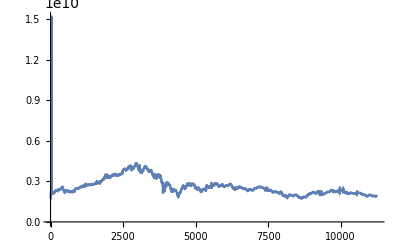

```mathematica
ListLinePlot[twapsWethUsdc120d, PlotRange->All]
```

```mathematica
(* Same issues here for early data as UNI/WETH. Cut off first 40 elements *)
twapsWethUsdc120dFiltered = Table[twapsWethUsdc120d[[i]], {i, 40, Length[twapsWethUsdc120d]}]
```

{2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9,2.56814×10^9,2.57934×10^9,2.59744×10^9,2.61451×10^9,2.62719×10^9,2.63082×10^9,2.6356×10^9,2.64104×10^9,2.64795×10^9,2.65163×10^9,2.65855×10^9,2.65906×10^9,2.65748×10^9,2.65239×10^9,2.65007×10^9,2.64537×10^9,2.6422×10^9,2.63909×10^9,2.63922×10^9,2.63904×10^9,2.63858×10^9,2.63735×10^9,2.63764×10^9,2.63803×10^9,2.63722×10^9,2.63794×10^9,2.6394×10^9,2.63626×10^9,2.6309×10^9,2.62599×10^9,2.62427×10^9,2.62282×10^9,2.62459×10^9,2.62923×10^9,2.63363×10^9,2.63453×10^9,2.63619×10^9,2.63742×10^9,2.6365×10^9,2.63813×10^9,2.63956×10^9,2.63923×10^9,2.63813×10^9,2.63675×10^9,2.63277×10^9,2.62774×10^9,2.6252×10^9,2.62523×10^9,2.62802×10^9,2.63213×10^9,2.63998×10^9,2.65069×10^9,2.66276×10^9,2.67138×10^9,2.67884×10^9,2.6839×10^9,2.68591×10^9,2.68649×10^9,2.68838×10^9,2.69162×10^9,2.69579×10^9,2.69895×10^9,2.70219×10^9,2.70203×10^9,2.6985×10^9,2.69107×10^9,2.68116×10^9,2.6707×10^9,2.65959×10^9,2.65079×10^9,2.6437×10^9,2.64043×10^9,2.63928×10^9,2.63988×10^9,2.6411×10^9,2.64281×10^9,2.6419×10^9,2.63996×10^9,2.63913×10^9,2.63692×10^9,2.63059×10^9,2.629×10^9,2.62375×10^9,2.6125×10^9,2.6043×10^9,2.59472×10^9,2.59248×10^9,2.58477×10^9,2.58679×10^9,2.59057×10^9,2.5975×10^9,2.60157×10^9,2.60817×10^9,2.61214×10^9,2.61509×10^9,2.61697×10^9,2.61809×10^9,2.61915×10^9,2.61857×10^9,2.61463×10^9,2.60977×10^9,2.60421×10^9,2.6001×10^9,2.60019×10^9,2.60194×10^9,2.60676×10^9,2.61245×10^9,2.61714×10^9,2.62146×10^9,2.62891×10^9,2.63716×10^9,2.64614×10^9,2.65821×10^9,2.67367×10^9,2.68377×10^9,2.69346×10^9,2.70188×10^9,2.70791×10^9,2.71172×10^9,2.71441×10^9,2.71902×10^9,2.71242×10^9,2.70675×10^9,2.70174×10^9,2.69608×10^9,2.69353×10^9,2.69857×10^9,2.7032×10^9,2.70851×10^9,2.71255×10^9,2.71347×10^9,2.71033×10^9,2.70519×10^9,2.69555×10^9,2.68986×10^9,2.68374×10^9,2.68337×10^9,2.68503×10^9,2.68906×10^9,2.69365×10^9,2.70085×10^9,2.7055×10^9,2.71066×10^9,2.71477×10^9,2.71774×10^9,2.71978×10^9,2.71976×10^9,2.71957×10^9,2.72293×10^9,2.72605×10^9,2.72826×10^9,2.61748×10^9,2.72971×10^9,2.72785×10^9,2.72473×10^9,2.72449×10^9,2.83875×10^9,2.73048×10^9,2.70685×10^9,2.72574×10^9,2.72363×10^9,2.71831×10^9,2.71326×10^9,2.73625×10^9,2.71169×10^9,2.71164×10^9,2.71516×10^9,2.72376×10^9,2.73414×10^9,2.74182×10^9,2.74377×10^9,2.74286×10^9,2.73679×10^9,2.72737×10^9,2.72313×10^9,2.72223×10^9,2.72211×10^9,2.72412×10^9,2.73119×10^9,2.73578×10^9,2.73961×10^9,2.74275×10^9,2.74377×10^9,2.74148×10^9,2.73802×10^9,2.73215×10^9,2.72686×10^9,2.72274×10^9,2.71851×10^9,2.71589×10^9,2.71682×10^9,2.71852×10^9,2.71973×10^9,2.72099×10^9,2.72118×10^9,2.72036×10^9,2.71803×10^9,2.71711×10^9,2.71625×10^9,2.71402×10^9,2.7077×10^9,2.70253×10^9,2.69641×10^9,2.69104×10^9,2.68881×10^9,2.6873×10^9,2.68706×10^9,2.68928×10^9,2.69198×10^9,2.69406×10^9,2.69883×10^9,2.70389×10^9,2.70778×10^9,2.71183×10^9,2.71527×10^9,2.72096×10^9,2.72397×10^9,2.72755×10^9,2.72925×10^9,2.72992×10^9,2.73064×10^9,2.73154×10^9,2.73126×10^9,2.73096×10^9,2.7294×10^9,2.72633×10^9,2.724×10^9,2.72102×10^9,2.71824×10^9,2.72097×10^9,2.72841×10^9,2.73666×10^9,2.74697×10^9,2.75731×10^9,2.7641×10^9,2.76504×10^9,2.76546×10^9,2.76513×10^9,2.76459×10^9,2.76491×10^9,2.76668×10^9,2.76743×10^9,2.76769×10^9,2.76806×10^9,2.76717×10^9,2.76543×10^9,2.76721×10^9,2.77086×10^9,2.775×10^9,2.78064×10^9,2.78663×10^9,2.78752×10^9,2.78625×10^9,2.78341×10^9,2.77901×10^9,2.77219×10^9,2.76783×10^9,2.76488×10^9,2.76346×10^9,2.7638×10^9,2.76513×10^9,2.7666×10^9,2.76932×10^9,2.77417×10^9,2.77752×10^9,2.78108×10^9,2.7845×10^9,2.78344×10^9,2.77817×10^9,2.77243×10^9,2.76555×10^9,2.75762×10^9,2.74739×10^9,2.74127×10^9,2.738×10^9,2.7346×10^9,2.73519×10^9,2.73259×10^9,2.72757×10^9,2.72235×10^9,2.7184×10^9,2.71327×10^9,2.71615×10^9,2.71967×10^9,2.72248×10^9,2.72501×10^9,2.72742×10^9,2.72738×10^9,2.72296×10^9,2.71582×10^9,2.71306×10^9,2.71057×10^9,2.70641×10^9,2.70649×10^9,2.70927×10^9,2.7094×10^9,2.70879×10^9,2.71196×10^9,2.71795×10^9,2.72507×10^9,2.73315×10^9,2.74055×10^9,2.74832×10^9,2.7532×10^9,2.75747×10^9,2.76008×10^9,2.76143×10^9,2.76196×10^9,2.76191×10^9,2.76149×10^9,2.75977×10^9,2.7548×10^9,2.75368×10^9,2.75089×10^9,2.7477×10^9,2.74435×10^9,2.74318×10^9,2.73905×10^9,2.73823×10^9,2.73931×10^9,2.74195×10^9,2.74371×10^9,2.74567×10^9,2.74399×10^9,2.74219×10^9,2.7421×10^9,2.74112×10^9,2.74029×10^9,2.74087×10^9,2.74219×10^9,2.74109×10^9,2.7422×10^9,2.74414×10^9,2.74721×10^9,2.75003×10^9,2.75336×10^9,2.75674×10^9,2.75873×10^9,2.76045×10^9,2.76198×10^9,2.7632×10^9,2.76403×10^9,2.76461×10^9,2.76565×10^9,2.76728×10^9,2.77046×10^9,2.77379×10^9,2.77742×10^9,2.78123×10^9,2.78293×10^9,2.7827×10^9,2.78245×10^9,2.78097×10^9,2.77977×10^9,2.77746×10^9,2.77616×10^9,2.77466×10^9,2.77401×10^9,2.77533×10^9,2.7787×10^9,2.78216×10^9,2.80134×10^9,2.78906×10^9,2.78842×10^9,2.78723×10^9,2.82806×10^9,2.76798×10^9,2.78159×10^9,2.7813×10^9,2.77825×10^9,2.72922×10^9,2.76753×10^9,2.76317×10^9,2.75753×10^9,2.75353×10^9,2.75102×10^9,2.7483×10^9,2.74567×10^9,2.74392×10^9,2.74468×10^9,2.74638×10^9,2.74819×10^9,2.7477×10^9,2.74719×10^9,2.74595×10^9,2.74403×10^9,2.74128×10^9,2.74355×10^9,2.74612×10^9,2.7494×10^9,2.75331×10^9,2.75533×10^9,2.75248×10^9,2.7507×10^9,2.74822×10^9,2.74593×10^9,2.7459×10^9,2.74559×10^9,2.74579×10^9,2.74671×10^9,2.74729×10^9,2.7484×10^9,2.75239×10^9,2.75614×10^9,2.75919×10^9,2.76152×10^9,2.7637×10^9,2.76366×10^9,2.76471×10^9,2.76466×10^9,2.76468×10^9,2.76518×10^9,2.76498×10^9,2.76413×10^9,2.76529×10^9,2.76855×10^9,2.77194×10^9,2.77473×10^9,2.77689×10^9,2.77822×10^9,2.77799×10^9,2.77618×10^9,2.77409×10^9,2.77224×10^9,2.76982×10^9,2.76719×10^9,2.7649×10^9,2.7613×10^9,2.75929×10^9,2.75776×10^9,2.75645×10^9,2.75597×10^9,2.75652×10^9,2.75541×10^9,2.7544×10^9,2.75292×10^9,2.75267×10^9,2.75227×10^9,2.7536×10^9,2.75607×10^9,2.75943×10^9,2.76309×10^9,2.76715×10^9,2.76933×10^9,2.77048×10^9,2.77078×10^9,2.77071×10^9,2.76979×10^9,2.76909×10^9,2.76776×10^9,2.76768×10^9,2.76883×10^9,2.77949×10^9,2.79242×10^9,2.80527×10^9,2.81563×10^9,2.82967×10^9,2.83186×10^9,2.83186×10^9,2.83116×10^9,2.83322×10^9,2.83502×10^9,2.83731×10^9,2.8405×10^9,2.84328×10^9,2.84375×10^9,2.84361×10^9,2.84323×10^9,2.84274×10^9,2.84259×10^9,2.84563×10^9,2.85031×10^9,2.85527×10^9,2.85864×10^9,2.86233×10^9,2.86076×10^9,2.85856×10^9,2.85557×10^9,2.85439×10^9,2.85513×10^9,2.85625×10^9,2.85655×10^9,2.85682×10^9,2.85649×10^9,2.85557×10^9,2.85521×10^9,2.85615×10^9,2.85757×10^9,2.85818×10^9,2.8577×10^9,2.85372×10^9,2.84594×10^9,2.83934×10^9,2.83444×10^9,2.8325×10^9,2.83316×10^9,2.83598×10^9,2.8374×10^9,2.83687×10^9,2.83468×10^9,2.83461×10^9,2.83743×10^9,2.84098×10^9,2.84543×10^9,2.84947×10^9,2.8527×10^9,2.854×10^9,2.8552×10^9,2.85894×10^9,2.8634×10^9,2.86716×10^9,2.87105×10^9,2.87345×10^9,2.87385×10^9,2.87273×10^9,2.87143×10^9,2.86996×10^9,2.86907×10^9,2.86878×10^9,2.86857×10^9,2.86782×10^9,2.86742×10^9,2.86603×10^9,2.8637×10^9,2.86046×10^9,2.85818×10^9,2.85434×10^9,2.8527×10^9,2.85328×10^9,2.85804×10^9,2.86276×10^9,2.86969×10^9,2.87547×10^9,2.80645×10^9,2.88817×10^9,2.89516×10^9,2.90277×10^9,2.90995×10^9,2.99492×10^9,2.92215×10^9,2.92512×10^9,2.9281×10^9,2.93023×10^9,2.93112×10^9,2.9317×10^9,2.93274×10^9,2.93337×10^9,2.93337×10^9,2.93266×10^9,2.92963×10^9,2.92575×10^9,2.92503×10^9,2.92361×10^9,2.9247×10^9,2.9292×10^9,2.93421×10^9,2.93769×10^9,3.03478×10^9,2.93804×10^9,2.93441×10^9,2.93127×10^9,2.92849×10^9,2.84973×10^9,2.9289×10^9,2.93166×10^9,2.93378×10^9,2.93654×10^9,2.93757×10^9,2.93919×10^9,2.94188×10^9,2.94373×10^9,2.94649×10^9,2.94615×10^9,2.94533×10^9,2.94334×10^9,2.9416×10^9,2.93936×10^9,2.93819×10^9,2.93651×10^9,2.93576×10^9,2.93568×10^9,2.93596×10^9,2.93709×10^9,2.93933×10^9,2.94297×10^9,2.94542×10^9,2.94764×10^9,2.94994×10^9,2.95137×10^9,2.9515×10^9,2.95024×10^9,2.94409×10^9,2.93685×10^9,2.92533×10^9,2.91281×10^9,2.91113×10^9,2.91184×10^9,2.91191×10^9,2.91431×10^9,2.91738×10^9,2.91731×10^9,2.91522×10^9,2.91575×10^9,2.91633×10^9,2.9172×10^9,2.91769×10^9,2.91803×10^9,2.91747×10^9,2.91558×10^9,2.90994×10^9,2.90433×10^9,2.89991×10^9,2.89507×10^9,2.89195×10^9,2.88844×10^9,2.88498×10^9,2.87998×10^9,2.87532×10^9,2.87316×10^9,2.87376×10^9,2.875×10^9,2.87711×10^9,2.87898×10^9,2.88206×10^9,2.88564×10^9,2.89221×10^9,2.89905×10^9,2.90687×10^9,2.91168×10^9,2.9154×10^9,2.91581×10^9,2.91519×10^9,2.91474×10^9,2.91469×10^9,2.91541×10^9,2.91761×10^9,2.9211×10^9,2.92439×10^9,2.92719×10^9,2.92829×10^9,2.92738×10^9,2.92673×10^9,2.92583×10^9,2.92599×10^9,2.92453×10^9,2.92212×10^9,2.92077×10^9,2.91849×10^9,2.9166×10^9,2.9168×10^9,2.91798×10^9,2.91889×10^9,2.91928×10^9,2.91902×10^9,2.81586×10^9,2.91997×10^9,2.92207×10^9,2.92466×10^9,2.92757×10^9,3.04472×10^9,2.93313×10^9,2.93374×10^9,2.93474×10^9,2.93518×10^9,2.93494×10^9,2.93477×10^9,2.93473×10^9,2.93493×10^9,2.93632×10^9,2.938×10^9,2.94001×10^9,2.94144×10^9,2.94487×10^9,2.94892×10^9,2.95266×10^9,2.9592×10^9,2.96545×10^9,2.96951×10^9,2.97281×10^9,2.97447×10^9,2.97448×10^9,2.97352×10^9,2.97196×10^9,2.97037×10^9,2.96885×10^9,2.96757×10^9,2.96789×10^9,2.96959×10^9,2.97161×10^9,2.97374×10^9,2.97396×10^9,2.97038×10^9,2.96509×10^9,2.95729×10^9,2.94817×10^9,2.94357×10^9,2.94192×10^9,2.94294×10^9,2.94426×10^9,2.94644×10^9,2.95175×10^9,2.95794×10^9,2.96718×10^9,2.97438×10^9,2.98319×10^9,2.98637×10^9,2.98854×10^9,2.99013×10^9,2.99205×10^9,2.99826×10^9,3.00421×10^9,3.00858×10^9,3.01404×10^9,3.01764×10^9,3.01749×10^9,3.01875×10^9,3.02059×10^9,3.02486×10^9,3.02954×10^9,3.03463×10^9,3.03939×10^9,3.04473×10^9,3.04978×10^9,3.05285×10^9,3.0543×10^9,3.05471×10^9,3.0537×10^9,3.05238×10^9,3.05422×10^9,3.05571×10^9,3.06099×10^9,3.0702×10^9,3.08027×10^9,3.08642×10^9,3.08984×10^9,3.09292×10^9,3.09329×10^9,3.09247×10^9,3.09069×10^9,3.0893×10^9,3.09236×10^9,3.10229×10^9,3.11249×10^9,3.12166×10^9,3.13349×10^9,3.14192×10^9,3.14816×10^9,3.1563×10^9,3.16645×10^9,3.17416×10^9,3.17874×10^9,3.1755×10^9,3.17232×10^9,3.16874×10^9,3.16586×10^9,3.16861×10^9,3.16742×10^9,3.16414×10^9,3.1593×10^9,3.15435×10^9,3.14781×10^9,3.14722×10^9,3.14946×10^9,3.15466×10^9,3.15986×10^9,3.16539×10^9,3.16726×10^9,3.16749×10^9,3.16459×10^9,3.15916×10^9,3.1508×10^9,3.14581×10^9,3.14291×10^9,3.13797×10^9,3.13545×10^9,3.13475×10^9,3.12745×10^9,3.12068×10^9,3.11636×10^9,3.11706×10^9,3.11962×10^9,3.12807×10^9,3.14131×10^9,3.1519×10^9,3.15746×10^9,3.1652×10^9,3.17054×10^9,3.17034×10^9,3.17038×10^9,3.17194×10^9,3.17099×10^9,3.16982×10^9,3.17997×10^9,3.19805×10^9,3.21332×10^9,3.2328×10^9,3.25006×10^9,3.26408×10^9,3.26847×10^9,3.27346×10^9,3.28292×10^9,3.28874×10^9,3.29368×10^9,3.30162×10^9,3.30984×10^9,3.31551×10^9,3.31525×10^9,3.30975×10^9,3.30738×10^9,3.30371×10^9,3.29632×10^9,3.29271×10^9,3.2954×10^9,3.291×10^9,3.28432×10^9,3.28393×10^9,3.28365×10^9,3.28322×10^9,3.28341×10^9,3.28726×10^9,3.28674×10^9,3.29249×10^9,3.30197×10^9,3.32134×10^9,3.34054×10^9,3.35925×10^9,3.37253×10^9,3.38068×10^9,3.38782×10^9,3.39434×10^9,3.40513×10^9,3.41667×10^9,3.42637×10^9,3.51266×10^9,3.41029×10^9,3.39725×10^9,3.38664×10^9,3.35792×10^9,3.24986×10^9,3.32865×10^9,3.31206×10^9,3.29581×10^9,3.29777×10^9,3.30036×10^9,3.29862×10^9,3.28909×10^9,3.27985×10^9,3.27262×10^9,3.25998×10^9,3.24619×10^9,3.24303×10^9,3.24156×10^9,3.24031×10^9,3.24427×10^9,3.24642×10^9,3.24701×10^9,3.25556×10^9,3.26539×10^9,3.27686×10^9,3.29305×10^9,3.31134×10^9,3.32849×10^9,3.34022×10^9,3.35294×10^9,3.35822×10^9,3.36525×10^9,3.3693×10^9,3.37145×10^9,3.37457×10^9,3.37841×10^9,3.37754×10^9,3.37142×10^9,3.36896×10^9,3.36567×10^9,3.3615×10^9,3.35694×10^9,3.35295×10^9,3.34424×10^9,3.33067×10^9,3.32129×10^9,3.31551×10^9,3.30967×10^9,3.30488×10^9,3.31224×10^9,3.31948×10^9,3.33212×10^9,3.34441×10^9,3.35342×10^9,3.35429×10^9,3.35717×10^9,3.36256×10^9,3.36871×10^9,3.38226×10^9,3.39839×10^9,3.40725×10^9,3.41138×10^9,3.41839×10^9,3.42868×10^9,3.43749×10^9,3.44802×10^9,3.45623×10^9,3.45604×10^9,3.45006×10^9,3.45079×10^9,3.44972×10^9,3.45783×10^9,3.46868×10^9,3.51917×10^9,3.49037×10^9,3.48956×10^9,3.49155×10^9,3.48313×10^9,3.4358×10^9,3.43892×10^9,3.42236×10^9,3.39615×10^9,3.37087×10^9,3.34657×10^9,3.31593×10^9,3.29004×10^9,3.28075×10^9,3.27893×10^9,3.2681×10^9,3.25206×10^9,3.25651×10^9,3.26333×10^9,3.266×10^9,3.27289×10^9,3.29005×10^9,3.30333×10^9,3.30959×10^9,3.31795×10^9,3.3263×10^9,3.33685×10^9,3.34964×10^9,3.35788×10^9,3.36501×10^9,3.37315×10^9,3.38492×10^9,3.38066×10^9,3.3892×10^9,3.40191×10^9,3.40186×10^9,3.38829×10^9,3.39475×10^9,3.38859×10^9,3.38107×10^9,3.38142×10^9,3.38023×10^9,3.37093×10^9,3.36058×10^9,3.35022×10^9,3.33532×10^9,3.31576×10^9,3.30652×10^9,3.28881×10^9,3.28516×10^9,3.28866×10^9,3.29359×10^9,3.29752×10^9,3.29343×10^9,3.28286×10^9,3.2772×10^9,3.27467×10^9,3.27531×10^9,3.28842×10^9,3.30126×10^9,3.31071×10^9,3.3224×10^9,3.33405×10^9,3.34239×10^9,3.35175×10^9,3.36104×10^9,3.36×10^9,3.3598×10^9,3.35398×10^9,3.34512×10^9,3.33837×10^9,3.32631×10^9,3.31173×10^9,3.30417×10^9,3.29825×10^9,3.29722×10^9,3.29596×10^9,3.29762×10^9,3.3007×10^9,3.30004×10^9,3.29202×10^9,3.28085×10^9,3.27257×10^9,3.26674×10^9,3.26707×10^9,3.2698×10^9,3.27276×10^9,3.27289×10^9,3.26668×10^9,3.25799×10^9,3.25262×10^9,3.25011×10^9,3.25127×10^9,3.25661×10^9,3.26576×10^9,3.27656×10^9,3.29321×10^9,3.31361×10^9,3.32532×10^9,3.3378×10^9,3.34953×10^9,3.35215×10^9,3.35474×10^9,3.35306×10^9,3.35051×10^9,3.3493×10^9,3.35174×10^9,3.36157×10^9,3.37043×10^9,3.37489×10^9,3.3781×10^9,3.37729×10^9,3.37389×10^9,3.37052×10^9,3.36914×10^9,3.36728×10^9,3.36537×10^9,3.36126×10^9,3.35838×10^9,3.36096×10^9,3.36457×10^9,3.3672×10^9,3.3687×10^9,3.37161×10^9,3.37156×10^9,3.37133×10^9,3.37312×10^9,3.37377×10^9,3.37571×10^9,3.37184×10^9,3.36254×10^9,3.34794×10^9,3.33756×10^9,3.33144×10^9,3.3282×10^9,3.32911×10^9,3.33675×10^9,3.33777×10^9,3.33083×10^9,3.32658×10^9,3.32181×10^9,3.32384×10^9,3.33698×10^9,3.35683×10^9,3.37555×10^9,3.40635×10^9,3.42307×10^9,3.42605×10^9,3.42653×10^9,3.42208×10^9,3.41643×10^9,3.41196×10^9,3.41093×10^9,3.41133×10^9,3.41151×10^9,3.41222×10^9,3.41535×10^9,3.4203×10^9,3.42624×10^9,3.43622×10^9,3.44464×10^9,3.45552×10^9,3.46154×10^9,3.46323×10^9,3.46303×10^9,3.46052×10^9,3.45735×10^9,3.45413×10^9,3.45352×10^9,3.45198×10^9,3.4458×10^9,3.44212×10^9,3.43952×10^9,3.44475×10^9,3.4542×10^9,3.47486×10^9,3.48566×10^9,3.50763×10^9,3.5143×10^9,3.5187×10^9,3.52307×10^9,3.52401×10^9,3.52443×10^9,3.52302×10^9,3.51368×10^9,3.50429×10^9,3.49398×10^9,3.48502×10^9,3.47471×10^9,3.47133×10^9,3.46861×10^9,3.47011×10^9,3.47167×10^9,3.47457×10^9,3.47948×10^9,3.48454×10^9,3.48789×10^9,3.48886×10^9,3.4901×10^9,3.48767×10^9,3.48328×10^9,3.47816×10^9,3.47322×10^9,3.46939×10^9,3.47022×10^9,3.47472×10^9,3.47892×10^9,3.48229×10^9,3.48288×10^9,3.47733×10^9,3.46901×10^9,3.45886×10^9,3.45214×10^9,3.45047×10^9,3.4511×10^9,3.45088×10^9,3.45123×10^9,3.44522×10^9,3.43796×10^9,3.42941×10^9,3.42031×10^9,3.41839×10^9,3.41277×10^9,3.41588×10^9,3.42038×10^9,3.42859×10^9,3.43534×10^9,3.43857×10^9,3.44491×10^9,3.44685×10^9,3.44589×10^9,3.44467×10^9,3.44487×10^9,3.44461×10^9,3.44562×10^9,3.44888×10^9,3.4538×10^9,3.46161×10^9,3.46931×10^9,3.47585×10^9,3.48429×10^9,3.48798×10^9,3.48863×10^9,3.48842×10^9,3.49183×10^9,3.49581×10^9,3.50211×10^9,3.50543×10^9,3.50945×10^9,3.50871×10^9,3.50535×10^9,3.49845×10^9,3.49544×10^9,3.49064×10^9,3.48719×10^9,3.48625×10^9,3.48553×10^9,3.48357×10^9,3.48326×10^9,3.48508×10^9,3.48769×10^9,3.49314×10^9,3.50298×10^9,3.51713×10^9,3.53195×10^9,3.54276×10^9,3.552×10^9,3.56154×10^9,3.56924×10^9,3.57419×10^9,3.57553×10^9,3.57612×10^9,3.5747×10^9,3.57416×10^9,3.57271×10^9,3.57542×10^9,3.57985×10^9,3.57558×10^9,3.56714×10^9,3.55475×10^9,3.52847×10^9,3.506×10^9,3.48667×10^9,3.46469×10^9,3.44775×10^9,3.44929×10^9,3.45703×10^9,3.45856×10^9,3.46189×10^9,3.46556×10^9,3.46594×10^9,3.45981×10^9,3.46164×10^9,3.46529×10^9,3.47151×10^9,3.47804×10^9,3.48588×10^9,3.49797×10^9,3.50547×10^9,3.51189×10^9,3.51617×10^9,3.52243×10^9,3.52508×10^9,3.52548×10^9,3.52188×10^9,3.51816×10^9,3.51098×10^9,3.5064×10^9,3.49862×10^9,3.50178×10^9,3.50415×10^9,3.50526×10^9,3.50894×10^9,3.5134×10^9,3.5073×10^9,3.50054×10^9,3.49562×10^9,3.48685×10^9,3.47766×10^9,3.47324×10^9,3.47043×10^9,3.46536×10^9,3.45702×10^9,3.4508×10^9,3.44617×10^9,3.44086×10^9,3.43222×10^9,3.43008×10^9,3.42999×10^9,3.43042×10^9,3.42504×10^9,3.41593×10^9,3.41047×10^9,3.40174×10^9,3.39355×10^9,3.39232×10^9,3.39781×10^9,3.40048×10^9,3.40425×10^9,3.40721×10^9,3.41089×10^9,3.41145×10^9,3.41513×10^9,3.42119×10^9,3.42648×10^9,3.43154×10^9,3.43707×10^9,3.44033×10^9,3.44466×10^9,3.44982×10^9,3.45443×10^9,3.45705×10^9,3.45833×10^9,3.45358×10^9,3.44406×10^9,3.43438×10^9,3.42884×10^9,3.42397×10^9,3.42558×10^9,3.43182×10^9,3.43596×10^9,3.43922×10^9,3.44556×10^9,3.44838×10^9,3.45155×10^9,3.45631×10^9,3.46055×10^9,3.46326×10^9,3.46416×10^9,3.46344×10^9,3.4616×10^9,3.45656×10^9,3.45483×10^9,3.45399×10^9,3.45334×10^9,3.4524×10^9,3.48259×10^9,3.45006×10^9,3.45084×10^9,3.45551×10^9,3.46291×10^9,3.44362×10^9,3.48645×10^9,3.49336×10^9,3.49991×10^9,3.50422×10^9,3.5041×10^9,3.50287×10^9,3.50247×10^9,3.49927×10^9,3.49578×10^9,3.49292×10^9,3.49464×10^9,3.49896×10^9,3.50403×10^9,3.50865×10^9,3.52156×10^9,3.53279×10^9,3.54307×10^9,3.55467×10^9,3.56184×10^9,3.56177×10^9,3.55953×10^9,3.55826×10^9,3.5549×10^9,3.55463×10^9,3.5554×10^9,3.55588×10^9,3.55096×10^9,3.54634×10^9,3.54119×10^9,3.53287×10^9,3.52885×10^9,3.52548×10^9,3.52295×10^9,3.52355×10^9,3.52329×10^9,3.52053×10^9,3.52009×10^9,3.51894×10^9,3.5189×10^9,3.51917×10^9,3.51978×10^9,3.51727×10^9,3.513×10^9,3.50502×10^9,3.49649×10^9,3.48896×10^9,3.48574×10^9,3.48453×10^9,3.48352×10^9,3.48605×10^9,3.4836×10^9,3.4751×10^9,3.46672×10^9,3.45863×10^9,3.45155×10^9,3.45079×10^9,3.45319×10^9,3.46011×10^9,3.46729×10^9,3.47273×10^9,3.47608×10^9,3.48421×10^9,3.49115×10^9,3.49783×10^9,3.50477×10^9,3.5158×10^9,3.52132×10^9,3.52755×10^9,3.53403×10^9,3.5384×10^9,3.54106×10^9,3.54225×10^9,3.54153×10^9,3.54076×10^9,3.53726×10^9,3.53578×10^9,3.53457×10^9,3.53343×10^9,3.53254×10^9,3.53249×10^9,3.53413×10^9,3.5379×10^9,3.54604×10^9,3.555×10^9,3.56171×10^9,3.56992×10^9,3.57051×10^9,3.5657×10^9,3.56091×10^9,3.55599×10^9,3.55004×10^9,3.54756×10^9,3.546×10^9,3.54357×10^9,3.54105×10^9,3.5373×10^9,3.53342×10^9,3.52933×10^9,3.52608×10^9,3.52486×10^9,3.52497×10^9,3.52657×10^9,3.52903×10^9,3.53244×10^9,3.53782×10^9,3.54737×10^9,3.55503×10^9,3.56132×10^9,3.56555×10^9,3.56615×10^9,3.56188×10^9,3.5572×10^9,3.55476×10^9,3.55486×10^9,3.55928×10^9,3.5612×10^9,3.56232×10^9,3.56165×10^9,3.55885×10^9,3.55148×10^9,3.54795×10^9,3.54436×10^9,3.54423×10^9,3.54521×10^9,3.54639×10^9,3.54656×10^9,3.54602×10^9,3.54691×10^9,3.54778×10^9,3.55148×10^9,3.55441×10^9,3.56148×10^9,3.56937×10^9,3.58262×10^9,3.59933×10^9,3.61527×10^9,3.63149×10^9,3.6437×10^9,3.65117×10^9,3.65586×10^9,3.74326×10^9,3.66334×10^9,3.66661×10^9,3.66961×10^9,3.66529×10^9,3.58062×10^9,3.67276×10^9,3.68607×10^9,3.70349×10^9,3.73005×10^9,3.75874×10^9,3.7727×10^9,3.78864×10^9,3.8036×10^9,3.80744×10^9,3.81306×10^9,3.82212×10^9,3.82237×10^9,3.82177×10^9,3.8259×10^9,3.82697×10^9,3.82686×10^9,3.83094×10^9,3.83128×10^9,3.82934×10^9,3.82333×10^9,3.81804×10^9,3.81513×10^9,3.8205×10^9,3.8228×10^9,3.8334×10^9,3.8387×10^9,3.84762×10^9,3.85025×10^9,3.85652×10^9,3.86521×10^9,3.87248×10^9,3.88772×10^9,3.9009×10^9,3.91286×10^9,3.9101×10^9,3.90859×10^9,3.90165×10^9,3.88923×10^9,3.87884×10^9,3.88083×10^9,3.87914×10^9,3.8787×10^9,3.88338×10^9,3.88987×10^9,3.88709×10^9,3.87769×10^9,3.87059×10^9,3.8657×10^9,3.86086×10^9,3.86243×10^9,3.86859×10^9,3.87537×10^9,3.88022×10^9,3.88178×10^9,3.87943×10^9,3.87686×10^9,3.87545×10^9,3.87447×10^9,3.88122×10^9,3.89524×10^9,3.90199×10^9,3.91966×10^9,3.92358×10^9,3.9207×10^9,3.90401×10^9,3.89336×10^9,3.87701×10^9,3.8737×10^9,3.87154×10^9,3.88374×10^9,3.8963×10^9,3.90608×10^9,3.9156×10^9,3.91413×10^9,3.92121×10^9,3.9208×10^9,3.92473×10^9,3.93227×10^9,3.94533×10^9,3.95065×10^9,3.95786×10^9,3.96287×10^9,3.96081×10^9,3.95864×10^9,3.95562×10^9,3.95397×10^9,3.95018×10^9,3.9494×10^9,3.95063×10^9,3.95068×10^9,3.94702×10^9,3.94391×10^9,3.93913×10^9,3.93279×10^9,3.92526×10^9,3.91603×10^9,3.90935×10^9,3.90407×10^9,3.89265×10^9,3.88928×10^9,3.88986×10^9,3.88966×10^9,3.89156×10^9,3.90097×10^9,3.90861×10^9,3.91014×10^9,3.90766×10^9,3.89569×10^9,3.87776×10^9,3.85599×10^9,3.83389×10^9,3.81877×10^9,3.79687×10^9,3.78543×10^9,3.78158×10^9,3.78076×10^9,3.77862×10^9,3.78814×10^9,3.79799×10^9,3.80714×10^9,3.8117×10^9,3.82145×10^9,3.82276×10^9,3.82603×10^9,3.82963×10^9,3.83344×10^9,3.83762×10^9,3.84004×10^9,3.84046×10^9,3.85241×10^9,3.87475×10^9,3.89274×10^9,3.91039×10^9,3.92044×10^9,3.93896×10^9,3.93446×10^9,3.92695×10^9,3.92455×10^9,3.92062×10^9,3.9149×10^9,3.91396×10^9,3.91726×10^9,3.91603×10^9,3.9148×10^9,3.9137×10^9,3.91081×10^9,3.90568×10^9,3.90178×10^9,3.89364×10^9,3.88842×10^9,3.88053×10^9,3.87582×10^9,3.87271×10^9,3.87447×10^9,3.87734×10^9,3.88696×10^9,3.89727×10^9,3.90291×10^9,3.91011×10^9,3.91503×10^9,3.91713×10^9,3.91573×10^9,3.91292×10^9,3.91268×10^9,3.91105×10^9,3.90838×10^9,3.90527×10^9,3.90068×10^9,3.89814×10^9,3.89481×10^9,3.89418×10^9,3.89928×10^9,3.90413×10^9,3.90845×10^9,3.91364×10^9,3.91295×10^9,3.91273×10^9,3.91261×10^9,3.91085×10^9,3.90923×10^9,3.90935×10^9,3.90863×10^9,3.90809×10^9,3.9114×10^9,3.91824×10^9,3.92922×10^9,3.93884×10^9,3.94696×10^9,3.95091×10^9,3.95728×10^9,3.96449×10^9,3.97542×10^9,3.98863×10^9,4.00553×10^9,4.02269×10^9,4.03878×10^9,4.04689×10^9,4.05106×10^9,4.05204×10^9,4.05688×10^9,4.06387×10^9,4.07824×10^9,4.09434×10^9,4.10581×10^9,4.11046×10^9,4.11433×10^9,4.1096×10^9,4.11164×10^9,4.11802×10^9,4.12089×10^9,4.12371×10^9,4.12413×10^9,4.12402×10^9,4.12086×10^9,4.11994×10^9,4.12081×10^9,4.12175×10^9,4.11911×10^9,4.11287×10^9,4.10647×10^9,4.1053×10^9,4.10294×10^9,4.1093×10^9,4.12199×10^9,4.13228×10^9,4.13055×10^9,4.12923×10^9,4.12322×10^9,4.11544×10^9,4.10711×10^9,4.10555×10^9,4.09933×10^9,4.09214×10^9,4.07891×10^9,4.06908×10^9,4.06019×10^9,4.04088×10^9,4.0377×10^9,4.04324×10^9,4.05166×10^9,4.06354×10^9,4.08282×10^9,4.09337×10^9,4.10737×10^9,4.11946×10^9,4.1261×10^9,4.13067×10^9,4.13378×10^9,4.13685×10^9,4.13495×10^9,4.12867×10^9,4.12469×10^9,4.11769×10^9,4.11084×10^9,4.09416×10^9,4.08423×10^9,4.08005×10^9,4.08194×10^9,4.08887×10^9,4.10197×10^9,4.1178×10^9,4.14411×10^9,4.15898×10^9,4.17201×10^9,4.18035×10^9,4.17842×10^9,4.17438×10^9,4.17571×10^9,4.17385×10^9,4.16758×10^9,4.16599×10^9,4.16096×10^9,4.15324×10^9,4.14485×10^9,4.13754×10^9,4.13623×10^9,4.13513×10^9,4.13348×10^9,4.13164×10^9,4.12502×10^9,4.11164×10^9,4.08348×10^9,4.0371×10^9,3.98437×10^9,3.94978×10^9,3.91265×10^9,3.88432×10^9,3.88932×10^9,3.90739×10^9,3.92498×10^9,3.94076×10^9,3.96802×10^9,3.99134×10^9,4.00082×10^9,4.01357×10^9,4.02153×10^9,3.85186×10^9,4.00533×10^9,3.99305×10^9,3.97904×10^9,3.96902×10^9,4.13465×10^9,3.94583×10^9,3.94787×10^9,3.95986×10^9,3.95799×10^9,3.948×10^9,3.93562×10^9,3.91788×10^9,3.89444×10^9,3.88262×10^9,3.88678×10^9,3.89112×10^9,3.89406×10^9,3.89697×10^9,3.88851×10^9,3.87404×10^9,3.86068×10^9,3.84955×10^9,3.82838×10^9,3.82168×10^9,3.82463×10^9,3.82746×10^9,3.83452×10^9,3.8513×10^9,3.86618×10^9,3.87339×10^9,3.88578×10^9,3.8937×10^9,3.90141×10^9,3.89917×10^9,3.8946×10^9,3.89215×10^9,3.88863×10^9,3.88553×10^9,3.89406×10^9,3.90707×10^9,3.91958×10^9,3.93413×10^9,3.94034×10^9,3.9459×10^9,3.94848×10^9,3.94808×10^9,3.94747×10^9,3.94697×10^9,3.94368×10^9,3.93986×10^9,3.93445×10^9,3.93142×10^9,3.92677×10^9,3.93244×10^9,3.93591×10^9,3.94447×10^9,3.9596×10^9,3.97429×10^9,3.99649×10^9,4.0189×10^9,4.03843×10^9,4.04758×10^9,4.0512×10^9,4.05322×10^9,4.05116×10^9,4.04583×10^9,4.0316×10^9,4.01485×10^9,3.99749×10^9,3.96917×10^9,3.95836×10^9,3.94772×10^9,3.94967×10^9,3.94708×10^9,3.95243×10^9,3.94382×10^9,3.94227×10^9,3.94069×10^9,3.94402×10^9,3.95375×10^9,3.96281×10^9,3.96818×10^9,3.97542×10^9,3.98022×10^9,3.98711×10^9,3.99905×10^9,4.00156×10^9,4.01059×10^9,4.02501×10^9,4.03681×10^9,4.03996×10^9,4.0411×10^9,4.04201×10^9,4.03566×10^9,4.02696×10^9,4.02386×10^9,4.02746×10^9,4.03039×10^9,4.0344×10^9,4.04182×10^9,4.05218×10^9,4.0643×10^9,4.06866×10^9,4.07165×10^9,4.06711×10^9,4.06119×10^9,4.05768×10^9,4.05645×10^9,4.05441×10^9,4.05656×10^9,4.06441×10^9,4.07113×10^9,4.08582×10^9,4.09817×10^9,4.11539×10^9,4.1267×10^9,4.13384×10^9,4.1404×10^9,4.13459×10^9,4.13162×10^9,4.12614×10^9,4.12262×10^9,4.11788×10^9,4.12311×10^9,4.12381×10^9,4.12715×10^9,4.13142×10^9,4.13466×10^9,4.13899×10^9,4.1451×10^9,4.1554×10^9,4.1597×10^9,4.16642×10^9,4.16956×10^9,4.17178×10^9,4.17319×10^9,4.17379×10^9,4.17413×10^9,4.17599×10^9,4.178×10^9,4.18279×10^9,4.19262×10^9,4.21841×10^9,4.22934×10^9,4.24625×10^9,4.25853×10^9,4.2641×10^9,4.26884×10^9,4.28496×10^9,4.29803×10^9,4.30818×10^9,4.32035×10^9,4.32243×10^9,4.31363×10^9,4.30757×10^9,4.30775×10^9,4.30777×10^9,4.31554×10^9,4.32228×10^9,4.3306×10^9,4.33586×10^9,4.33479×10^9,4.33472×10^9,4.33339×10^9,4.32988×10^9,4.31945×10^9,4.31652×10^9,4.31475×10^9,4.31221×10^9,4.30964×10^9,4.30912×10^9,4.30283×10^9,4.29696×10^9,4.29292×10^9,4.29223×10^9,4.29086×10^9,4.29344×10^9,4.2976×10^9,4.29786×10^9,4.30192×10^9,4.2991×10^9,4.29303×10^9,4.28969×10^9,4.28404×10^9,4.27129×10^9,4.26228×10^9,4.25718×10^9,4.25482×10^9,4.25303×10^9,4.25589×10^9,4.26054×10^9,4.26471×10^9,4.26564×10^9,4.27134×10^9,4.27796×10^9,4.28465×10^9,4.29109×10^9,4.29802×10^9,4.29509×10^9,4.28895×10^9,4.28761×10^9,4.28702×10^9,4.28449×10^9,4.29269×10^9,4.31599×10^9,4.32665×10^9,4.33239×10^9,4.32753×10^9,4.29907×10^9,4.27056×10^9,4.25056×10^9,4.23096×10^9,4.20803×10^9,4.17998×10^9,4.1656×10^9,4.14873×10^9,4.13581×10^9,4.13993×10^9,4.14267×10^9,4.14784×10^9,4.15588×10^9,4.15545×10^9,4.14856×10^9,4.13743×10^9,4.11796×10^9,4.09202×10^9,4.07036×10^9,4.04037×10^9,4.01414×10^9,4.00195×10^9,4.00064×10^9,4.00639×10^9,4.01645×10^9,4.04288×10^9,4.05523×10^9,4.06683×10^9,4.07428×10^9,4.08173×10^9,4.08269×10^9,4.08557×10^9,4.09494×10^9,4.10324×10^9,4.10879×10^9,4.11033×10^9,4.11072×10^9,4.09757×10^9,4.0866×10^9,4.09114×10^9,4.101×10^9,4.10673×10^9,4.10948×10^9,4.09899×10^9,4.06445×10^9,3.97699×10^9,3.9062×10^9,3.86404×10^9,3.84488×10^9,3.83713×10^9,3.87749×10^9,3.91116×10^9,3.93195×10^9,3.94073×10^9,3.94516×10^9,3.95084×10^9,3.9649×10^9,3.97689×10^9,3.99148×10^9,4.00052×10^9,4.00722×10^9,4.00834×10^9,3.99984×10^9,3.98238×10^9,3.96865×10^9,3.95305×10^9,3.92907×10^9,3.92149×10^9,3.92724×10^9,3.93341×10^9,3.94099×10^9,3.9467×10^9,3.94129×10^9,3.93463×10^9,3.93509×10^9,3.94109×10^9,3.95475×10^9,3.97365×10^9,3.98573×10^9,3.99733×10^9,4.00034×10^9,4.00154×10^9,4.00017×10^9,4.00303×10^9,4.00519×10^9,4.00478×10^9,4.00375×10^9,3.99974×10^9,3.70516×10^9,3.97774×10^9,3.96542×10^9,3.95163×10^9,3.94021×10^9,4.20291×10^9,3.8932×10^9,3.87303×10^9,3.84551×10^9,3.81867×10^9,3.78708×10^9,3.76584×10^9,3.75988×10^9,3.75193×10^9,3.74188×10^9,3.73482×10^9,3.71064×10^9,3.6852×10^9,3.67637×10^9,3.67809×10^9,3.69009×10^9,3.7175×10^9,3.73143×10^9,3.75276×10^9,3.76666×10^9,3.77533×10^9,3.79091×10^9,3.80972×10^9,3.80562×10^9,3.80911×10^9,3.81998×10^9,3.82782×10^9,3.83836×10^9,3.858×10^9,3.8728×10^9,3.87842×10^9,3.87894×10^9,3.8643×10^9,3.84876×10^9,3.83156×10^9,3.81204×10^9,3.7935×10^9,3.79171×10^9,3.79783×10^9,3.80823×10^9,3.81974×10^9,3.80815×10^9,3.7866×10^9,3.74747×10^9,3.69395×10^9,3.65261×10^9,3.64082×10^9,3.64927×10^9,3.65415×10^9,3.66856×10^9,3.67319×10^9,3.66206×10^9,3.64099×10^9,3.62802×10^9,3.62655×10^9,3.63904×10^9,3.6556×10^9,3.66925×10^9,3.67507×10^9,3.6808×10^9,3.68184×10^9,3.6837×10^9,3.69111×10^9,3.70419×10^9,3.71354×10^9,3.72905×10^9,3.7436×10^9,3.74649×10^9,3.75631×10^9,3.75731×10^9,3.74585×10^9,3.73632×10^9,3.73822×10^9,3.73536×10^9,3.71834×10^9,3.70471×10^9,3.69195×10^9,3.66884×10^9,3.65843×10^9,3.66591×10^9,3.69031×10^9,3.7137×10^9,3.74114×10^9,3.75996×10^9,3.7771×10^9,3.79488×10^9,3.80858×10^9,3.82854×10^9,3.84068×10^9,3.85742×10^9,3.86703×10^9,3.86848×10^9,3.85861×10^9,3.84793×10^9,3.84004×10^9,3.83009×10^9,3.82052×10^9,3.8135×10^9,3.81248×10^9,3.81188×10^9,3.80576×10^9,3.80374×10^9,3.80348×10^9,3.80587×10^9,3.80467×10^9,3.80264×10^9,3.80043×10^9,3.79869×10^9,3.79545×10^9,3.79661×10^9,3.80313×10^9,3.80907×10^9,3.81975×10^9,3.82968×10^9,3.835×10^9,3.84017×10^9,3.83573×10^9,3.82728×10^9,3.82029×10^9,3.82075×10^9,3.82943×10^9,3.84185×10^9,3.85652×10^9,3.86788×10^9,3.87371×10^9,3.87946×10^9,3.88113×10^9,3.88821×10^9,3.8989×10^9,3.90701×10^9,3.91861×10^9,3.93899×10^9,3.95347×10^9,3.95715×10^9,3.96215×10^9,3.96708×10^9,3.96727×10^9,3.96332×10^9,3.96359×10^9,3.96538×10^9,3.9754×10^9,3.98139×10^9,3.99539×10^9,4.00378×10^9,4.01067×10^9,4.01401×10^9,4.01073×10^9,4.00375×10^9,3.99989×10^9,3.99333×10^9,3.98991×10^9,3.98888×10^9,3.9904×10^9,3.991×10^9,3.99628×10^9,4.00986×10^9,4.02117×10^9,4.03532×10^9,4.04613×10^9,4.05591×10^9,4.05978×10^9,4.07181×10^9,4.08964×10^9,4.1101×10^9,4.12565×10^9,4.13557×10^9,4.14346×10^9,4.14819×10^9,4.14689×10^9,4.13953×10^9,4.13699×10^9,4.13251×10^9,4.12609×10^9,4.12334×10^9,4.1271×10^9,4.12435×10^9,4.1194×10^9,4.11599×10^9,4.11084×10^9,4.10086×10^9,4.09684×10^9,4.08958×10^9,4.08225×10^9,4.07492×10^9,4.07146×10^9,4.0673×10^9,4.06102×10^9,4.06048×10^9,4.05844×10^9,4.04483×10^9,4.03704×10^9,4.02716×10^9,4.01433×10^9,4.00694×10^9,4.01143×10^9,4.01332×10^9,4.02135×10^9,4.0288×10^9,4.03247×10^9,4.04564×10^9,4.06069×10^9,4.06911×10^9,4.07811×10^9,4.08954×10^9,4.08947×10^9,4.08735×10^9,4.08853×10^9,4.09105×10^9,4.09529×10^9,4.09122×10^9,4.08772×10^9,4.08315×10^9,4.06805×10^9,4.05367×10^9,4.05716×10^9,4.05915×10^9,4.07135×10^9,4.08834×10^9,4.09795×10^9,4.10043×10^9,4.10002×10^9,4.09633×10^9,4.09197×10^9,4.08866×10^9,4.07991×10^9,4.0731×10^9,4.06326×10^9,4.05349×10^9,4.04811×10^9,4.04452×10^9,4.04299×10^9,4.04247×10^9,4.04254×10^9,4.03915×10^9,4.03361×10^9,4.02976×10^9,4.02445×10^9,4.0155×10^9,4.01218×10^9,4.01559×10^9,4.0196×10^9,4.01826×10^9,4.01783×10^9,4.00578×10^9,3.99349×10^9,3.9788×10^9,3.95909×10^9,3.94742×10^9,3.93752×10^9,3.93218×10^9,3.92996×10^9,3.92946×10^9,3.92676×10^9,3.91848×10^9,3.91376×10^9,3.91814×10^9,3.92165×10^9,3.9173×10^9,3.91287×10^9,3.90952×10^9,3.89983×10^9,3.88475×10^9,3.87476×10^9,3.86729×10^9,3.85392×10^9,3.84696×10^9,3.84537×10^9,3.85319×10^9,3.86077×10^9,3.86792×10^9,3.87548×10^9,3.88051×10^9,3.88384×10^9,3.88701×10^9,3.89636×10^9,3.90272×10^9,3.90553×10^9,3.91314×10^9,3.91834×10^9,3.91385×10^9,3.90982×10^9,3.9062×10^9,3.90051×10^9,3.88868×10^9,3.88203×10^9,3.87844×10^9,3.8802×10^9,3.88163×10^9,3.8911×10^9,3.89863×10^9,3.89764×10^9,3.88925×10^9,3.87519×10^9,3.85675×10^9,3.83288×10^9,3.8112×10^9,3.78852×10^9,3.77324×10^9,3.75417×10^9,3.74964×10^9,3.75195×10^9,3.75167×10^9,3.75406×10^9,3.75859×10^9,3.7601×10^9,3.7561×10^9,3.7538×10^9,3.75383×10^9,3.74847×10^9,3.7327×10^9,3.71723×10^9,3.71138×10^9,3.71137×10^9,3.72038×10^9,3.73879×10^9,3.76266×10^9,3.77701×10^9,3.78842×10^9,3.79554×10^9,3.80199×10^9,3.80225×10^9,3.80331×10^9,3.80418×10^9,3.80375×10^9,3.80488×10^9,3.80815×10^9,3.8016×10^9,3.79629×10^9,3.78581×10^9,3.76917×10^9,3.7466×10^9,3.72712×10^9,3.70084×10^9,3.68271×10^9,3.68499×10^9,3.70206×10^9,3.72393×10^9,3.74674×10^9,3.76983×10^9,3.7813×10^9,3.78777×10^9,3.7941×10^9,3.80971×10^9,3.82092×10^9,3.82389×10^9,3.82489×10^9,3.82798×10^9,3.82806×10^9,3.8274×10^9,3.82716×10^9,3.82573×10^9,3.81908×10^9,3.81205×10^9,3.80678×10^9,3.80746×10^9,3.80786×10^9,3.81309×10^9,3.8177×10^9,3.82191×10^9,3.81736×10^9,3.81479×10^9,3.81177×10^9,3.80858×10^9,3.80405×10^9,3.79932×10^9,3.79695×10^9,3.8055×10^9,3.82047×10^9,3.84291×10^9,3.85581×10^9,3.86446×10^9,3.86402×10^9,3.86225×10^9,3.85114×10^9,3.84846×10^9,3.84334×10^9,3.83576×10^9,3.83204×10^9,3.82653×10^9,3.81438×10^9,3.81169×10^9,3.8067×10^9,3.80405×10^9,3.80544×10^9,3.81012×10^9,3.81295×10^9,3.81772×10^9,3.82244×10^9,3.82612×10^9,3.83045×10^9,3.83302×10^9,3.83784×10^9,3.84138×10^9,3.84076×10^9,3.83861×10^9,3.83397×10^9,3.82396×10^9,3.81755×10^9,3.80794×10^9,3.80186×10^9,3.79059×10^9,3.77531×10^9,3.75618×10^9,3.74056×10^9,3.72866×10^9,3.71073×10^9,3.709×10^9,3.71065×10^9,3.71264×10^9,3.71543×10^9,3.71926×10^9,3.7137×10^9,3.70714×10^9,3.69902×10^9,3.6873×10^9,3.67614×10^9,3.67616×10^9,3.67063×10^9,3.66337×10^9,3.65393×10^9,3.65301×10^9,3.64593×10^9,3.63065×10^9,3.61561×10^9,3.60695×10^9,3.58391×10^9,3.55542×10^9,3.54398×10^9,3.54134×10^9,3.54672×10^9,3.56603×10^9,3.58846×10^9,3.59698×10^9,3.59328×10^9,3.58517×10^9,3.56207×10^9,3.52941×10^9,3.50644×10^9,3.49614×10^9,3.47452×10^9,3.4552×10^9,3.4473×10^9,3.44514×10^9,3.43114×10^9,3.42176×10^9,3.41747×10^9,3.40836×10^9,3.39745×10^9,3.38722×10^9,3.3801×10^9,3.39227×10^9,3.41376×10^9,3.43443×10^9,3.46563×10^9,3.5025×10^9,3.52167×10^9,3.53027×10^9,3.54028×10^9,3.54086×10^9,3.53637×10^9,3.53978×10^9,3.54635×10^9,3.5513×10^9,3.55881×10^9,3.564×10^9,3.55829×10^9,3.55339×10^9,3.54879×10^9,3.53222×10^9,3.51549×10^9,3.48597×10^9,3.46743×10^9,3.43759×10^9,3.42065×10^9,3.41531×10^9,3.41854×10^9,3.42143×10^9,3.41843×10^9,3.41376×10^9,3.40806×10^9,3.3968×10^9,3.38051×10^9,3.3582×10^9,3.3375×10^9,3.3191×10^9,3.2837×10^9,3.25385×10^9,3.2503×10^9,3.25282×10^9,3.25561×10^9,3.27644×10^9,3.29355×10^9,3.29819×10^9,3.29619×10^9,3.29324×10^9,3.28084×10^9,3.294×10^9,3.32167×10^9,3.34413×10^9,3.37912×10^9,3.41236×10^9,3.41805×10^9,3.41972×10^9,3.43337×10^9,3.44422×10^9,3.46301×10^9,3.48328×10^9,3.49395×10^9,3.50439×10^9,3.51771×10^9,3.52385×10^9,3.53029×10^9,3.53401×10^9,3.53384×10^9,3.52425×10^9,3.5185×10^9,3.50984×10^9,3.51009×10^9,3.51055×10^9,3.5079×10^9,3.50481×10^9,3.497×10^9,3.48291×10^9,3.47397×10^9,3.47564×10^9,3.47732×10^9,3.48441×10^9,3.49703×10^9,3.51061×10^9,3.51707×10^9,3.51713×10^9,3.50768×10^9,3.50096×10^9,3.49012×10^9,3.47923×10^9,3.46885×10^9,3.4643×10^9,3.45705×10^9,3.4505×10^9,3.43438×10^9,3.42214×10^9,3.41067×10^9,3.39936×10^9,3.38738×10^9,3.38175×10^9,3.37698×10^9,3.36697×10^9,3.34839×10^9,3.32999×10^9,3.31463×10^9,3.29967×10^9,3.28977×10^9,3.28033×10^9,3.26675×10^9,3.24697×10^9,3.22138×10^9,3.1982×10^9,3.19106×10^9,3.18923×10^9,3.20058×10^9,3.22251×10^9,3.24451×10^9,3.2672×10^9,3.30093×10^9,3.31948×10^9,3.34981×10^9,3.37183×10^9,3.37946×10^9,3.37531×10^9,3.37742×10^9,3.37943×10^9,3.38169×10^9,3.39435×10^9,3.41114×10^9,3.4237×10^9,3.4277×10^9,3.42172×10^9,3.41716×10^9,3.39205×10^9,3.36288×10^9,3.33827×10^9,3.32505×10^9,3.31657×10^9,3.28975×10^9,3.27702×10^9,3.26224×10^9,3.24558×10^9,3.23244×10^9,3.23444×10^9,3.24783×10^9,3.26537×10^9,3.27293×10^9,3.29442×10^9,3.31251×10^9,3.32269×10^9,3.33485×10^9,3.34912×10^9,3.35681×10^9,3.36179×10^9,3.36964×10^9,3.37671×10^9,3.38295×10^9,3.39009×10^9,3.39029×10^9,3.38404×10^9,3.38192×10^9,3.38019×10^9,3.38069×10^9,3.38427×10^9,3.3893×10^9,3.39349×10^9,3.39409×10^9,3.3919×10^9,3.39906×10^9,3.41108×10^9,3.42081×10^9,3.43875×10^9,3.46341×10^9,3.47802×10^9,3.49311×10^9,3.51076×10^9,3.5215×10^9,3.52784×10^9,3.53129×10^9,3.5333×10^9,3.53709×10^9,3.53957×10^9,3.53348×10^9,3.52693×10^9,3.51451×10^9,3.4999×10^9,3.49063×10^9,3.49024×10^9,3.49137×10^9,3.49716×10^9,3.50291×10^9,3.50517×10^9,3.50745×10^9,3.50475×10^9,3.49822×10^9,3.48781×10^9,3.47665×10^9,3.4705×10^9,3.46524×10^9,3.46324×10^9,3.46422×10^9,3.46992×10^9,3.47527×10^9,3.4825×10^9,3.48955×10^9,3.49684×10^9,3.49955×10^9,3.50225×10^9,3.50646×10^9,3.51546×10^9,3.51933×10^9,3.51881×10^9,3.51567×10^9,3.50545×10^9,3.48399×10^9,3.4638×10^9,3.4446×10^9,3.41714×10^9,3.4054×10^9,3.39857×10^9,3.38696×10^9,3.3702×10^9,3.36171×10^9,3.34232×10^9,3.31536×10^9,3.30122×10^9,3.3037×10^9,3.31068×10^9,3.32665×10^9,3.34775×10^9,3.36065×10^9,3.37053×10^9,3.36699×10^9,3.36075×10^9,3.36827×10^9,3.38003×10^9,3.38721×10^9,3.40152×10^9,3.41784×10^9,3.42242×10^9,3.42075×10^9,3.4179×10^9,3.40497×10^9,3.39331×10^9,3.46745×10^9,3.37066×10^9,3.36602×10^9,3.36274×10^9,3.35827×10^9,3.26953×10^9,3.35576×10^9,3.36708×10^9,3.37949×10^9,3.3863×10^9,3.39782×10^9,3.40859×10^9,3.41447×10^9,3.41987×10^9,3.43181×10^9,3.43977×10^9,3.4425×10^9,3.44108×10^9,3.43483×10^9,3.42398×10^9,3.41218×10^9,3.40557×10^9,3.40596×10^9,3.40356×10^9,3.39199×10^9,3.38298×10^9,3.37345×10^9,3.3571×10^9,3.35395×10^9,3.36529×10^9,3.37867×10^9,3.38987×10^9,3.40067×10^9,3.40469×10^9,3.40322×10^9,3.38928×10^9,3.36517×10^9,3.33857×10^9,3.30036×10^9,3.26438×10^9,3.23868×10^9,3.21833×10^9,3.20198×10^9,3.19096×10^9,3.1874×10^9,3.17792×10^9,3.15504×10^9,3.1414×10^9,3.1309×10^9,3.1214×10^9,3.11368×10^9,3.11638×10^9,3.11358×10^9,3.09728×10^9,3.06619×10^9,3.02977×10^9,2.98709×10^9,2.95552×10^9,2.9444×10^9,2.95064×10^9,2.96126×10^9,2.96879×10^9,2.93567×10^9,2.96811×10^9,2.96511×10^9,2.96704×10^9,2.97348×10^9,3.01105×10^9,2.97019×10^9,2.95301×10^9,2.9397×10^9,2.93333×10^9,2.93951×10^9,2.94842×10^9,2.96169×10^9,2.96481×10^9,2.96503×10^9,2.96114×10^9,2.95889×10^9,2.96274×10^9,2.97333×10^9,2.9802×10^9,2.97965×10^9,2.97485×10^9,2.96867×10^9,2.96082×10^9,2.94925×10^9,2.94094×10^9,2.92352×10^9,2.90231×10^9,2.87697×10^9,2.85292×10^9,2.81334×10^9,2.75973×10^9,2.72022×10^9,2.69109×10^9,2.67203×10^9,2.67034×10^9,2.67634×10^9,2.65766×10^9,2.6005×10^9,2.49539×10^9,2.37073×10^9,2.25079×10^9,2.15935×10^9,2.14177×10^9,2.16493×10^9,2.21783×10^9,2.27171×10^9,2.33792×10^9,2.36736×10^9,2.38907×10^9,2.42316×10^9,2.46285×10^9,2.50175×10^9,2.5499×10^9,2.6269×10^9,2.65763×10^9,2.67786×10^9,2.70249×10^9,2.73176×10^9,2.75894×10^9,2.8034×10^9,2.84431×10^9,2.85691×10^9,2.84385×10^9,2.83104×10^9,2.80202×10^9,2.75192×10^9,2.71938×10^9,2.68778×10^9,2.65168×10^9,2.63364×10^9,2.62987×10^9,2.61962×10^9,2.61207×10^9,2.61669×10^9,2.62404×10^9,2.62965×10^9,2.63081×10^9,2.63998×10^9,2.644×10^9,2.60872×10^9,2.57297×10^9,2.54035×10^9,2.52747×10^9,2.52109×10^9,2.52907×10^9,2.54964×10^9,2.58367×10^9,2.61213×10^9,2.63511×10^9,2.65692×10^9,2.66708×10^9,2.65734×10^9,2.64494×10^9,2.62796×10^9,2.59282×10^9,2.55795×10^9,2.53731×10^9,2.51791×10^9,2.48047×10^9,2.43425×10^9,2.37828×10^9,2.32305×10^9,2.27059×10^9,2.25089×10^9,2.2544×10^9,2.27455×10^9,2.29866×10^9,2.33289×10^9,2.35644×10^9,2.37997×10^9,2.40211×10^9,2.42699×10^9,2.44083×10^9,2.45114×10^9,2.45714×10^9,2.45984×10^9,2.47047×10^9,2.45603×10^9,2.50288×10^9,2.51589×10^9,2.53232×10^9,2.5613×10^9,2.61062×10^9,2.57743×10^9,2.5912×10^9,2.6125×10^9,2.62724×10^9,2.62706×10^9,2.62757×10^9,2.63143×10^9,2.63508×10^9,2.63982×10^9,2.65345×10^9,2.67663×10^9,2.70064×10^9,2.71826×10^9,2.72547×10^9,2.73084×10^9,2.72955×10^9,2.71794×10^9,2.70465×10^9,2.69715×10^9,2.68771×10^9,2.67406×10^9,2.65752×10^9,2.64683×10^9,2.64366×10^9,2.64262×10^9,2.65154×10^9,2.66519×10^9,2.67455×10^9,2.67846×10^9,2.68537×10^9,2.68761×10^9,2.69131×10^9,2.69874×10^9,2.71118×10^9,2.71914×10^9,2.73055×10^9,2.75426×10^9,2.78×10^9,2.81168×10^9,2.84145×10^9,2.88063×10^9,2.91068×10^9,2.92932×10^9,2.93362×10^9,2.93724×10^9,2.93834×10^9,2.92258×10^9,2.92069×10^9,2.92673×10^9,2.92367×10^9,2.92148×10^9,2.92897×10^9,2.92825×10^9,2.92525×10^9,2.92122×10^9,2.88556×10^9,2.84109×10^9,2.79943×10^9,2.746×10^9,2.70382×10^9,2.69799×10^9,2.70045×10^9,2.69956×10^9,2.71662×10^9,2.72979×10^9,2.73432×10^9,2.74321×10^9,2.75503×10^9,2.76519×10^9,2.77379×10^9,2.78303×10^9,2.78905×10^9,2.79372×10^9,2.79798×10^9,2.79801×10^9,2.7975×10^9,2.80456×10^9,2.80871×10^9,2.80901×10^9,2.79885×10^9,2.79091×10^9,2.78269×10^9,2.77717×10^9,2.7802×10^9,2.79453×10^9,2.8091×10^9,2.81874×10^9,2.82017×10^9,2.80995×10^9,2.79691×10^9,2.79718×10^9,2.79182×10^9,2.78922×10^9,2.79353×10^9,2.795×10^9,2.78593×10^9,2.78919×10^9,2.79507×10^9,2.80891×10^9,2.83336×10^9,2.85983×10^9,2.87766×10^9,2.89546×10^9,2.90734×10^9,2.91099×10^9,2.90954×10^9,2.90669×10^9,2.89765×10^9,2.88678×10^9,2.87633×10^9,2.86832×10^9,2.85796×10^9,2.85039×10^9,2.8369×10^9,2.82659×10^9,2.81418×10^9,2.80395×10^9,2.79674×10^9,2.81205×10^9,2.78302×10^9,2.77762×10^9,2.77592×10^9,2.77003×10^9,2.74518×10^9,2.7719×10^9,2.77056×10^9,2.76178×10^9,2.75576×10^9,2.7476×10^9,2.74071×10^9,2.7343×10^9,2.73731×10^9,2.74401×10^9,2.74696×10^9,2.74057×10^9,2.7305×10^9,2.71851×10^9,2.70311×10^9,2.68781×10^9,2.6839×10^9,2.68311×10^9,2.68006×10^9,2.68549×10^9,2.70027×10^9,2.70863×10^9,2.7202×10^9,2.73787×10^9,2.74785×10^9,2.75069×10^9,2.75417×10^9,2.75373×10^9,2.75216×10^9,2.74915×10^9,2.73921×10^9,2.72338×10^9,2.7081×10^9,2.69456×10^9,2.68192×10^9,2.68519×10^9,2.6948×10^9,2.7022×10^9,2.70246×10^9,2.69932×10^9,2.68961×10^9,2.67897×10^9,2.67623×10^9,2.6796×10^9,2.68847×10^9,2.70033×10^9,2.71648×10^9,2.70065×10^9,2.66661×10^9,2.61492×10^9,2.57589×10^9,2.53255×10^9,2.51784×10^9,2.51586×10^9,2.51512×10^9,2.50147×10^9,2.47884×10^9,2.45463×10^9,2.44665×10^9,2.45171×10^9,2.45972×10^9,2.46786×10^9,2.47343×10^9,2.47453×10^9,2.46746×10^9,2.46356×10^9,2.46744×10^9,2.47106×10^9,2.4597×10^9,2.44947×10^9,2.4442×10^9,2.44123×10^9,2.43694×10^9,2.44439×10^9,2.44325×10^9,2.42747×10^9,2.40484×10^9,2.38947×10^9,2.35682×10^9,2.33415×10^9,2.32814×10^9,2.32239×10^9,2.30124×10^9,2.28722×10^9,2.25795×10^9,2.24119×10^9,2.23561×10^9,2.25666×10^9,2.27949×10^9,2.31838×10^9,2.34556×10^9,2.36564×10^9,2.37936×10^9,2.38099×10^9,2.38754×10^9,2.39971×10^9,2.40263×10^9,2.40377×10^9,2.40912×10^9,2.41644×10^9,2.41331×10^9,2.41079×10^9,2.40999×10^9,2.41497×10^9,2.41844×10^9,2.42514×10^9,2.43098×10^9,2.44199×10^9,2.4506×10^9,2.45167×10^9,2.45396×10^9,2.46125×10^9,2.46292×10^9,2.45616×10^9,2.44802×10^9,2.43633×10^9,2.42164×10^9,2.39903×10^9,2.38346×10^9,2.36796×10^9,2.35181×10^9,2.33982×10^9,2.33269×10^9,2.31526×10^9,2.3019×10^9,2.28611×10^9,2.2708×10^9,2.25099×10^9,2.23506×10^9,2.22294×10^9,2.22082×10^9,2.21496×10^9,2.21121×10^9,2.21445×10^9,2.21703×10^9,2.21478×10^9,2.21619×10^9,2.21985×10^9,2.21927×10^9,2.22265×10^9,2.22253×10^9,2.2241×10^9,2.23668×10^9,2.25847×10^9,2.2812×10^9,2.30661×10^9,2.33077×10^9,2.34303×10^9,2.34106×10^9,2.33893×10^9,2.34311×10^9,2.34545×10^9,2.34542×10^9,2.3483×10^9,2.35262×10^9,2.35182×10^9,2.36036×10^9,2.38342×10^9,2.40797×10^9,2.42738×10^9,2.44067×10^9,2.43979×10^9,2.42859×10^9,2.42371×10^9,2.41839×10^9,2.41631×10^9,2.42133×10^9,2.42501×10^9,2.41935×10^9,2.41655×10^9,2.41753×10^9,2.41933×10^9,2.42702×10^9,2.43602×10^9,2.44392×10^9,2.44284×10^9,2.43871×10^9,2.42119×10^9,2.39165×10^9,2.38553×10^9,2.37165×10^9,2.34877×10^9,2.33798×10^9,2.34889×10^9,2.34152×10^9,2.34224×10^9,2.35317×10^9,2.36145×10^9,2.36474×10^9,2.36468×10^9,2.36595×10^9,2.36377×10^9,2.35671×10^9,2.34474×10^9,2.33049×10^9,2.31787×10^9,2.30237×10^9,2.29556×10^9,2.29×10^9,2.28693×10^9,2.28617×10^9,2.28672×10^9,2.29065×10^9,2.29343×10^9,2.29722×10^9,2.30374×10^9,2.30034×10^9,2.29588×10^9,2.29798×10^9,2.30329×10^9,2.3086×10^9,2.3243×10^9,2.33826×10^9,2.34612×10^9,2.35339×10^9,2.3574×10^9,2.35811×10^9,2.35962×10^9,2.36238×10^9,2.35849×10^9,2.35345×10^9,2.35043×10^9,2.34349×10^9,2.33761×10^9,2.34065×10^9,2.34411×10^9,2.34512×10^9,2.34296×10^9,2.33723×10^9,2.31858×10^9,2.30777×10^9,2.29725×10^9,2.29757×10^9,2.30606×10^9,2.32298×10^9,2.335×10^9,2.3491×10^9,2.36042×10^9,2.36366×10^9,2.36381×10^9,2.3618×10^9,2.35481×10^9,2.34455×10^9,2.33526×10^9,2.32488×10^9,2.31402×10^9,2.30486×10^9,2.3011×10^9,2.30283×10^9,2.30634×10^9,2.31186×10^9,2.31487×10^9,2.31466×10^9,2.30791×10^9,2.30148×10^9,2.29498×10^9,2.29124×10^9,2.28093×10^9,2.26734×10^9,2.25572×10^9,2.24647×10^9,2.23581×10^9,2.23276×10^9,2.23564×10^9,2.23314×10^9,2.2287×10^9,2.22157×10^9,2.21458×10^9,2.2099×10^9,2.20298×10^9,2.19577×10^9,2.18839×10^9,2.17887×10^9,2.16508×10^9,2.15088×10^9,2.1397×10^9,2.12481×10^9,2.10782×10^9,2.08291×10^9,2.08872×10^9,2.04866×10^9,2.03948×10^9,2.0395×10^9,2.04301×10^9,2.02197×10^9,2.05217×10^9,2.06061×10^9,2.07315×10^9,2.09851×10^9,2.11913×10^9,2.13243×10^9,2.13276×10^9,2.13451×10^9,2.12854×10^9,2.12569×10^9,2.12002×10^9,2.1168×10^9,2.10283×10^9,2.08218×10^9,2.05156×10^9,2.01441×10^9,1.9772×10^9,1.94687×10^9,1.92281×10^9,1.91342×10^9,1.91851×10^9,1.92902×10^9,1.93224×10^9,1.93987×10^9,1.94832×10^9,1.95525×10^9,1.95859×10^9,1.9594×10^9,1.95751×10^9,1.95475×10^9,1.94102×10^9,1.92948×10^9,1.92022×10^9,1.90136×10^9,1.87389×10^9,1.84232×10^9,1.81688×10^9,1.80834×10^9,1.82923×10^9,1.85579×10^9,1.88803×10^9,1.91853×10^9,1.93313×10^9,1.91627×10^9,1.90531×10^9,1.9044×10^9,1.90152×10^9,1.89559×10^9,1.90358×10^9,1.90779×10^9,1.91441×10^9,1.92677×10^9,1.94121×10^9,1.95337×10^9,1.97278×10^9,1.99033×10^9,2.00052×10^9,2.01489×10^9,2.03715×10^9,2.05374×10^9,2.06183×10^9,2.08252×10^9,2.09834×10^9,2.10081×10^9,2.10179×10^9,2.10635×10^9,2.10593×10^9,2.10943×10^9,2.11359×10^9,2.11239×10^9,2.10323×10^9,2.09485×10^9,2.08502×10^9,2.0855×10^9,2.08928×10^9,2.09697×10^9,2.10482×10^9,2.11692×10^9,2.13267×10^9,2.14699×10^9,2.15855×10^9,2.1642×10^9,2.15925×10^9,2.14294×10^9,2.12797×10^9,2.12194×10^9,2.12077×10^9,2.1225×10^9,2.12366×10^9,2.12767×10^9,2.13077×10^9,2.12995×10^9,2.13307×10^9,2.14664×10^9,2.15705×10^9,2.16493×10^9,2.17127×10^9,2.16975×10^9,2.16501×10^9,2.15735×10^9,2.14897×10^9,2.14101×10^9,2.13132×10^9,2.12526×10^9,2.12698×10^9,2.12746×10^9,2.1258×10^9,2.12862×10^9,2.13039×10^9,2.1258×10^9,2.12448×10^9,2.12939×10^9,2.13725×10^9,2.14599×10^9,2.16402×10^9,2.18078×10^9,2.20476×10^9,2.22772×10^9,2.25081×10^9,2.2645×10^9,2.27296×10^9,2.28532×10^9,2.28613×10^9,2.28379×10^9,2.28367×10^9,2.28184×10^9,2.27583×10^9,2.27618×10^9,2.27467×10^9,2.26816×10^9,2.26082×10^9,2.25965×10^9,2.26052×10^9,2.25544×10^9,2.25365×10^9,2.25794×10^9,2.26414×10^9,2.2685×10^9,2.28612×10^9,2.30938×10^9,2.32941×10^9,2.34747×10^9,2.3654×10^9,2.38635×10^9,2.39823×10^9,2.4063×10^9,2.41567×10^9,2.41143×10^9,2.40405×10^9,2.39549×10^9,2.39253×10^9,2.40398×10^9,2.41375×10^9,2.41393×10^9,2.41955×10^9,2.42829×10^9,2.43206×10^9,2.44366×10^9,2.46255×10^9,2.47614×10^9,2.48828×10^9,2.49199×10^9,2.47867×10^9,2.46853×10^9,2.46446×10^9,2.45647×10^9,2.45665×10^9,2.46655×10^9,2.47303×10^9,2.48374×10^9,2.49943×10^9,2.51468×10^9,2.52765×10^9,2.54735×10^9,2.55925×10^9,2.56296×10^9,2.56853×10^9,2.56952×10^9,2.56109×10^9,2.55648×10^9,2.57011×10^9,2.58939×10^9,2.60418×10^9,2.61965×10^9,2.62907×10^9,2.62263×10^9,2.6163×10^9,2.61981×10^9,2.62629×10^9,2.63563×10^9,2.6391×10^9,2.63616×10^9,2.63108×10^9,2.62524×10^9,2.6007×10^9,2.61096×10^9,2.60204×10^9,2.59591×10^9,2.59016×10^9,2.6075×10^9,2.59947×10^9,2.61283×10^9,2.62424×10^9,2.64296×10^9,2.66851×10^9,2.68983×10^9,2.70917×10^9,2.72429×10^9,2.72552×10^9,2.72137×10^9,2.70719×10^9,2.69369×10^9,2.67928×10^9,2.66577×10^9,2.64792×10^9,2.63911×10^9,2.63378×10^9,2.61889×10^9,2.60257×10^9,2.59332×10^9,2.58293×10^9,2.57105×10^9,2.56875×10^9,2.57464×10^9,2.58246×10^9,2.57721×10^9,2.57395×10^9,2.57586×10^9,2.57963×10^9,2.57492×10^9,2.58118×10^9,2.55599×10^9,2.58192×10^9,2.57702×10^9,2.57817×10^9,2.58509×10^9,2.62988×10^9,2.61191×10^9,2.62627×10^9,2.64264×10^9,2.65303×10^9,2.65577×10^9,2.65936×10^9,2.65692×10^9,2.65282×10^9,2.65168×10^9,2.64744×10^9,2.64222×10^9,2.63664×10^9,2.62791×10^9,2.6146×10^9,2.60128×10^9,2.59345×10^9,2.58376×10^9,2.57462×10^9,2.57044×10^9,2.56036×10^9,2.54148×10^9,2.52354×10^9,2.50155×10^9,2.47356×10^9,2.45578×10^9,2.45286×10^9,2.4456×10^9,2.44655×10^9,2.45019×10^9,2.4472×10^9,2.43582×10^9,2.4328×10^9,2.43472×10^9,2.43128×10^9,2.43128×10^9,2.44466×10^9,2.45633×10^9,2.47307×10^9,2.50261×10^9,2.52341×10^9,2.53584×10^9,2.55324×10^9,2.5692×10^9,2.58751×10^9,2.603×10^9,2.61357×10^9,2.61262×10^9,2.6091×10^9,2.59769×10^9,2.59091×10^9,2.59036×10^9,2.59179×10^9,2.58713×10^9,2.58593×10^9,2.582×10^9,2.58018×10^9,2.58068×10^9,2.57888×10^9,2.57336×10^9,2.57203×10^9,2.57123×10^9,2.56968×10^9,2.57254×10^9,2.5831×10^9,2.59274×10^9,2.59658×10^9,2.59481×10^9,2.59007×10^9,2.58356×10^9,2.57556×10^9,2.5633×10^9,2.55355×10^9,2.55179×10^9,2.5472×10^9,2.54264×10^9,2.54677×10^9,2.55192×10^9,2.55157×10^9,2.55341×10^9,2.56177×10^9,2.57179×10^9,2.5823×10^9,2.60243×10^9,2.62326×10^9,2.64533×10^9,2.66556×10^9,2.6852×10^9,2.69465×10^9,2.70174×10^9,2.70456×10^9,2.69913×10^9,2.6963×10^9,2.69975×10^9,2.69888×10^9,2.694×10^9,2.6901×10^9,2.68633×10^9,2.68067×10^9,2.68113×10^9,2.6877×10^9,2.70016×10^9,2.71271×10^9,2.72797×10^9,2.74408×10^9,2.76132×10^9,2.78246×10^9,2.79534×10^9,2.80243×10^9,2.80859×10^9,2.8095×10^9,2.80808×10^9,2.81023×10^9,2.8171×10^9,2.82337×10^9,2.82541×10^9,2.81988×10^9,2.81487×10^9,2.80877×10^9,2.80292×10^9,2.80471×10^9,2.80705×10^9,2.81328×10^9,2.81813×10^9,2.81929×10^9,2.81787×10^9,2.81905×10^9,2.82411×10^9,2.83479×10^9,2.85018×10^9,2.86418×10^9,2.87363×10^9,2.87779×10^9,2.87639×10^9,2.87858×10^9,2.87586×10^9,2.87058×10^9,2.8682×10^9,2.8659×10^9,2.85333×10^9,2.85279×10^9,2.85731×10^9,2.8563×10^9,2.85406×10^9,2.85532×10^9,2.85066×10^9,2.84153×10^9,2.83043×10^9,2.81883×10^9,2.81028×10^9,2.80625×10^9,2.80347×10^9,2.8083×10^9,2.8126×10^9,2.81784×10^9,2.82588×10^9,2.83752×10^9,2.84581×10^9,2.85485×10^9,2.85085×10^9,2.83444×10^9,2.81795×10^9,2.80103×10^9,2.77821×10^9,2.75027×10^9,2.74368×10^9,2.74302×10^9,2.74585×10^9,2.75038×10^9,2.75594×10^9,2.75475×10^9,2.74597×10^9,2.74127×10^9,2.73659×10^9,2.73624×10^9,2.7431×10^9,2.75705×10^9,2.75865×10^9,2.75833×10^9,2.75064×10^9,2.72826×10^9,2.7095×10^9,2.70045×10^9,2.69831×10^9,2.69752×10^9,2.70905×10^9,2.71526×10^9,2.72107×10^9,2.72453×10^9,2.73178×10^9,2.73385×10^9,2.73593×10^9,2.73084×10^9,2.72664×10^9,2.7238×10^9,2.72409×10^9,2.72555×10^9,2.73793×10^9,2.74952×10^9,2.7678×10^9,2.77874×10^9,2.79109×10^9,2.7971×10^9,2.79805×10^9,2.79831×10^9,2.80325×10^9,2.80524×10^9,2.80945×10^9,2.816×10^9,2.82366×10^9,2.82472×10^9,2.82848×10^9,2.83188×10^9,2.83348×10^9,2.83909×10^9,2.84947×10^9,2.8591×10^9,2.86381×10^9,2.86325×10^9,2.85351×10^9,2.83951×10^9,2.82705×10^9,2.80976×10^9,2.79355×10^9,2.81021×10^9,2.76887×10^9,2.74771×10^9,2.72987×10^9,2.72499×10^9,2.69178×10^9,2.71146×10^9,2.7128×10^9,2.71183×10^9,2.69973×10^9,2.68942×10^9,2.68391×10^9,2.67809×10^9,2.67071×10^9,2.67336×10^9,2.6769×10^9,2.67599×10^9,2.67507×10^9,2.68036×10^9,2.68475×10^9,2.68483×10^9,2.6853×10^9,2.68711×10^9,2.6886×10^9,2.69386×10^9,2.70366×10^9,2.71153×10^9,2.72148×10^9,2.72732×10^9,2.73025×10^9,2.73743×10^9,2.74029×10^9,2.74207×10^9,2.74389×10^9,2.74377×10^9,2.74011×10^9,2.73525×10^9,2.73615×10^9,2.7385×10^9,2.74504×10^9,2.75202×10^9,2.7622×10^9,2.77184×10^9,2.77874×10^9,2.78282×10^9,2.78718×10^9,2.78968×10^9,2.7926×10^9,2.79205×10^9,2.79278×10^9,2.79329×10^9,2.79438×10^9,2.79417×10^9,2.79554×10^9,2.79879×10^9,2.80314×10^9,2.80892×10^9,2.81663×10^9,2.81961×10^9,2.81859×10^9,2.81833×10^9,2.81125×10^9,2.80347×10^9,2.80333×10^9,2.81068×10^9,2.81825×10^9,2.82938×10^9,2.83722×10^9,2.84805×10^9,2.84757×10^9,2.84947×10^9,2.8515×10^9,2.8548×10^9,2.85459×10^9,2.84818×10^9,2.8375×10^9,2.82639×10^9,2.81899×10^9,2.81094×10^9,2.80255×10^9,2.79871×10^9,2.79345×10^9,2.78639×10^9,2.77999×10^9,2.77807×10^9,2.77742×10^9,2.77793×10^9,2.7796×10^9,2.78214×10^9,2.78634×10^9,2.78733×10^9,2.78716×10^9,2.78701×10^9,2.78693×10^9,2.78518×10^9,2.78388×10^9,2.77994×10^9,2.77317×10^9,2.76658×10^9,2.76099×10^9,2.75375×10^9,2.75163×10^9,2.75124×10^9,2.75049×10^9,2.74465×10^9,2.73856×10^9,2.73266×10^9,2.73131×10^9,2.73552×10^9,2.74567×10^9,2.75822×10^9,2.76942×10^9,2.77527×10^9,2.7779×10^9,2.7763×10^9,2.77146×10^9,2.77002×10^9,2.69536×10^9,2.75624×10^9,2.76639×10^9,2.74842×10^9,2.74038×10^9,2.80948×10^9,2.74098×10^9,2.72327×10^9,2.73443×10^9,2.72902×10^9,2.71845×10^9,2.7059×10^9,2.70122×10^9,2.69812×10^9,2.70003×10^9,2.70613×10^9,2.71233×10^9,2.71572×10^9,2.71969×10^9,2.72264×10^9,2.72488×10^9,2.72476×10^9,2.72305×10^9,2.72058×10^9,2.71975×10^9,2.71735×10^9,2.7138×10^9,2.71064×10^9,2.7036×10^9,2.6952×10^9,2.68633×10^9,2.67653×10^9,2.67166×10^9,2.66786×10^9,2.6655×10^9,2.6529×10^9,2.63633×10^9,2.62059×10^9,2.59407×10^9,2.56904×10^9,2.5572×10^9,2.55292×10^9,2.5503×10^9,2.55426×10^9,2.55998×10^9,2.56157×10^9,2.5644×10^9,2.56601×10^9,2.56341×10^9,2.56129×10^9,2.56194×10^9,2.55948×10^9,2.54249×10^9,2.52547×10^9,2.50509×10^9,2.48811×10^9,2.47486×10^9,2.47661×10^9,2.47769×10^9,2.48435×10^9,2.49226×10^9,2.49588×10^9,2.49722×10^9,2.50171×10^9,2.50258×10^9,2.49977×10^9,2.49429×10^9,2.48381×10^9,2.47553×10^9,2.46904×10^9,2.47901×10^9,2.49262×10^9,2.51205×10^9,2.53097×10^9,2.55693×10^9,2.56926×10^9,2.57723×10^9,2.58729×10^9,2.59539×10^9,2.59247×10^9,2.58823×10^9,2.5844×10^9,2.57588×10^9,2.56752×10^9,2.56149×10^9,2.55763×10^9,2.55691×10^9,2.55107×10^9,2.55849×10^9,2.55805×10^9,2.55152×10^9,2.54233×10^9,2.53965×10^9,2.52252×10^9,2.50841×10^9,2.50346×10^9,2.50029×10^9,2.49725×10^9,2.49438×10^9,2.49784×10^9,2.49658×10^9,2.49456×10^9,2.4962×10^9,2.49829×10^9,2.50381×10^9,2.51186×10^9,2.52018×10^9,2.52315×10^9,2.52173×10^9,2.51674×10^9,2.51212×10^9,2.50712×10^9,2.50578×10^9,2.50032×10^9,2.48967×10^9,2.47639×10^9,2.45201×10^9,2.41823×10^9,2.39925×10^9,2.38055×10^9,2.36964×10^9,2.36618×10^9,2.37489×10^9,2.37343×10^9,2.37814×10^9,2.3813×10^9,2.38279×10^9,2.38693×10^9,2.39295×10^9,2.40088×10^9,2.40845×10^9,2.4129×10^9,2.42297×10^9,2.43233×10^9,2.4381×10^9,2.44722×10^9,2.46615×10^9,2.47956×10^9,2.49543×10^9,2.5117×10^9,2.52047×10^9,2.5239×10^9,2.52485×10^9,2.52159×10^9,2.51745×10^9,2.51506×10^9,2.513×10^9,2.51094×10^9,2.51065×10^9,2.51608×10^9,2.51905×10^9,2.52151×10^9,2.52305×10^9,2.52594×10^9,2.52258×10^9,2.52129×10^9,2.51967×10^9,2.51232×10^9,2.50357×10^9,2.50825×10^9,2.51491×10^9,2.52159×10^9,2.53373×10^9,2.54846×10^9,2.5511×10^9,2.5498×10^9,2.54896×10^9,2.54769×10^9,2.54445×10^9,2.53907×10^9,2.53389×10^9,2.52965×10^9,2.5197×10^9,2.51634×10^9,2.50535×10^9,2.49615×10^9,2.48709×10^9,2.47967×10^9,2.47453×10^9,2.46543×10^9,2.45551×10^9,2.44633×10^9,2.43671×10^9,2.43082×10^9,2.42609×10^9,2.42579×10^9,2.42596×10^9,2.429×10^9,2.42939×10^9,2.42911×10^9,2.42782×10^9,2.4253×10^9,2.41966×10^9,2.422×10^9,2.42559×10^9,2.43081×10^9,2.43445×10^9,2.44039×10^9,2.43539×10^9,2.4289×10^9,2.41692×10^9,2.40996×10^9,2.40055×10^9,2.39101×10^9,2.38061×10^9,2.37344×10^9,2.37159×10^9,2.38147×10^9,2.38376×10^9,2.38581×10^9,2.41012×10^9,2.38374×10^9,2.36402×10^9,2.35063×10^9,2.34077×10^9,2.3038×10^9,2.32513×10^9,2.31907×10^9,2.31995×10^9,2.3233×10^9,2.32936×10^9,2.33753×10^9,2.34536×10^9,2.346×10^9,2.34141×10^9,2.32964×10^9,2.31097×10^9,2.29427×10^9,2.28139×10^9,2.27229×10^9,2.26794×10^9,2.3222×10^9,2.26726×10^9,2.2682×10^9,2.26124×10^9,2.25483×10^9,2.20661×10^9,2.25208×10^9,2.24699×10^9,2.246×10^9,2.24226×10^9,2.23587×10^9,2.23178×10^9,2.23594×10^9,2.23923×10^9,2.24079×10^9,2.24629×10^9,2.25227×10^9,2.25674×10^9,2.2602×10^9,2.26551×10^9,2.27017×10^9,2.2693×10^9,2.26669×10^9,2.26785×10^9,2.2703×10^9,2.2745×10^9,2.28373×10^9,2.2878×10^9,2.28777×10^9,2.27834×10^9,2.26454×10^9,2.2424×10^9,2.22659×10^9,2.22068×10^9,2.21746×10^9,2.21617×10^9,2.2184×10^9,2.21857×10^9,2.21607×10^9,2.21699×10^9,2.22336×10^9,2.23187×10^9,2.24231×10^9,2.25095×10^9,2.25775×10^9,2.26961×10^9,2.2787×10^9,2.28207×10^9,2.28393×10^9,2.28735×10^9,2.28994×10^9,2.28765×10^9,2.28894×10^9,2.29428×10^9,2.29695×10^9,2.29923×10^9,2.30728×10^9,2.31885×10^9,2.32744×10^9,2.33874×10^9,2.35394×10^9,2.36767×10^9,2.37978×10^9,2.38804×10^9,2.39486×10^9,2.40391×10^9,2.41136×10^9,2.4183×10^9,2.42198×10^9,2.42654×10^9,2.43264×10^9,2.43614×10^9,2.4408×10^9,2.4441×10^9,2.4466×10^9,2.44407×10^9,2.44064×10^9,2.43531×10^9,2.43326×10^9,2.43304×10^9,2.43218×10^9,2.42994×10^9,2.42846×10^9,2.4266×10^9,2.4236×10^9,2.41804×10^9,2.41706×10^9,2.41619×10^9,2.41287×10^9,2.4123×10^9,2.41353×10^9,2.41231×10^9,2.41073×10^9,2.41443×10^9,2.42129×10^9,2.42748×10^9,2.43101×10^9,2.43547×10^9,2.43134×10^9,2.41884×10^9,2.4069×10^9,2.39985×10^9,2.39362×10^9,2.38932×10^9,2.38903×10^9,2.38989×10^9,2.38832×10^9,2.38156×10^9,2.37474×10^9,2.3693×10^9,2.36316×10^9,2.35888×10^9,2.35911×10^9,2.36082×10^9,2.36176×10^9,2.36411×10^9,2.36892×10^9,2.37328×10^9,2.38198×10^9,2.39345×10^9,2.3973×10^9,2.40372×10^9,2.41047×10^9,2.3809×10^9,2.41598×10^9,2.42007×10^9,2.4253×10^9,2.4291×10^9,2.46511×10^9,2.43627×10^9,2.44192×10^9,2.44794×10^9,2.45287×10^9,2.45625×10^9,2.45693×10^9,2.45544×10^9,2.45334×10^9,2.44938×10^9,2.44514×10^9,2.4448×10^9,2.4444×10^9,2.44335×10^9,2.44309×10^9,2.44261×10^9,2.43783×10^9,2.43691×10^9,2.43585×10^9,2.43377×10^9,2.43316×10^9,2.43315×10^9,2.42857×10^9,2.42175×10^9,2.41917×10^9,2.41244×10^9,2.40453×10^9,2.40177×10^9,2.39837×10^9,2.39364×10^9,2.39182×10^9,2.39352×10^9,2.38925×10^9,2.38138×10^9,2.37633×10^9,2.37053×10^9,2.36071×10^9,2.3536×10^9,2.34751×10^9,2.33994×10^9,2.3303×10^9,2.31865×10^9,2.31186×10^9,2.30592×10^9,2.3045×10^9,2.30482×10^9,2.30829×10^9,2.3066×10^9,2.30595×10^9,2.30668×10^9,2.30512×10^9,2.30006×10^9,2.30274×10^9,2.30474×10^9,2.30228×10^9,2.30135×10^9,2.3022×10^9,2.30286×10^9,2.30325×10^9,2.30704×10^9,2.31289×10^9,2.31766×10^9,2.32221×10^9,2.32531×10^9,2.33051×10^9,2.33568×10^9,2.34248×10^9,2.35003×10^9,2.36074×10^9,2.37429×10^9,2.38883×10^9,2.40452×10^9,2.57445×10^9,2.57836×10^9,2.58176×10^9,2.58514×10^9,2.58805×10^9,2.72165×10^9,2.71493×10^9,2.70345×10^9,2.69345×10^9,2.68068×10^9,2.66429×10^9,2.65542×10^9,2.64857×10^9,2.6421×10^9,2.63788×10^9,2.64493×10^9,2.65108×10^9,2.65041×10^9,2.64734×10^9,2.64523×10^9,2.63788×10^9,2.63315×10^9,2.63461×10^9,2.63922×10^9,2.64185×10^9,2.64586×10^9,2.65214×10^9,2.65685×10^9,2.66682×10^9,2.67845×10^9,2.68942×10^9,2.69143×10^9,2.68763×10^9,2.68164×10^9,2.66958×10^9,2.66311×10^9,2.65893×10^9,2.65645×10^9,2.65425×10^9,2.65266×10^9,2.64731×10^9,2.63816×10^9,2.62714×10^9,2.61116×10^9,2.59494×10^9,2.58141×10^9,2.57975×10^9,2.57622×10^9,2.57428×10^9,2.57487×10^9,2.57384×10^9,2.57244×10^9,2.57601×10^9,2.58182×10^9,2.58887×10^9,2.59517×10^9,2.60018×10^9,2.60322×10^9,2.60836×10^9,2.61311×10^9,2.61789×10^9,2.6173×10^9,2.61164×10^9,2.60358×10^9,2.59549×10^9,2.58529×10^9,2.57483×10^9,2.56608×10^9,2.56346×10^9,2.57098×10^9,2.58301×10^9,2.59909×10^9,2.61778×10^9,2.62569×10^9,2.6244×10^9,2.61957×10^9,2.61271×10^9,2.60015×10^9,2.5915×10^9,2.58216×10^9,2.57192×10^9,2.56802×10^9,2.56545×10^9,2.56446×10^9,2.56504×10^9,2.56617×10^9,2.56409×10^9,2.56018×10^9,2.55589×10^9,2.54941×10^9,2.54398×10^9,2.54328×10^9,2.54594×10^9,2.54984×10^9,2.55483×10^9,2.55961×10^9,2.56415×10^9,2.56772×10^9,2.56788×10^9,2.5663×10^9,2.56446×10^9,2.55841×10^9,2.55167×10^9,2.54942×10^9,2.54766×10^9,2.54875×10^9,2.55359×10^9,2.55881×10^9,2.57859×10^9,2.56648×10^9,2.57164×10^9,2.5745×10^9,2.57622×10^9,2.56499×10^9,2.58564×10^9,2.59039×10^9,2.59317×10^9,2.59597×10^9,2.59444×10^9,2.59253×10^9,2.59051×10^9,2.59318×10^9,2.60102×10^9,2.61212×10^9,2.62078×10^9,2.62693×10^9,2.62332×10^9,2.61868×10^9,2.61326×10^9,2.60529×10^9,2.59498×10^9,2.58536×10^9,2.57883×10^9,2.57091×10^9,2.56877×10^9,2.57298×10^9,2.57948×10^9,2.58754×10^9,2.59499×10^9,2.60213×10^9,2.60571×10^9,2.61156×10^9,2.61611×10^9,2.61927×10^9,2.62127×10^9,2.62418×10^9,2.62338×10^9,2.6232×10^9,2.62444×10^9,2.62736×10^9,2.62935×10^9,2.63004×10^9,2.62887×10^9,2.62619×10^9,2.6237×10^9,2.6224×10^9,2.62341×10^9,2.62727×10^9,2.63193×10^9,2.63644×10^9,2.64037×10^9,2.64179×10^9,2.6146×10^9,2.64201×10^9,2.64567×10^9,2.65105×10^9,2.6624×10^9,2.70085×10^9,2.68222×10^9,2.6871×10^9,2.69064×10^9,2.68954×10^9,2.68955×10^9,2.69117×10^9,2.69473×10^9,2.69733×10^9,2.69869×10^9,2.69914×10^9,2.69765×10^9,2.6943×10^9,2.90045×10^9,2.69111×10^9,2.69063×10^9,2.68889×10^9,2.68729×10^9,2.49924×10^9,2.68333×10^9,2.68144×10^9,2.68315×10^9,2.68649×10^9,2.69025×10^9,2.69689×10^9,2.70172×10^9,2.70435×10^9,2.70558×10^9,2.70515×10^9,2.70264×10^9,2.70218×10^9,2.70775×10^9,2.71249×10^9,2.72211×10^9,2.72875×10^9,2.73552×10^9,2.73595×10^9,2.73932×10^9,2.74564×10^9,2.7537×10^9,2.76283×10^9,2.77404×10^9,2.7772×10^9,2.78275×10^9,2.7864×10^9,2.78665×10^9,2.78717×10^9,2.78325×10^9,2.77823×10^9,2.77424×10^9,2.77034×10^9,2.76457×10^9,2.75854×10^9,2.75927×10^9,2.76037×10^9,2.76234×10^9,2.76335×10^9,2.76474×10^9,2.76491×10^9,2.76492×10^9,2.76456×10^9,2.76538×10^9,2.76521×10^9,2.76428×10^9,2.7641×10^9,2.76286×10^9,2.75976×10^9,2.75361×10^9,2.74813×10^9,2.75045×10^9,2.73441×10^9,2.73021×10^9,2.72843×10^9,2.72747×10^9,2.71621×10^9,2.72586×10^9,2.72517×10^9,2.7241×10^9,2.72082×10^9,2.71513×10^9,2.70821×10^9,2.70339×10^9,2.69784×10^9,2.69481×10^9,2.69879×10^9,2.70411×10^9,2.70712×10^9,2.71108×10^9,2.70853×10^9,2.70673×10^9,2.7039×10^9,2.70136×10^9,2.7002×10^9,2.702×10^9,2.70323×10^9,2.70339×10^9,2.70198×10^9,2.69567×10^9,2.69244×10^9,2.68777×10^9,2.68565×10^9,2.68589×10^9,2.69129×10^9,2.69628×10^9,2.70027×10^9,2.70814×10^9,2.7151×10^9,2.7223×10^9,2.72735×10^9,2.73354×10^9,2.74689×10^9,2.75585×10^9,2.7653×10^9,2.77317×10^9,2.78288×10^9,2.7925×10^9,2.80129×10^9,2.8057×10^9,2.81031×10^9,2.81721×10^9,2.82306×10^9,2.82923×10^9,2.83352×10^9,2.8356×10^9,2.83382×10^9,2.83103×10^9,2.82496×10^9,2.82373×10^9,2.82514×10^9,2.82846×10^9,2.83111×10^9,2.83537×10^9,2.83791×10^9,2.84173×10^9,2.84523×10^9,2.8477×10^9,2.85539×10^9,2.86393×10^9,2.87147×10^9,2.8783×10^9,2.8818×10^9,2.88601×10^9,2.88325×10^9,2.87474×10^9,2.86477×10^9,2.85756×10^9,2.84812×10^9,2.83304×10^9,2.82239×10^9,2.81638×10^9,2.81076×10^9,2.80905×10^9,2.81484×10^9,2.82326×10^9,2.82739×10^9,2.82683×10^9,2.82161×10^9,2.81099×10^9,2.80068×10^9,2.79364×10^9,2.78657×10^9,2.78374×10^9,2.78443×10^9,2.78527×10^9,2.78703×10^9,2.79149×10^9,2.79475×10^9,2.79843×10^9,2.7987×10^9,2.79553×10^9,2.79336×10^9,2.79408×10^9,2.79587×10^9,2.80483×10^9,2.81341×10^9,2.82124×10^9,2.8273×10^9,2.83155×10^9,2.8338×10^9,2.83427×10^9,2.83497×10^9,2.83522×10^9,2.83259×10^9,2.82645×10^9,2.82134×10^9,2.81418×10^9,2.80887×10^9,2.80083×10^9,2.79668×10^9,2.7951×10^9,2.79432×10^9,2.79407×10^9,2.79509×10^9,2.79639×10^9,2.79811×10^9,2.80006×10^9,2.80275×10^9,2.80777×10^9,2.81496×10^9,2.82152×10^9,2.82541×10^9,2.82871×10^9,2.82781×10^9,2.82637×10^9,2.82611×10^9,2.82932×10^9,2.83218×10^9,2.83574×10^9,2.8386×10^9,2.84193×10^9,2.85037×10^9,2.85445×10^9,2.85543×10^9,2.85143×10^9,2.84488×10^9,2.83354×10^9,2.82282×10^9,2.81499×10^9,2.80181×10^9,2.79018×10^9,2.77306×10^9,2.75883×10^9,2.74063×10^9,2.73032×10^9,2.72239×10^9,2.72433×10^9,2.72547×10^9,2.72607×10^9,2.7311×10^9,2.73517×10^9,2.74266×10^9,2.74829×10^9,2.75169×10^9,2.75802×10^9,2.75951×10^9,2.75635×10^9,2.75209×10^9,2.74784×10^9,2.74003×10^9,2.72931×10^9,2.71862×10^9,2.70206×10^9,2.68917×10^9,2.67608×10^9,2.67026×10^9,2.66428×10^9,2.66176×10^9,2.65434×10^9,2.64488×10^9,2.63275×10^9,2.62166×10^9,2.61703×10^9,2.61836×10^9,2.61929×10^9,2.62199×10^9,2.62653×10^9,2.62783×10^9,2.62934×10^9,2.63181×10^9,2.63111×10^9,2.63059×10^9,2.62981×10^9,2.63032×10^9,2.63384×10^9,2.64083×10^9,2.64756×10^9,2.65092×10^9,2.65079×10^9,2.64941×10^9,2.64512×10^9,2.64138×10^9,2.63868×10^9,2.6375×10^9,2.63591×10^9,2.63416×10^9,2.61967×10^9,2.60966×10^9,2.59965×10^9,2.59548×10^9,2.6007×10^9,2.61601×10^9,2.62768×10^9,2.64316×10^9,2.65117×10^9,2.65334×10^9,2.65359×10^9,2.65208×10^9,2.64438×10^9,2.63716×10^9,2.63261×10^9,2.63187×10^9,2.63505×10^9,2.63952×10^9,2.64338×10^9,2.64703×10^9,2.64903×10^9,2.65208×10^9,2.65819×10^9,2.66395×10^9,2.6675×10^9,2.67026×10^9,2.67066×10^9,2.66834×10^9,2.66823×10^9,2.67397×10^9,2.68274×10^9,2.69048×10^9,2.69616×10^9,2.69953×10^9,2.69806×10^9,2.69543×10^9,2.69409×10^9,2.69511×10^9,2.69804×10^9,2.69989×10^9,2.70081×10^9,2.69944×10^9,2.69552×10^9,2.69148×10^9,2.6893×10^9,2.68804×10^9,2.68905×10^9,2.69279×10^9,2.69532×10^9,2.70154×10^9,2.7084×10^9,2.71383×10^9,2.7213×10^9,2.72551×10^9,2.7274×10^9,2.72686×10^9,2.72554×10^9,2.72495×10^9,2.72595×10^9,2.72544×10^9,2.72242×10^9,2.71131×10^9,2.70157×10^9,2.73426×10^9,2.68776×10^9,2.68386×10^9,2.69302×10^9,2.70267×10^9,2.67201×10^9,2.72605×10^9,2.74104×10^9,2.75268×10^9,2.75871×10^9,2.76195×10^9,2.76389×10^9,2.76513×10^9,2.76586×10^9,2.76634×10^9,2.76706×10^9,2.76524×10^9,2.76238×10^9,2.76023×10^9,2.76066×10^9,2.76314×10^9,2.76454×10^9,2.76643×10^9,2.76726×10^9,2.76694×10^9,2.76729×10^9,2.76823×10^9,2.76924×10^9,2.77163×10^9,2.77285×10^9,2.77571×10^9,2.77716×10^9,2.77812×10^9,2.77656×10^9,2.77477×10^9,2.77104×10^9,2.77006×10^9,2.77033×10^9,2.7728×10^9,2.77476×10^9,2.77631×10^9,2.77726×10^9,2.78027×10^9,2.78586×10^9,2.7917×10^9,2.79648×10^9,2.79759×10^9,2.79585×10^9,2.79337×10^9,2.79361×10^9,2.79538×10^9,2.79885×10^9,2.80212×10^9,2.8043×10^9,2.80394×10^9,2.79215×10^9,2.77104×10^9,2.75148×10^9,2.73449×10^9,2.72068×10^9,2.7129×10^9,2.71228×10^9,2.71336×10^9,2.70718×10^9,2.69948×10^9,2.68931×10^9,2.67614×10^9,2.65956×10^9,2.65×10^9,2.64371×10^9,2.63962×10^9,2.63986×10^9,2.6416×10^9,2.63983×10^9,2.63921×10^9,2.63675×10^9,2.63459×10^9,2.63201×10^9,2.62922×10^9,2.62623×10^9,2.62353×10^9,2.6223×10^9,2.61744×10^9,2.61409×10^9,2.60994×10^9,2.60797×10^9,2.60715×10^9,2.61586×10^9,2.62608×10^9,2.6345×10^9,2.63884×10^9,2.64143×10^9,2.63917×10^9,2.6349×10^9,2.63127×10^9,2.62934×10^9,2.62722×10^9,2.62719×10^9,2.62653×10^9,2.62634×10^9,2.62616×10^9,2.62606×10^9,2.62637×10^9,2.62747×10^9,2.6287×10^9,2.62926×10^9,2.62989×10^9,2.63006×10^9,2.62801×10^9,2.62485×10^9,2.62434×10^9,2.62259×10^9,2.62214×10^9,2.62335×10^9,2.62744×10^9,2.62734×10^9,2.62372×10^9,2.61227×10^9,2.60023×10^9,2.58598×10^9,2.5787×10^9,2.57013×10^9,2.57253×10^9,2.57514×10^9,2.57834×10^9,2.57997×10^9,2.58245×10^9,2.58446×10^9,2.58684×10^9,2.59273×10^9,2.59993×10^9,2.60596×10^9,2.61284×10^9,2.62131×10^9,2.62679×10^9,2.62825×10^9,2.62991×10^9,2.63653×10^9,2.64309×10^9,2.64994×10^9,2.65794×10^9,2.66495×10^9,2.67156×10^9,2.67588×10^9,2.68038×10^9,2.68378×10^9,2.68501×10^9,2.68505×10^9,2.68251×10^9,2.67985×10^9,2.67763×10^9,2.67543×10^9,2.67465×10^9,2.67587×10^9,2.67719×10^9,2.67888×10^9,2.68044×10^9,2.6817×10^9,2.68201×10^9,2.68206×10^9,2.68139×10^9,2.6811×10^9,2.68112×10^9,2.68312×10^9,2.68619×10^9,2.68425×10^9,2.67978×10^9,2.67608×10^9,2.67119×10^9,2.66487×10^9,2.6651×10^9,2.66847×10^9,2.67241×10^9,2.67777×10^9,2.68407×10^9,2.69257×10^9,2.70003×10^9,2.70455×10^9,2.71018×10^9,2.71677×10^9,2.72105×10^9,2.72531×10^9,2.72904×10^9,2.73163×10^9,2.73032×10^9,2.72794×10^9,2.7254×10^9,2.72154×10^9,2.71748×10^9,2.71537×10^9,2.71266×10^9,2.70956×10^9,2.70863×10^9,2.70823×10^9,2.70473×10^9,2.70251×10^9,2.70398×10^9,2.70359×10^9,2.70284×10^9,2.70237×10^9,2.70209×10^9,2.69651×10^9,2.69055×10^9,2.68701×10^9,2.67865×10^9,2.67172×10^9,2.66856×10^9,2.66863×10^9,2.66929×10^9,2.67312×10^9,2.68344×10^9,2.69476×10^9,2.70386×10^9,2.7137×10^9,2.71782×10^9,2.71957×10^9,2.72094×10^9,2.7227×10^9,2.72357×10^9,2.72539×10^9,2.72622×10^9,2.72458×10^9,2.72212×10^9,2.71799×10^9,2.71409×10^9,2.70687×10^9,2.70194×10^9,2.69656×10^9,2.69392×10^9,2.69153×10^9,2.69056×10^9,2.68965×10^9,2.68853×10^9,2.68767×10^9,2.68626×10^9,2.685×10^9,2.68423×10^9,2.68229×10^9,2.68051×10^9,2.68054×10^9,2.68046×10^9,2.68329×10^9,2.68672×10^9,2.69327×10^9,2.69713×10^9,2.70401×10^9,2.70619×10^9,2.70694×10^9,2.70662×10^9,2.70277×10^9,2.69792×10^9,2.69258×10^9,2.6894×10^9,2.6891×10^9,2.68983×10^9,2.69338×10^9,2.69724×10^9,2.70069×10^9,2.70323×10^9,2.71029×10^9,2.71973×10^9,2.7279×10^9,2.7386×10^9,2.74947×10^9,2.75317×10^9,2.75564×10^9,2.75783×10^9,2.76261×10^9,2.76588×10^9,2.77105×10^9,2.78022×10^9,2.78674×10^9,2.78989×10^9,2.79181×10^9,2.79236×10^9,2.79366×10^9,2.79341×10^9,2.79008×10^9,2.78469×10^9,2.77975×10^9,2.77705×10^9,2.77648×10^9,2.77684×10^9,2.77828×10^9,2.78029×10^9,2.77854×10^9,2.77712×10^9,2.77676×10^9,2.77629×10^9,2.7764×10^9,2.77768×10^9,2.77903×10^9,2.78011×10^9,2.78127×10^9,2.78106×10^9,2.77746×10^9,2.77111×10^9,2.76582×10^9,2.75973×10^9,2.75699×10^9,2.75627×10^9,2.75832×10^9,2.76137×10^9,2.7618×10^9,2.76084×10^9,2.76077×10^9,2.76003×10^9,2.75931×10^9,2.76181×10^9,2.76634×10^9,2.77055×10^9,2.77723×10^9,2.78605×10^9,2.7938×10^9,2.80158×10^9,2.81172×10^9,2.8225×10^9,2.82629×10^9,2.8275×10^9,2.82688×10^9,2.82517×10^9,2.82214×10^9,2.81911×10^9,2.81633×10^9,2.81328×10^9,2.81454×10^9,2.81807×10^9,2.82248×10^9,2.82858×10^9,2.83221×10^9,2.82842×10^9,2.82294×10^9,2.81629×10^9,2.80511×10^9,2.79691×10^9,2.79234×10^9,2.78589×10^9,2.77959×10^9,2.77698×10^9,2.77502×10^9,2.77393×10^9,2.77493×10^9,2.77741×10^9,2.77829×10^9,2.77978×10^9,2.7794×10^9,2.7767×10^9,2.77402×10^9,2.77194×10^9,2.76748×10^9,2.75977×10^9,2.75116×10^9,2.74457×10^9,2.73554×10^9,2.72949×10^9,2.72537×10^9,2.71817×10^9,2.71319×10^9,2.70967×10^9,2.70455×10^9,2.69859×10^9,2.69883×10^9,2.6971×10^9,2.69817×10^9,2.70253×10^9,2.7094×10^9,2.71529×10^9,2.71989×10^9,2.72094×10^9,2.71878×10^9,2.70689×10^9,2.69283×10^9,2.6724×10^9,2.64823×10^9,2.62937×10^9,2.61644×10^9,2.60727×10^9,2.60954×10^9,2.61481×10^9,2.61717×10^9,2.6198×10^9,2.62221×10^9,2.62121×10^9,2.61925×10^9,2.61631×10^9,2.61386×10^9,2.60817×10^9,2.60185×10^9,2.59933×10^9,2.59933×10^9,2.59401×10^9,2.59071×10^9,2.58823×10^9,2.58711×10^9,2.58776×10^9,2.5933×10^9,2.59882×10^9,2.60328×10^9,2.60421×10^9,2.60207×10^9,2.60115×10^9,2.5978×10^9,2.58385×10^9,2.56237×10^9,2.53923×10^9,2.51383×10^9,2.49122×10^9,2.47822×10^9,2.47561×10^9,2.47989×10^9,2.48908×10^9,2.49894×10^9,2.50517×10^9,2.50799×10^9,2.50873×10^9,2.50604×10^9,2.50315×10^9,2.49681×10^9,2.49126×10^9,2.48833×10^9,2.48838×10^9,2.48745×10^9,2.49024×10^9,2.49264×10^9,2.49184×10^9,2.48538×10^9,2.48219×10^9,2.48588×10^9,2.49063×10^9,2.49526×10^9,2.50335×10^9,2.51368×10^9,2.52063×10^9,2.52579×10^9,2.53447×10^9,2.54049×10^9,2.54051×10^9,2.53605×10^9,2.52892×10^9,2.518×10^9,2.50864×10^9,2.50319×10^9,2.5028×10^9,2.50504×10^9,2.50458×10^9,2.50364×10^9,2.50268×10^9,2.49917×10^9,2.49588×10^9,2.49915×10^9,2.50195×10^9,2.50658×10^9,2.51367×10^9,2.51773×10^9,2.53617×10^9,2.52517×10^9,2.52457×10^9,2.52012×10^9,2.51666×10^9,2.4939×10^9,2.49993×10^9,2.49439×10^9,2.48715×10^9,2.47676×10^9,2.46046×10^9,2.44028×10^9,2.42425×10^9,2.4058×10^9,2.39208×10^9,2.38443×10^9,2.37343×10^9,2.36112×10^9,2.3518×10^9,2.35244×10^9,2.35511×10^9,2.37037×10^9,2.38572×10^9,2.39878×10^9,2.40567×10^9,2.40792×10^9,2.40678×10^9,2.40551×10^9,2.40407×10^9,2.40324×10^9,2.40453×10^9,2.40735×10^9,2.41543×10^9,2.42494×10^9,2.43513×10^9,2.44796×10^9,2.45774×10^9,2.4639×10^9,2.46794×10^9,2.47183×10^9,2.47727×10^9,2.48089×10^9,2.48481×10^9,2.4896×10^9,2.49533×10^9,2.50014×10^9,2.50996×10^9,2.51832×10^9,2.52481×10^9,2.53018×10^9,2.53069×10^9,2.52815×10^9,2.55472×10^9,2.5242×10^9,2.52444×10^9,2.5254×10^9,2.52839×10^9,2.49916×10^9,2.5285×10^9,2.52925×10^9,2.5288×10^9,2.52646×10^9,2.52486×10^9,2.52309×10^9,2.51699×10^9,2.50804×10^9,2.4992×10^9,2.49131×10^9,2.48109×10^9,2.47285×10^9,2.4684×10^9,2.46625×10^9,2.4625×10^9,2.45876×10^9,2.45399×10^9,2.44919×10^9,2.44291×10^9,2.43535×10^9,2.43519×10^9,2.43933×10^9,2.4419×10^9,2.44831×10^9,2.45522×10^9,2.45686×10^9,2.45876×10^9,2.45839×10^9,2.45218×10^9,2.44405×10^9,2.43928×10^9,2.43353×10^9,2.43392×10^9,2.44166×10^9,2.45428×10^9,2.46379×10^9,2.47396×10^9,2.47863×10^9,2.48103×10^9,2.48295×10^9,2.48798×10^9,2.49834×10^9,2.50799×10^9,2.52067×10^9,2.52738×10^9,2.52867×10^9,2.52911×10^9,2.52692×10^9,2.5188×10^9,2.51294×10^9,2.5083×10^9,2.50204×10^9,2.49609×10^9,2.49402×10^9,2.49054×10^9,2.49086×10^9,2.4921×10^9,2.49387×10^9,2.49448×10^9,2.49398×10^9,2.4913×10^9,2.49153×10^9,2.49461×10^9,2.49795×10^9,2.50139×10^9,2.50451×10^9,2.50533×10^9,2.50445×10^9,2.50947×10^9,2.52352×10^9,2.53535×10^9,2.54774×10^9,2.55751×10^9,2.5605×10^9,2.55559×10^9,2.54992×10^9,2.54453×10^9,2.5386×10^9,2.53426×10^9,2.53218×10^9,2.53209×10^9,2.53017×10^9,2.52868×10^9,2.52718×10^9,2.51771×10^9,2.51369×10^9,2.51659×10^9,2.52624×10^9,2.53619×10^9,2.55263×10^9,2.56468×10^9,2.56986×10^9,2.57317×10^9,2.57942×10^9,2.58666×10^9,2.59411×10^9,2.60134×10^9,2.6062×10^9,2.60497×10^9,2.6002×10^9,2.59827×10^9,2.59312×10^9,2.5915×10^9,2.58812×10^9,2.58688×10^9,2.58329×10^9,2.57772×10^9,2.5722×10^9,2.56967×10^9,2.56691×10^9,2.56606×10^9,2.56439×10^9,2.5639×10^9,2.56383×10^9,2.56455×10^9,2.56569×10^9,2.56608×10^9,2.5666×10^9,2.56864×10^9,2.57223×10^9,2.56241×10^9,2.58327×10^9,2.59279×10^9,2.59826×10^9,2.60186×10^9,2.621×10^9,2.6058×10^9,2.6037×10^9,2.60234×10^9,2.60069×10^9,2.60115×10^9,2.5748×10^9,2.60031×10^9,2.59758×10^9,2.59489×10^9,2.59164×10^9,2.61622×10^9,2.58697×10^9,2.58872×10^9,2.59113×10^9,2.5926×10^9,2.59146×10^9,2.59088×10^9,2.58242×10^9,2.577×10^9,2.5719×10^9,2.57037×10^9,2.57067×10^9,2.57269×10^9,2.57687×10^9,2.58045×10^9,2.58177×10^9,2.58071×10^9,2.57765×10^9,2.57339×10^9,2.56923×10^9,2.5637×10^9,2.55925×10^9,2.5561×10^9,2.5523×10^9,2.54698×10^9,2.54331×10^9,2.54001×10^9,2.5371×10^9,2.5329×10^9,2.53188×10^9,2.53287×10^9,2.53427×10^9,2.53572×10^9,2.53747×10^9,2.54006×10^9,2.54219×10^9,2.54325×10^9,2.54461×10^9,2.5455×10^9,2.5457×10^9,2.5441×10^9,2.54324×10^9,2.53863×10^9,2.53271×10^9,2.52835×10^9,2.52039×10^9,2.51581×10^9,2.5193×10^9,2.52663×10^9,2.53727×10^9,2.55295×10^9,2.56919×10^9,2.58194×10^9,2.58855×10^9,2.59142×10^9,2.59084×10^9,2.58843×10^9,2.58337×10^9,2.57865×10^9,2.57373×10^9,2.57059×10^9,2.56632×10^9,2.56088×10^9,2.55682×10^9,2.55376×10^9,2.55195×10^9,2.55063×10^9,2.5499×10^9,2.5486×10^9,2.5459×10^9,2.54316×10^9,2.54096×10^9,2.53805×10^9,2.53541×10^9,2.53206×10^9,2.52739×10^9,2.52307×10^9,2.52099×10^9,2.51963×10^9,2.51913×10^9,2.51749×10^9,2.51445×10^9,2.50866×10^9,2.5025×10^9,2.49554×10^9,2.49173×10^9,2.48623×10^9,2.4833×10^9,2.47936×10^9,2.47429×10^9,2.47009×10^9,2.46765×10^9,2.46569×10^9,2.46674×10^9,2.46821×10^9,2.46844×10^9,2.46794×10^9,2.4673×10^9,2.4675×10^9,2.4666×10^9,2.46478×10^9,2.46504×10^9,2.46523×10^9,2.46221×10^9,2.45726×10^9,2.45202×10^9,2.44645×10^9,2.44389×10^9,2.44577×10^9,2.44993×10^9,2.45788×10^9,2.46411×10^9,2.46705×10^9,2.46991×10^9,2.47368×10^9,2.47741×10^9,2.48019×10^9,2.48266×10^9,2.48608×10^9,2.4885×10^9,2.48952×10^9,2.49042×10^9,2.49148×10^9,2.48923×10^9,2.48324×10^9,2.48234×10^9,2.47839×10^9,2.47243×10^9,2.46576×10^9,2.45956×10^9,2.44513×10^9,2.43326×10^9,2.42561×10^9,2.42047×10^9,2.41859×10^9,2.4189×10^9,2.41871×10^9,2.41875×10^9,2.41954×10^9,2.41968×10^9,2.42379×10^9,2.43332×10^9,2.44352×10^9,2.45028×10^9,2.45713×10^9,2.46017×10^9,2.46204×10^9,2.46239×10^9,2.46358×10^9,2.46654×10^9,2.469×10^9,2.47198×10^9,2.47468×10^9,2.4776×10^9,2.47808×10^9,2.47789×10^9,2.47566×10^9,2.47164×10^9,2.46564×10^9,2.45969×10^9,2.45501×10^9,2.44771×10^9,2.44111×10^9,2.4363×10^9,2.43453×10^9,2.43479×10^9,2.43454×10^9,2.43867×10^9,2.44462×10^9,2.44903×10^9,2.45131×10^9,2.45562×10^9,2.45652×10^9,2.45557×10^9,2.45521×10^9,2.45647×10^9,2.4583×10^9,2.46072×10^9,2.46398×10^9,2.46662×10^9,2.46707×10^9,2.4689×10^9,2.47133×10^9,2.47313×10^9,2.47405×10^9,2.47386×10^9,2.47235×10^9,2.47141×10^9,2.46929×10^9,2.46739×10^9,2.46458×10^9,2.46236×10^9,2.46073×10^9,2.45833×10^9,2.45866×10^9,2.4604×10^9,2.46239×10^9,2.46517×10^9,2.46662×10^9,2.46981×10^9,2.46987×10^9,2.46923×10^9,2.4674×10^9,2.46548×10^9,2.4608×10^9,2.45503×10^9,2.44768×10^9,2.4391×10^9,2.43153×10^9,2.42387×10^9,2.41992×10^9,2.41865×10^9,2.41324×10^9,2.40526×10^9,2.39778×10^9,2.38978×10^9,2.3835×10^9,2.38369×10^9,2.38766×10^9,2.39214×10^9,2.39666×10^9,2.39949×10^9,2.40008×10^9,2.39855×10^9,2.39769×10^9,2.39877×10^9,2.40051×10^9,2.4031×10^9,2.40705×10^9,2.40891×10^9,2.40825×10^9,2.40574×10^9,2.40405×10^9,2.40232×10^9,2.40051×10^9,2.39932×10^9,2.39519×10^9,2.39091×10^9,2.38351×10^9,2.36886×10^9,2.35853×10^9,2.35237×10^9,2.3471×10^9,2.34792×10^9,2.35353×10^9,2.35819×10^9,2.36192×10^9,2.36311×10^9,2.35787×10^9,2.3508×10^9,2.34577×10^9,2.34346×10^9,2.34231×10^9,2.34386×10^9,2.34531×10^9,2.34504×10^9,2.34265×10^9,2.3404×10^9,2.33938×10^9,2.33974×10^9,2.33419×10^9,2.32693×10^9,2.31954×10^9,2.30985×10^9,2.29744×10^9,2.2892×10^9,2.28382×10^9,2.27946×10^9,2.27621×10^9,2.27902×10^9,2.28539×10^9,2.28625×10^9,2.2872×10^9,2.29097×10^9,2.29259×10^9,2.29218×10^9,2.2942×10^9,2.29496×10^9,2.29219×10^9,2.28865×10^9,2.28681×10^9,2.28612×10^9,2.28773×10^9,2.28863×10^9,2.28994×10^9,2.28998×10^9,2.29041×10^9,2.29066×10^9,2.29081×10^9,2.29229×10^9,2.29672×10^9,2.30024×10^9,2.30512×10^9,2.31077×10^9,2.31562×10^9,2.316×10^9,2.31619×10^9,2.31651×10^9,2.31623×10^9,2.31533×10^9,2.31425×10^9,2.31452×10^9,2.31512×10^9,2.31598×10^9,2.31736×10^9,2.3198×10^9,2.32141×10^9,2.32021×10^9,2.32822×10^9,2.34157×10^9,2.35447×10^9,2.36543×10^9,2.38096×10^9,2.38545×10^9,2.38414×10^9,2.38313×10^9,2.38303×10^9,2.38698×10^9,2.394×10^9,2.40632×10^9,2.41678×10^9,2.42772×10^9,2.43428×10^9,2.43812×10^9,2.43837×10^9,2.4379×10^9,2.43769×10^9,2.43492×10^9,2.43069×10^9,2.42592×10^9,2.4223×10^9,2.41939×10^9,2.41933×10^9,2.4204×10^9,2.42076×10^9,2.42124×10^9,2.41465×10^9,2.40946×10^9,2.40354×10^9,2.39931×10^9,2.39804×10^9,2.39202×10^9,2.38942×10^9,2.39009×10^9,2.39054×10^9,2.39104×10^9,2.39102×10^9,2.39109×10^9,2.39122×10^9,2.39183×10^9,2.39285×10^9,2.39799×10^9,2.40315×10^9,2.40703×10^9,2.41013×10^9,2.41322×10^9,2.41274×10^9,2.41409×10^9,2.4156×10^9,2.41705×10^9,2.41845×10^9,2.41925×10^9,2.41893×10^9,2.41818×10^9,2.41723×10^9,2.41615×10^9,2.41596×10^9,2.41511×10^9,2.41446×10^9,2.41232×10^9,2.41086×10^9,2.40891×10^9,2.40703×10^9,2.40498×10^9,2.40503×10^9,2.40387×10^9,2.40033×10^9,2.39602×10^9,2.39076×10^9,2.38659×10^9,2.38185×10^9,2.38174×10^9,2.38226×10^9,2.38341×10^9,2.38237×10^9,2.37984×10^9,2.37498×10^9,2.37237×10^9,2.36533×10^9,2.36458×10^9,2.37085×10^9,2.38012×10^9,2.38707×10^9,2.3974×10^9,2.40374×10^9,2.40561×10^9,2.40601×10^9,2.40643×10^9,2.40619×10^9,2.40554×10^9,2.4031×10^9,2.39857×10^9,2.39143×10^9,2.3825×10^9,2.36813×10^9,2.357×10^9,2.3474×10^9,2.34042×10^9,2.33576×10^9,2.33556×10^9,2.33653×10^9,2.33749×10^9,2.33823×10^9,2.33759×10^9,2.33389×10^9,2.33131×10^9,2.32812×10^9,2.32532×10^9,2.32342×10^9,2.32238×10^9,2.32147×10^9,2.32081×10^9,2.322×10^9,2.32536×10^9,2.32866×10^9,2.33305×10^9,2.33551×10^9,2.33704×10^9,2.33615×10^9,2.33478×10^9,2.33264×10^9,2.33399×10^9,2.33856×10^9,2.3432×10^9,2.34796×10^9,2.35237×10^9,2.35439×10^9,2.35301×10^9,2.35314×10^9,2.35424×10^9,2.35588×10^9,2.35814×10^9,2.3622×10^9,2.36456×10^9,2.36762×10^9,2.36876×10^9,2.37017×10^9,2.37055×10^9,2.37014×10^9,2.36851×10^9,2.36741×10^9,2.36812×10^9,2.36937×10^9,2.36953×10^9,2.37018×10^9,2.37057×10^9,2.36682×10^9,2.3621×10^9,2.35979×10^9,2.35808×10^9,2.35654×10^9,2.35732×10^9,2.35804×10^9,2.35666×10^9,2.35331×10^9,2.35×10^9,2.34627×10^9,2.34237×10^9,2.34062×10^9,2.34085×10^9,2.34101×10^9,2.34119×10^9,2.34225×10^9,2.34396×10^9,2.35031×10^9,2.36042×10^9,2.37123×10^9,2.38004×10^9,2.39059×10^9,2.39504×10^9,2.39704×10^9,2.40002×10^9,2.40257×10^9,2.40608×10^9,2.41272×10^9,2.41994×10^9,2.42569×10^9,2.43132×10^9,2.43451×10^9,2.43774×10^9,2.43884×10^9,2.43594×10^9,2.43496×10^9,2.43456×10^9,2.43418×10^9,2.43778×10^9,2.44854×10^9,2.45845×10^9,2.4695×10^9,2.48487×10^9,2.4979×10^9,2.50569×10^9,2.51404×10^9,2.52202×10^9,2.52935×10^9,2.53103×10^9,2.5308×10^9,2.5293×10^9,2.52591×10^9,2.52193×10^9,2.51875×10^9,2.5118×10^9,2.50899×10^9,2.50757×10^9,2.50664×10^9,2.50532×10^9,2.50442×10^9,2.50272×10^9,2.50176×10^9,2.50093×10^9,2.49909×10^9,2.49938×10^9,2.49943×10^9,2.50074×10^9,2.50242×10^9,2.50328×10^9,2.50431×10^9,2.50532×10^9,2.50484×10^9,2.50303×10^9,2.50241×10^9,2.50138×10^9,2.50029×10^9,2.49906×10^9,2.49553×10^9,2.49041×10^9,2.48515×10^9,2.48047×10^9,2.47665×10^9,2.4765×10^9,2.47883×10^9,2.48077×10^9,2.48211×10^9,2.48339×10^9,2.48417×10^9,2.48615×10^9,2.48992×10^9,2.49405×10^9,2.49721×10^9,2.50012×10^9,2.50055×10^9,2.49971×10^9,2.49881×10^9,2.49807×10^9,2.49846×10^9,2.49927×10^9,2.49988×10^9,2.50026×10^9,2.50019×10^9,2.49903×10^9,2.49593×10^9,2.4923×10^9,2.48864×10^9,2.48475×10^9,2.48244×10^9,2.48209×10^9,2.48149×10^9,2.48104×10^9,2.48086×10^9,2.47977×10^9,2.47819×10^9,2.47645×10^9,2.47585×10^9,2.47601×10^9,2.47964×10^9,2.48369×10^9,2.48749×10^9,2.48929×10^9,2.49002×10^9,2.48789×10^9,2.48611×10^9,2.48417×10^9,2.48312×10^9,2.48178×10^9,2.48216×10^9,2.48322×10^9,2.48645×10^9,2.49433×10^9,2.50312×10^9,2.51605×10^9,2.52809×10^9,2.54183×10^9,2.54793×10^9,2.55429×10^9,2.5611×10^9,2.56483×10^9,2.56739×10^9,2.56844×10^9,2.56762×10^9,2.56504×10^9,2.56186×10^9,2.55813×10^9,2.55865×10^9,2.56356×10^9,2.57003×10^9,2.57785×10^9,2.58297×10^9,2.58343×10^9,2.58159×10^9,2.57797×10^9,2.5725×10^9,2.57201×10^9,2.57232×10^9,2.57265×10^9,2.5728×10^9,2.57277×10^9,2.57212×10^9,2.56925×10^9,2.56227×10^9,2.556×10^9,2.54604×10^9,2.53768×10^9,2.53308×10^9,2.53191×10^9,2.53045×10^9,2.53355×10^9,2.53606×10^9,2.5363×10^9,2.53643×10^9,2.53795×10^9,2.54227×10^9,2.54689×10^9,2.55144×10^9,2.55609×10^9,2.5611×10^9,2.56172×10^9,2.56227×10^9,2.56273×10^9,2.56364×10^9,2.56365×10^9,2.56353×10^9,2.56322×10^9,2.56368×10^9,2.5649×10^9,2.56629×10^9,2.56993×10^9,2.57333×10^9,2.57816×10^9,2.58283×10^9,2.59201×10^9,2.60095×10^9,2.6061×10^9,2.60762×10^9,2.60503×10^9,2.60168×10^9,2.59752×10^9,2.59292×10^9,2.58776×10^9,2.58387×10^9,2.58232×10^9,2.58145×10^9,2.58238×10^9,2.58651×10^9,2.58921×10^9,2.5902×10^9,2.59079×10^9,2.59152×10^9,2.59209×10^9,2.59206×10^9,2.59204×10^9,2.59378×10^9,2.59743×10^9,2.60474×10^9,2.61267×10^9,2.61997×10^9,2.62462×10^9,2.62592×10^9,2.62422×10^9,2.62183×10^9,2.62044×10^9,2.62086×10^9,2.62241×10^9,2.62374×10^9,2.62369×10^9,2.62255×10^9,2.62023×10^9,2.61631×10^9,2.61297×10^9,2.61138×10^9,2.61099×10^9,2.61166×10^9,2.61314×10^9,2.61495×10^9,2.61404×10^9,2.6094×10^9,2.60235×10^9,2.5935×10^9,2.58468×10^9,2.5814×10^9,2.58215×10^9,2.58329×10^9,2.58597×10^9,2.5872×10^9,2.5865×10^9,2.58544×10^9,2.58476×10^9,2.58406×10^9,2.58349×10^9,2.58321×10^9,2.58218×10^9,2.58054×10^9,2.57916×10^9,2.57982×10^9,2.58202×10^9,2.58515×10^9,2.58794×10^9,2.59092×10^9,2.59223×10^9,2.59278×10^9,2.59249×10^9,2.59368×10^9,2.59359×10^9,2.59247×10^9,2.58928×10^9,2.58436×10^9,2.57535×10^9,2.56782×10^9,2.56016×10^9,2.55409×10^9,2.54897×10^9,2.54683×10^9,2.54527×10^9,2.54313×10^9,2.54289×10^9,2.54381×10^9,2.54507×10^9,2.5465×10^9,2.54802×10^9,2.55015×10^9,2.55399×10^9,2.55598×10^9,2.55785×10^9,2.55972×10^9,2.56377×10^9,2.57271×10^9,2.58105×10^9,2.58902×10^9,2.59413×10^9,2.59808×10^9,2.5912×10^9,2.586×10^9,2.57857×10^9,2.56802×10^9,2.56193×10^9,2.54913×10^9,2.54119×10^9,2.53326×10^9,2.52793×10^9,2.52665×10^9,2.52599×10^9,2.52679×10^9,2.5272×10^9,2.52696×10^9,2.52737×10^9,2.52772×10^9,2.52835×10^9,2.53009×10^9,2.53279×10^9,2.53679×10^9,2.54115×10^9,2.54607×10^9,2.55017×10^9,2.55399×10^9,2.5572×10^9,2.55797×10^9,2.55497×10^9,2.54945×10^9,2.54389×10^9,2.53779×10^9,2.53196×10^9,2.52897×10^9,2.52682×10^9,2.52248×10^9,2.51982×10^9,2.51656×10^9,2.51343×10^9,2.51314×10^9,2.51529×10^9,2.51779×10^9,2.5212×10^9,2.52228×10^9,2.52355×10^9,2.52496×10^9,2.52524×10^9,2.52452×10^9,2.52328×10^9,2.52178×10^9,2.52043×10^9,2.5196×10^9,2.519×10^9,2.51894×10^9,2.51923×10^9,2.52078×10^9,2.52255×10^9,2.52532×10^9,2.52753×10^9,2.52938×10^9,2.53012×10^9,2.52965×10^9,2.52928×10^9,2.52846×10^9,2.52804×10^9,2.52781×10^9,2.5276×10^9,2.5276×10^9,2.52826×10^9,2.53247×10^9,2.53589×10^9,2.5395×10^9,2.54162×10^9,2.54479×10^9,2.54278×10^9,2.54082×10^9,2.53898×10^9,2.53677×10^9,2.53386×10^9,2.5324×10^9,2.5301×10^9,2.52763×10^9,2.52605×10^9,2.52425×10^9,2.5231×10^9,2.52058×10^9,2.5196×10^9,2.51781×10^9,2.51265×10^9,2.50439×10^9,2.49764×10^9,2.48981×10^9,2.47995×10^9,2.47224×10^9,2.46614×10^9,2.46097×10^9,2.45849×10^9,2.45519×10^9,2.45279×10^9,2.45018×10^9,2.44939×10^9,2.44859×10^9,2.45065×10^9,2.45367×10^9,2.45532×10^9,2.45636×10^9,2.45691×10^9,2.45551×10^9,2.45253×10^9,2.45047×10^9,2.44502×10^9,2.43922×10^9,2.43198×10^9,2.42663×10^9,2.42017×10^9,2.41822×10^9,2.52531×10^9,2.4259×10^9,2.42762×10^9,2.42774×10^9,2.42395×10^9,2.31109×10^9,2.40764×10^9,2.40257×10^9,2.40256×10^9,2.40626×10^9,2.41323×10^9,2.41333×10^9,2.41154×10^9,2.40989×10^9,2.41042×10^9,2.4093×10^9,2.4133×10^9,2.41865×10^9,2.42333×10^9,2.42455×10^9,2.42319×10^9,2.42078×10^9,2.41831×10^9,2.41268×10^9,2.40913×10^9,2.4065×10^9,2.40385×10^9,2.40283×10^9,2.40342×10^9,2.40414×10^9,2.40558×10^9,2.4066×10^9,2.40619×10^9,2.40454×10^9,2.40159×10^9,2.3962×10^9,2.38611×10^9,2.37748×10^9,2.37018×10^9,2.36403×10^9,2.36185×10^9,2.36452×10^9,2.36994×10^9,2.37685×10^9,2.3838×10^9,2.38803×10^9,2.39227×10^9,2.39556×10^9,2.39842×10^9,2.40028×10^9,2.40298×10^9,2.40579×10^9,2.40792×10^9,2.41157×10^9,2.41524×10^9,2.41823×10^9,2.42034×10^9,2.42292×10^9,2.42511×10^9,2.42747×10^9,2.43026×10^9,2.43165×10^9,2.43219×10^9,2.43226×10^9,2.43206×10^9,2.42955×10^9,2.42656×10^9,2.42426×10^9,2.42291×10^9,2.42127×10^9,2.5721×10^9,2.4217×10^9,2.42401×10^9,2.42672×10^9,2.43031×10^9,2.29382×10^9,2.441×10^9,2.44407×10^9,2.44808×10^9,2.45023×10^9,2.45061×10^9,2.44996×10^9,2.44924×10^9,2.4474×10^9,2.44476×10^9,2.44287×10^9,2.44121×10^9,2.43928×10^9,2.43655×10^9,2.43615×10^9,2.43681×10^9,2.43757×10^9,2.4392×10^9,2.44076×10^9,2.44227×10^9,2.44177×10^9,2.44122×10^9,2.4401×10^9,2.43837×10^9,2.43676×10^9,2.43523×10^9,2.43259×10^9,2.42555×10^9,2.41723×10^9,2.40859×10^9,2.40051×10^9,2.39422×10^9,2.39074×10^9,2.38738×10^9,2.38518×10^9,2.38315×10^9,2.38089×10^9,2.37879×10^9,2.37916×10^9,2.38393×10^9,2.38757×10^9,2.39098×10^9,2.39629×10^9,2.39946×10^9,2.39871×10^9,2.39905×10^9,2.40232×10^9,2.40467×10^9,2.45928×10^9,2.40145×10^9,2.39666×10^9,2.38731×10^9,2.37836×10^9,2.3143×10^9,2.35654×10^9,2.34553×10^9,2.33631×10^9,2.32683×10^9,2.32102×10^9,2.31908×10^9,2.31824×10^9,2.31992×10^9,2.32223×10^9,2.32525×10^9,2.32857×10^9,2.34206×10^9,2.33373×10^9,2.33564×10^9,2.33709×10^9,2.33754×10^9,2.33006×10^9,2.34155×10^9,2.34143×10^9,2.34236×10^9,2.34329×10^9,2.34242×10^9,2.34109×10^9,2.34057×10^9,2.34036×10^9,2.34039×10^9,2.34057×10^9,2.34127×10^9,2.34178×10^9,2.34173×10^9,2.34354×10^9,2.34799×10^9,2.35436×10^9,2.35961×10^9,2.36446×10^9,2.36907×10^9,2.36941×10^9,2.36906×10^9,2.36956×10^9,2.37023×10^9,2.36957×10^9,2.36636×10^9,2.36342×10^9,2.35783×10^9,2.3527×10^9,2.34465×10^9,2.34052×10^9,2.33696×10^9,2.33075×10^9,2.32757×10^9,2.32799×10^9,2.32903×10^9,2.33204×10^9,2.33461×10^9,2.33862×10^9,2.3385×10^9,2.33904×10^9,2.33979×10^9,2.34111×10^9,2.34276×10^9,2.34487×10^9,2.34653×10^9,2.34836×10^9,2.35066×10^9,2.35292×10^9,2.35613×10^9,2.35829×10^9,2.3568×10^9,2.35375×10^9,2.35061×10^9,2.34627×10^9,2.34112×10^9,2.3366×10^9,2.33436×10^9,2.3329×10^9,2.33197×10^9,2.33197×10^9,2.33401×10^9,2.3367×10^9,2.33905×10^9,2.34251×10^9,2.34562×10^9,2.34737×10^9,2.3487×10^9,2.35003×10^9,2.34939×10^9,2.34806×10^9,2.34338×10^9,2.3379×10^9,2.32989×10^9,2.32031×10^9,2.31205×10^9,2.30489×10^9,2.30352×10^9,2.30508×10^9,2.31022×10^9,2.31804×10^9,2.3253×10^9,2.32648×10^9,2.32579×10^9,2.32484×10^9,2.32244×10^9,2.31719×10^9,2.31226×10^9,2.30585×10^9,2.29923×10^9,2.29329×10^9,2.289×10^9,2.28622×10^9,2.28161×10^9,2.27901×10^9,2.27676×10^9,2.27331×10^9,2.27041×10^9,2.26512×10^9,2.26043×10^9,2.25559×10^9,2.25081×10^9,2.24779×10^9,2.24882×10^9,2.24695×10^9,2.24408×10^9,2.24034×10^9,2.23356×10^9,2.2263×10^9,2.22348×10^9,2.2222×10^9,2.22367×10^9,2.22774×10^9,2.23093×10^9,2.23181×10^9,2.22957×10^9,2.22669×10^9,2.22165×10^9,2.21619×10^9,2.21213×10^9,2.20604×10^9,2.19688×10^9,2.1859×10^9,2.17554×10^9,2.16659×10^9,2.15953×10^9,2.15776×10^9,2.15795×10^9,2.15908×10^9,2.1601×10^9,2.16355×10^9,2.17018×10^9,2.17828×10^9,2.18433×10^9,2.18921×10^9,2.1931×10^9,2.19464×10^9,2.19477×10^9,2.19837×10^9,2.20334×10^9,2.20648×10^9,2.20883×10^9,2.21074×10^9,2.2108×10^9,2.21057×10^9,2.20867×10^9,2.20774×10^9,2.20719×10^9,2.20876×10^9,2.21144×10^9,2.21711×10^9,2.22131×10^9,2.22628×10^9,2.23266×10^9,2.23624×10^9,2.24022×10^9,2.24319×10^9,2.24424×10^9,2.24537×10^9,2.24551×10^9,2.24613×10^9,2.24654×10^9,2.24771×10^9,2.24788×10^9,2.24681×10^9,2.24308×10^9,2.23751×10^9,2.23181×10^9,2.22429×10^9,2.21647×10^9,2.2076×10^9,2.2013×10^9,2.19507×10^9,2.19013×10^9,2.18717×10^9,2.18767×10^9,2.19085×10^9,2.19442×10^9,2.19684×10^9,2.19995×10^9,2.20479×10^9,2.20943×10^9,2.21522×10^9,2.22312×10^9,2.22987×10^9,2.2344×10^9,2.23647×10^9,2.23837×10^9,2.23906×10^9,2.23824×10^9,2.23671×10^9,2.23365×10^9,2.23163×10^9,2.23071×10^9,2.23148×10^9,2.23355×10^9,2.23602×10^9,2.239×10^9,2.24126×10^9,2.24349×10^9,2.24606×10^9,2.24878×10^9,2.24976×10^9,2.24884×10^9,2.24765×10^9,2.24318×10^9,2.239×10^9,2.23572×10^9,2.23191×10^9,2.23013×10^9,2.22934×10^9,2.22888×10^9,2.22915×10^9,2.22984×10^9,2.23067×10^9,2.23154×10^9,2.23261×10^9,2.23657×10^9,2.24359×10^9,2.24964×10^9,2.25462×10^9,2.25484×10^9,2.2535×10^9,2.24555×10^9,2.23905×10^9,2.23457×10^9,2.2331×10^9,2.23195×10^9,2.23217×10^9,2.23207×10^9,2.23275×10^9,2.23295×10^9,2.23867×10^9,2.24293×10^9,2.24745×10^9,2.24877×10^9,2.2484×10^9,2.24789×10^9,2.24583×10^9,2.2444×10^9,2.24329×10^9,2.24105×10^9,2.24059×10^9,2.2401×10^9,2.23886×10^9,2.23815×10^9,2.23797×10^9,2.23722×10^9,2.23572×10^9,2.23418×10^9,2.22718×10^9,2.22057×10^9,2.21481×10^9,2.20648×10^9,2.20019×10^9,2.19948×10^9,2.19979×10^9,2.20134×10^9,2.20616×10^9,2.20945×10^9,2.21271×10^9,2.21615×10^9,2.21834×10^9,2.21836×10^9,2.2175×10^9,2.21682×10^9,2.21758×10^9,2.2185×10^9,2.21943×10^9,2.22168×10^9,2.2234×10^9,2.22236×10^9,2.21829×10^9,2.21304×10^9,2.20584×10^9,2.19895×10^9,2.1918×10^9,2.18729×10^9,2.18386×10^9,2.18242×10^9,2.1815×10^9,2.17987×10^9,2.17805×10^9,2.17645×10^9,2.17197×10^9,2.16742×10^9,2.16199×10^9,2.1589×10^9,2.15739×10^9,2.16053×10^9,2.16427×10^9,2.16998×10^9,2.17492×10^9,2.17915×10^9,2.1802×10^9,2.17999×10^9,2.17808×10^9,2.17527×10^9,2.17149×10^9,2.16952×10^9,2.16929×10^9,2.17245×10^9,2.17582×10^9,2.17987×10^9,2.18257×10^9,2.18391×10^9,2.18484×10^9,2.18765×10^9,2.19215×10^9,2.197×10^9,2.20031×10^9,2.20454×10^9,2.20744×10^9,2.20896×10^9,2.20992×10^9,2.21066×10^9,2.21112×10^9,2.21177×10^9,2.21107×10^9,2.21032×10^9,2.20943×10^9,2.20838×10^9,2.20704×10^9,2.20605×10^9,2.20461×10^9,2.20257×10^9,2.20084×10^9,2.19806×10^9,2.19768×10^9,2.19805×10^9,2.19721×10^9,2.1968×10^9,2.19396×10^9,2.19031×10^9,2.18635×10^9,2.18223×10^9,2.18015×10^9,2.17951×10^9,2.1778×10^9,2.17305×10^9,2.16475×10^9,2.15015×10^9,2.13462×10^9,2.11701×10^9,2.10542×10^9,2.09887×10^9,2.09601×10^9,2.0909×10^9,2.0861×10^9,2.08351×10^9,2.07836×10^9,2.07217×10^9,2.06717×10^9,2.0638×10^9,2.06173×10^9,2.06409×10^9,2.07215×10^9,2.07997×10^9,2.08467×10^9,2.0864×10^9,2.08854×10^9,2.08603×10^9,2.0861×10^9,2.08676×10^9,2.08772×10^9,2.08996×10^9,2.09621×10^9,2.10111×10^9,2.10638×10^9,2.11171×10^9,2.11543×10^9,2.11552×10^9,2.11617×10^9,2.1176×10^9,2.11782×10^9,2.12028×10^9,2.12279×10^9,2.12428×10^9,2.12534×10^9,2.12632×10^9,2.12815×10^9,2.12916×10^9,2.13156×10^9,2.1323×10^9,2.13355×10^9,2.13533×10^9,2.13827×10^9,2.14239×10^9,2.14895×10^9,2.15409×10^9,2.16145×10^9,2.17697×10^9,2.18994×10^9,2.20129×10^9,2.2148×10^9,2.23082×10^9,2.23481×10^9,2.24219×10^9,2.24819×10^9,2.25075×10^9,2.25121×10^9,2.25354×10^9,2.2565×10^9,2.25775×10^9,2.25875×10^9,2.26177×10^9,2.26022×10^9,2.25751×10^9,2.25537×10^9,2.25307×10^9,2.25118×10^9,2.24982×10^9,2.24877×10^9,2.24639×10^9,2.24382×10^9,2.24413×10^9,2.24192×10^9,2.23833×10^9,2.23587×10^9,2.23346×10^9,2.22915×10^9,2.22902×10^9,2.22847×10^9,2.22718×10^9,2.22441×10^9,2.2206×10^9,2.2149×10^9,2.21159×10^9,2.20919×10^9,2.20584×10^9,2.20166×10^9,2.1965×10^9,2.19028×10^9,2.18567×10^9,2.18236×10^9,2.17911×10^9,2.17594×10^9,2.17014×10^9,2.15963×10^9,2.14525×10^9,2.12941×10^9,2.11385×10^9,2.10239×10^9,2.1015×10^9,2.1004×10^9,2.1013×10^9,2.10573×10^9,2.10915×10^9,2.10912×10^9,2.11634×10^9,2.12263×10^9,2.11309×10^9,2.09511×10^9,2.07485×10^9,2.05386×10^9,2.03303×10^9,2.02279×10^9,2.01959×10^9,2.01608×10^9,2.01161×10^9,2.00998×10^9,2.01231×10^9,2.01491×10^9,2.01738×10^9,2.01964×10^9,2.02021×10^9,2.01795×10^9,2.00878×10^9,2.00708×10^9,2.00542×10^9,2.00417×10^9,2.00132×10^9,2.00406×10^9,1.99496×10^9,1.98553×10^9,1.97741×10^9,1.96369×10^9,1.95336×10^9,1.94033×10^9,1.93415×10^9,1.93333×10^9,1.93946×10^9,1.9459×10^9,1.9544×10^9,1.96084×10^9,1.96393×10^9,1.96116×10^9,1.95532×10^9,1.9516×10^9,1.94996×10^9,1.94806×10^9,1.95158×10^9,1.9643×10^9,1.97879×10^9,1.9859×10^9,1.99109×10^9,1.99652×10^9,1.99851×10^9,1.99706×10^9,1.99989×10^9,1.99801×10^9,1.99193×10^9,1.98739×10^9,1.98504×10^9,1.97988×10^9,1.97141×10^9,1.96047×10^9,1.94963×10^9,1.93911×10^9,1.93365×10^9,1.93104×10^9,1.93346×10^9,1.93292×10^9,1.93093×10^9,1.92986×10^9,1.92788×10^9,1.92826×10^9,1.93422×10^9,1.94084×10^9,1.9447×10^9,1.94715×10^9,1.94466×10^9,1.94008×10^9,1.93646×10^9,1.93629×10^9,1.93683×10^9,1.94017×10^9,1.94345×10^9,1.94428×10^9,1.94139×10^9,1.93658×10^9,1.93318×10^9,1.92696×10^9,1.91639×10^9,1.90607×10^9,1.90045×10^9,1.89737×10^9,1.89045×10^9,1.88846×10^9,1.88642×10^9,1.88547×10^9,1.88578×10^9,1.89236×10^9,1.89826×10^9,1.90211×10^9,1.90284×10^9,1.89719×10^9,1.88782×10^9,1.88425×10^9,1.88555×10^9,1.8904×10^9,1.90439×10^9,1.92132×10^9,1.93414×10^9,1.94413×10^9,1.95196×10^9,1.95379×10^9,1.95081×10^9,1.94889×10^9,1.94882×10^9,1.94726×10^9,1.949×10^9,1.95217×10^9,1.95584×10^9,1.96095×10^9,1.96786×10^9,1.97142×10^9,1.97325×10^9,1.97426×10^9,1.97278×10^9,1.96883×10^9,1.96598×10^9,1.96636×10^9,1.96607×10^9,1.96436×10^9,1.95927×10^9,1.95445×10^9,1.94725×10^9,1.94071×10^9,1.9377×10^9,1.93824×10^9,1.93914×10^9,1.94017×10^9,1.94286×10^9,1.94333×10^9,1.94266×10^9,1.94357×10^9,1.94494×10^9,1.94279×10^9,1.93818×10^9,1.92919×10^9,1.91807×10^9,1.90442×10^9,1.89321×10^9,1.8854×10^9,1.88158×10^9,1.87837×10^9,1.87605×10^9,1.87313×10^9,1.87222×10^9,1.86947×10^9,1.86881×10^9,1.87233×10^9,1.88139×10^9,1.88642×10^9,1.89017×10^9,1.89336×10^9,1.88938×10^9,1.8815×10^9,1.8759×10^9,1.86925×10^9,1.86021×10^9,1.85126×10^9,1.84003×10^9,1.81842×10^9,1.80483×10^9,1.79496×10^9,1.7849×10^9,1.7771×10^9,1.77392×10^9,1.7601×10^9,1.74707×10^9,1.73802×10^9,1.73704×10^9,1.74243×10^9,1.75722×10^9,1.77355×10^9,1.79179×10^9,1.82214×10^9,1.83942×10^9,1.85061×10^9,1.86773×10^9,1.88427×10^9,1.89065×10^9,1.89728×10^9,1.90474×10^9,1.90543×10^9,1.90119×10^9,1.90059×10^9,1.90337×10^9,1.90336×10^9,1.90264×10^9,1.9035×10^9,1.90558×10^9,1.9112×10^9,1.91875×10^9,1.9238×10^9,1.92812×10^9,1.92792×10^9,1.92154×10^9,1.91479×10^9,1.9088×10^9,1.90547×10^9,1.90529×10^9,1.90831×10^9,1.91232×10^9,1.91679×10^9,1.92103×10^9,1.92273×10^9,1.91974×10^9,1.9107×10^9,1.9017×10^9,1.88936×10^9,1.88616×10^9,1.88144×10^9,1.88022×10^9,1.8805×10^9,1.8817×10^9,1.87994×10^9,1.87804×10^9,1.87469×10^9,1.87234×10^9,1.87046×10^9,1.86401×10^9,1.85695×10^9,1.85902×10^9,1.87015×10^9,1.88148×10^9,1.90427×10^9,1.9301×10^9,1.95058×10^9,1.96421×10^9,1.975×10^9,1.98437×10^9,1.9908×10^9,1.99613×10^9,2.00302×10^9,2.00966×10^9,2.0091×10^9,2.00854×10^9,2.00957×10^9,2.00821×10^9,2.00509×10^9,2.0068×10^9,2.00938×10^9,2.00919×10^9,2.00911×10^9,2.00966×10^9,2.00867×10^9,2.00638×10^9,2.00501×10^9,2.00471×10^9,2.00592×10^9,2.01228×10^9,2.01808×10^9,2.02348×10^9,2.02694×10^9,2.02776×10^9,2.02315×10^9,2.0198×10^9,2.01561×10^9,2.01137×10^9,2.00953×10^9,2.00943×10^9,2.00969×10^9,2.00925×10^9,2.00919×10^9,2.00682×10^9,2.00144×10^9,1.99439×10^9,1.98977×10^9,1.98795×10^9,1.98756×10^9,1.98954×10^9,1.99305×10^9,1.99437×10^9,1.99347×10^9,1.99395×10^9,1.99606×10^9,1.99833×10^9,2.00323×10^9,2.00353×10^9,2.00311×10^9,2.00126×10^9,1.99929×10^9,1.99524×10^9,1.99606×10^9,1.99861×10^9,2.00018×10^9,2.00207×10^9,2.00578×10^9,2.01284×10^9,2.01758×10^9,2.01879×10^9,2.01835×10^9,2.01308×10^9,2.00494×10^9,1.9977×10^9,1.99587×10^9,1.99513×10^9,1.99552×10^9,1.99268×10^9,1.98994×10^9,1.98715×10^9,1.98233×10^9,1.97916×10^9,1.98138×10^9,1.98434×10^9,1.98626×10^9,1.98865×10^9,1.99112×10^9,1.99061×10^9,1.98835×10^9,1.98614×10^9,1.98435×10^9,1.98195×10^9,1.97779×10^9,1.97104×10^9,1.96592×10^9,1.96233×10^9,1.95747×10^9,1.95446×10^9,1.95545×10^9,1.95554×10^9,1.95322×10^9,1.95016×10^9,1.94397×10^9,1.93834×10^9,1.93358×10^9,1.93001×10^9,1.92922×10^9,1.93201×10^9,1.93375×10^9,1.93795×10^9,1.93936×10^9,1.9387×10^9,1.94004×10^9,1.94099×10^9,1.93964×10^9,1.94006×10^9,1.94363×10^9,1.94531×10^9,1.94742×10^9,1.94727×10^9,1.9467×10^9,1.94764×10^9,1.94986×10^9,1.95405×10^9,1.9582×10^9,1.96307×10^9,1.96746×10^9,1.96847×10^9,1.96588×10^9,1.96138×10^9,1.95446×10^9,1.94737×10^9,1.9408×10^9,1.93468×10^9,1.92875×10^9,1.92319×10^9,1.91714×10^9,1.91134×10^9,1.90441×10^9,1.9005×10^9,1.89777×10^9,1.89605×10^9,1.89488×10^9,1.89904×10^9,1.90327×10^9,1.90392×10^9,1.90516×10^9,1.90767×10^9,1.90669×10^9,1.90495×10^9,1.90569×10^9,1.90536×10^9,1.90457×10^9,1.9056×10^9,1.90763×10^9,1.91042×10^9,1.91447×10^9,1.91759×10^9,1.92016×10^9,1.92177×10^9,1.92202×10^9,1.92311×10^9,1.92458×10^9,1.92533×10^9,1.92701×10^9,1.92953×10^9,1.93152×10^9,1.9312×10^9,1.93032×10^9,1.92939×10^9,1.92814×10^9,1.92681×10^9,1.92752×10^9,1.93136×10^9,1.93561×10^9,1.93907×10^9,1.94227×10^9,1.94553×10^9,1.94591×10^9,1.94566×10^9,1.94508×10^9,1.94495×10^9,1.94327×10^9,1.94158×10^9,1.94018×10^9,1.93889×10^9,1.93849×10^9,1.9392×10^9,1.94263×10^9,1.94756×10^9,1.95661×10^9,1.96344×10^9,1.97029×10^9,1.97349×10^9,1.97518×10^9,1.97361×10^9,1.97208×10^9,1.96996×10^9,1.96912×10^9,1.9673×10^9,1.96587×10^9,1.96485×10^9,1.96508×10^9,1.96583×10^9,1.96696×10^9,1.96762×10^9,1.9704×10^9,1.97537×10^9,1.9829×10^9,1.99017×10^9,1.99617×10^9,2.00106×10^9,1.99819×10^9,1.99311×10^9,1.98875×10^9,1.99063×10^9,1.99555×10^9,2.00344×10^9,2.01084×10^9,2.01666×10^9,2.02074×10^9,2.02226×10^9,2.02309×10^9,2.02364×10^9,2.02254×10^9,2.02196×10^9,2.02272×10^9,2.02107×10^9,2.01977×10^9,2.01916×10^9,2.0188×10^9,2.018×10^9,2.01619×10^9,2.01498×10^9,2.01386×10^9,2.01257×10^9,2.00995×10^9,2.00907×10^9,2.00788×10^9,2.00581×10^9,2.0037×10^9,2.00337×10^9,2.00207×10^9,1.99992×10^9,1.99928×10^9,1.99754×10^9,1.99422×10^9,1.99157×10^9,1.98927×10^9,1.98689×10^9,1.98413×10^9,1.98314×10^9,1.98379×10^9,1.98491×10^9,1.98647×10^9,1.98819×10^9,1.99252×10^9,1.99599×10^9,1.99982×10^9,2.00231×10^9,2.00116×10^9,1.99643×10^9,1.98846×10^9,1.98101×10^9,1.97453×10^9,1.97259×10^9,1.97596×10^9,1.98206×10^9,1.99114×10^9,1.99995×10^9,2.00821×10^9,2.0111×10^9,2.00941×10^9,2.00756×10^9,2.00209×10^9,1.9972×10^9,1.99447×10^9,1.9929×10^9,1.99248×10^9,1.9916×10^9,1.9899×10^9,1.987×10^9,1.98428×10^9,1.98117×10^9,1.97906×10^9,1.97676×10^9,1.97419×10^9,1.97119×10^9,1.96921×10^9,1.9664×10^9,1.96543×10^9,1.96309×10^9,1.96309×10^9,1.96337×10^9,1.96202×10^9,1.95864×10^9,1.95394×10^9,1.94853×10^9,1.94254×10^9,1.93851×10^9,1.93491×10^9,1.93258×10^9,1.9311×10^9,1.93007×10^9,1.92899×10^9,1.93112×10^9,1.93403×10^9,1.9352×10^9,1.93244×10^9,1.9274×10^9,1.92172×10^9,1.91373×10^9,1.90725×10^9,1.90055×10^9,1.89449×10^9,1.88941×10^9,1.88293×10^9,1.87577×10^9,1.86918×10^9,1.86602×10^9,1.86088×10^9,1.85755×10^9,1.85962×10^9,1.86221×10^9,1.8612×10^9,1.86023×10^9,1.86056×10^9,1.85659×10^9,1.8518×10^9,1.8507×10^9,1.85201×10^9,1.8528×10^9,1.8558×10^9,1.86024×10^9,1.86145×10^9,1.85596×10^9,1.85105×10^9,1.84013×10^9,1.82466×10^9,1.8188×10^9,1.81901×10^9,1.82019×10^9,1.82454×10^9,1.82839×10^9,1.82473×10^9,1.82084×10^9,1.81793×10^9,1.81559×10^9,1.81841×10^9,1.82241×10^9,1.82125×10^9,1.82043×10^9,1.81814×10^9,1.81803×10^9,1.82037×10^9,1.82596×10^9,1.82968×10^9,1.83522×10^9,1.83665×10^9,1.84157×10^9,1.84855×10^9,1.85047×10^9,1.85241×10^9,1.85428×10^9,1.8527×10^9,1.85048×10^9,1.85234×10^9,1.85518×10^9,1.85751×10^9,1.85634×10^9,1.85484×10^9,1.8543×10^9,1.853×10^9,1.85028×10^9,1.8509×10^9,1.85044×10^9,1.84813×10^9,1.8411×10^9,1.83318×10^9,1.82543×10^9,1.81792×10^9,1.81194×10^9,1.81194×10^9,1.81562×10^9,1.81554×10^9,1.81494×10^9,1.81654×10^9,1.81808×10^9,1.81928×10^9,1.82381×10^9,1.82784×10^9,1.82681×10^9,1.82338×10^9,1.81861×10^9,1.81489×10^9,1.81441×10^9,1.81605×10^9,1.81929×10^9,1.82072×10^9,1.82153×10^9,1.82136×10^9,1.82119×10^9,1.82364×10^9,1.82499×10^9,1.82877×10^9,1.83232×10^9,1.83545×10^9,1.8378×10^9,1.83775×10^9,1.83611×10^9,1.8353×10^9,1.83501×10^9,1.83421×10^9,1.83007×10^9,1.82486×10^9,1.81447×10^9,1.80237×10^9,1.78704×10^9,1.77673×10^9,1.76562×10^9,1.75639×10^9,1.74821×10^9,1.7415×10^9,1.73677×10^9,1.73213×10^9,1.73026×10^9,1.73045×10^9,1.73085×10^9,1.73457×10^9,1.74004×10^9,1.74953×10^9,1.75722×10^9,1.76325×10^9,1.76514×10^9,1.76333×10^9,1.76051×10^9,1.76312×10^9,1.7683×10^9,1.77186×10^9,1.78061×10^9,1.78986×10^9,1.7946×10^9,1.79616×10^9,1.79735×10^9,1.80094×10^9,1.80047×10^9,1.79888×10^9,1.79679×10^9,1.7951×10^9,1.79042×10^9,1.7833×10^9,1.77377×10^9,1.76258×10^9,1.75358×10^9,1.74655×10^9,1.74571×10^9,1.75233×10^9,1.76107×10^9,1.76782×10^9,1.77301×10^9,1.77434×10^9,1.77325×10^9,1.77272×10^9,1.77146×10^9,1.7657×10^9,1.76155×10^9,1.7565×10^9,1.75189×10^9,1.75108×10^9,1.75535×10^9,1.75637×10^9,1.75739×10^9,1.75859×10^9,1.76299×10^9,1.76829×10^9,1.7752×10^9,1.78093×10^9,1.78642×10^9,1.78672×10^9,1.78696×10^9,1.78761×10^9,1.78798×10^9,1.78759×10^9,1.78798×10^9,1.78791×10^9,1.78372×10^9,1.77922×10^9,1.77506×10^9,1.7707×10^9,1.76712×10^9,1.76459×10^9,1.76361×10^9,1.76271×10^9,1.76162×10^9,1.76165×10^9,1.76268×10^9,1.7661×10^9,1.76902×10^9,1.77266×10^9,1.77512×10^9,1.77759×10^9,1.77936×10^9,1.78346×10^9,1.78698×10^9,1.78916×10^9,1.79282×10^9,1.79765×10^9,1.80539×10^9,1.81438×10^9,1.82361×10^9,1.83097×10^9,1.83337×10^9,1.83502×10^9,1.836×10^9,1.83799×10^9,1.84322×10^9,1.85021×10^9,1.85689×10^9,1.86132×10^9,1.86402×10^9,1.87521×10^9,1.87626×10^9,1.87719×10^9,1.87844×10^9,1.87954×10^9,1.88204×10^9,1.88323×10^9,1.8849×10^9,1.88414×10^9,1.88211×10^9,1.88006×10^9,1.87799×10^9,1.87497×10^9,1.87166×10^9,1.86788×10^9,1.86528×10^9,1.86223×10^9,1.85925×10^9,1.8591×10^9,1.86045×10^9,1.86117×10^9,1.86261×10^9,1.86469×10^9,1.86636×10^9,1.86701×10^9,1.86664×10^9,1.86521×10^9,1.86229×10^9,1.85953×10^9,1.85507×10^9,1.84522×10^9,1.83946×10^9,1.83348×10^9,1.83112×10^9,1.82664×10^9,1.82552×10^9,1.8241×10^9,1.8232×10^9,1.82268×10^9,1.82193×10^9,1.82588×10^9,1.82955×10^9,1.83302×10^9,1.83581×10^9,1.84067×10^9,1.84228×10^9,1.84602×10^9,1.84911×10^9,1.85227×10^9,1.85408×10^9,1.8545×10^9,1.8534×10^9,1.85149×10^9,1.8483×10^9,1.84444×10^9,1.83965×10^9,1.83629×10^9,1.83387×10^9,1.83347×10^9,1.83354×10^9,1.83536×10^9,1.83623×10^9,1.83792×10^9,1.83893×10^9,1.83947×10^9,1.84098×10^9,1.84211×10^9,1.84144×10^9,1.84077×10^9,1.83951×10^9,1.83555×10^9,1.83212×10^9,1.82917×10^9,1.8269×10^9,1.82502×10^9,1.82479×10^9,1.82249×10^9,1.82041×10^9,1.81811×10^9,1.81643×10^9,1.81486×10^9,1.81549×10^9,1.81597×10^9,1.81584×10^9,1.8151×10^9,1.8156×10^9,1.81671×10^9,1.81788×10^9,1.8203×10^9,1.82284×10^9,1.82389×10^9,1.82396×10^9,1.82403×10^9,1.8233×10^9,1.82167×10^9,1.82146×10^9,1.82184×10^9,1.82609×10^9,1.83706×10^9,1.85844×10^9,1.88163×10^9,1.89713×10^9,1.9272×10^9,1.94104×10^9,1.94498×10^9,1.94829×10^9,1.95155×10^9,1.95561×10^9,1.96197×10^9,1.96693×10^9,1.97221×10^9,1.97571×10^9,1.97995×10^9,1.98145×10^9,1.98232×10^9,1.98443×10^9,1.98372×10^9,1.97915×10^9,1.97518×10^9,1.97242×10^9,1.96994×10^9,1.96833×10^9,1.97039×10^9,1.97204×10^9,1.97334×10^9,1.97437×10^9,1.97531×10^9,1.97487×10^9,1.9738×10^9,1.97284×10^9,1.97217×10^9,1.97208×10^9,1.9726×10^9,1.97318×10^9,1.97252×10^9,1.97169×10^9,1.97088×10^9,1.97079×10^9,1.97219×10^9,1.97432×10^9,1.97534×10^9,1.97587×10^9,1.97681×10^9,1.97851×10^9,1.97962×10^9,2.01868×10^9,1.98354×10^9,1.98442×10^9,1.98876×10^9,1.99681×10^9,1.96942×10^9,2.01748×10^9,2.02845×10^9,2.03805×10^9,2.04771×10^9,2.05387×10^9,2.05694×10^9,2.05892×10^9,2.06232×10^9,2.05973×10^9,2.05925×10^9,2.05819×10^9,2.05458×10^9,2.05052×10^9,2.04424×10^9,2.03444×10^9,2.0229×10^9,2.01291×10^9,2.00485×10^9,1.99984×10^9,1.99483×10^9,1.99326×10^9,1.99659×10^9,1.99756×10^9,1.99782×10^9,1.99921×10^9,2.00444×10^9,2.00593×10^9,2.00719×10^9,2.01039×10^9,2.01241×10^9,2.01164×10^9,2.01359×10^9,2.01405×10^9,2.01368×10^9,2.0133×10^9,2.01521×10^9,2.01745×10^9,2.02119×10^9,2.02807×10^9,2.04033×10^9,2.05033×10^9,2.06142×10^9,2.07186×10^9,2.08705×10^9,2.0961×10^9,2.10458×10^9,2.10748×10^9,2.10904×10^9,2.11057×10^9,2.10883×10^9,2.10621×10^9,2.10625×10^9,2.10444×10^9,2.09898×10^9,2.0951×10^9,2.08953×10^9,2.0846×10^9,2.08438×10^9,2.08579×10^9,2.08658×10^9,2.08704×10^9,2.09052×10^9,2.0992×10^9,2.10781×10^9,2.11438×10^9,2.1198×10^9,2.12203×10^9,2.11924×10^9,2.11864×10^9,2.1201×10^9,2.12326×10^9,2.12697×10^9,2.12913×10^9,2.1291×10^9,2.12801×10^9,2.12609×10^9,2.11925×10^9,2.11359×10^9,2.10716×10^9,2.09965×10^9,2.09445×10^9,2.09126×10^9,2.08639×10^9,2.08309×10^9,2.08046×10^9,2.07891×10^9,2.07835×10^9,2.08246×10^9,2.08852×10^9,2.0958×10^9,2.10566×10^9,2.11466×10^9,2.12313×10^9,2.12692×10^9,2.12715×10^9,2.12536×10^9,2.12367×10^9,2.12191×10^9,2.12167×10^9,2.12054×10^9,2.1182×10^9,2.11359×10^9,2.10785×10^9,2.10126×10^9,2.09774×10^9,2.09813×10^9,2.099×10^9,2.1009×10^9,2.10564×10^9,2.10986×10^9,2.11239×10^9,2.11572×10^9,2.11909×10^9,2.12099×10^9,2.1202×10^9,2.11894×10^9,2.11682×10^9,2.1124×10^9,2.1099×10^9,2.10919×10^9,2.11002×10^9,2.11251×10^9,2.12203×10^9,2.13072×10^9,2.1371×10^9,2.14863×10^9,2.15734×10^9,2.15856×10^9,2.1561×10^9,2.15163×10^9,2.14406×10^9,2.1359×10^9,2.13095×10^9,2.13078×10^9,2.13383×10^9,2.13778×10^9,2.14119×10^9,2.14368×10^9,2.14671×10^9,2.14941×10^9,2.15276×10^9,2.15615×10^9,2.15748×10^9,2.15675×10^9,2.15845×10^9,2.16062×10^9,2.16375×10^9,2.17026×10^9,2.17495×10^9,2.17844×10^9,2.18068×10^9,2.1818×10^9,2.1809×10^9,2.17893×10^9,2.17741×10^9,2.17718×10^9,2.17741×10^9,2.17756×10^9,2.17998×10^9,2.18451×10^9,2.19017×10^9,2.19961×10^9,2.20963×10^9,2.21904×10^9,2.22424×10^9,2.22444×10^9,2.22451×10^9,2.22446×10^9,2.22374×10^9,2.22427×10^9,2.22554×10^9,2.22446×10^9,2.22047×10^9,2.21843×10^9,2.21686×10^9,2.21454×10^9,2.21468×10^9,2.2179×10^9,2.22085×10^9,2.22293×10^9,2.22613×10^9,2.22881×10^9,2.23063×10^9,2.23271×10^9,2.23347×10^9,2.23171×10^9,2.22795×10^9,2.22432×10^9,2.22143×10^9,2.21872×10^9,2.21807×10^9,2.21872×10^9,2.2187×10^9,2.21886×10^9,2.21906×10^9,2.21876×10^9,2.22015×10^9,2.22157×10^9,2.22029×10^9,2.21563×10^9,2.21056×10^9,2.20271×10^9,2.19756×10^9,2.19612×10^9,2.19923×10^9,2.20287×10^9,2.20188×10^9,2.19742×10^9,2.1926×10^9,2.18785×10^9,2.18074×10^9,2.17666×10^9,2.17648×10^9,2.17518×10^9,2.17269×10^9,2.17057×10^9,2.16655×10^9,2.16415×10^9,2.16387×10^9,2.16459×10^9,2.16825×10^9,2.17176×10^9,2.17271×10^9,2.16926×10^9,2.16633×10^9,2.16208×10^9,2.16043×10^9,2.1601×10^9,2.16103×10^9,2.16237×10^9,2.16482×10^9,2.1663×10^9,2.16579×10^9,2.16142×10^9,2.15493×10^9,2.14676×10^9,2.13859×10^9,2.13349×10^9,2.13116×10^9,2.1304×10^9,2.12823×10^9,2.1234×10^9,2.11768×10^9,2.11211×10^9,2.10601×10^9,2.10402×10^9,2.10606×10^9,2.11078×10^9,2.11638×10^9,2.12026×10^9,2.1278×10^9,2.13213×10^9,2.13541×10^9,2.13634×10^9,2.13661×10^9,2.13823×10^9,2.14228×10^9,2.1463×10^9,2.1508×10^9,2.15467×10^9,2.15821×10^9,2.15859×10^9,2.15581×10^9,2.14829×10^9,2.14254×10^9,2.1356×10^9,2.12961×10^9,2.12394×10^9,2.12388×10^9,2.12371×10^9,2.12244×10^9,2.12373×10^9,2.12529×10^9,2.12801×10^9,2.13049×10^9,2.13547×10^9,2.13745×10^9,2.13879×10^9,2.14261×10^9,2.14671×10^9,2.14908×10^9,2.15253×10^9,2.15469×10^9,2.15355×10^9,2.15129×10^9,2.14654×10^9,2.1415×10^9,2.13749×10^9,2.13319×10^9,2.1318×10^9,2.135×10^9,2.13626×10^9,2.13716×10^9,2.13664×10^9,2.13479×10^9,2.12846×10^9,2.1222×10^9,2.11587×10^9,2.11137×10^9,2.10661×10^9,2.10415×10^9,2.10359×10^9,2.1061×10^9,2.10912×10^9,2.11142×10^9,2.11392×10^9,2.11617×10^9,2.11779×10^9,2.12338×10^9,2.12984×10^9,2.13703×10^9,2.14894×10^9,2.15538×10^9,2.16258×10^9,2.17037×10^9,2.18021×10^9,2.18874×10^9,2.19755×10^9,2.20813×10^9,2.21763×10^9,2.22639×10^9,2.23835×10^9,2.24994×10^9,2.25984×10^9,2.26563×10^9,2.26294×10^9,2.25768×10^9,2.25484×10^9,2.25393×10^9,2.25631×10^9,2.26156×10^9,2.26476×10^9,2.26491×10^9,2.26087×10^9,2.25751×10^9,2.25551×10^9,2.25397×10^9,2.25593×10^9,2.25916×10^9,2.26065×10^9,2.26372×10^9,2.26721×10^9,2.26684×10^9,2.2632×10^9,2.25812×10^9,2.25299×10^9,2.24762×10^9,2.24529×10^9,2.24719×10^9,2.25012×10^9,2.25154×10^9,2.2534×10^9,2.25475×10^9,2.25456×10^9,2.24975×10^9,2.23995×10^9,2.22848×10^9,2.21815×10^9,2.20934×10^9,2.20604×10^9,2.2051×10^9,2.20421×10^9,2.20213×10^9,2.19972×10^9,2.19808×10^9,2.19569×10^9,2.19463×10^9,2.19543×10^9,2.19721×10^9,2.19868×10^9,2.19976×10^9,2.20119×10^9,2.20333×10^9,2.205×10^9,2.20964×10^9,2.2135×10^9,2.21549×10^9,2.21341×10^9,2.20562×10^9,2.19383×10^9,2.18068×10^9,2.17018×10^9,2.16121×10^9,2.15808×10^9,2.15268×10^9,2.14827×10^9,2.1424×10^9,2.13875×10^9,2.13087×10^9,2.12712×10^9,2.12573×10^9,2.12425×10^9,2.12199×10^9,2.11789×10^9,2.11533×10^9,2.11342×10^9,2.11065×10^9,2.10976×10^9,2.10712×10^9,2.10951×10^9,2.30346×10^9,2.1116×10^9,2.11676×10^9,2.12331×10^9,2.12771×10^9,1.96468×10^9,2.1661×10^9,2.13184×10^9,2.1285×10^9,2.12614×10^9,2.12583×10^9,2.09594×10^9,2.12821×10^9,2.13031×10^9,2.13446×10^9,2.13308×10^9,2.13026×10^9,2.12855×10^9,2.124×10^9,2.11006×10^9,2.10272×10^9,2.09621×10^9,2.09704×10^9,2.1016×10^9,2.10848×10^9,2.1156×10^9,2.1228×10^9,2.11962×10^9,2.11581×10^9,2.10986×10^9,2.10529×10^9,2.10036×10^9,2.09532×10^9,2.0939×10^9,2.09188×10^9,2.09079×10^9,2.09275×10^9,2.09636×10^9,2.10106×10^9,2.10624×10^9,2.11049×10^9,2.11421×10^9,2.11764×10^9,2.11774×10^9,2.11415×10^9,2.10866×10^9,2.10166×10^9,2.09771×10^9,2.09698×10^9,2.09968×10^9,2.10457×10^9,2.10992×10^9,2.11396×10^9,2.11602×10^9,2.11634×10^9,2.11716×10^9,2.11884×10^9,2.12162×10^9,2.12342×10^9,2.12576×10^9,1.99534×10^9,2.12979×10^9,2.13018×10^9,2.13076×10^9,2.12975×10^9,2.27179×10^9,2.12146×10^9,2.11848×10^9,2.11512×10^9,2.11217×10^9,2.11552×10^9,2.11906×10^9,2.12209×10^9,2.12436×10^9,2.12832×10^9,2.12913×10^9,2.12757×10^9,2.12339×10^9,2.11657×10^9,2.11025×10^9,2.10182×10^9,2.09564×10^9,2.09389×10^9,2.0931×10^9,2.09334×10^9,2.09406×10^9,2.09413×10^9,2.09214×10^9,2.08657×10^9,2.07836×10^9,2.06737×10^9,2.02779×10^9,2.05011×10^9,2.04805×10^9,2.04633×10^9,2.04675×10^9,2.07646×10^9,2.04947×10^9,2.04989×10^9,2.05112×10^9,2.04934×10^9,2.04608×10^9,2.04169×10^9,2.03618×10^9,2.03196×10^9,2.02935×10^9,2.02826×10^9,2.02849×10^9,2.03135×10^9,2.03424×10^9,2.03766×10^9,2.04318×10^9,2.04808×10^9,2.05504×10^9,2.06122×10^9,2.06505×10^9,2.0665×10^9,2.06482×10^9,2.06264×10^9,2.05646×10^9,2.05223×10^9,2.04985×10^9,2.04419×10^9,2.04089×10^9,2.03822×10^9,2.0342×10^9,2.03265×10^9,2.03142×10^9,2.03057×10^9,2.03252×10^9,2.03732×10^9,2.03914×10^9,2.03962×10^9,2.04075×10^9,2.03981×10^9,2.0372×10^9,2.03586×10^9,2.03821×10^9,2.04068×10^9,2.04532×10^9,2.05044×10^9,2.05648×10^9,2.05935×10^9,2.06131×10^9,2.0643×10^9,2.06638×10^9,2.06752×10^9,2.07416×10^9,2.08249×10^9,2.09008×10^9,2.09845×10^9,2.10816×10^9,2.1116×10^9,2.1116×10^9,2.11218×10^9,2.11118×10^9,2.11093×10^9,2.11127×10^9,2.11143×10^9,2.11106×10^9,2.10986×10^9,2.11024×10^9,2.11049×10^9,2.1117×10^9,2.11251×10^9,2.11139×10^9,2.10841×10^9,2.10396×10^9,2.0997×10^9,2.09698×10^9,2.09537×10^9,2.0959×10^9,2.09653×10^9,2.09658×10^9,2.09586×10^9,2.09538×10^9,2.09519×10^9,2.0949×10^9,2.0942×10^9,2.09333×10^9,2.09286×10^9,2.09193×10^9,2.09173×10^9,2.09331×10^9,2.09482×10^9,2.09768×10^9,2.10086×10^9,2.10338×10^9,2.10638×10^9,2.10943×10^9,2.11279×10^9,2.11846×10^9,2.12468×10^9,2.13494×10^9,2.14228×10^9,2.14723×10^9,2.14983×10^9,2.15056×10^9,2.15038×10^9,2.14992×10^9,2.14991×10^9,2.14714×10^9,2.14429×10^9,2.14209×10^9,2.14035×10^9,2.13892×10^9,2.14093×10^9,2.14283×10^9,2.14474×10^9,2.14603×10^9,2.14694×10^9,2.14727×10^9,2.14729×10^9,2.14606×10^9,2.14339×10^9,2.14036×10^9,2.13849×10^9,2.13262×10^9,2.12782×10^9,2.12749×10^9,2.12807×10^9,2.12891×10^9,2.12983×10^9,2.13304×10^9,2.13432×10^9,2.13503×10^9,2.13551×10^9,2.13713×10^9,2.14099×10^9,2.14369×10^9,2.14579×10^9,2.14662×10^9,2.14963×10^9,2.14964×10^9,2.14905×10^9,2.14802×10^9,2.14802×10^9,2.15141×10^9,2.15949×10^9,2.16874×10^9,2.17728×10^9,2.19002×10^9,2.19336×10^9,2.1974×10^9,2.19695×10^9,2.19848×10^9,2.2009×10^9,2.20333×10^9,2.20628×10^9,2.2112×10^9,2.21357×10^9,2.21565×10^9,2.21766×10^9,2.21992×10^9,2.22002×10^9,2.21984×10^9,2.21939×10^9,2.21752×10^9,2.21436×10^9,2.21174×10^9,2.21093×10^9,2.21266×10^9,2.21587×10^9,2.22025×10^9,2.22342×10^9,2.2243×10^9,2.22178×10^9,2.21992×10^9,2.21861×10^9,2.21836×10^9,2.2196×10^9,2.22368×10^9,2.22613×10^9,2.22882×10^9,2.23146×10^9,2.23243×10^9,2.23139×10^9,2.23108×10^9,2.23144×10^9,2.23034×10^9,2.22968×10^9,2.22928×10^9,2.22832×10^9,2.22665×10^9,2.22616×10^9,2.22487×10^9,2.2234×10^9,2.22215×10^9,2.22146×10^9,2.22106×10^9,2.22192×10^9,2.22403×10^9,2.225×10^9,2.22574×10^9,2.22524×10^9,2.22461×10^9,2.22321×10^9,2.22252×10^9,2.2224×10^9,2.22326×10^9,2.22379×10^9,2.22342×10^9,2.22302×10^9,2.22277×10^9,2.22244×10^9,2.22175×10^9,2.22168×10^9,2.22152×10^9,2.2214×10^9,2.22128×10^9,2.22111×10^9,2.22085×10^9,2.2191×10^9,2.21492×10^9,2.21202×10^9,2.20841×10^9,2.20333×10^9,2.20054×10^9,2.20006×10^9,2.19891×10^9,2.1992×10^9,2.20223×10^9,2.20797×10^9,2.21204×10^9,2.21675×10^9,2.22139×10^9,2.22211×10^9,2.22154×10^9,2.21914×10^9,2.21592×10^9,2.21274×10^9,2.20739×10^9,2.2044×10^9,2.20115×10^9,2.1999×10^9,2.1997×10^9,2.20078×10^9,2.20227×10^9,2.20393×10^9,2.20628×10^9,2.20834×10^9,2.2101×10^9,2.21133×10^9,2.21223×10^9,2.21325×10^9,2.21366×10^9,2.21441×10^9,2.21505×10^9,2.21727×10^9,2.21886×10^9,2.22111×10^9,2.22386×10^9,2.22578×10^9,2.23231×10^9,2.24045×10^9,2.25066×10^9,2.26505×10^9,2.27725×10^9,2.28201×10^9,2.28606×10^9,2.29257×10^9,2.30001×10^9,2.30985×10^9,2.31963×10^9,2.3281×10^9,2.3312×10^9,2.33468×10^9,2.33692×10^9,2.33705×10^9,2.33613×10^9,2.33545×10^9,2.3339×10^9,2.33095×10^9,2.32824×10^9,2.32491×10^9,2.3213×10^9,2.31952×10^9,2.31727×10^9,2.31716×10^9,2.31752×10^9,2.31877×10^9,2.32073×10^9,2.32284×10^9,2.32519×10^9,2.32962×10^9,2.33105×10^9,2.3313×10^9,2.33104×10^9,2.33241×10^9,2.33088×10^9,2.33093×10^9,2.33103×10^9,2.33097×10^9,2.32852×10^9,2.32421×10^9,2.32152×10^9,2.31879×10^9,2.31631×10^9,2.31535×10^9,2.316×10^9,2.31666×10^9,2.31715×10^9,2.31759×10^9,2.31765×10^9,2.31771×10^9,2.31849×10^9,2.3192×10^9,2.32019×10^9,2.32086×10^9,2.32181×10^9,2.32272×10^9,2.32709×10^9,2.33561×10^9,2.34445×10^9,2.35257×10^9,2.35545×10^9,2.35985×10^9,2.3571×10^9,2.35486×10^9,2.35346×10^9,2.35412×10^9,2.35617×10^9,2.3586×10^9,2.35978×10^9,2.36075×10^9,2.36087×10^9,2.35951×10^9,2.35785×10^9,2.35682×10^9,2.35586×10^9,2.35545×10^9,2.35583×10^9,2.35626×10^9,2.3566×10^9,2.35583×10^9,2.35493×10^9,2.35385×10^9,2.35272×10^9,2.35157×10^9,2.35143×10^9,2.35238×10^9,2.35534×10^9,2.35964×10^9,2.36554×10^9,2.3718×10^9,2.37734×10^9,2.37853×10^9,2.37793×10^9,2.37075×10^9,2.35853×10^9,2.34618×10^9,2.33679×10^9,2.32762×10^9,2.32465×10^9,2.32622×10^9,2.32502×10^9,2.32166×10^9,2.31871×10^9,2.31623×10^9,2.31369×10^9,2.31363×10^9,2.31424×10^9,2.31328×10^9,2.30621×10^9,2.29846×10^9,2.28873×10^9,2.27991×10^9,2.34486×10^9,2.26872×10^9,2.26822×10^9,2.26567×10^9,2.26227×10^9,2.18979×10^9,2.25938×10^9,2.25752×10^9,2.25811×10^9,2.25954×10^9,2.26029×10^9,2.26004×10^9,2.2605×10^9,2.26336×10^9,2.26648×10^9,2.26814×10^9,2.26935×10^9,2.2671×10^9,2.26409×10^9,2.26214×10^9,2.26192×10^9,2.26511×10^9,2.27165×10^9,2.27664×10^9,2.2807×10^9,2.28397×10^9,2.283×10^9,2.27939×10^9,2.27689×10^9,2.27313×10^9,2.26983×10^9,2.26995×10^9,2.27074×10^9,2.271×10^9,2.27187×10^9,2.27208×10^9,2.27347×10^9,2.27495×10^9,2.2779×10^9,2.27915×10^9,2.28064×10^9,2.28208×10^9,2.28466×10^9,2.28862×10^9,2.29288×10^9,2.29785×10^9,2.2998×10^9,2.29697×10^9,2.28692×10^9,2.2696×10^9,2.24997×10^9,2.23062×10^9,2.21504×10^9,2.21114×10^9,2.20863×10^9,2.20994×10^9,2.21183×10^9,2.21377×10^9,2.21547×10^9,2.21752×10^9,2.22109×10^9,2.22401×10^9,2.22565×10^9,2.22673×10^9,2.22726×10^9,2.22532×10^9,2.22392×10^9,2.22237×10^9,2.22063×10^9,2.2194×10^9,2.2179×10^9,2.21622×10^9,2.21358×10^9,2.2122×10^9,2.21264×10^9,2.21363×10^9,2.21423×10^9,2.2155×10^9,2.21607×10^9,2.21616×10^9,2.2123×10^9,2.20549×10^9,2.19844×10^9,2.19955×10^9,2.20147×10^9,2.20812×10^9,2.21683×10^9,2.22772×10^9,2.22889×10^9,2.23017×10^9,2.23333×10^9,2.23576×10^9,2.23887×10^9,2.24184×10^9,2.24428×10^9,2.24521×10^9,2.23996×10^9,2.23359×10^9,2.22779×10^9,2.22107×10^9,2.22043×10^9,2.22194×10^9,2.22671×10^9,2.23227×10^9,2.23614×10^9,2.23782×10^9,2.23749×10^9,2.23841×10^9,2.23893×10^9,2.23805×10^9,2.23695×10^9,2.23756×10^9,2.2366×10^9,2.23384×10^9,2.22886×10^9,2.22306×10^9,2.21945×10^9,2.21639×10^9,2.21761×10^9,2.22579×10^9,2.23401×10^9,2.23712×10^9,2.23864×10^9,2.23797×10^9,2.23426×10^9,2.23134×10^9,2.22917×10^9,2.22815×10^9,2.22613×10^9,2.22462×10^9,2.22327×10^9,2.22389×10^9,2.22566×10^9,2.22871×10^9,2.2321×10^9,2.23451×10^9,2.23593×10^9,2.24369×10^9,2.25566×10^9,2.26766×10^9,2.28112×10^9,2.29788×10^9,2.30603×10^9,2.3122×10^9,2.3164×10^9,2.31881×10^9,2.32076×10^9,2.32161×10^9,2.3234×10^9,2.3246×10^9,2.32495×10^9,2.32552×10^9,2.32585×10^9,2.32518×10^9,2.32457×10^9,2.32487×10^9,2.32498×10^9,2.32609×10^9,2.32804×10^9,2.33205×10^9,2.33467×10^9,2.33746×10^9,2.33901×10^9,2.33857×10^9,2.33296×10^9,2.32297×10^9,2.30892×10^9,2.29184×10^9,2.28232×10^9,2.27242×10^9,2.27099×10^9,2.2716×10^9,2.27244×10^9,2.27131×10^9,2.26983×10^9,2.27056×10^9,2.26932×10^9,2.2684×10^9,2.27198×10^9,2.27824×10^9,2.28235×10^9,2.29439×10^9,2.30572×10^9,2.31215×10^9,2.3172×10^9,2.32299×10^9,2.32527×10^9,2.32447×10^9,2.32205×10^9,2.31829×10^9,2.3123×10^9,2.30728×10^9,2.29954×10^9,2.29848×10^9,2.29974×10^9,2.29941×10^9,2.29868×10^9,2.29868×10^9,2.29849×10^9,2.299×10^9,2.30074×10^9,2.30297×10^9,2.30302×10^9,2.30154×10^9,2.29929×10^9,2.2979×10^9,2.29665×10^9,2.2976×10^9,2.2992×10^9,2.30152×10^9,2.3041×10^9,2.31005×10^9,2.31378×10^9,2.31846×10^9,2.32292×10^9,2.32288×10^9,2.32339×10^9,2.32136×10^9,2.3187×10^9,2.31679×10^9,2.31759×10^9,2.31924×10^9,2.32136×10^9,2.07244×10^9,2.32273×10^9,2.31953×10^9,2.3158×10^9,2.31133×10^9,2.56391×10^9,2.30095×10^9,2.29828×10^9,2.29428×10^9,2.29271×10^9,2.29308×10^9,2.29524×10^9,2.29735×10^9,2.30228×10^9,2.30513×10^9,2.30674×10^9,2.30933×10^9,2.31065×10^9,2.31236×10^9,2.31579×10^9,2.31927×10^9,2.32077×10^9,2.31856×10^9,2.31659×10^9,2.31521×10^9,2.31386×10^9,2.31391×10^9,2.31742×10^9,2.31832×10^9,2.31756×10^9,2.31604×10^9,2.31296×10^9,2.31124×10^9,2.31194×10^9,2.31331×10^9,2.31512×10^9,2.31823×10^9,2.32384×10^9,2.32723×10^9,2.33079×10^9,2.33417×10^9,2.34239×10^9,2.35216×10^9,2.36232×10^9,2.37509×10^9,2.38487×10^9,2.38926×10^9,2.3906×10^9,2.39125×10^9,2.38973×10^9,2.38975×10^9,2.38862×10^9,2.38839×10^9,2.38799×10^9,2.38668×10^9,2.38561×10^9,2.38589×10^9,2.38634×10^9,2.38687×10^9,2.38667×10^9,2.38752×10^9,2.38818×10^9,2.3884×10^9,2.38803×10^9,2.38814×10^9,2.3873×10^9,2.38473×10^9,2.3818×10^9,2.38076×10^9,2.37968×10^9,2.37915×10^9,2.37882×10^9,2.37879×10^9,2.37764×10^9,2.37567×10^9,2.37415×10^9,2.37369×10^9,2.37697×10^9,2.37976×10^9,2.38455×10^9,2.38854×10^9,2.39126×10^9,2.39085×10^9,2.38966×10^9,2.38794×10^9,2.38694×10^9,2.38524×10^9,2.38429×10^9,2.38359×10^9,2.38236×10^9,2.38126×10^9,2.38183×10^9,2.38241×10^9,2.38239×10^9,2.38321×10^9,2.38377×10^9,2.38161×10^9,2.37666×10^9,2.37219×10^9,2.36507×10^9,2.35752×10^9,2.35246×10^9,2.34862×10^9,2.34526×10^9,2.34162×10^9,2.34118×10^9,2.34199×10^9,2.34452×10^9,2.34686×10^9,2.35029×10^9,2.35184×10^9,2.35227×10^9,2.35259×10^9,2.16462×10^9,2.35427×10^9,2.35636×10^9,2.3593×10^9,2.36275×10^9,2.56003×10^9,2.37003×10^9,2.37036×10^9,2.37042×10^9,2.36958×10^9,2.36854×10^9,2.36642×10^9,2.36687×10^9,2.36685×10^9,2.36624×10^9,2.3659×10^9,2.36544×10^9,2.3646×10^9,2.36053×10^9,2.3269×10^9,2.35278×10^9,2.34836×10^9,2.34407×10^9,2.33958×10^9,2.36984×10^9,2.33418×10^9,2.33111×10^9,2.32817×10^9,2.32644×10^9,2.32455×10^9,2.32137×10^9,2.31858×10^9,2.31762×10^9,2.31835×10^9,2.31774×10^9,2.31149×10^9,2.30252×10^9,2.29522×10^9,2.28694×10^9,2.28217×10^9,2.28205×10^9,2.28402×10^9,2.28408×10^9,2.28415×10^9,2.2829×10^9,2.2836×10^9,2.28322×10^9,2.28336×10^9,2.28344×10^9,2.28075×10^9,2.27235×10^9,2.26621×10^9,2.2626×10^9,2.25885×10^9,2.25456×10^9,2.25161×10^9,2.24754×10^9,2.24198×10^9,2.23768×10^9,2.23646×10^9,2.23754×10^9,2.23934×10^9,2.23899×10^9,2.23796×10^9,2.23549×10^9,2.23258×10^9,2.23039×10^9,2.22904×10^9,2.22712×10^9,2.22623×10^9,2.22513×10^9,2.22179×10^9,2.22056×10^9,2.21734×10^9,2.21185×10^9,2.20371×10^9,2.19379×10^9,2.18572×10^9,2.17693×10^9,2.1755×10^9,2.1735×10^9,2.19927×10^9,2.17679×10^9,2.17844×10^9,2.17812×10^9,2.1792×10^9,2.15381×10^9,2.17715×10^9,2.17658×10^9,2.19918×10^9,2.1753×10^9,2.17489×10^9,2.17176×10^9,2.16477×10^9,2.13497×10^9,2.15282×10^9,2.14717×10^9,2.14512×10^9,2.14981×10^9,2.15285×10^9,2.15545×10^9,2.15904×10^9,2.16344×10^9,2.16391×10^9,2.1631×10^9,2.1633×10^9,2.15882×10^9,2.15147×10^9,2.14541×10^9,2.14249×10^9,2.14089×10^9,2.14024×10^9,2.14331×10^9,2.1468×10^9,2.14863×10^9,2.15015×10^9,2.15335×10^9,2.1563×10^9,2.16005×10^9,2.16352×10^9,2.1667×10^9,2.16767×10^9,2.16591×10^9,2.10012×10^9,2.16255×10^9,2.15995×10^9,2.16012×10^9,2.16031×10^9,2.22388×10^9,2.16158×10^9,2.16231×10^9,2.16169×10^9,2.16026×10^9,2.15688×10^9,2.15319×10^9,2.15021×10^9,2.14887×10^9,2.14637×10^9,2.14798×10^9,2.15074×10^9,2.15201×10^9,2.15251×10^9,2.15587×10^9,2.15667×10^9,2.15612×10^9,2.15545×10^9,2.15415×10^9,2.1505×10^9,2.14732×10^9,2.1432×10^9,2.1398×10^9,2.13688×10^9,2.13228×10^9,2.12311×10^9,2.11595×10^9,2.10932×10^9,2.1027×10^9,2.10124×10^9,2.1003×10^9,2.10265×10^9,2.10538×10^9,2.11064×10^9,2.11326×10^9,2.11621×10^9,2.11462×10^9,2.11317×10^9,2.109×10^9,2.08913×10^9,2.09177×10^9,2.0867×10^9,2.0775×10^9,2.06893×10^9,2.07972×10^9,2.06515×10^9,2.0642×10^9,2.0688×10^9,2.07269×10^9,2.07766×10^9,2.08369×10^9,2.08941×10^9,2.09904×10^9,2.10586×10^9,2.10974×10^9,2.11341×10^9,2.11788×10^9,2.11814×10^9,2.12085×10^9,2.12677×10^9,2.13088×10^9,2.13449×10^9,2.13935×10^9,2.1413×10^9,2.14239×10^9,2.14407×10^9,2.14607×10^9,2.14906×10^9,2.14917×10^9,2.14606×10^9,2.1411×10^9,2.13758×10^9,2.13171×10^9,2.1266×10^9,2.12356×10^9,2.12167×10^9,2.11995×10^9,2.11935×10^9,2.11823×10^9,2.11276×10^9,2.10921×10^9,2.10445×10^9,2.10019×10^9,2.09602×10^9,2.09598×10^9,2.0979×10^9,2.10152×10^9,2.10431×10^9,2.10687×10^9,2.10833×10^9,2.10689×10^9,2.10405×10^9,2.10106×10^9,2.09879×10^9,2.09579×10^9,2.09402×10^9,2.08916×10^9,2.08513×10^9,2.08217×10^9,2.08015×10^9,2.07874×10^9,2.07586×10^9,2.07534×10^9,2.07922×10^9,2.08813×10^9,2.09882×10^9,2.11186×10^9,2.12596×10^9,2.13344×10^9,2.13871×10^9,2.13915×10^9,2.14236×10^9,2.14472×10^9,2.14903×10^9,2.15764×10^9,2.16367×10^9,2.17166×10^9,2.17651×10^9,2.17881×10^9,2.17651×10^9,2.17579×10^9,2.17311×10^9,2.17118×10^9,2.17024×10^9,2.1699×10^9,2.16844×10^9,2.16694×10^9,2.16628×10^9,2.16443×10^9,2.15971×10^9,2.15546×10^9,2.15212×10^9,2.14993×10^9,2.14416×10^9,2.14201×10^9,2.14028×10^9,2.13825×10^9,2.13584×10^9,2.13463×10^9,2.13372×10^9,2.13251×10^9,2.13193×10^9,2.13275×10^9,2.13204×10^9,2.13153×10^9,2.13146×10^9,2.13147×10^9,2.13145×10^9,2.1315×10^9,2.13159×10^9,2.13254×10^9,2.13399×10^9,2.14027×10^9,2.14517×10^9,2.14894×10^9,2.15221×10^9,2.15428×10^9,2.15517×10^9,2.15809×10^9,2.16034×10^9,2.16186×10^9,2.1602×10^9,2.15872×10^9,2.1571×10^9,2.15468×10^9,2.15434×10^9,2.1567×10^9,2.16193×10^9,2.16776×10^9,2.17369×10^9,2.17603×10^9,2.17589×10^9,2.17318×10^9,2.16844×10^9,2.164×10^9,2.16079×10^9,2.1564×10^9,2.1527×10^9,2.14813×10^9,2.14433×10^9,2.14218×10^9,2.14125×10^9,2.1394×10^9,2.13845×10^9,2.13752×10^9,2.13555×10^9,2.13413×10^9,2.13323×10^9,2.13252×10^9,2.13287×10^9,2.13332×10^9,2.12959×10^9,2.12404×10^9,2.11946×10^9,2.11484×10^9,2.11101×10^9,2.11098×10^9,2.11316×10^9,2.11442×10^9,2.11621×10^9,2.11724×10^9,2.11883×10^9,2.12005×10^9,2.12172×10^9,2.12205×10^9,2.12099×10^9,2.11906×10^9,2.11795×10^9,2.1162×10^9,2.11555×10^9,2.11761×10^9,2.12113×10^9,2.12318×10^9,2.12602×10^9,2.12734×10^9,2.12733×10^9,2.12678×10^9,2.12622×10^9,2.12542×10^9,2.12411×10^9,2.12251×10^9,2.12052×10^9,2.11663×10^9,2.11089×10^9,2.10627×10^9,2.10133×10^9,2.09777×10^9,2.09805×10^9,2.10238×10^9,2.10706×10^9,2.11046×10^9,2.11351×10^9,2.11372×10^9,2.11215×10^9,2.11106×10^9,2.11148×10^9,2.11197×10^9,2.1125×10^9,2.11126×10^9,2.10828×10^9,2.10604×10^9,2.10338×10^9,2.10083×10^9,2.1011×10^9,2.1023×10^9,2.10371×10^9,2.1049×10^9,2.1067×10^9,2.1094×10^9,2.11225×10^9,2.11451×10^9,2.1173×10^9,2.11993×10^9,2.12519×10^9,2.12963×10^9,2.1355×10^9,2.13848×10^9,2.13644×10^9,2.127×10^9,2.11656×10^9,2.10171×10^9,2.09342×10^9,2.08672×10^9,2.08557×10^9,2.08562×10^9,2.08618×10^9,2.08646×10^9,2.0899×10^9,2.09318×10^9,2.09586×10^9,2.09826×10^9,2.10009×10^9,2.09855×10^9,2.09515×10^9,2.09386×10^9,2.09289×10^9,2.09184×10^9,2.09254×10^9,2.09528×10^9,2.09722×10^9,2.09907×10^9,2.10072×10^9,2.10215×10^9,2.10354×10^9,2.10487×10^9,2.10612×10^9,2.10696×10^9,2.10827×10^9,2.10962×10^9,2.11133×10^9,2.11366×10^9,2.11616×10^9,2.11853×10^9,2.11941×10^9,2.11885×10^9,2.12031×10^9,2.11942×10^9,2.117×10^9,2.11666×10^9,2.11654×10^9,2.11386×10^9,2.11356×10^9,2.11566×10^9,2.11668×10^9,2.11765×10^9,2.11854×10^9,2.11885×10^9,2.11713×10^9,2.11399×10^9,2.11148×10^9,2.10824×10^9,2.10471×10^9,2.10215×10^9,2.09974×10^9,2.09668×10^9,2.09509×10^9,2.09306×10^9,2.09088×10^9,2.08903×10^9,2.08645×10^9,2.08586×10^9,2.08541×10^9,2.08703×10^9,2.08897×10^9,2.0904×10^9,2.09233×10^9,2.0951×10^9,2.0979×10^9,2.10033×10^9,2.10167×10^9,2.10203×10^9,2.10013×10^9,2.0985×10^9,2.09673×10^9,2.09523×10^9,2.09494×10^9,2.09468×10^9,2.09517×10^9,2.09599×10^9,2.09891×10^9,2.10132×10^9,2.1042×10^9,2.1076×10^9,2.1127×10^9,2.11452×10^9,2.1164×10^9,2.11801×10^9,2.11979×10^9,2.12174×10^9,2.12254×10^9,2.12245×10^9,2.12172×10^9,2.12114×10^9,1.95978×10^9,2.11863×10^9,2.11914×10^9,2.11973×10^9,2.12057×10^9,2.28708×10^9,2.12486×10^9,2.12567×10^9,2.12601×10^9,2.12684×10^9,2.12562×10^9,2.1246×10^9,2.12376×10^9,2.123×10^9,2.12315×10^9,2.12426×10^9,2.12508×10^9,2.1276×10^9,2.12963×10^9,2.13065×10^9,2.13288×10^9,2.13407×10^9,2.13699×10^9,2.13894×10^9,2.14124×10^9,2.14187×10^9,2.14203×10^9,2.14236×10^9,2.1419×10^9,2.14138×10^9,2.1426×10^9,2.14391×10^9,2.14588×10^9,2.14792×10^9,2.14934×10^9,2.14968×10^9,2.1495×10^9,2.14841×10^9,2.14724×10^9,2.14592×10^9,2.1447×10^9,2.14375×10^9,2.14292×10^9,2.1426×10^9,2.14256×10^9,2.14262×10^9,2.14265×10^9,2.1427×10^9,2.14171×10^9,2.141×10^9,2.14115×10^9,2.14082×10^9,2.14034×10^9,2.14048×10^9,2.13993×10^9,2.13745×10^9,2.13629×10^9,2.13864×10^9,2.14311×10^9,2.14883×10^9,2.15652×10^9,2.16267×10^9,2.1651×10^9,2.16392×10^9,2.16194×10^9,2.15919×10^9,2.1555×10^9,2.15182×10^9,2.14916×10^9,2.14685×10^9,2.14401×10^9,2.14251×10^9,2.14026×10^9,2.1385×10^9,2.13697×10^9,2.1352×10^9,2.13397×10^9,2.1338×10^9,2.13351×10^9,2.13296×10^9,2.13269×10^9,2.13272×10^9,2.13306×10^9,2.13413×10^9,2.13665×10^9,2.1389×10^9,2.14047×10^9,2.1445×10^9,2.14794×10^9,2.15069×10^9,2.15339×10^9,2.15613×10^9,2.15821×10^9,2.1595×10^9,2.16038×10^9,2.16127×10^9,2.1609×10^9,2.15943×10^9,2.15754×10^9,2.15569×10^9,2.15242×10^9,2.15051×10^9,2.14923×10^9,2.14802×10^9,2.14775×10^9,2.14801×10^9,2.14834×10^9,2.14888×10^9,2.14967×10^9,2.15063×10^9,2.15233×10^9,2.15405×10^9,2.15578×10^9,2.15633×10^9,2.15602×10^9,2.15453×10^9,2.1523×10^9,2.15056×10^9,2.14939×10^9,2.14881×10^9,2.14855×10^9,2.14683×10^9,2.14491×10^9,2.14325×10^9,2.14214×10^9,2.13682×10^9,2.13172×10^9,2.1281×10^9,2.12368×10^9,2.11751×10^9,2.11425×10^9,2.11218×10^9,2.11062×10^9,2.10925×10^9,2.10856×10^9,2.10853×10^9,2.10738×10^9,2.10639×10^9,2.10531×10^9,2.10431×10^9,2.10323×10^9,2.1038×10^9,2.1326×10^9,2.10322×10^9,2.10323×10^9,2.1031×10^9,2.10263×10^9,2.06596×10^9,2.1032×10^9,2.10297×10^9,2.10278×10^9,2.10105×10^9,2.09837×10^9,2.09589×10^9,2.09445×10^9,2.09325×10^9,2.09117×10^9,2.08924×10^9,2.08547×10^9,2.08062×10^9,2.07282×10^9,2.06438×10^9,2.05804×10^9,2.05379×10^9,2.04975×10^9,2.04413×10^9,2.04111×10^9,2.03808×10^9,2.03471×10^9,2.03072×10^9,2.02882×10^9,2.02731×10^9,2.02589×10^9,2.02718×10^9,2.03015×10^9,2.0307×10^9,2.02875×10^9,2.0277×10^9,2.02436×10^9,2.01993×10^9,2.01978×10^9,2.02141×10^9,2.02287×10^9,2.02379×10^9,2.02651×10^9,2.02691×10^9,2.02787×10^9,2.02855×10^9,2.02945×10^9,2.02951×10^9,2.0301×10^9,2.03184×10^9,2.0333×10^9,2.03473×10^9,2.03623×10^9,2.03707×10^9,2.03703×10^9,2.03701×10^9,2.03684×10^9,2.03643×10^9,2.03516×10^9,2.03259×10^9,2.0294×10^9,2.02805×10^9,2.02809×10^9,2.02864×10^9,2.0301×10^9,2.03127×10^9,2.02976×10^9,2.02743×10^9,2.02604×10^9,2.02571×10^9,2.02635×10^9,2.02774×10^9,2.02894×10^9,2.02955×10^9,2.02974×10^9,2.02945×10^9,2.02994×10^9,2.03054×10^9,2.0316×10^9,2.03254×10^9,2.03367×10^9,2.03405×10^9,2.03399×10^9,2.03315×10^9,2.03237×10^9,2.03101×10^9,2.02702×10^9,2.01937×10^9,2.01057×10^9,2.00379×10^9,1.9934×10^9,1.98584×10^9,1.98512×10^9,1.9862×10^9,1.98978×10^9,1.99464×10^9,1.99977×10^9,2.00373×10^9,2.0106×10^9,2.01589×10^9,2.02055×10^9,2.02421×10^9,2.02547×10^9,2.02641×10^9,2.02648×10^9,2.02616×10^9,2.02615×10^9,2.02598×10^9,2.02565×10^9,2.0255×10^9,2.02545×10^9,2.02433×10^9,2.02507×10^9,2.02716×10^9,2.02797×10^9,2.02857×10^9,2.03×10^9,2.02913×10^9,2.02548×10^9,2.02157×10^9,2.01779×10^9,2.0149×10^9,2.01222×10^9,2.00829×10^9,2.00475×10^9,2.002×10^9,1.99743×10^9,1.98867×10^9,1.98398×10^9,1.97899×10^9,1.97509×10^9,1.97382×10^9,1.97474×10^9,1.97497×10^9,1.97649×10^9,1.97541×10^9,1.97457×10^9,1.97389×10^9,1.97397×10^9,1.97338×10^9,1.97413×10^9,1.97485×10^9,1.97758×10^9,1.98098×10^9,1.98584×10^9,1.9911×10^9,1.99476×10^9,1.99542×10^9,1.99659×10^9,1.99546×10^9,1.99371×10^9,1.99306×10^9,1.99283×10^9,1.9921×10^9,1.99147×10^9,1.99144×10^9,1.99116×10^9,1.98998×10^9,1.98725×10^9,1.98483×10^9,1.98128×10^9,1.97671×10^9,1.97117×10^9,1.96242×10^9,1.9541×10^9,1.94515×10^9,1.93691×10^9,1.93068×10^9,1.92892×10^9,1.93004×10^9,1.93169×10^9,1.93445×10^9,1.93827×10^9,1.94195×10^9,1.94417×10^9,1.94442×10^9,1.94521×10^9,1.94488×10^9,1.94325×10^9,1.94267×10^9,1.94317×10^9,1.94355×10^9,1.94197×10^9,1.93947×10^9,1.93754×10^9,1.93687×10^9,1.9362×10^9,1.93723×10^9,1.93883×10^9,1.93971×10^9,1.93962×10^9,1.93831×10^9,1.93482×10^9,1.92934×10^9,1.9219×10^9,1.9139×10^9,1.90447×10^9,1.89858×10^9,1.89691×10^9,1.89739×10^9,1.90015×10^9,1.90459×10^9,1.90876×10^9,1.91123×10^9,1.91173×10^9,1.91217×10^9,1.91252×10^9,1.91075×10^9,1.90337×10^9,1.89655×10^9,1.89125×10^9,1.8844×10^9,1.8789×10^9,1.88235×10^9,1.8851×10^9,1.88659×10^9,1.88856×10^9,1.88967×10^9,1.88954×10^9,1.88895×10^9,1.88794×10^9,1.88619×10^9,1.88407×10^9,1.88215×10^9,1.88033×10^9,1.87973×10^9,1.87965×10^9,1.88065×10^9,1.88037×10^9,1.8811×10^9,1.88311×10^9,1.8859×10^9,1.88867×10^9,1.89346×10^9,1.89664×10^9,1.89909×10^9,1.89969×10^9,1.89957×10^9,1.89697×10^9,1.90119×10^9,1.90832×10^9,1.91523×10^9,1.92356×10^9,1.93307×10^9,1.93932×10^9,1.93872×10^9,1.94002×10^9,1.94184×10^9,1.94319×10^9,1.94431×10^9,1.94582×10^9,1.94604×10^9,1.9458×10^9,1.94599×10^9,1.94637×10^9,1.94677×10^9,1.94654×10^9,1.94621×10^9,1.94571×10^9,1.9451×10^9,1.94492×10^9,1.95183×10^9,1.95864×10^9,1.96785×10^9,1.97689×10^9,1.99349×10^9,1.99807×10^9,2.00136×10^9,2.00414×10^9,2.00552×10^9,2.00433×10^9,2.00534×10^9,2.00638×10^9,2.00609×10^9,2.00346×10^9,2.00127×10^9,1.99842×10^9,1.99549×10^9,1.99458×10^9,1.99472×10^9,1.99469×10^9,1.99565×10^9,1.99778×10^9,1.99867×10^9,1.99918×10^9,1.99987×10^9,2.00047×10^9,2.00034×10^9,2.00091×10^9,2.00229×10^9,2.00293×10^9,2.00021×10^9,1.9954×10^9,1.99065×10^9,1.98651×10^9,1.98252×10^9,1.9811×10^9,1.98124×10^9,1.98283×10^9,1.98433×10^9,1.98551×10^9,1.9866×10^9,1.98743×10^9,1.98783×10^9,1.98811×10^9,1.98924×10^9,1.9908×10^9,1.99212×10^9,1.99394×10^9,1.99581×10^9,1.99745×10^9,1.99908×10^9,2.00028×10^9,2.00138×10^9,1.99988×10^9,1.99763×10^9,1.99518×10^9,1.9926×10^9,1.99056×10^9,1.98808×10^9,1.98602×10^9,1.98555×10^9,1.98823×10^9,1.99699×10^9,2.00792×10^9,2.01712×10^9,2.02289×10^9,2.02563×10^9,2.02106×10^9,2.01538×10^9,2.01088×10^9,2.00626×10^9,2.00129×10^9,1.99856×10^9,1.99581×10^9,1.99202×10^9,1.99029×10^9,1.98926×10^9,1.98786×10^9,1.98534×10^9,1.98032×10^9,1.97575×10^9,1.97315×10^9,1.96907×10^9,1.96726×10^9,1.96826×10^9,1.96909×10^9,1.96885×10^9,1.96849×10^9,1.96802×10^9,1.96665×10^9,1.96572×10^9,1.9649×10^9,1.96296×10^9,1.9608×10^9,1.95907×10^9,1.95632×10^9,1.95388×10^9,1.95366×10^9,1.95347×10^9,1.95305×10^9,1.95419×10^9,1.95587×10^9,1.95662×10^9,1.95685×10^9,1.95702×10^9,1.95736×10^9,1.95689×10^9,1.95778×10^9,1.95997×10^9,1.96335×10^9,1.96582×10^9,1.96773×10^9,1.96892×10^9,1.96543×10^9,1.95773×10^9,1.94612×10^9,1.93704×10^9,1.92463×10^9,1.91784×10^9,1.91567×10^9,1.91409×10^9,1.91377×10^9,1.91388×10^9,1.91237×10^9,1.91138×10^9,1.90881×10^9,1.90507×10^9,1.90131×10^9,1.90023×10^9,1.89834×10^9,1.8997×10^9,1.90257×10^9,1.90486×10^9,1.91019×10^9,1.916×10^9,1.9185×10^9,1.92011×10^9,1.92049×10^9,1.92012×10^9,1.91855×10^9,1.91158×10^9,1.92033×10^9,1.92022×10^9,1.91965×10^9,1.91773×10^9,1.92127×10^9,1.90854×10^9,1.90502×10^9,1.90227×10^9,1.89937×10^9,1.89587×10^9,1.89475×10^9,1.89406×10^9,1.89232×10^9,1.89211×10^9,1.89503×10^9,1.89779×10^9,1.89946×10^9,1.90281×10^9,1.90631×10^9,1.90891×10^9,1.91112×10^9,1.91381×10^9,1.91619×10^9,1.91648×10^9,1.91708×10^9,1.91759×10^9,1.91831×10^9,1.92025×10^9,1.92159×10^9,1.92237×10^9,1.92307×10^9,1.9242×10^9,1.92463×10^9,1.92579×10^9,1.92689×10^9,1.92597×10^9,1.92463×10^9,1.9233×10^9,1.92309×10^9,1.9229×10^9,1.9239×10^9,1.92459×10^9,1.925×10^9,1.92313×10^9,1.91971×10^9,1.91734×10^9,1.91523×10^9,1.91406×10^9,1.91215×10^9,1.91219×10^9,1.91048×10^9,1.9099×10^9,1.90887×10^9,1.93246×10^9,1.91242×10^9,1.91581×10^9,1.91946×10^9,1.92682×10^9,1.91085×10^9,1.93998×10^9,1.94375×10^9,1.94761×10^9,1.94671×10^9,1.94578×10^9,1.94656×10^9,1.94719×10^9,1.94812×10^9,1.94877×10^9,1.95037×10^9,1.95137×10^9,1.9513×10^9,1.95139×10^9,1.95151×10^9,1.94998×10^9,1.94717×10^9,1.94498×10^9,1.94223×10^9,1.93969×10^9,1.93642×10^9,1.93303×10^9,1.93009×10^9,1.92646×10^9,1.92207×10^9,1.91935×10^9,1.91656×10^9,1.91364×10^9,1.91201×10^9,1.91066×10^9,1.90938×10^9,1.90785×10^9,1.90544×10^9,1.90258×10^9,1.90045×10^9,1.89661×10^9,1.88993×10^9,1.88371×10^9,1.87817×10^9,1.87151×10^9,1.86904×10^9,1.86876×10^9,1.86828×10^9,1.8687×10^9,1.86876×10^9,1.86617×10^9,1.8649×10^9,1.86478×10^9,1.86395×10^9,1.86362×10^9,1.8651×10^9,1.86484×10^9,1.8631×10^9,1.86175×10^9,1.86055×10^9,1.86283×10^9,1.86606×10^9,1.86757×10^9,1.87079×10^9,1.87903×10^9,1.8826×10^9,1.88843×10^9,1.89664×10^9,1.9021×10^9,1.90242×10^9,1.9027×10^9,1.90277×10^9,1.90113×10^9,1.90163×10^9,1.90313×10^9,1.90485×10^9,1.90842×10^9,1.91095×10^9,1.91374×10^9,1.91601×10^9,1.91996×10^9,1.92344×10^9,1.92562×10^9,1.927×10^9,1.92869×10^9,1.9288×10^9,1.92811×10^9,1.92926×10^9,1.92959×10^9,1.92763×10^9,1.92673×10^9,1.92644×10^9,1.92521×10^9,1.92401×10^9,1.92311×10^9,1.92255×10^9,1.92195×10^9,1.92156×10^9,1.92178×10^9,1.92149×10^9,1.91909×10^9,1.9171×10^9,1.91523×10^9,1.91353×10^9,1.91223×10^9,1.91198×10^9,1.91147×10^9,1.90971×10^9,1.90596×10^9,1.90286×10^9,1.90034×10^9,1.89838×10^9}

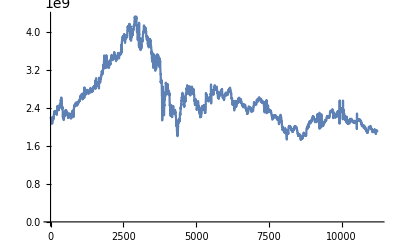

```mathematica
ListLinePlot[twapsWethUsdc120dFiltered, PlotRange->All]
```

```mathematica
FromUnixTime[tblWethUsdc120d[[40]][[2]]]
```

Mon 19 Apr 2021 17:14:44GMT-4.

```mathematica
FromUnixTime[tblWethUsdc120d[[Length[twapsWethUsdc120dFiltered]]][[2]]]
```

Fri 16 Jul 2021 10:27:07GMT-4.

```mathematica
(* Calculate the rs ... *)
```

```mathematica
rsWethUsdc120dFiltered = Differences[Log[twapsWethUsdc120dFiltered]]
```

{-0.00120673,0.000176452,-0.0000603568,-0.000373722,-0.000389599,0.000559858,-0.00092094,-0.00154871,-0.000905547,-0.000584311,11210,-0.000975245,-0.000888855,-0.00068242,-0.000128976,-0.00026784,-0.000921873,-0.00196508,-0.00162411,-0.00132945,-0.00102799}
 |  |  |  |

```mathematica
rsWethUsdc120dFiltered[[100]]
```

-0.00443888

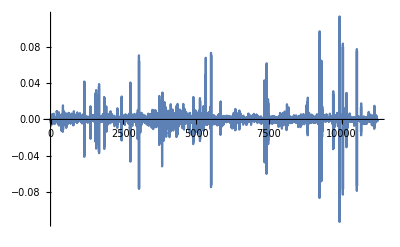

```mathematica
ListLinePlot[rsWethUsdc120dFiltered, PlotRange->All]
```

```mathematica
Length[rsWethUsdc120dFiltered]
```

11230

```mathematica
edistWethUsdc120dFiltered = EstimatedDistribution[rsWethUsdc120dFiltered, StableDistribution[1, aWU120d, bWU120d, locWU120d, scaleWU120d]]
```

StableDistribution[1,1.41834,-0.0286247,-6.93658×10^-6,0.00140585]

```mathematica
FromUnixTime[tblWethUsdc120d[[5000]][[2]]]
```

Fri 28 May 2021 06:16:07GMT-4.

```mathematica
FromUnixTime[tblWethUsdc120d[[Length[tblWethUsdc120d]]][[2]]]
```

Fri 16 Jul 2021 18:01:02GMT-4.

```mathematica
(* Seems a good place to estimate k values would be 1h candles (from note-7.nb) *)
```

```mathematica
(* Some concrete numbers below in terms of funding rate ... *)
```

```mathematica
(* What does e^{mu * T + sig * (T/a)^(1/a) * F^{-1}(1-alpha)} translate to for ETH/USDC fit? *)
```

```mathematica
(* And if d = f * e^{mu * T + sig * (T/a)^(1/a) * F^{-1}(1-alpha)}, what f value should we use across the board to get k max interest rates on order of 1-10% daily? *)
```

```mathematica
(* e.x. d = 1.0014649 for T=10m results in 10% per day funding rate *)
```

```mathematica
edistWethUsdc120dFiltered
```

StableDistribution[1,1.41834,-0.0286247,-6.93658×10^-6,0.00140585]

```mathematica
InverseCDF[edistWethUsdc120dFiltered, 0.99]
```

0.0127859

```mathematica
InverseCDF[edistWethUsdc120dFiltered, 0.95]
```

0.00460265

```mathematica
InverseCDF[edistWethUsdc120dFiltered, 0.90]
```

0.00300704

```mathematica
Exp[InverseCDF[edistWethUsdc120dFiltered, 0.95]]
```

1.00461

```mathematica
Exp[InverseCDF[edistWethUsdc120dFiltered, 0.99]]
```

1.01287

```mathematica
(* Produce 1 hour candles from 10min cron data to use in k analysis ... *)
```

```mathematica
twapsWethUsdc120dFiltered1HourCandle = Table[twapsWethUsdc120dFiltered[[i]], {i, 1, Length[twapsWethUsdc120dFiltered], 6}]
```

{2.20799×10^9,2.20513×10^9,2.18452×10^9,2.13229×10^9,2.11006×10^9,2.07922×10^9,2.09635×10^9,2.12707×10^9,2.12948×10^9,2.08876×10^9,2.092×10^9,2.14019×10^9,2.15282×10^9,2.18679×10^9,2.18398×10^9,2.19238×10^9,2.20923×10^9,2.16313×10^9,2.2252×10^9,2.2656×10^9,2.28598×10^9,2.31448×10^9,2.31787×10^9,2.33849×10^9,2.327×10^9,2.34079×10^9,2.30593×10^9,2.31917×10^9,2.31566×10^9,2.29969×10^9,2.30039×10^9,2.31432×10^9,2.2911×10^9,2.29267×10^9,2.29931×10^9,2.26585×10^9,2.28924×10^9,2.36951×10^9,2.38804×10^9,2.43288×10^9,2.44522×10^9,2.42349×10^9,2.41306×10^9,2.43004×10^9,2.39108×10^9,2.38836×10^9,2.35824×10^9,2.35909×10^9,2.43401×10^9,2.38868×10^9,2.40558×10^9,2.43149×10^9,2.45836×10^9,2.47252×10^9,2.45963×10^9,2.44538×10^9,2.48836×10^9,2.53708×10^9,2.57431×10^9,2.56804×10^9,2.58211×10^9,2.59943×10^9,2.60893×10^9,2.54473×10^9,2.5154×10^9,2.45851×10^9,2.39695×10^9,2.4136×10^9,2.41881×10^9,2.39325×10^9,2.28152×10^9,2.24012×10^9,2.25792×10^9,2.20518×10^9,2.19372×10^9,2.1814×10^9,2.17754×10^9,2.20198×10^9,2.27401×10^9,2.28949×10^9,2.24668×10^9,2.25694×10^9,2.28855×10^9,2.33238×10^9,2.30586×10^9,2.34455×10^9,2.35986×10^9,2.34445×10^9,2.31699×10^9,2.33811×10^9,2.31129×10^9,2.27699×10^9,2.27259×10^9,2.30824×10^9,2.31167×10^9,2.31729×10^9,2.28115×10^9,2.2841×10^9,2.27321×10^9,2.2328×10^9,2.19895×10^9,2.21535×10^9,2.22182×10^9,2.20086×10^9,2.24249×10^9,2.23852×10^9,2.26192×10^9,2.2762×10^9,2.27615×10^9,2.28902×10^9,2.2637×10^9,2.23579×10^9,2.2202×10^9,2.2419×10^9,2.23764×10^9,2.19271×10^9,2.19508×10^9,2.20039×10^9,2.18244×10^9,2.20087×10^9,2.22228×10^9,2.27257×10^9,2.27791×10^9,2.31112×10^9,2.31413×10^9,2.33998×10^9,2.34076×10^9,2.34044×10^9,2.31663×10^9,2.29939×10^9,2.27635×10^9,2.21107×10^9,2.2594×10^9,2.2981×10^9,2.40696×10^9,2.44476×10^9,2.44623×10^9,2.45812×10^9,2.45375×10^9,2.47045×10^9,2.46507×10^9,2.44595×10^9,2.44323×10^9,2.48714×10^9,2.51503×10^9,2.50391×10^9,2.4989×10^9,2.48799×10^9,2.48933×10^9,2.50791×10^9,2.50156×10^9,2.49079×10^9,2.46433×10^9,2.4924×10^9,2.51696×10^9,2.52264×10^9,2.51242×10^9,2.52143×10^9,2.50823×10^9,2.49901×10^9,2.52488×10^9,2.55421×10^9,2.55383×10^9,2.54832×10^9,2.55165×10^9,2.55059×10^9,2.57182×10^9,2.5636×10^9,2.56814×10^9,2.6356×10^9,2.65748×10^9,2.63922×10^9,2.63722×10^9,2.62427×10^9,2.63619×10^9,2.63813×10^9,2.62802×10^9,2.67884×10^9,2.69579×10^9,2.68116×10^9,2.63928×10^9,2.63913×10^9,2.6043×10^9,2.5975×10^9,2.61809×10^9,2.6001×10^9,2.62146×10^9,2.68377×10^9,2.71902×10^9,2.69857×10^9,2.70519×10^9,2.68906×10^9,2.71774×10^9,2.72826×10^9,2.83875×10^9,2.71326×10^9,2.73414×10^9,2.72313×10^9,2.73961×10^9,2.72686×10^9,2.71973×10^9,2.71625×10^9,2.68881×10^9,2.69883×10^9,2.72397×10^9,2.73126×10^9,2.71824×10^9,2.7641×10^9,2.76668×10^9,2.76721×10^9,2.78625×10^9,2.76346×10^9,2.77752×10^9,2.76555×10^9,2.73519×10^9,2.71615×10^9,2.72296×10^9,2.70927×10^9,2.73315×10^9,2.76143×10^9,2.75368×10^9,2.73823×10^9,2.74219×10^9,2.74109×10^9,2.75674×10^9,2.76461×10^9,2.78123×10^9,2.77746×10^9,2.78216×10^9,2.76798×10^9,2.76317×10^9,2.74392×10^9,2.74595×10^9,2.75331×10^9,2.7459×10^9,2.75239×10^9,2.76471×10^9,2.76529×10^9,2.77799×10^9,2.7649×10^9,2.75652×10^9,2.7536×10^9,2.77048×10^9,2.76768×10^9,2.82967×10^9,2.83731×10^9,2.84274×10^9,2.86233×10^9,2.85625×10^9,2.85615×10^9,2.83934×10^9,2.83687×10^9,2.84947×10^9,2.86716×10^9,2.86996×10^9,2.86603×10^9,2.85328×10^9,2.88817×10^9,2.92512×10^9,2.93337×10^9,2.92361×10^9,2.93804×10^9,2.93166×10^9,2.94373×10^9,2.93936×10^9,2.93709×10^9,2.95137×10^9,2.91281×10^9,2.91731×10^9,2.91803×10^9,2.89507×10^9,2.87316×10^9,2.88564×10^9,2.91581×10^9,2.9211×10^9,2.92583×10^9,2.9166×10^9,2.81586×10^9,2.93313×10^9,2.93473×10^9,2.94487×10^9,2.97281×10^9,2.96885×10^9,2.97396×10^9,2.94192×10^9,2.96718×10^9,2.99205×10^9,3.01749×10^9,3.03939×10^9,3.0537×10^9,3.08027×10^9,3.09069×10^9,3.13349×10^9,3.17874×10^9,3.16742×10^9,3.14946×10^9,3.16459×10^9,3.13545×10^9,3.11962×10^9,3.17054×10^9,3.17997×10^9,3.26847×10^9,3.30984×10^9,3.29632×10^9,3.28365×10^9,3.30197×10^9,3.38782×10^9,3.41029×10^9,3.31206×10^9,3.27985×10^9,3.24031×10^9,3.27686×10^9,3.35822×10^9,3.37754×10^9,3.35295×10^9,3.30488×10^9,3.35429×10^9,3.40725×10^9,3.45623×10^9,3.46868×10^9,3.4358×10^9,3.31593×10^9,3.25651×10^9,3.30959×10^9,3.36501×10^9,3.40186×10^9,3.38023×10^9,3.30652×10^9,3.29343×10^9,3.30126×10^9,3.36104×10^9,3.32631×10^9,3.29762×10^9,3.26674×10^9,3.25799×10^9,3.27656×10^9,3.35215×10^9,3.36157×10^9,3.37052×10^9,3.36096×10^9,3.37133×10^9,3.34794×10^9,3.33777×10^9,3.35683×10^9,3.42208×10^9,3.41222×10^9,3.45552×10^9,3.45413×10^9,3.44475×10^9,3.5187×10^9,3.50429×10^9,3.47011×10^9,3.48886×10^9,3.46939×10^9,3.47733×10^9,3.45088×10^9,3.41839×10^9,3.43857×10^9,3.44461×10^9,3.47585×10^9,3.49581×10^9,3.49845×10^9,3.48357×10^9,3.51713×10^9,3.57419×10^9,3.57542×10^9,3.506×10^9,3.45856×10^9,3.46529×10^9,3.51189×10^9,3.51816×10^9,3.50526×10^9,3.48685×10^9,3.4508×10^9,3.43042×10^9,3.39232×10^9,3.41145×10^9,3.44033×10^9,3.45358×10^9,3.43182×10^9,3.45631×10^9,3.45656×10^9,3.45006×10^9,3.49336×10^9,3.49927×10^9,3.50865×10^9,3.56177×10^9,3.55588×10^9,3.52548×10^9,3.51894×10^9,3.50502×10^9,3.48605×10^9,3.45079×10^9,3.48421×10^9,3.52755×10^9,3.54076×10^9,3.53249×10^9,3.56992×10^9,3.54756×10^9,3.52933×10^9,3.53244×10^9,3.56615×10^9,3.5612×10^9,3.54436×10^9,3.54691×10^9,3.58262×10^9,3.65586×10^9,3.58062×10^9,3.7727×10^9,3.82237×10^9,3.83128×10^9,3.8228×10^9,3.86521×10^9,3.90859×10^9,3.8787×10^9,3.8657×10^9,3.88178×10^9,3.89524×10^9,3.89336×10^9,3.90608×10^9,3.93227×10^9,3.95864×10^9,3.95068×10^9,3.91603×10^9,3.88966×10^9,3.89569×10^9,3.78543×10^9,3.80714×10^9,3.83344×10^9,3.89274×10^9,3.92455×10^9,3.9148×10^9,3.88842×10^9,3.88696×10^9,3.91573×10^9,3.90068×10^9,3.90845×10^9,3.90923×10^9,3.92922×10^9,3.97542×10^9,4.05106×10^9,4.10581×10^9,4.12089×10^9,4.12081×10^9,4.10294×10^9,4.12322×10^9,4.07891×10^9,4.05166×10^9,4.1261×10^9,4.12469×10^9,4.08194×10^9,4.17201×10^9,4.16758×10^9,4.13623×10^9,4.08348×10^9,3.88932×10^9,4.00082×10^9,3.97904×10^9,3.95799×10^9,3.88678×10^9,3.86068×10^9,3.83452×10^9,3.90141×10^9,3.89406×10^9,3.94848×10^9,3.93445×10^9,3.9596×10^9,4.0512×10^9,3.99749×10^9,3.95243×10^9,3.96281×10^9,4.00156×10^9,4.04201×10^9,4.0344×10^9,4.06711×10^9,4.06441×10^9,4.13384×10^9,4.11788×10^9,4.13899×10^9,4.17178×10^9,4.18279×10^9,4.2641×10^9,4.32243×10^9,4.32228×10^9,4.32988×10^9,4.30912×10^9,4.29344×10^9,4.28969×10^9,4.25303×10^9,4.27796×10^9,4.28761×10^9,4.33239×10^9,4.20803×10^9,4.14267×10^9,4.11796×10^9,4.00064×10^9,4.07428×10^9,4.10879×10^9,4.101×10^9,3.9062×10^9,3.93195×10^9,3.99148×10^9,3.96865×10^9,3.94099×10^9,3.95475×10^9,4.00017×10^9,3.70516×10^9,3.8932×10^9,3.75988×10^9,3.67637×10^9,3.76666×10^9,3.81998×10^9,3.87894×10^9,3.79171×10^9,3.74747×10^9,3.66856×10^9,3.63904×10^9,3.6837×10^9,3.74649×10^9,3.73536×10^9,3.66591×10^9,3.79488×10^9,3.86848×10^9,3.8135×10^9,3.80587×10^9,3.79661×10^9,3.84017×10^9,3.84185×10^9,3.88821×10^9,3.95715×10^9,3.96538×10^9,4.01401×10^9,3.98888×10^9,4.03532×10^9,4.1101×10^9,4.13953×10^9,4.12435×10^9,4.08958×10^9,4.06048×10^9,4.00694×10^9,4.04564×10^9,4.08735×10^9,4.08315×10^9,4.08834×10^9,4.08866×10^9,4.04452×10^9,4.02976×10^9,4.01826×10^9,3.94742×10^9,3.91848×10^9,3.90952×10^9,3.84696×10^9,3.88051×10^9,3.91314×10^9,3.88868×10^9,3.89863×10^9,3.8112×10^9,3.75167×10^9,3.75383×10^9,3.72038×10^9,3.80199×10^9,3.80815×10^9,3.72712×10^9,3.74674×10^9,3.82092×10^9,3.82716×10^9,3.80786×10^9,3.81177×10^9,3.82047×10^9,3.85114×10^9,3.81438×10^9,3.81295×10^9,3.83784×10^9,3.81755×10^9,3.74056×10^9,3.71543×10^9,3.67614×10^9,3.64593×10^9,3.54398×10^9,3.59328×10^9,3.47452×10^9,3.41747×10^9,3.41376×10^9,3.54028×10^9,3.55881×10^9,3.51549×10^9,3.41854×10^9,3.38051×10^9,3.2503×10^9,3.29619×10^9,3.37912×10^9,3.46301×10^9,3.53029×10^9,3.51009×10^9,3.47397×10^9,3.51707×10^9,3.46885×10^9,3.41067×10^9,3.34839×10^9,3.26675×10^9,3.20058×10^9,3.34981×10^9,3.38169×10^9,3.41716×10^9,3.28975×10^9,3.24783×10^9,3.33485×10^9,3.38295×10^9,3.38069×10^9,3.39906×10^9,3.49311×10^9,3.53709×10^9,3.49063×10^9,3.50745×10^9,3.46524×10^9,3.48955×10^9,3.51933×10^9,3.4446×10^9,3.36171×10^9,3.32665×10^9,3.36827×10^9,3.42075×10^9,3.36602×10^9,3.37949×10^9,3.43181×10^9,3.41218×10^9,3.37345×10^9,3.40067×10^9,3.30036×10^9,3.1874×10^9,3.11368×10^9,2.98709×10^9,2.93567×10^9,2.97019×10^9,2.96169×10^9,2.97333×10^9,2.94925×10^9,2.81334×10^9,2.67634×10^9,2.15935×10^9,2.36736×10^9,2.6269×10^9,2.8034×10^9,2.75192×10^9,2.61962×10^9,2.63998×10^9,2.52109×10^9,2.65692×10^9,2.55795×10^9,2.32305×10^9,2.33289×10^9,2.45114×10^9,2.51589×10^9,2.6125×10^9,2.63982×10^9,2.73084×10^9,2.67406×10^9,2.66519×10^9,2.69874×10^9,2.81168×10^9,2.93724×10^9,2.92148×10^9,2.84109×10^9,2.69956×10^9,2.76519×10^9,2.79801×10^9,2.79091×10^9,2.81874×10^9,2.78922×10^9,2.80891×10^9,2.91099×10^9,2.86832×10^9,2.80395×10^9,2.77003×10^9,2.7476×10^9,2.74057×10^9,2.68311×10^9,2.73787×10^9,2.74915×10^9,2.68519×10^9,2.67897×10^9,2.70065×10^9,2.51586×10^9,2.45171×10^9,2.46356×10^9,2.44123×10^9,2.38947×10^9,2.28722×10^9,2.31838×10^9,2.39971×10^9,2.41079×10^9,2.44199×10^9,2.45616×10^9,2.36796×10^9,2.28611×10^9,2.21496×10^9,2.21985×10^9,2.25847×10^9,2.33893×10^9,2.35182×10^9,2.43979×10^9,2.42501×10^9,2.43602×10^9,2.38553×10^9,2.34224×10^9,2.36377×10^9,2.29556×10^9,2.29343×10^9,2.30329×10^9,2.3574×10^9,2.35043×10^9,2.34296×10^9,2.30606×10^9,2.36381×10^9,2.31402×10^9,2.31487×10^9,2.28093×10^9,2.23564×10^9,2.20298×10^9,2.1397×10^9,2.03948×10^9,2.07315×10^9,2.12854×10^9,2.05156×10^9,1.91851×10^9,1.95859×10^9,1.92022×10^9,1.82923×10^9,1.90531×10^9,1.91441×10^9,2.00052×10^9,2.09834×10^9,2.11359×10^9,2.08928×10^9,2.15855×10^9,2.12077×10^9,2.13307×10^9,2.16501×10^9,2.12698×10^9,2.12448×10^9,2.20476×10^9,2.28613×10^9,2.27467×10^9,2.25365×10^9,2.32941×10^9,2.41567×10^9,2.41375×10^9,2.46255×10^9,2.46446×10^9,2.49943×10^9,2.56853×10^9,2.60418×10^9,2.62629×10^9,2.6007×10^9,2.59947×10^9,2.70917×10^9,2.67928×10^9,2.60257×10^9,2.58246×10^9,2.58118×10^9,2.62988×10^9,2.65936×10^9,2.63664×10^9,2.57462×10^9,2.47356×10^9,2.4472×10^9,2.44466×10^9,2.55324×10^9,2.6091×10^9,2.58593×10^9,2.57203×10^9,2.59658×10^9,2.55355×10^9,2.55157×10^9,2.62326×10^9,2.70456×10^9,2.6901×10^9,2.71271×10^9,2.80243×10^9,2.82337×10^9,2.80471×10^9,2.81905×10^9,2.87779×10^9,2.8659×10^9,2.85532×10^9,2.80625×10^9,2.83752×10^9,2.80103×10^9,2.75038×10^9,2.73624×10^9,2.72826×10^9,2.71526×10^9,2.73084×10^9,2.74952×10^9,2.79831×10^9,2.82472×10^9,2.8591×10^9,2.80976×10^9,2.72499×10^9,2.68942×10^9,2.67599×10^9,2.68711×10^9,2.72732×10^9,2.74377×10^9,2.75202×10^9,2.78968×10^9,2.79417×10^9,2.81961×10^9,2.81068×10^9,2.84947×10^9,2.82639×10^9,2.78639×10^9,2.78214×10^9,2.78518×10^9,2.75375×10^9,2.73266×10^9,2.77527×10^9,2.75624×10^9,2.72327×10^9,2.69812×10^9,2.72264×10^9,2.71735×10^9,2.67653×10^9,2.62059×10^9,2.55426×10^9,2.56129×10^9,2.48811×10^9,2.49588×10^9,2.48381×10^9,2.53097×10^9,2.59247×10^9,2.55763×10^9,2.54233×10^9,2.49725×10^9,2.49829×10^9,2.51674×10^9,2.47639×10^9,2.36618×10^9,2.38693×10^9,2.43233×10^9,2.5117×10^9,2.51506×10^9,2.52151×10^9,2.51232×10^9,2.54846×10^9,2.53907×10^9,2.49615×10^9,2.44633×10^9,2.429×10^9,2.422×10^9,2.4289×10^9,2.37344×10^9,2.38374×10^9,2.31907×10^9,2.346×10^9,2.27229×10^9,2.25483×10^9,2.23587×10^9,2.25227×10^9,2.26669×10^9,2.28777×10^9,2.21746×10^9,2.22336×10^9,2.2787×10^9,2.28894×10^9,2.32744×10^9,2.39486×10^9,2.43264×10^9,2.44064×10^9,2.42846×10^9,2.41287×10^9,2.42129×10^9,2.4069×10^9,2.38832×10^9,2.35911×10^9,2.38198×10^9,2.41598×10^9,2.44192×10^9,2.45334×10^9,2.44309×10^9,2.43316×10^9,2.40453×10^9,2.38925×10^9,2.34751×10^9,2.3045×10^9,2.30512×10^9,2.3022×10^9,2.32221×10^9,2.36074×10^9,2.58176×10^9,2.69345×10^9,2.63788×10^9,2.63788×10^9,2.65214×10^9,2.68763×10^9,2.65425×10^9,2.59494×10^9,2.57384×10^9,2.60018×10^9,2.61164×10^9,2.56346×10^9,2.6244×10^9,2.57192×10^9,2.56409×10^9,2.54594×10^9,2.56788×10^9,2.54766×10^9,2.57164×10^9,2.59317×10^9,2.60102×10^9,2.61326×10^9,2.56877×10^9,2.60571×10^9,2.62338×10^9,2.62887×10^9,2.63193×10^9,2.64567×10^9,2.69064×10^9,2.69869×10^9,2.69063×10^9,2.68315×10^9,2.70558×10^9,2.72211×10^9,2.7537×10^9,2.78665×10^9,2.76457×10^9,2.76474×10^9,2.76428×10^9,2.75045×10^9,2.72586×10^9,2.70339×10^9,2.71108×10^9,2.702×10^9,2.68777×10^9,2.70814×10^9,2.75585×10^9,2.8057×10^9,2.8356×10^9,2.82846×10^9,2.8477×10^9,2.88601×10^9,2.83304×10^9,2.82326×10^9,2.79364×10^9,2.79149×10^9,2.79408×10^9,2.83155×10^9,2.82645×10^9,2.7951×10^9,2.80006×10^9,2.82871×10^9,2.83574×10^9,2.85143×10^9,2.79018×10^9,2.72433×10^9,2.74829×10^9,2.74784×10^9,2.67608×10^9,2.63275×10^9,2.62653×10^9,2.62981×10^9,2.65079×10^9,2.63591×10^9,2.6007×10^9,2.65359×10^9,2.63505×10^9,2.65819×10^9,2.66823×10^9,2.69806×10^9,2.70081×10^9,2.68905×10^9,2.7213×10^9,2.72595×10^9,2.68776×10^9,2.74104×10^9,2.76586×10^9,2.76066×10^9,2.76729×10^9,2.77716×10^9,2.77033×10^9,2.78586×10^9,2.79361×10^9,2.79215×10^9,2.71228×10^9,2.65956×10^9,2.63983×10^9,2.62623×10^9,2.60797×10^9,2.64143×10^9,2.62719×10^9,2.62747×10^9,2.62485×10^9,2.62734×10^9,2.57013×10^9,2.58446×10^9,2.62131×10^9,2.64994×10^9,2.68378×10^9,2.67543×10^9,2.6817×10^9,2.68312×10^9,2.66487×10^9,2.69257×10^9,2.72531×10^9,2.72154×10^9,2.70823×10^9,2.70237×10^9,2.67172×10^9,2.69476×10^9,2.7227×10^9,2.71799×10^9,2.69153×10^9,2.685×10^9,2.68329×10^9,2.70694×10^9,2.6891×10^9,2.71029×10^9,2.75564×10^9,2.78674×10^9,2.79008×10^9,2.77828×10^9,2.7764×10^9,2.77746×10^9,2.75832×10^9,2.75931×10^9,2.7938×10^9,2.82688×10^9,2.81454×10^9,2.82294×10^9,2.77959×10^9,2.77829×10^9,2.76748×10^9,2.72537×10^9,2.69883×10^9,2.71989×10^9,2.64823×10^9,2.61717×10^9,2.61386×10^9,2.59071×10^9,2.60328×10^9,2.56237×10^9,2.47989×10^9,2.50604×10^9,2.48745×10^9,2.48588×10^9,2.52579×10^9,2.518×10^9,2.50364×10^9,2.50658×10^9,2.52012×10^9,2.47676×10^9,2.38443×10^9,2.37037×10^9,2.40551×10^9,2.42494×10^9,2.47183×10^9,2.50014×10^9,2.52815×10^9,2.49916×10^9,2.52309×10^9,2.47285×10^9,2.44919×10^9,2.44831×10^9,2.44405×10^9,2.46379×10^9,2.49834×10^9,2.52692×10^9,2.49402×10^9,2.49398×10^9,2.50451×10^9,2.54774×10^9,2.5386×10^9,2.52718×10^9,2.55263×10^9,2.59411×10^9,2.59312×10^9,2.5722×10^9,2.56383×10^9,2.57223×10^9,2.621×10^9,2.5748×10^9,2.58697×10^9,2.58242×10^9,2.57687×10^9,2.56923×10^9,2.54331×10^9,2.53427×10^9,2.54461×10^9,2.53271×10^9,2.53727×10^9,2.59084×10^9,2.56632×10^9,2.5499×10^9,2.53541×10^9,2.51913×10^9,2.49173×10^9,2.46765×10^9,2.4673×10^9,2.46221×10^9,2.44993×10^9,2.47741×10^9,2.49042×10^9,2.47243×10^9,2.42047×10^9,2.41968×10^9,2.46017×10^9,2.47198×10^9,2.47164×10^9,2.4363×10^9,2.44903×10^9,2.45647×10^9,2.4689×10^9,2.47141×10^9,2.45833×10^9,2.46981×10^9,2.45503×10^9,2.41865×10^9,2.38369×10^9,2.39855×10^9,2.40891×10^9,2.39932×10^9,2.35237×10^9,2.36311×10^9,2.34386×10^9,2.33974×10^9,2.2892×10^9,2.28625×10^9,2.29496×10^9,2.28863×10^9,2.29229×10^9,2.316×10^9,2.31452×10^9,2.32021×10^9,2.38545×10^9,2.40632×10^9,2.4379×10^9,2.41939×10^9,2.40946×10^9,2.39009×10^9,2.39183×10^9,2.41322×10^9,2.41925×10^9,2.41511×10^9,2.40498×10^9,2.38659×10^9,2.37984×10^9,2.38012×10^9,2.40643×10^9,2.3825×10^9,2.33556×10^9,2.33131×10^9,2.32081×10^9,2.33704×10^9,2.3432×10^9,2.35424×10^9,2.36876×10^9,2.36812×10^9,2.3621×10^9,2.35666×10^9,2.34085×10^9,2.36042×10^9,2.40002×10^9,2.43132×10^9,2.43456×10^9,2.48487×10^9,2.53103×10^9,2.5118×10^9,2.50272×10^9,2.50074×10^9,2.50303×10^9,2.49041×10^9,2.48077×10^9,2.49405×10^9,2.49807×10^9,2.49903×10^9,2.48209×10^9,2.47645×10^9,2.48929×10^9,2.48178×10^9,2.51605×10^9,2.56483×10^9,2.55813×10^9,2.58343×10^9,2.57265×10^9,2.556×10^9,2.53355×10^9,2.54689×10^9,2.56273×10^9,2.5649×10^9,2.59201×10^9,2.59752×10^9,2.58238×10^9,2.59209×10^9,2.61267×10^9,2.62044×10^9,2.62023×10^9,2.61314×10^9,2.58468×10^9,2.5865×10^9,2.58218×10^9,2.58794×10^9,2.59359×10^9,2.56016×10^9,2.54289×10^9,2.55399×10^9,2.58105×10^9,2.57857×10^9,2.52793×10^9,2.52737×10^9,2.54115×10^9,2.55497×10^9,2.52682×10^9,2.51529×10^9,2.52524×10^9,2.519×10^9,2.52753×10^9,2.52804×10^9,2.53589×10^9,2.53898×10^9,2.52605×10^9,2.51265×10^9,2.46614×10^9,2.44939×10^9,2.45691×10^9,2.43198×10^9,2.42762×10^9,2.40256×10^9,2.41042×10^9,2.42319×10^9,2.40385×10^9,2.40619×10^9,2.37018×10^9,2.3838×10^9,2.40298×10^9,2.42034×10^9,2.43219×10^9,2.42291×10^9,2.43031×10^9,2.45061×10^9,2.44121×10^9,2.4392×10^9,2.43837×10^9,2.40859×10^9,2.38315×10^9,2.39098×10^9,2.40467×10^9,2.3143×10^9,2.31908×10^9,2.34206×10^9,2.34155×10^9,2.34057×10^9,2.34173×10^9,2.36907×10^9,2.36636×10^9,2.33696×10^9,2.33461×10^9,2.34276×10^9,2.35613×10^9,2.34112×10^9,2.33401×10^9,2.3487×10^9,2.32989×10^9,2.31022×10^9,2.32244×10^9,2.289×10^9,2.27041×10^9,2.24882×10^9,2.22348×10^9,2.22957×10^9,2.19688×10^9,2.15795×10^9,2.18433×10^9,2.20334×10^9,2.20867×10^9,2.22131×10^9,2.24424×10^9,2.24788×10^9,2.21647×10^9,2.18767×10^9,2.20943×10^9,2.23837×10^9,2.23071×10^9,2.24349×10^9,2.24318×10^9,2.22888×10^9,2.23657×10^9,2.24555×10^9,2.23207×10^9,2.24877×10^9,2.24105×10^9,2.23722×10^9,2.20648×10^9,2.20945×10^9,2.21682×10^9,2.22236×10^9,2.18729×10^9,2.17645×10^9,2.16053×10^9,2.17999×10^9,2.17245×10^9,2.18765×10^9,2.20896×10^9,2.21032×10^9,2.20257×10^9,2.1968×10^9,2.17951×10^9,2.11701×10^9,2.08351×10^9,2.06409×10^9,2.08603×10^9,2.10111×10^9,2.1176×10^9,2.12632×10^9,2.13533×10^9,2.17697×10^9,2.24219×10^9,2.25775×10^9,2.25307×10^9,2.24413×10^9,2.22902×10^9,2.21159×10^9,2.18567×10^9,2.14525×10^9,2.1013×10^9,2.11309×10^9,2.01959×10^9,2.01738×10^9,2.00542×10^9,1.97741×10^9,1.93946×10^9,1.95532×10^9,1.97879×10^9,1.99989×10^9,1.97141×10^9,1.93346×10^9,1.93422×10^9,1.93646×10^9,1.94139×10^9,1.90045×10^9,1.88578×10^9,1.88782×10^9,1.93414×10^9,1.94882×10^9,1.96786×10^9,1.96598×10^9,1.94725×10^9,1.94286×10^9,1.93818×10^9,1.88158×10^9,1.86881×10^9,1.88938×10^9,1.84003×10^9,1.77392×10^9,1.75722×10^9,1.86773×10^9,1.90119×10^9,1.90558×10^9,1.92154×10^9,1.91232×10^9,1.9017×10^9,1.8817×10^9,1.86401×10^9,1.9301×10^9,1.99613×10^9,2.00821×10^9,2.00966×10^9,2.01228×10^9,2.0198×10^9,2.00925×10^9,1.98795×10^9,1.99395×10^9,2.00126×10^9,2.00207×10^9,2.01308×10^9,1.99268×10^9,1.98434×10^9,1.98614×10^9,1.96233×10^9,1.95016×10^9,1.93201×10^9,1.94099×10^9,1.94727×10^9,1.96307×10^9,1.94737×10^9,1.91134×10^9,1.89904×10^9,1.90495×10^9,1.91042×10^9,1.92311×10^9,1.9312×10^9,1.93136×10^9,1.94566×10^9,1.93889×10^9,1.96344×10^9,1.96996×10^9,1.96583×10^9,1.99017×10^9,1.99063×10^9,2.02226×10^9,2.02107×10^9,2.01498×10^9,2.00581×10^9,1.99754×10^9,1.98314×10^9,1.99599×10^9,1.98101×10^9,1.99995×10^9,1.9972×10^9,1.987×10^9,1.97119×10^9,1.96337×10^9,1.93851×10^9,1.93112×10^9,1.91373×10^9,1.87577×10^9,1.86221×10^9,1.8507×10^9,1.85596×10^9,1.82019×10^9,1.81559×10^9,1.81803×10^9,1.84157×10^9,1.85048×10^9,1.8543×10^9,1.8411×10^9,1.81562×10^9,1.82381×10^9,1.81441×10^9,1.82119×10^9,1.8378×10^9,1.83007×10^9,1.76562×10^9,1.73026×10^9,1.75722×10^9,1.7683×10^9,1.79735×10^9,1.79042×10^9,1.74571×10^9,1.77325×10^9,1.75189×10^9,1.76299×10^9,1.78696×10^9,1.78372×10^9,1.76361×10^9,1.76902×10^9,1.78698×10^9,1.82361×10^9,1.84322×10^9,1.87626×10^9,1.8849×10^9,1.87166×10^9,1.86045×10^9,1.86664×10^9,1.83946×10^9,1.8232×10^9,1.83581×10^9,1.85408×10^9,1.83965×10^9,1.83623×10^9,1.84144×10^9,1.8269×10^9,1.81643×10^9,1.8156×10^9,1.82396×10^9,1.82609×10^9,1.94104×10^9,1.96693×10^9,1.98443×10^9,1.96833×10^9,1.97487×10^9,1.97318×10^9,1.97432×10^9,2.01868×10^9,2.01748×10^9,2.05892×10^9,2.05052×10^9,1.99984×10^9,1.99921×10^9,2.01164×10^9,2.01745×10^9,2.07186×10^9,2.11057×10^9,2.0951×10^9,2.08704×10^9,2.12203×10^9,2.12913×10^9,2.10716×10^9,2.08046×10^9,2.10566×10^9,2.12367×10^9,2.10785×10^9,2.10564×10^9,2.1202×10^9,2.11002×10^9,2.15734×10^9,2.13095×10^9,2.14671×10^9,2.15845×10^9,2.18068×10^9,2.17741×10^9,2.20963×10^9,2.22374×10^9,2.21686×10^9,2.22613×10^9,2.22795×10^9,2.2187×10^9,2.22029×10^9,2.19923×10^9,2.18074×10^9,2.16655×10^9,2.17271×10^9,2.16103×10^9,2.15493×10^9,2.12823×10^9,2.10606×10^9,2.13541×10^9,2.1508×10^9,2.14254×10^9,2.12244×10^9,2.13745×10^9,2.15469×10^9,2.13319×10^9,2.13479×10^9,2.10415×10^9,2.11617×10^9,2.15538×10^9,2.20813×10^9,2.26563×10^9,2.26156×10^9,2.25397×10^9,2.26684×10^9,2.24719×10^9,2.24975×10^9,2.2051×10^9,2.19463×10^9,2.20333×10^9,2.20562×10^9,2.15268×10^9,2.12573×10^9,2.11065×10^9,2.11676×10^9,2.1285×10^9,2.13446×10^9,2.10272×10^9,2.1228×10^9,2.09532×10^9,2.10106×10^9,2.11415×10^9,2.10457×10^9,2.11884×10^9,2.13018×10^9,2.11512×10^9,2.12832×10^9,2.10182×10^9,2.09413×10^9,2.05011×10^9,2.04989×10^9,2.03196×10^9,2.03766×10^9,2.0665×10^9,2.04419×10^9,2.03057×10^9,2.03981×10^9,2.05044×10^9,2.06752×10^9,2.1116×10^9,2.11143×10^9,2.11251×10^9,2.09537×10^9,2.09519×10^9,2.09173×10^9,2.10638×10^9,2.14228×10^9,2.14991×10^9,2.14093×10^9,2.14729×10^9,2.12782×10^9,2.13432×10^9,2.14579×10^9,2.14802×10^9,2.19336×10^9,2.20628×10^9,2.22002×10^9,2.21093×10^9,2.22178×10^9,2.22613×10^9,2.23144×10^9,2.22616×10^9,2.22192×10^9,2.22321×10^9,2.22302×10^9,2.2214×10^9,2.21202×10^9,2.1992×10^9,2.22211×10^9,2.2044×10^9,2.20393×10^9,2.21325×10^9,2.22111×10^9,2.26505×10^9,2.30985×10^9,2.33705×10^9,2.32491×10^9,2.31877×10^9,2.3313×10^9,2.33097×10^9,2.31535×10^9,2.31771×10^9,2.32272×10^9,2.35985×10^9,2.3586×10^9,2.35682×10^9,2.35583×10^9,2.35238×10^9,2.37853×10^9,2.32762×10^9,2.31623×10^9,2.29846×10^9,2.26567×10^9,2.25954×10^9,2.26814×10^9,2.26511×10^9,2.27939×10^9,2.271×10^9,2.27915×10^9,2.29785×10^9,2.23062×10^9,2.21377×10^9,2.22673×10^9,2.2194×10^9,2.21363×10^9,2.20549×10^9,2.22772×10^9,2.24184×10^9,2.22107×10^9,2.23782×10^9,2.23756×10^9,2.21639×10^9,2.23797×10^9,2.22462×10^9,2.23451×10^9,2.29788×10^9,2.32161×10^9,2.32518×10^9,2.33205×10^9,2.32297×10^9,2.2716×10^9,2.2684×10^9,2.31215×10^9,2.31829×10^9,2.29941×10^9,2.30297×10^9,2.2976×10^9,2.31846×10^9,2.31679×10^9,2.31953×10^9,2.29428×10^9,2.30513×10^9,2.31927×10^9,2.31391×10^9,2.31124×10^9,2.32723×10^9,2.37509×10^9,2.38975×10^9,2.38589×10^9,2.3884×10^9,2.38076×10^9,2.37567×10^9,2.38854×10^9,2.38524×10^9,2.38241×10^9,2.37219×10^9,2.34162×10^9,2.35184×10^9,2.3593×10^9,2.36958×10^9,2.3659×10^9,2.34836×10^9,2.32817×10^9,2.31835×10^9,2.28217×10^9,2.2836×10^9,2.26621×10^9,2.24198×10^9,2.23796×10^9,2.22623×10^9,2.20371×10^9,2.19927×10^9,2.17715×10^9,2.16477×10^9,2.15285×10^9,2.1633×10^9,2.14024×10^9,2.1563×10^9,2.10012×10^9,2.16158×10^9,2.15021×10^9,2.15251×10^9,2.1505×10^9,2.12311×10^9,2.10265×10^9,2.11317×10^9,2.06893×10^9,2.07766×10^9,2.11341×10^9,2.13449×10^9,2.14906×10^9,2.1266×10^9,2.11276×10^9,2.0979×10^9,2.10405×10^9,2.08513×10^9,2.07922×10^9,2.13871×10^9,2.16367×10^9,2.17311×10^9,2.16628×10^9,2.14416×10^9,2.13372×10^9,2.13146×10^9,2.13399×10^9,2.15517×10^9,2.1571×10^9,2.17369×10^9,2.16079×10^9,2.14125×10^9,2.13323×10^9,2.11946×10^9,2.11621×10^9,2.12099×10^9,2.12113×10^9,2.12622×10^9,2.11089×10^9,2.10706×10^9,2.11148×10^9,2.10338×10^9,2.1067×10^9,2.12519×10^9,2.11656×10^9,2.08618×10^9,2.10009×10^9,2.09254×10^9,2.10354×10^9,2.11133×10^9,2.12031×10^9,2.11356×10^9,2.11713×10^9,2.09974×10^9,2.08645×10^9,2.09233×10^9,2.10013×10^9,2.09517×10^9,2.1127×10^9,2.12254×10^9,2.11914×10^9,2.12601×10^9,2.12315×10^9,2.13288×10^9,2.14203×10^9,2.14588×10^9,2.14724×10^9,2.14256×10^9,2.14115×10^9,2.13629×10^9,2.1651×10^9,2.14916×10^9,2.13697×10^9,2.13269×10^9,2.14047×10^9,2.15821×10^9,2.15754×10^9,2.14775×10^9,2.15233×10^9,2.1523×10^9,2.14491×10^9,2.12368×10^9,2.10856×10^9,2.10323×10^9,2.10263×10^9,2.09837×10^9,2.08547×10^9,2.04975×10^9,2.02882×10^9,2.02875×10^9,2.02287×10^9,2.02945×10^9,2.03623×10^9,2.03516×10^9,2.0301×10^9,2.02635×10^9,2.02994×10^9,2.03399×10^9,2.01057×10^9,1.98978×10^9,2.02055×10^9,2.02615×10^9,2.02507×10^9,2.02548×10^9,2.00475×10^9,1.97509×10^9,1.97457×10^9,1.97758×10^9,1.99659×10^9,1.99147×10^9,1.98128×10^9,1.93691×10^9,1.93827×10^9,1.94325×10^9,1.93754×10^9,1.93962×10^9,1.90447×10^9,1.90876×10^9,1.90337×10^9,1.8851×10^9,1.88794×10^9,1.87965×10^9,1.88867×10^9,1.89697×10^9,1.93932×10^9,1.94582×10^9,1.94654×10^9,1.95864×10^9,2.00414×10^9,2.00346×10^9,1.99469×10^9,2.00047×10^9,1.9954×10^9,1.98283×10^9,1.98811×10^9,1.99745×10^9,1.99518×10^9,1.98823×10^9,2.02106×10^9,1.99581×10^9,1.98032×10^9,1.96909×10^9,1.9649×10^9,1.95366×10^9,1.95685×10^9,1.96335×10^9,1.94612×10^9,1.91377×10^9,1.90131×10^9,1.91019×10^9,1.91855×10^9,1.92127×10^9,1.89475×10^9,1.89946×10^9,1.91619×10^9,1.92159×10^9,1.92689×10^9,1.9239×10^9,1.91523×10^9,1.90887×10^9,1.91085×10^9,1.94656×10^9,1.9513×10^9,1.94223×10^9,1.92207×10^9,1.90938×10^9,1.88993×10^9,1.86828×10^9,1.86395×10^9,1.86055×10^9,1.8826×10^9,1.90277×10^9,1.91095×10^9,1.927×10^9,1.92763×10^9,1.92255×10^9,1.9171×10^9,1.90971×10^9}

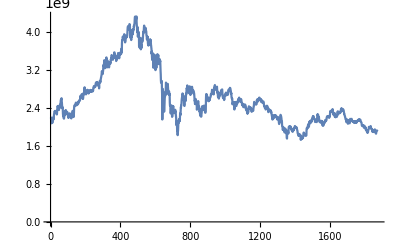

```mathematica
ListLinePlot[twapsWethUsdc120dFiltered1HourCandle]
```

```mathematica
rsWethUsdc120dFiltered1HourCandle = Differences[Log[twapsWethUsdc120dFiltered1HourCandle]]
```

{-0.0012941,-0.00939344,-0.0241963,-0.0104817,-0.0147229,0.00820584,0.014547,0.00112845,-0.0193036,0.0015467,0.0227744,0.00588498,0.0156569,-0.00128477,0.00383628,0.00765843,-0.0210875,0.0282886,0.0179942,0.00895628,0.0123902,0.00146154,0.00885738,-0.00492522,0.00591001,-0.0150075,0.00572474,-0.00151273,-0.00691957,0.000305489,0.00603401,-0.0100807,0.000682628,0.00289066,-0.0146574,0.0102704,0.0344637,0.00778817,0.0186024,0.00506249,-0.00892867,-0.00431243,0.00701086,-0.0161606,-0.00113936,-0.012692,0.000360494,0.0312663,-0.0188007,0.00704985,0.010712,0.0109927,0.00574422,-0.00522957,-0.00581162,0.0174255,0.0193901,0.0145689,-0.00244056,0.00546382,0.00668475,0.00364873,-0.0249162,-0.011591,-0.0228768,-0.0253583,0.00692255,0.00215623,-0.0106241,-0.0478116,-0.0183125,0.00791559,-0.0236331,-0.00521017,-0.00563152,-0.00177441,0.0111625,0.0321856,0.00678772,-0.0188758,0.00455526,0.0139082,0.0189708,-0.0114339,0.0166378,0.00651145,-0.00655183,-0.0117856,0.00907496,-0.0115368,-0.0149498,-0.00193373,0.0155644,0.0014861,0.00242527,-0.0157198,0.00129305,-0.00477816,-0.017937,-0.0152772,0.00743036,0.00291753,-0.00947762,0.0187403,-0.00177333,0.0103974,0.00629432,-0.0000214817,0.00563643,-0.0111222,-0.0124043,-0.00699624,0.00972473,-0.00190175,-0.0202832,0.00107855,0.00241894,-0.00819129,0.00840919,0.00967682,0.022379,0.00234826,0.0144718,0.0013018,0.0111105,0.000332482,-0.000134127,-0.0102255,-0.00747374,-0.0100704,-0.0290967,0.0216257,0.0169805,0.0462855,0.0155823,0.00060125,0.00484828,-0.00178179,0.00678203,-0.00217996,-0.00778384,-0.00111525,0.0178142,0.0111511,-0.00443252,-0.00200192,-0.00437384,0.000538142,0.00743398,-0.0025352,-0.00431194,-0.0106806,0.0113255,0.00980401,0.00225378,-0.0040591,0.00357938,-0.00524702,-0.00368089,0.0102967,0.0115506,-0.000148314,-0.00216172,0.00130508,-0.000413909,0.00828751,-0.0031985,0.00176965,0.0259262,0.00826952,-0.00689629,-0.000758883,-0.0049228,0.00453319,0.000734732,-0.00383704,0.0191525,0.00630641,-0.00544079,-0.0157458,-0.0000538651,-0.013288,-0.00261155,0.00789323,-0.00689467,0.00818365,0.0234902,0.0130463,-0.00754792,0.00245135,-0.00598091,0.0106099,0.00386107,0.0396993,-0.0452123,0.00766826,-0.00403656,0.00603463,-0.00466538,-0.00261885,-0.00127849,-0.0101564,0.00372127,0.00926992,0.00267257,-0.00477485,0.0167269,0.000933011,0.000192249,0.00685637,-0.00820991,0.00507312,-0.00432025,-0.0110354,-0.00698569,0.00250417,-0.00504121,0.00877336,0.0102957,-0.00281021,-0.00562736,0.0014454,-0.000400875,0.00569195,0.0028523,0.00599179,-0.00135385,0.001688,-0.00510824,-0.00174067,-0.00699027,0.000740825,0.00267789,-0.002698,0.00236155,0.00446606,0.000211853,0.00457926,-0.00472001,-0.00303777,-0.00106019,0.00611192,-0.00101119,0.0221515,0.00269457,0.00191348,0.00686818,-0.00212883,-0.0000333065,-0.00590221,-0.000872327,0.00443358,0.00618739,0.000978685,-0.00137111,-0.0044582,0.0121537,0.012713,0.00281359,-0.00333111,0.00492416,-0.00217514,0.00410975,-0.00148692,-0.000771305,0.00484947,-0.013151,0.00154328,0.000245555,-0.00789836,-0.00759518,0.00433302,0.0104016,0.00181102,0.00161976,-0.00315996,-0.0351516,0.040803,0.000546262,0.00344737,0.0094448,-0.00133529,0.00172134,-0.010834,0.00855037,0.00834883,0.00846601,0.00723202,0.00469582,0.00866432,0.00337486,0.0137537,0.0143363,-0.00356706,-0.00568652,0.00479291,-0.00924879,-0.00506178,0.0161896,0.00296944,0.0274497,0.0125781,-0.00409099,-0.00385356,0.00556396,0.0256687,0.00661141,-0.0292281,-0.0097714,-0.0121292,0.0112151,0.0245253,0.00573675,-0.00730707,-0.0144401,0.0148419,0.0156641,0.0142715,0.0035959,-0.00952215,-0.0355128,-0.018082,0.0161683,0.0166066,0.0108901,-0.00637733,-0.0220459,-0.00396726,0.00237482,0.017944,-0.0103872,-0.00866101,-0.00940875,-0.0026819,0.00568391,0.0228077,0.00280706,0.00265709,-0.00284089,0.00308071,-0.00696032,-0.00304267,0.00569525,0.0192498,-0.00288628,0.0126126,-0.00040282,-0.00271909,0.0212392,-0.00410335,-0.0098011,0.00538715,-0.00559571,0.00228718,-0.00763678,-0.00945856,0.00588384,0.00175553,0.00902914,0.0057251,0.000756119,-0.00426355,0.00958883,0.0160935,0.000343066,-0.0196071,-0.0136214,0.00194127,0.0133585,0.00178386,-0.00367229,-0.00526729,-0.0103905,-0.00592555,-0.0111679,0.00562247,0.00843029,0.00384391,-0.00631954,0.00711197,0.0000715682,-0.0018841,0.0124739,0.00168979,0.00267713,0.0150261,-0.00165389,-0.00858756,-0.00185717,-0.00396376,-0.00542598,-0.0101666,0.00963832,0.0123639,0.0037379,-0.00233891,0.0105406,-0.00628502,-0.00515027,0.000879561,0.00949945,-0.00138879,-0.00474051,0.000717644,0.0100192,0.020237,-0.0207963,0.052254,0.0130797,0.00232995,-0.0022154,0.0110306,0.0111614,-0.00767684,-0.00335574,0.00415127,0.00346162,-0.000483502,0.00326224,0.00668189,0.00668463,-0.00201467,-0.00880873,-0.00675781,0.00155063,-0.028712,0.00572009,0.00688331,0.0153514,0.00813714,-0.00248631,-0.006763,-0.000375609,0.00737534,-0.00385056,0.0019901,0.000198811,0.00510032,0.0116912,0.0188459,0.0134263,0.00366521,-0.0000202228,-0.00434395,0.00492858,-0.0108023,-0.00670333,0.018204,-0.000340032,-0.0104199,0.0218255,-0.0010619,-0.00754958,-0.012836,-0.0487143,0.028263,-0.00545802,-0.00530323,-0.018157,-0.00673611,-0.00679897,0.017294,-0.00188778,0.013879,-0.00355901,0.00637078,0.022872,-0.0133469,-0.0113365,0.00262367,0.00972989,0.0100581,-0.0018835,0.00807372,-0.000664149,0.0169381,-0.00386746,0.00511166,0.00789178,0.0026353,0.0192524,0.0135869,-0.0000334813,0.00175676,-0.00480754,-0.00364428,-0.00087381,-0.00858292,0.00584471,0.00225291,0.0103889,-0.0291231,-0.0156554,-0.00598179,-0.0289033,0.0182389,0.00843401,-0.00189759,-0.0486656,0.00656987,0.0150269,-0.00573566,-0.00699279,0.00348541,0.0114188,-0.0766094,0.0495032,-0.034843,-0.0224625,0.024264,0.0140562,0.0153153,-0.0227438,-0.0117354,-0.0212833,-0.00807792,0.0121961,0.016902,-0.0029743,-0.0187685,0.0345767,0.0192089,-0.0143146,-0.00200294,-0.00243474,0.0114072,0.000437347,0.0119957,0.0175754,0.00207719,0.0121896,-0.00628157,0.0115755,0.0183623,0.0071341,-0.00367281,-0.00846574,-0.00714214,-0.0132724,0.00961144,0.0102557,-0.00102612,0.00126949,0.0000786298,-0.0108557,-0.00365595,-0.00285802,-0.0177863,-0.00735803,-0.00228951,-0.0161318,0.0086849,0.00837138,-0.00626809,0.00255444,-0.0226809,-0.0157427,0.000574938,-0.0089521,0.0216996,0.00161998,-0.0215092,0.00525226,0.0196051,0.00162947,-0.00505536,0.00102626,0.00228188,0.00799437,-0.00959126,-0.000373717,0.00650619,-0.00530254,-0.0203736,-0.00673919,-0.0106307,-0.00825197,-0.0283604,0.0138139,-0.0336105,-0.0165539,-0.00108657,0.0363906,0.00522162,-0.012247,-0.0279668,-0.011188,-0.0392792,0.0140206,0.0248475,0.0245239,0.0192418,-0.00573792,-0.0103429,0.0123291,-0.0138041,-0.0169138,-0.0184294,-0.024684,-0.0204641,0.0455715,0.00947227,0.0104339,-0.0379973,-0.0128265,0.0264401,0.0143223,-0.000668989,0.00541914,0.0272934,0.0125127,-0.0132218,0.00480567,-0.0121086,0.00699344,0.00849575,-0.0214613,-0.0243592,-0.0104821,0.0124331,0.0154605,-0.0161291,0.00399398,0.0153613,-0.00573467,-0.0114158,0.00803497,-0.0299383,-0.0348267,-0.0234018,-0.0415037,-0.0173636,0.011688,-0.00286386,0.00392249,-0.00813305,-0.0471791,-0.0499205,-0.214646,0.0919721,0.104027,0.0650292,-0.0185358,-0.0492683,0.00774173,-0.0460781,0.0524762,-0.0379616,-0.0963281,0.00422759,0.0494469,0.0260708,0.0376831,0.0104027,0.0338998,-0.021013,-0.00332139,0.01251,0.040997,0.0436868,-0.0053785,-0.0279027,-0.0510988,0.0240177,0.0118012,-0.00254107,0.00992314,-0.0105293,0.00703635,0.035696,-0.0147688,-0.0226959,-0.01217,-0.00813089,-0.00256247,-0.0211896,0.0202049,0.00410991,-0.0235389,-0.00232114,0.00806105,-0.0708791,-0.0258258,0.0048203,-0.00910545,-0.0214291,-0.0437344,0.0135306,0.0344801,0.00460629,0.0128563,0.0057863,-0.0365698,-0.0351768,-0.0316194,0.00220857,0.0172454,0.0350072,0.00549788,0.0367225,-0.00607989,0.00453372,-0.0209481,-0.0183107,0.00915097,-0.0292831,-0.000930007,0.00429248,0.0232195,-0.00296,-0.00318207,-0.0158749,0.0247332,-0.021289,0.000367848,-0.0147724,-0.020053,-0.0147157,-0.0291446,-0.0479736,0.0163756,0.0263655,-0.0368352,-0.06705,0.0206743,-0.0197836,-0.0485451,0.0407481,0.00476796,0.0439972,0.0477376,0.00724105,-0.0115687,0.0326188,-0.0176598,0.00578556,0.0148619,-0.0177211,-0.0011764,0.0370896,0.036244,-0.00502727,-0.00928528,0.0330669,0.03636,-0.000794619,0.0200143,0.000775624,0.0140905,0.0272715,0.0137846,0.00845554,-0.00979266,-0.00047401,0.0413373,-0.0110942,-0.0290495,-0.0077595,-0.000493834,0.0186925,0.011148,-0.00858051,-0.0238053,-0.0400413,-0.0107169,-0.0010372,0.0434581,0.0216406,-0.00891953,-0.00538814,0.00949722,-0.0167082,-0.000775799,0.0277059,0.0305213,-0.00536035,0.00837233,0.0325365,0.00744402,-0.00663069,0.00509895,0.0206239,-0.00414016,-0.00369765,-0.0173349,0.0110792,-0.0129434,-0.0182479,-0.00515184,-0.0029229,-0.0047764,0.00572359,0.00681618,0.0175886,0.00939277,0.0120975,-0.0174053,-0.0306361,-0.0131389,-0.00500391,0.00414471,0.0148534,0.0060136,0.00300095,0.013594,0.00160629,0.00906468,-0.00317154,0.0137047,-0.00813121,-0.0142553,-0.00152433,0.00109081,-0.0113489,-0.00768726,0.0154724,-0.00688117,-0.0120338,-0.00927645,0.00904654,-0.00194751,-0.0151355,-0.0211195,-0.0256399,0.00274905,-0.0289856,0.00311602,-0.00484641,0.0188107,0.0240086,-0.01353,-0.00600392,-0.0178883,0.00041605,0.00735817,-0.0161636,-0.0455257,0.00873186,0.0188407,0.0321121,0.00133565,0.00256067,-0.00364937,0.0142829,-0.0036941,-0.0170464,-0.0201625,-0.00710644,-0.00288611,0.00284228,-0.0230984,0.00433128,-0.0275039,0.0115466,-0.0319235,-0.00771588,-0.00844404,0.00730837,0.00638166,0.00925695,-0.0312138,0.0026566,0.0245846,0.0044872,0.0166774,0.0285583,0.0156512,0.00328341,-0.00500426,-0.00644106,0.00348683,-0.00596326,-0.00774951,-0.0123055,0.00964994,0.0141724,0.0106783,0.00466503,-0.00418728,-0.00407016,-0.0118364,-0.00637561,-0.0176246,-0.0184907,0.000268613,-0.00127051,0.00865545,0.0164549,0.089497,0.0423522,-0.0208488,2.12254×10^-6,0.0053921,0.0132907,-0.0124978,-0.0225969,-0.00816368,0.0101791,0.00440036,-0.018623,0.0234938,-0.020197,-0.00305135,-0.00710412,0.00858124,-0.00790235,0.00936683,0.00833752,0.00302318,0.0046938,-0.0171702,0.0142753,0.00676129,0.00208907,0.00116304,0.0052074,0.016854,0.00298927,-0.00299108,-0.00278577,0.00832414,0.00609375,0.0115385,0.011892,-0.00795538,0.0000639027,-0.000167785,-0.0050155,-0.00898109,-0.00827721,0.00284233,-0.0033578,-0.00527723,0.00754765,0.017464,0.0179267,0.0106031,-0.00252356,0.00677932,0.0133633,-0.0185224,-0.00346057,-0.010544,-0.000770574,0.00092748,0.013321,-0.00180188,-0.0111563,0.00177417,0.0101783,0.00248479,0.00551513,-0.0217116,-0.0238835,0.0087551,-0.000164684,-0.0264604,-0.0163268,-0.0023619,0.00124636,0.00794775,-0.00562918,-0.0134513,0.0201362,-0.00701217,0.0087424,0.00377169,0.0111149,0.00102107,-0.00436573,0.0119223,0.00170911,-0.0141093,0.0196286,0.00901403,-0.00188142,0.0023976,0.00356037,-0.00246373,0.0055925,0.00277649,-0.000521804,-0.029022,-0.0196281,-0.0074488,-0.00516444,-0.00697616,0.0127463,-0.00540212,0.000105092,-0.000996741,0.000947258,-0.0220139,0.00555942,0.0141572,0.0108638,0.012686,-0.00311328,0.00234005,0.000526961,-0.00682497,0.0103438,0.0120844,-0.0013824,-0.00490355,-0.0021672,-0.0114053,0.00858744,0.0103122,-0.00173041,-0.0097833,-0.00242831,-0.000637409,0.00877699,-0.00661491,0.00785111,0.0165937,0.0112232,0.00119587,-0.00423626,-0.000676788,0.000379677,-0.00691273,0.000358558,0.0124191,0.0117715,-0.00437439,0.00298034,-0.0154748,-0.000468342,-0.00389883,-0.0153326,-0.00978585,0.00777336,-0.0266987,-0.0118,-0.00126481,-0.00889627,0.00484177,-0.0158411,-0.0327195,0.0104915,-0.00744525,-0.000632951,0.0159287,-0.00309067,-0.00571841,0.00117362,0.00538867,-0.0173576,-0.0379915,-0.00591382,0.0147172,0.00804599,0.01915,0.0113871,0.0111423,-0.0115324,0.00952897,-0.0201143,-0.00961352,-0.00036019,-0.00174056,0.00804524,0.0139242,0.011378,-0.0131077,-0.0000160461,0.00421173,0.0171157,-0.00359611,-0.00450502,0.0100182,0.0161194,-0.00038198,-0.0080995,-0.00325895,0.0032708,0.0187834,-0.0177846,0.0047134,-0.00175758,-0.00215127,-0.002971,-0.0101417,-0.00356038,0.00407345,-0.0046887,0.00180119,0.0208902,-0.0095054,-0.00642249,-0.00569552,-0.00644413,-0.0109336,-0.00971393,-0.000142314,-0.00206448,-0.00499903,0.0111543,0.00523848,-0.00724996,-0.0212392,-0.000328258,0.0165968,0.00478763,-0.000135959,-0.0144011,0.00521025,0.00303424,0.00504557,0.00101508,-0.00530451,0.00465818,-0.00600279,-0.0149278,-0.0145622,0.00621787,0.0043072,-0.00398839,-0.0197602,0.00455476,-0.00817934,-0.00175919,-0.0218371,-0.00129088,0.00380165,-0.00276214,0.00160008,0.0102873,-0.000637267,0.00245463,0.0277299,0.00871102,0.0130382,-0.00762243,-0.00411295,-0.00806793,0.000724258,0.00890668,0.0024938,-0.0017114,-0.00420394,-0.00767731,-0.00283168,0.000116806,0.0109929,-0.00999281,-0.0198979,-0.0018207,-0.004514,0.00696894,0.00263064,0.00469954,0.0061506,-0.00027183,-0.00254488,-0.0023037,-0.00673069,0.00832445,0.0166375,0.012955,0.00133117,0.0204564,0.0184066,-0.00762892,-0.00361871,-0.000792056,0.000915494,-0.0050559,-0.00387898,0.00533813,0.00161225,0.000383698,-0.00680211,-0.00227587,0.00517242,-0.00301902,0.0137127,0.0192007,-0.00261384,0.0098416,-0.00418281,-0.00649396,-0.00881918,0.00525002,0.0062008,0.000847117,0.0105118,0.00212531,-0.00584622,0.00375379,0.00790757,0.00296729,-0.0000764963,-0.00271195,-0.0109511,0.000704812,-0.00167003,0.00222784,0.00217801,-0.0129713,-0.00677012,0.00435604,0.0105383,-0.000958673,-0.0198356,-0.000219197,0.00543539,0.00542252,-0.0110759,-0.00457577,0.00394839,-0.00247434,0.00338092,0.000203,0.00309958,0.0012171,-0.0051046,-0.00532081,-0.018683,-0.00681364,0.00306327,-0.0101975,-0.00179384,-0.0103758,0.00326322,0.00528367,-0.00801237,0.000974888,-0.0150801,0.00572861,0.00801428,0.00720188,0.00488335,-0.0038248,0.00304976,0.008319,-0.003844,-0.000822836,-0.000341455,-0.0122885,-0.010619,0.00328207,0.00571093,-0.0383092,0.00206379,0.00986234,-0.00021928,-0.000416232,0.000495876,0.0116051,-0.00114484,-0.0125009,-0.00100441,0.00348239,0.00568923,-0.00638835,-0.00304277,0.00627256,-0.00804012,-0.00847842,0.00527838,-0.0145063,-0.00815206,-0.00955673,-0.0113306,0.00273622,-0.0147734,-0.0178795,0.0121509,0.00866658,0.002415,0.00570551,0.0102709,0.00162146,-0.0140716,-0.0130787,0.00989884,0.0130122,-0.00343047,0.00571281,-0.000135609,-0.00639472,0.00344081,0.00400718,-0.0060211,0.00745442,-0.00343697,-0.00171008,-0.013836,0.00134676,0.00332667,0.00249885,-0.0159085,-0.00496909,-0.00733892,0.00896781,-0.00346551,0.00697238,0.00969443,0.000614359,-0.00351155,-0.00262461,-0.00790318,-0.0290954,-0.0159504,-0.00936422,0.010574,0.00720206,0.00781923,0.00411121,0.00422791,0.0193097,0.0295205,0.0069152,-0.00207255,-0.00397921,-0.00675426,-0.00784839,-0.0117904,-0.0186685,-0.0206979,0.00559483,-0.0452594,-0.0010944,-0.00594529,-0.014065,-0.0193764,0.00814122,0.0119351,0.0106061,-0.014344,-0.0194366,0.000392771,0.00115321,0.00254537,-0.0213141,-0.00774783,0.0010795,0.0242412,0.00756068,0.00972191,-0.000957534,-0.00956901,-0.0022591,-0.00241011,-0.0296387,-0.00680816,0.0109481,-0.0264686,-0.0365919,-0.00945587,0.0609892,0.0177554,0.00230833,0.00833756,-0.00480724,-0.0055726,-0.0105714,-0.00944353,0.03484,0.0336373,0.00603512,0.00072387,0.00130216,0.00372819,-0.00523813,-0.0106538,0.00301437,0.00365843,0.000404859,0.00548513,-0.0101902,-0.00418997,0.000906365,-0.0120625,-0.00622167,-0.00935106,0.00463923,0.00322816,0.00808523,-0.00803339,-0.0186717,-0.0064605,0.00310783,0.00286737,0.00662379,0.00419559,0.000083875,0.00737759,-0.00348675,0.0125808,0.00331526,-0.00209701,0.0123044,0.000232928,0.0157637,-0.000590066,-0.00301766,-0.00455768,-0.0041327,-0.0072383,0.00646061,-0.00753522,0.00951817,-0.00137874,-0.00511877,-0.00798561,-0.00397857,-0.0127422,-0.00381603,-0.00905081,-0.0200314,-0.00725568,-0.00620233,0.00283735,-0.0194601,-0.00252828,0.00134175,0.0128666,0.00482291,0.00206355,-0.00714427,-0.0139373,0.00450107,-0.0051638,0.00372823,0.00907861,-0.00421693,-0.0358477,-0.0202306,0.0154573,0.00629004,0.0162906,-0.00386356,-0.0252872,0.015652,-0.0121158,0.00631525,0.0135046,-0.00181622,-0.0113363,0.00306231,0.0101013,0.0202928,0.0106909,0.0177692,0.00459609,-0.00705124,-0.00600908,0.00332132,-0.0146672,-0.00887911,0.00689624,0.0099005,-0.00781295,-0.00185977,0.00283063,-0.00792733,-0.00574474,-0.000458045,0.00459319,0.00116538,0.0610492,0.0132503,0.00885643,-0.00814342,0.00331463,-0.000853562,0.000575169,0.022219,-0.000594212,0.0203352,-0.00409039,-0.0250254,-0.000313955,0.00619466,0.0028855,0.0266109,0.0185151,-0.00735743,-0.00385612,0.0166255,0.00333954,-0.0103708,-0.0127511,0.0120388,0.00851822,-0.00747829,-0.0010489,0.00688954,-0.00481085,0.0221793,-0.0123116,0.00736885,0.00545394,0.010248,-0.00149937,0.0146894,0.00636515,-0.00309933,0.0041733,0.000818091,-0.00416369,0.000715836,-0.00952928,-0.00844322,-0.0065269,0.00283923,-0.00539034,-0.00282712,-0.0124691,-0.0104712,0.0138421,0.00717897,-0.0038457,-0.00942509,0.00704325,0.00803376,-0.0100288,0.000751933,-0.014457,0.00569565,0.0183614,0.024176,0.025709,-0.00179825,-0.00336276,0.00569442,-0.00870787,0.00114026,-0.0200441,-0.00476084,0.00395441,0.00104172,-0.0242954,-0.0125999,-0.00711996,0.0028896,0.00553199,0.00279823,-0.0149815,0.00950344,-0.0130283,0.0027321,0.00620982,-0.00454144,0.00675768,0.00533775,-0.00709279,0.00622127,-0.012528,-0.00366663,-0.0212473,-0.000104052,-0.00878445,0.00280116,0.0140546,-0.0108548,-0.00668466,0.00453644,0.00519907,0.00829729,0.0210966,-0.0000825023,0.000512257,-0.00814972,-0.0000846981,-0.00165429,0.00698247,0.0169001,0.00355508,-0.00418845,0.00296903,-0.00910864,0.00305091,0.00535691,0.00103866,0.0208878,0.00587658,0.00620612,-0.00410202,0.00489316,0.00195677,0.0023822,-0.00236614,-0.00190631,0.000579832,-0.0000886545,-0.000726548,-0.00423182,-0.00581437,0.0103644,-0.0079989,-0.000214468,0.00421719,0.00354588,0.0195901,0.019585,0.0117086,-0.00520674,-0.00264725,0.005391,-0.00014052,-0.00672734,0.00101875,0.0021632,0.0158579,-0.000532459,-0.000753465,-0.00041772,-0.00146606,0.0110526,-0.021637,-0.00490201,-0.00770184,-0.0143709,-0.00270961,0.00380013,-0.00133547,0.00628442,-0.00368848,0.00358104,0.00817312,-0.0296957,-0.00758347,0.00583904,-0.00329666,-0.00260675,-0.00368021,0.0100251,0.00632196,-0.0093093,0.00751388,-0.000115135,-0.00950969,0.00969173,-0.00598239,0.00443491,0.0279624,0.010278,0.00153617,0.00295001,-0.00390042,-0.0223628,-0.00140954,0.0191015,0.00265099,-0.00817645,0.00154622,-0.00233411,0.00903712,-0.000720845,0.00118511,-0.010946,0.00471699,0.00611408,-0.00231107,-0.00115731,0.00689762,0.0203548,0.00615249,-0.00161633,0.00105206,-0.00320401,-0.00214086,0.00540377,-0.00138089,-0.00118867,-0.00429782,-0.0129725,0.0043563,0.00316701,0.00434839,-0.00155439,-0.0074413,-0.00863543,-0.00422908,-0.0157262,0.000627028,-0.00764541,-0.010748,-0.00179505,-0.00525766,-0.0101659,-0.00201914,-0.0101071,-0.00570017,-0.00552455,0.00484148,-0.010717,0.0074792,-0.0263994,0.0288434,-0.00527573,0.00107069,-0.000932153,-0.0128186,-0.00968342,0.00498764,-0.0211558,0.0042122,0.0170587,0.00992721,0.00680252,-0.0105067,-0.00653266,-0.00705804,0.00293094,-0.00903572,-0.00283858,0.0282107,0.0116043,0.00435208,-0.00314951,-0.0102621,-0.00487914,-0.00106223,0.00118846,0.00987504,0.000894512,0.00766458,-0.00595539,-0.009085,-0.00375271,-0.00647349,-0.0015348,0.00225471,0.0000684545,0.00239568,-0.00723779,-0.00181531,0.00209558,-0.00384286,0.00157748,0.00874006,-0.00406989,-0.0144583,0.00664477,-0.00360035,0.00524057,0.00369627,0.00424397,-0.00318645,0.00168722,-0.00824517,-0.00635326,0.0028149,0.00372069,-0.00236238,0.00833043,0.00464757,-0.00160346,0.00323914,-0.00135043,0.00457611,0.00427718,0.00179666,0.000635727,-0.0021853,-0.00065432,-0.00227477,0.0133972,-0.00738952,-0.00568919,-0.00200402,0.00364101,0.00825297,-0.000311133,-0.00454606,0.00213145,-0.0000170207,-0.00343598,-0.00995015,-0.00714386,-0.00253034,-0.000284546,-0.0020288,-0.00616725,-0.0172753,-0.0102653,-0.0000367161,-0.00290264,0.00324803,0.00333596,-0.000525617,-0.00248741,-0.00185199,0.00177049,0.00199367,-0.0115806,-0.0103954,0.0153455,0.00276826,-0.000529732,0.000201767,-0.0102875,-0.014905,-0.000263712,0.00152052,0.00956798,-0.00256548,-0.0051338,-0.0226454,0.000699671,0.00256505,-0.00294168,0.00107137,-0.0182874,0.00225223,-0.00282772,-0.00964537,0.00150378,-0.0043979,0.00478554,0.00438711,0.0220792,0.00334609,0.000369513,0.00619471,0.0229677,-0.000342334,-0.00438498,0.00289429,-0.00253849,-0.00631855,0.0026562,0.00468755,-0.00113754,-0.00348751,0.0163749,-0.0125707,-0.00779031,-0.00568965,-0.00213044,-0.00573387,0.00162878,0.00331733,-0.00881283,-0.0167627,-0.00653274,0.00465891,0.0043655,0.00141673,-0.0139001,0.00248414,0.00876837,0.00281522,0.00275478,-0.00155089,-0.00451963,-0.00332812,0.00104185,0.0185107,0.00243518,-0.00465733,-0.0104347,-0.00662417,-0.0102401,-0.0115244,-0.00231613,-0.00182818,0.0117823,0.0106563,0.00428977,0.00836214,0.000329234,-0.0026367,-0.00283977,-0.00386521}

```mathematica
Length[rsWethUsdc120dFiltered1HourCandle]
```

1871

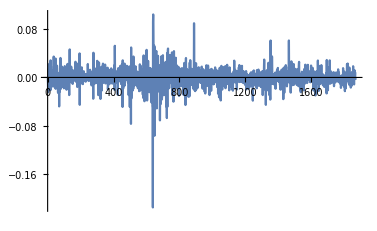

```mathematica
ListLinePlot[rsWethUsdc120dFiltered1HourCandle, PlotRange->All]
```

```mathematica
edistWethUsdc120dFiltered1HourCandle = EstimatedDistribution[rsWethUsdc120dFiltered1HourCandle, StableDistribution[1, aWU120dC1h, bWU120dC1h, locWU120dC1h, scaleWU120dC1h]]
```

StableDistribution[1,1.5843,-0.0493885,-0.000101694,0.0072772]

```mathematica
(* Check how similar compared to previous fit without new data ... *)
```

```mathematica
edistWethUsdc120dFiltered1HourCandle
```

StableDistribution[1,1.59768,-0.0971292,-0.000157254,0.00790013]

```mathematica
(* Not bad, especially on sigma and alpha ... *)
```

```mathematica
(* Interesting ... compound less on the funding payments, have more leeway. How does that make sense wrt inverse cdf exponentiation? *)
```

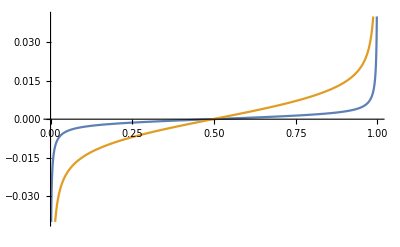

```mathematica
Plot[{InverseCDF[edistWethUsdc120dFiltered,x],InverseCDF[edistWethUsdc120dFiltered1HourCandle,x], InverseCDF[edistWethUsdc120dFiltered4HourCandle,x]},{x,0,1.0}, PlotRange->{-0.04, 0.04}]
```

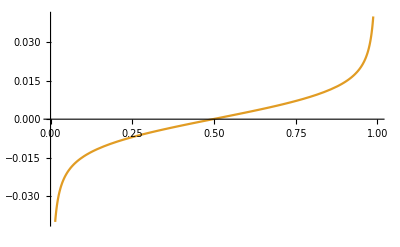

```mathematica
Plot[{, InverseCDF[edistWethUsdc120dFiltered1HourCandle,x]},{x,0,1.0},  PlotRange->{-0.04, 0.04}]
```

```mathematica
InverseCDF[edistWethUsdc120dFiltered1HourCandle,0.99]
```

0.0459063

```mathematica
InverseCDF[edistWethUsdc120dFiltered,0.99]
```

0.0127859

```mathematica
Exp[0.012785934108095686]
```

1.01287

```mathematica
(* Hmmm, so maybe plot e^(mu * T + sig * (T/a)^(1/a) * F^{-1}(1-alpha)) as a function of update times T. What does this tell us vs d we're looking for? *)
```

```mathematica
edistWethUsdc120dFiltered1HourCandle
```

StableDistribution[1,1.5843,-0.0493885,-0.000101694,0.0072772]

```mathematica
(* Define mu, sig functions for exponential term in d *)
```

```mathematica
mu[a_, loc_] := loc
```

```mathematica
sig[a_, scale_] :=scale/( 1/a)^(1/a)
```

```mathematica
(* Apply to our case *)
```

```mathematica
muWethUsdc120dFiltered1HourCandle = mu[1.5843003587383822,-0.00010169418797317535]
```

-0.000101694

```mathematica
sigWethUsdc120dFiltered1HourCandle = sig[1.5843003587383822,0.00727719566405363]
```

0.00972972

```mathematica
aWethUsdc120dFiltered1HourCandle = 1.5843003587383822
```

1.5843

```mathematica
edistWethUsdc120dFiltered1HourCandleNormalized = StableDistribution[1,aWethUsdc120dFiltered1HourCandle,0,0,1]
```

StableDistribution[1,1.5843,0,0,1]

```mathematica
InverseCDF[edistWethUsdc120dFiltered1HourCandleNormalized,0.90]
```

1.99592

```mathematica
InverseCDF[edistWethUsdc120dFiltered1HourCandleNormalized,0.95]
```

2.84713

```mathematica
InverseCDF[edistWethUsdc120dFiltered1HourCandleNormalized,0.99]
```

6.48811

```mathematica
factorWethUsdc120dFiltered1HourCandle[t_, alpha_]:= Exp[muWethUsdc120dFiltered1HourCandle*t + sigWethUsdc120dFiltered1HourCandle * (t/aWethUsdc120dFiltered1HourCandle)^(1/aWethUsdc120dFiltered1HourCandle) * InverseCDF[edistWethUsdc120dFiltered1HourCandleNormalized,1-alpha]]
```

```mathematica
factorWethUsdc120dFiltered1HourCandle[1, 0.01]
```

1.04824

```mathematica
(* TODO: Redo this analysis! ... Below is in line with 4 hour candle above :) *)
```

```mathematica
factorWethUsdc120dFiltered1HourCandle[4, 0.01]
```

1.11947

```mathematica
factorWethUsdc120dFiltered1HourCandle[8, 0.01]
```

1.19079

```mathematica
(* Over 24 hours you can see the difference substantially at different confidence levels ... *)
```

```mathematica
factorWethUsdc120dFiltered1HourCandle[24, 0.01]
```

1.41697

```mathematica
factorWethUsdc120dFiltered1HourCandle[24, 0.10]
```

1.11129

```mathematica
factorWethUsdc120dFiltered1HourCandle[24, 0.05]
```

1.16366

```mathematica
(* VaR at 95% seems good here in terms of usability for trading. 15% draw down in a day worst case on ETH/USDC is not terrible in terms of funding rate max *)
```

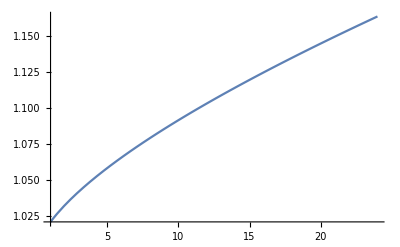

```mathematica
Plot[factorWethUsdc120dFiltered1HourCandle[t, 0.05], {t, 1, 24}]
```

```mathematica
(* Interesting S shape here ... Due to the Exp[t^(1/1.5)] term *)
```

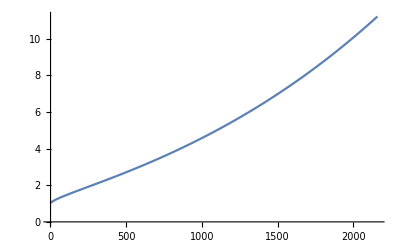

```mathematica
Plot[factorWethUsdc120dFiltered1HourCandle[t, 0.05], {t, 1, 24*30*3}]
```

```mathematica
(* So takes on order of 2 months to reach a 5x price cap on price bracket amount *)
```

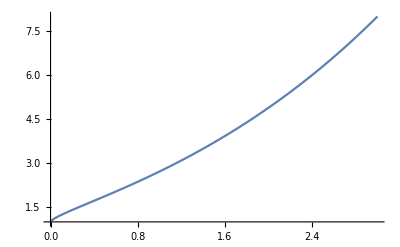

```mathematica
Plot[Exp[(t)^(1/1.5)], {t, 0, 3}]
```

```mathematica
(* This is where caps become very good :) *)
```

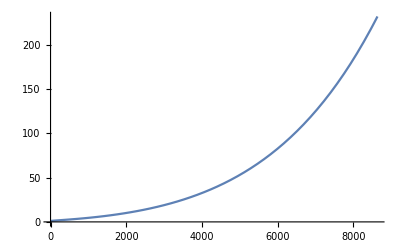

```mathematica
Plot[factorWethUsdc120dFiltered1HourCandle[t, 0.05], {t, 1, 24*30*12}]
```

```mathematica
(* Plot k AND (1-k)^m where m is diff depending on number of times we compound *)
```

```mathematica
(* Assume k min is determined by factor value at 95% confidence for different number of periods T *)
```

```mathematica
dmin95WethUsdc120dFiltered1HourCandle[t_] := factorWethUsdc120dFiltered1HourCandle[t, 0.05]
```

```mathematica
kmin95WethUsdc120dFiltered1HourCandle[t_] := (1-1/dmin95WethUsdc120dFiltered1HourCandle[t])/2
```

```mathematica
(* Look at different time periods ... 1 (1h), 4 (4h), 6 (6h), 8 (8h), 12 (12h), 24 (1d), 168 (7d) *)
```

```mathematica
kmin95T1hWethUsdc120dFiltered1HourCandle = kmin95WethUsdc120dFiltered1HourCandle[1]
```

0.0102032

```mathematica
kmin95T4hWethUsdc120dFiltered1HourCandle = kmin95WethUsdc120dFiltered1HourCandle[4]
```

0.0240508

```mathematica
kmin95T6hWethUsdc120dFiltered1HourCandle = kmin95WethUsdc120dFiltered1HourCandle[6]
```

0.0308052

```mathematica
kmin95T8hWethUsdc120dFiltered1HourCandle = kmin95WethUsdc120dFiltered1HourCandle[8]
```

0.0366706

```mathematica
kmin95T12hWethUsdc120dFiltered1HourCandle = kmin95WethUsdc120dFiltered1HourCandle[12]
```

0.0467734

```mathematica
kmin95T1dWethUsdc120dFiltered1HourCandle = kmin95WethUsdc120dFiltered1HourCandle[24]
```

0.0703214

```mathematica
kmin95T7dWethUsdc120dFiltered1HourCandle = kmin95WethUsdc120dFiltered1HourCandle[168]
```

0.199422

```mathematica
(* Interesting ... around minimum of 3.26% every 6 hr compounding. Can work with that to have some buffer in event bad fit *)
```

```mathematica
drawDownMin95WethUsdc120dFiltered1HourCandle[t_, m_] := 1-(1-kmin95WethUsdc120dFiltered1HourCandle[m])^(Floor[t/m])
```

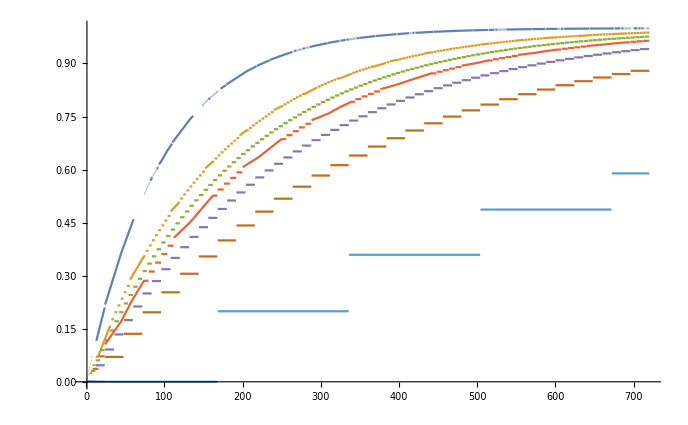

```mathematica
Plot[{drawDownMin95WethUsdc120dFiltered1HourCandle[t, 1],  drawDownMin95WethUsdc120dFiltered1HourCandle[t, 4],  drawDownMin95WethUsdc120dFiltered1HourCandle[t, 6], drawDownMin95WethUsdc120dFiltered1HourCandle[t, 8], drawDownMin95WethUsdc120dFiltered1HourCandle[t, 12], drawDownMin95WethUsdc120dFiltered1HourCandle[t, 24], drawDownMin95WethUsdc120dFiltered1HourCandle[t, 168]}, {t, 1, 24*30}]
```

```mathematica
(* Should like compare ratio of price bracket to d^(t/m). When set m for d, setting point at which d^m = price bracket[m].. But d is NOT an interest rate... k = (1-1/d)/2 makes this interesting in terms of traders view on draw down to their OI ... *)
```

```mathematica
(* Plot the actual interest rates seen per day for different values of m *)
```

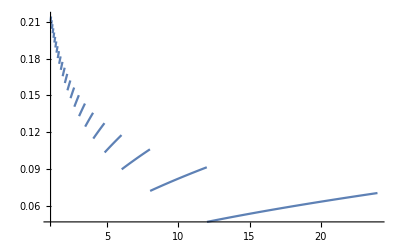

```mathematica
Plot[drawDownMin95WethUsdc120dFiltered1HourCandle[24, m], {m, 1, 24}]
```

```mathematica
drawDownMin95WethUsdc120dFiltered1HourCandle[24, 1]
```

0.218183

```mathematica
drawDownMin95WethUsdc120dFiltered1HourCandle[24, 4]
```

0.135901

```mathematica
drawDownMin95WethUsdc120dFiltered1HourCandle[24, 8]
```

0.106027

```mathematica
drawDownMin95WethUsdc120dFiltered1HourCandle[24, 12]
```

0.091359

```mathematica
(* Floor is making this visual difficult. Make continuous for plot purposes ... *)
```

```mathematica
drawDownMin95WethUsdc120dFiltered1HourCandleContinuous[t_, m_] := 1-(1-kmin95WethUsdc120dFiltered1HourCandle[m])^(t/m)
```

```mathematica
(* Below is min funding rate required extended to per day rate, if apply funding payment every m hours  *)
```

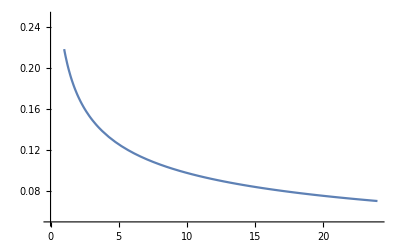

```mathematica
Plot[drawDownMin95WethUsdc120dFiltered1HourCandleContinuous[24, m], {m, 1, 24}, PlotRange->{0.05, 0.25}]
```

```mathematica
(* TODO: generalize this plot to 3d with alpha confidence on the other axis *)
```

```mathematica
(* Less we compound, smaller max DAILY funding rate needed to overcome price bracket changes. But more short term (<1d) we likely take *)
```

```mathematica
(* Generalize this for any confidence level (not just 95%) *)
```

```mathematica
dminWethUsdc120dFiltered1HourCandle[t_, alpha_] := factorWethUsdc120dFiltered1HourCandle[t, alpha]
```

```mathematica
kminWethUsdc120dFiltered1HourCandle[t_, alpha_] := (1-1/dminWethUsdc120dFiltered1HourCandle[t, alpha])/2
```

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandle[t_, alpha_, m_] := 1-(1-kminWethUsdc120dFiltered1HourCandle[m, alpha])^(Floor[t/m])
```

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandleContinuous[t_, alpha_, m_] := 1-(1-kminWethUsdc120dFiltered1HourCandle[m, alpha])^(t/m)
```

```mathematica
(* If fit to 8h compounded rate but still pay every 10min, how much is k? (k paid every 10 min but use 8h compounding amount) *)
```

```mathematica
(* Function to rescale k min calibrated using factor's value at time m in the future. But then applied over shorter time span < m *)
```

```mathematica
(* d_shorter^(#periods of short in long) = d_longer; m > t here *)
```

```mathematica
rescaledKminWethUsdc120dFiltered1HourCandle[t_, alpha_, m_] := (1-1/(dminWethUsdc120dFiltered1HourCandle[m, alpha])^(t/m))/2
```

```mathematica
rescaledKminWethUsdc120dFiltered1HourCandle[1/6, 0.05, 8]
```

0.000792806

```mathematica
(* Calculate effective funding rate after 8 hours applied every 10 min *)
```

```mathematica
1-(1-rescaledKminWethUsdc120dFiltered1HourCandle[1/6, 0.05, 8])^(6*8)
```

0.0373542

```mathematica
(* Compare with draw down applied only once every 8 hours *)
drawDownMinWethUsdc120dFiltered1HourCandle[8, 0.05, 8]
```

0.0366706

```mathematica
(* Looks good *)
```

```mathematica
(* Plot price bracket * d^(t/m) over time t *)
```

```mathematica
(* Look at funding rates needed over different confidence levels, to compare *)
```

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandle[24, 0.01, 8]
```

0.221594

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandle[24, 0.05, 8]
```

0.106027

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandle[24, 0.10, 8]
```

0.0756562

```mathematica
(* Last 95 -> 99% is what ramps it up significantly *)
```

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandle[24, 0.01, 1]
```

0.42805

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandle[24, 0.05, 1]
```

0.218183

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandle[24, 0.10, 1]
```

0.158401

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandle[24, 0.05, 24]
```

0.0703214

```mathematica
(* Similar with rescale. See if applied every 10 min for 8 hour value but after 1 d, 7d, 14d what drawdown is *)
```

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandle[24, 0.05, 8]
```

0.106027

```mathematica
1-(1-rescaledKminWethUsdc120dFiltered1HourCandle[1/6, 0.05, 8])^(6*24)
```

0.107929

```mathematica
rescaledKminWethUsdc120dFiltered1HourCandle[1/6, 0.05, 8]
```

0.000792806

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandle[24*7, 0.05, 8]
```

0.543678

```mathematica
1-(1-rescaledKminWethUsdc120dFiltered1HourCandle[1/6, 0.05, 8])^(6*24*7)
```

0.550431

```mathematica
(* Beautiful. Anchoring at factor value at m sets funding rate to be min. Does compound surpass price bracket at the 8 hour mark? *)
```

```mathematica
(* Look at rescaled draw down first to make sure consistent *)
```

```mathematica
rescaledDrawDownMinWethUsdc120dFiltered1HourCandle[t_,alpha_, m_, anchor_ ]:= 1- (1-rescaledKminWethUsdc120dFiltered1HourCandle[m, alpha, anchor])^(Floor[t/m])
```

```mathematica
rescaledDrawDownMinWethUsdc120dFiltered1HourCandle[24, 0.05, 1, 8]
```

0.107727

```mathematica
rescaledDrawDownMinWethUsdc120dFiltered1HourCandle[24*7, 0.05, 1, 8]
```

0.549717

```mathematica
(* Great. 1h funding payments on 8h anchor look great *)
```

```mathematica
(* Look at (1 - 2k)^m over time .... Compound factor for different compound intervals. Assume funding payments applied every 1 h for simplicity with fits. *)
```

```mathematica
compoundFactorMinWethUsdc120dFiltered1HourCandle[t_, alpha_, m_, anchor_]:= (1-2*rescaledKminWethUsdc120dFiltered1HourCandle[m, alpha, anchor])^(Floor[t/m])
```

```mathematica
(* 8h payment at 95% confidence of VaR led to drawdown of 11% worst case due to funding. Use alpha=0.05, m=8. Rescaled funding st paid every 1 h *)
```

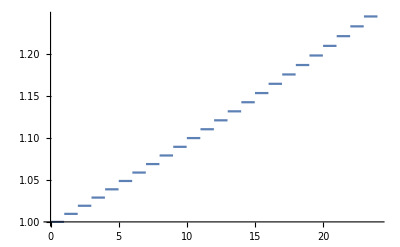

```mathematica
Plot[{1/compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24}]
```

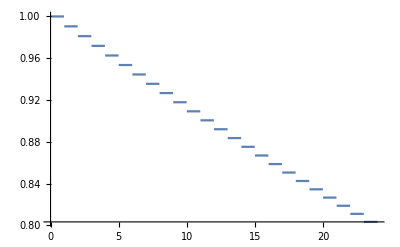

```mathematica
Plot[{compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24}]
```

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandle[24, 0.05, 8]
```

0.106027

```mathematica
1-compoundFactorMinWethUsdc120dFiltered1HourCandle[24, 0.05, 1, 8]
```

0.204281

```mathematica
(* Perfect. Draw down to OI imbalance should be about 2 times draw down to OI on a side *)
```

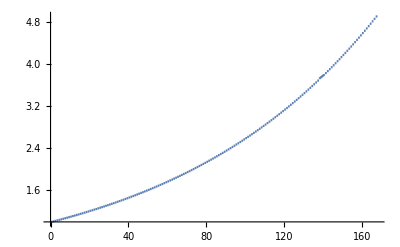

```mathematica
Plot[1/compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8], {t, 0, 24*7}]
```

```mathematica
(* Plot price bracket ...  *)
```

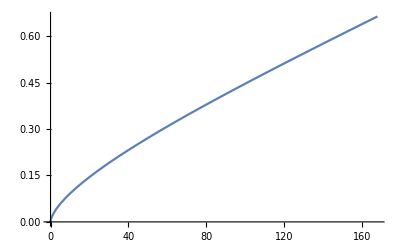

```mathematica
Plot[factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1, {t, 0, 24*7}]
```

```mathematica
(* Plot 1/compoundFactor vs price bracket *)
```

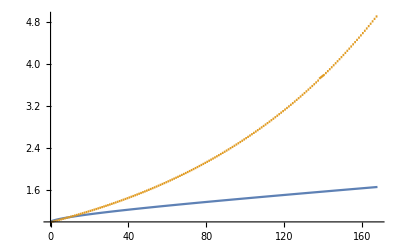

```mathematica
Plot[{factorWethUsdc120dFiltered1HourCandle[t, 0.05] , 1/compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*7}]
```

```mathematica
(* Look at the earlier times ... *)
```

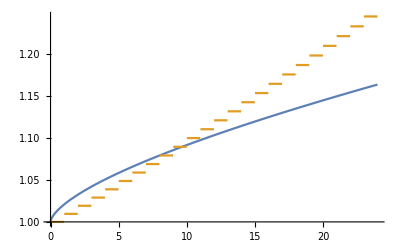

```mathematica
Plot[{factorWethUsdc120dFiltered1HourCandle[t, 0.05] , 1/compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24}]
```

```mathematica
(* Look at later times ... *)
```

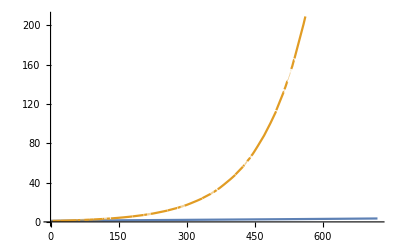

```mathematica
Plot[{factorWethUsdc120dFiltered1HourCandle[t, 0.05] , 1/compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*30}]
```

```mathematica
(* and the product of the two to make sure decreasing over time ... *)
```

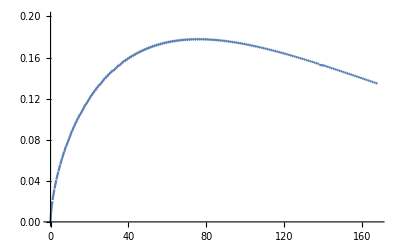

```mathematica
Plot[(factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8], {t, 0, 24*7}, PlotRange-> {0, 0.2}]
```

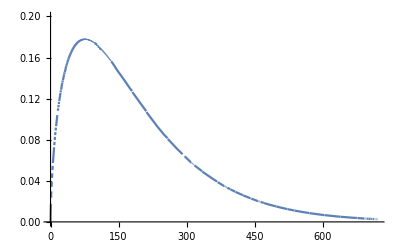

```mathematica
Plot[(factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8], {t, 0, 24*30}, PlotRange-> {0, 0.2}]
```

```mathematica
(* Compare with draw down over time *)
```

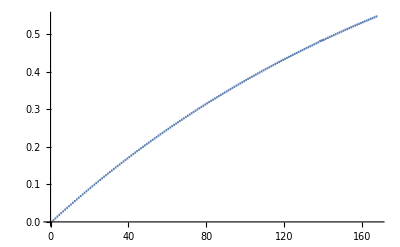

```mathematica
Plot[{rescaledDrawDownMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*7}]
```

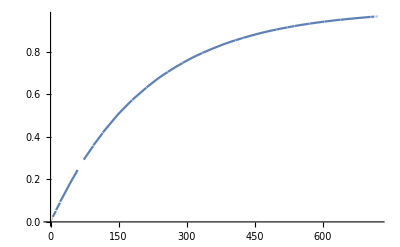

```mathematica
Plot[{rescaledDrawDownMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*30}]
```

```mathematica
(* Anchor used in k is everything. What is the interpretation? Time when d^m is exactly equal to first term in price bracket[m]. Then d^m surpasses greatly in size as m -> infty *)
```

```mathematica
(* So look at 1/compoundFactor vs price factor BEFORE hit the anchor to make sure 1/compoundFactor is less but we cross at anchor time ... *)
```

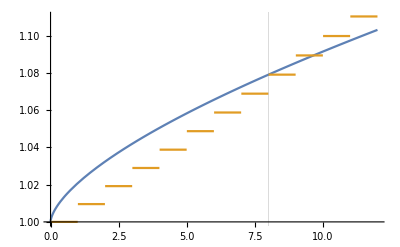

```mathematica
Plot[{factorWethUsdc120dFiltered1HourCandle[t, 0.05], 1/compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 12}, GridLines->{{8}}]
```

```mathematica
(* Perfect. Interpretation is correct. *)
```

```mathematica
(* Then product of price bracket and compound factor is playing catch up for the first 8 hours in order to get to point where decreasing over time? *)
```

```mathematica
(* Look at different price bracket VaR growth over time without compound factor *)
```

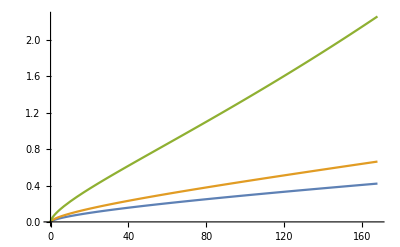

```mathematica
Plot[{(factorWethUsdc120dFiltered1HourCandle[t, 0.10] - 1), (factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1), (factorWethUsdc120dFiltered1HourCandle[t, 0.01] - 1)}, {t, 0, 24*7}]
```

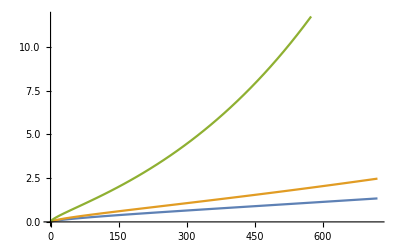

```mathematica
Plot[{(factorWethUsdc120dFiltered1HourCandle[t, 0.10] - 1), (factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1), (factorWethUsdc120dFiltered1HourCandle[t, 0.01] - 1)}, {t, 0, 24*30}]
```

```mathematica
(* Try product of price bracket and compound factor for different anchor times in k calibration ... *)
```

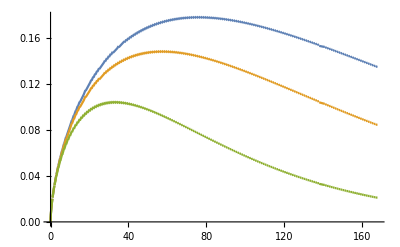

```mathematica
Plot[{(factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8], (factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 4], (factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*7}]
```

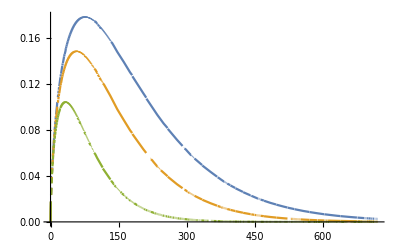

```mathematica
Plot[{(factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8], (factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 4], (factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*30}]
```

```mathematica
(* So most VaR to passive holders happens over shorter term when imbalance first created. Longer users hold positions and imbalance gets drawn down through funding, the more VaR gets curbed and eventually brought to zero *)
```

```mathematica
(* What if we underestimate funding rate needed? As in should have used alpha=0.01 instead of alpha=0.05? what does this do to VaR over time? *)
```

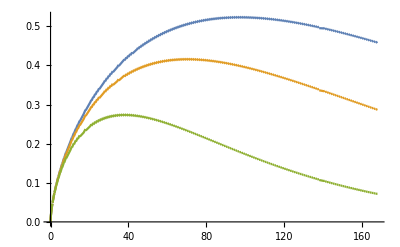

```mathematica
Plot[{(factorWethUsdc120dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8], (factorWethUsdc120dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 4], (factorWethUsdc120dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*7}]
```

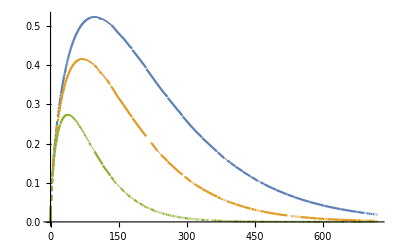

```mathematica
Plot[{(factorWethUsdc120dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8], (factorWethUsdc120dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 4], (factorWethUsdc120dFiltered1HourCandle[t, 0.01] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*30}]
```

```mathematica
(* Look at 1/compoundFactor (larger alpha than required) vs price factor BEFORE hit the anchor to see what new anchor time is ... *)
```

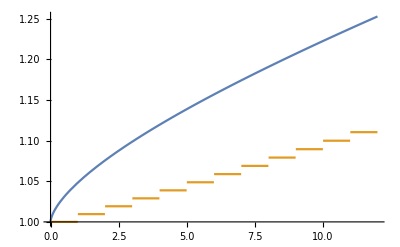

```mathematica
Plot[{factorWethUsdc120dFiltered1HourCandle[t, 0.01], 1/compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 12}]
```

```mathematica
(* Interesting, anchor time comes much later. Not great, but still exists ... However, VaR still seems to decrease tho, just more drawn out AND significantly higher max value/peak (about 2x for alpha=0.05). *)
```

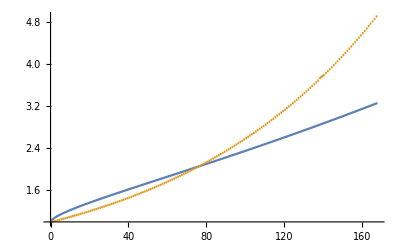

```mathematica
Plot[{factorWethUsdc120dFiltered1HourCandle[t, 0.01], 1/compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*7}]
```

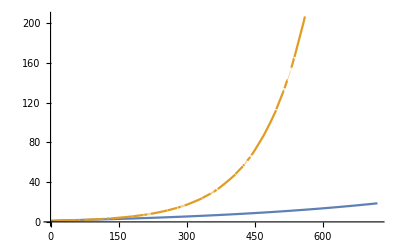

```mathematica
Plot[{factorWethUsdc120dFiltered1HourCandle[t, 0.01], 1/compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 24*30}]
```

```mathematica
(* Instead of anticipated anchor of 8h, get anchor around 72h (3d). *)
```

```mathematica
(* What about set funding factor to not exp^{(m*t)^{1/a}} but exp^{m*(t)^(1/a)}? What's difference in interest rate? *)
```

```mathematica
factorLargerWethUsdc120dFiltered1HourCandle[t_, alpha_]:= Exp[muWethUsdc120dFiltered1HourCandle*t + sigWethUsdc120dFiltered1HourCandle * t * (1/aWethUsdc120dFiltered1HourCandle)^(1/aWethUsdc120dFiltered1HourCandle) * InverseCDF[edistWethUsdc120dFiltered1HourCandleNormalized,1-alpha]]
```

```mathematica
factorLargerWethUsdc120dFiltered1HourCandle[8, 0.05]
```

1.17932

```mathematica
factorWethUsdc120dFiltered1HourCandle[8, 0.05]
```

1.07915

```mathematica
factorLargerWethUsdc120dFiltered1HourCandle[24, 0.05]
```

1.6402

```mathematica
factorWethUsdc120dFiltered1HourCandle[24, 0.05]
```

1.16366

```mathematica
(* Yea this gets out of control fast ... *)
```

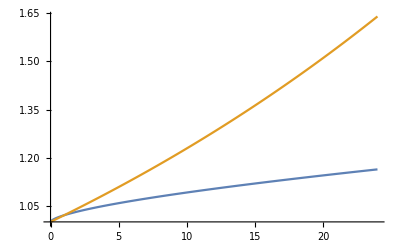

```mathematica
Plot[{factorWethUsdc120dFiltered1HourCandle[t, 0.05], factorLargerWethUsdc120dFiltered1HourCandle[t, 0.05]}, {t, 0, 24}]
```

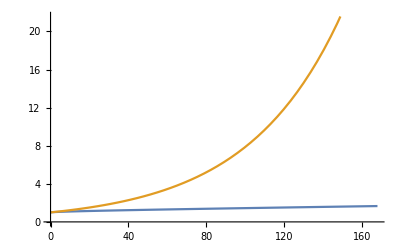

```mathematica
Plot[{factorWethUsdc120dFiltered1HourCandle[t, 0.05], factorLargerWethUsdc120dFiltered1HourCandle[t, 0.05]}, {t, 0, 24*7}]
```

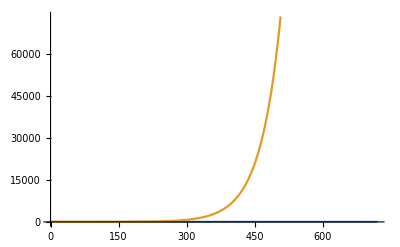

```mathematica
Plot[{factorWethUsdc120dFiltered1HourCandle[t, 0.05], factorLargerWethUsdc120dFiltered1HourCandle[t, 0.05]}, {t, 0, 24*30}]
```

```mathematica
(* We can't use the larger factor ... Actually a good preview for fits that are closer to Cauchy :/ *)
```

```mathematica
(* Plot continuous draw down as 3d with alpha varying as well *)
```

```mathematica
Plot3D[drawDownMinWethUsdc120dFiltered1HourCandleContinuous[24, a, m], {a, 0.01, 0.1}, {m, 1, 24}]
```

-Graphics3D-

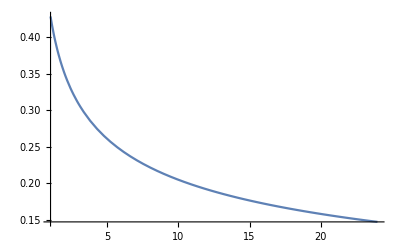

```mathematica
Plot[drawDownMinWethUsdc120dFiltered1HourCandleContinuous[24, 0.01, m], {m, 1, 24}]
```

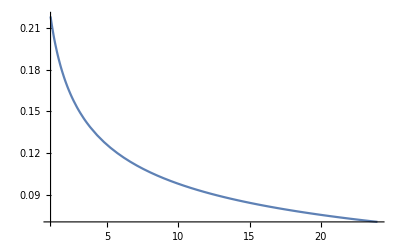

```mathematica
Plot[drawDownMinWethUsdc120dFiltered1HourCandleContinuous[24, 0.05, m], {m, 1, 24}]
```

```mathematica
(* About double if look at 99% confidence level vs 95% *)
```

```mathematica
drawDownMinWethUsdc120dFiltered1HourCandleContinuous[24, 0.01, 5]
```

0.260379

```mathematica
(* What about underestimating the stable distribution fit params? *)
```

```mathematica
(* Import data for UNI/WETH and convert to 1h candles *)
```

```mathematica
tblUniWeth120d = Import["120/data-1626472963_uni-weth-twap.csv"]
```

{{,timestamp,twap},{0,1.61878×10^9,1.4244×10^16},{1,1.61878×10^9,1.42041×10^16},{2,1.61878×10^9,1.41202×10^16},{3,1.61878×10^9,1.41232×10^16},{4,1.61885×10^9,1.11905×10^16},6779,{6785,1.62646×10^9,8.75082×10^15},{6786,1.62647×10^9,8.75708×10^15},{6787,1.62647×10^9,8.75789×10^15},{6788,1.62647×10^9,8.76048×10^15},{6789,1.62647×10^9,8.75972×10^15},{6790,1.62647×10^9,8.75626×10^15}}
 |  |  |  |

```mathematica
Length[tblUniWeth120d]
```

6791

```mathematica
twapsUniWeth120dFiltered = Table[tblUniWeth120d[[i]][[3]], {i, 20, Length[tblUniWeth120d]}]
```

{1.47173×10^16,1.47457×10^16,1.47367×10^16,1.47112×10^16,1.47093×10^16,1.46965×10^16,1.4693×10^16,1.46974×10^16,1.47074×10^16,1.46991×10^16,1.46988×10^16,1.46882×10^16,1.46469×10^16,1.45575×10^16,1.44941×10^16,1.44527×10^16,1.44296×10^16,1.44048×10^16,1.43748×10^16,1.43042×10^16,1.42377×10^16,1.41513×10^16,1.40647×10^16,1.4037×10^16,1.40033×10^16,1.3985×10^16,1.39899×10^16,1.39702×10^16,1.39903×10^16,1.4033×10^16,1.40449×10^16,1.40431×10^16,1.40417×10^16,1.40173×10^16,1.3944×10^16,1.39079×10^16,1.38472×10^16,1.38336×10^16,1.38352×10^16,1.38429×10^16,1.38433×10^16,1.38711×10^16,1.38869×10^16,1.3899×10^16,1.39186×10^16,1.3921×10^16,1.39176×10^16,1.38979×10^16,1.38774×10^16,1.3856×10^16,1.38393×10^16,1.3829×10^16,1.3808×10^16,1.37221×10^16,1.35037×10^16,1.34808×10^16,1.34925×10^16,1.34994×10^16,1.35191×10^16,1.36529×10^16,1.3682×10^16,1.37078×10^16,1.3713×10^16,1.37054×10^16,1.36837×10^16,1.36537×10^16,1.36374×10^16,1.36282×10^16,1.35991×10^16,1.3589×10^16,1.35825×10^16,1.35551×10^16,1.35337×10^16,1.35453×10^16,1.35606×10^16,1.36053×10^16,1.36494×10^16,1.36663×10^16,1.36976×10^16,1.37173×10^16,1.37111×10^16,1.37232×10^16,1.37249×10^16,1.36965×10^16,1.36601×10^16,1.36426×10^16,1.36623×10^16,1.37063×10^16,1.37625×10^16,1.38671×10^16,1.3917×10^16,1.39274×10^16,1.39312×10^16,1.39385×10^16,1.3937×10^16,1.39063×10^16,1.38837×10^16,1.38717×10^16,1.38472×10^16,1.38449×10^16,1.38347×10^16,1.38296×10^16,1.38345×10^16,1.38091×10^16,1.38004×10^16,1.37992×10^16,1.38027×10^16,1.38049×10^16,1.38449×10^16,1.39925×10^16,1.40314×10^16,1.40592×10^16,1.40792×10^16,1.40646×10^16,1.40505×10^16,1.39918×10^16,1.39149×10^16,1.38461×10^16,1.3762×10^16,1.37427×10^16,1.36956×10^16,1.36195×10^16,1.35761×10^16,1.35272×10^16,1.3509×10^16,1.35027×10^16,1.35065×10^16,1.35427×10^16,1.35926×10^16,1.36404×10^16,1.37001×10^16,1.37786×10^16,1.38932×10^16,1.4073×10^16,1.42423×10^16,1.43066×10^16,1.43399×10^16,1.44377×10^16,1.45196×10^16,1.45539×10^16,1.46053×10^16,1.4737×10^16,1.47173×10^16,1.46739×10^16,1.466×10^16,1.46774×10^16,1.46677×10^16,1.46691×10^16,1.46448×10^16,1.46154×10^16,1.45299×10^16,1.44979×10^16,1.44453×10^16,1.44064×10^16,1.44044×10^16,1.43972×10^16,1.43982×10^16,1.43944×10^16,1.43835×10^16,1.43694×10^16,1.43445×10^16,1.43263×10^16,1.43212×10^16,1.42827×10^16,1.42106×10^16,1.41886×10^16,1.41733×10^16,1.41961×10^16,1.42318×10^16,1.43313×10^16,1.44233×10^16,1.44907×10^16,1.46451×10^16,1.46994×10^16,1.47221×10^16,1.4714×10^16,1.47261×10^16,1.47393×10^16,1.48052×10^16,1.48795×10^16,1.49834×10^16,1.50446×10^16,1.50913×10^16,1.51016×10^16,1.51154×10^16,1.51545×10^16,1.51981×10^16,1.51921×10^16,1.52088×10^16,1.51617×10^16,1.507×10^16,1.49623×10^16,1.49003×10^16,1.48903×10^16,1.48698×10^16,1.48692×10^16,1.48723×10^16,1.48685×10^16,1.48635×10^16,1.48708×10^16,1.4933×10^16,1.50195×10^16,1.50942×10^16,1.51632×10^16,1.51757×10^16,1.52008×10^16,1.52135×10^16,1.52352×10^16,1.52748×10^16,1.52577×10^16,1.52058×10^16,1.51189×10^16,1.50572×10^16,1.49895×10^16,1.49228×10^16,1.49068×10^16,1.48131×10^16,1.4801×10^16,1.47933×10^16,1.47777×10^16,1.47723×10^16,1.47327×10^16,1.46801×10^16,1.45567×10^16,1.44706×10^16,1.44474×10^16,1.43825×10^16,1.43609×10^16,1.43487×10^16,1.43179×10^16,1.4305×10^16,1.4286×10^16,1.42659×10^16,1.42585×10^16,1.42228×10^16,1.42144×10^16,1.41542×10^16,1.40575×10^16,1.39924×10^16,1.39513×10^16,1.39406×10^16,1.39123×10^16,1.39041×10^16,1.39164×10^16,1.39161×10^16,1.39274×10^16,1.39542×10^16,1.39595×10^16,1.40286×10^16,1.40504×10^16,1.40556×10^16,1.40633×10^16,1.40742×10^16,1.40795×10^16,1.40795×10^16,1.41273×10^16,1.41628×10^16,1.42089×10^16,1.42533×10^16,1.42931×10^16,1.43101×10^16,1.43224×10^16,1.437×10^16,1.44052×10^16,1.44072×10^16,1.43912×10^16,1.43567×10^16,1.42971×10^16,1.42623×10^16,1.42456×10^16,1.42455×10^16,1.42573×10^16,1.42204×10^16,1.42078×10^16,1.41601×10^16,1.41336×10^16,1.41036×10^16,1.40539×10^16,1.40433×10^16,1.4041×10^16,1.40862×10^16,1.41705×10^16,1.42542×10^16,1.43073×10^16,1.43442×10^16,1.4386×10^16,1.44303×10^16,1.44369×10^16,1.44249×10^16,1.4403×10^16,1.43898×10^16,1.44036×10^16,1.44075×10^16,1.4437×10^16,1.44542×10^16,1.44466×10^16,1.44461×10^16,1.44506×10^16,1.4478×10^16,1.45394×10^16,1.4613×10^16,1.46128×10^16,1.46092×10^16,1.45577×10^16,1.45244×10^16,1.44544×10^16,1.43907×10^16,1.4363×10^16,1.43148×10^16,1.42867×10^16,1.42533×10^16,1.41895×10^16,1.41802×10^16,1.41887×10^16,1.41951×10^16,1.42173×10^16,1.42208×10^16,1.42209×10^16,1.41657×10^16,1.41317×10^16,1.40858×10^16,1.40476×10^16,1.39936×10^16,1.39299×10^16,1.39068×10^16,1.38952×10^16,1.39009×10^16,1.39101×10^16,1.3916×10^16,1.39094×10^16,1.38949×10^16,1.38598×10^16,1.37836×10^16,1.37764×10^16,1.37593×10^16,1.3759×10^16,1.37714×10^16,1.38033×10^16,1.38267×10^16,1.38458×10^16,1.38523×10^16,1.38636×10^16,1.38673×10^16,1.39035×10^16,1.39177×10^16,1.39412×10^16,1.39922×10^16,1.40212×10^16,1.398×10^16,1.39649×10^16,1.39221×10^16,1.38766×10^16,1.38544×10^16,1.38184×10^16,1.37909×10^16,1.37814×10^16,1.37912×10^16,1.3799×10^16,1.38077×10^16,1.38423×10^16,1.38676×10^16,1.38846×10^16,1.39094×10^16,1.39193×10^16,1.39304×10^16,1.39352×10^16,1.39378×10^16,1.39326×10^16,1.39256×10^16,1.39138×10^16,1.38931×10^16,1.38879×10^16,1.39108×10^16,1.39559×10^16,1.39704×10^16,1.40006×10^16,1.40176×10^16,1.40272×10^16,1.40153×10^16,1.40158×10^16,1.40186×10^16,1.40223×10^16,1.40235×10^16,1.40355×10^16,1.40463×10^16,1.40624×10^16,1.40668×10^16,1.40686×10^16,1.4059×10^16,1.40569×10^16,1.40547×10^16,1.40918×10^16,1.41025×10^16,1.41282×10^16,1.41326×10^16,1.41134×10^16,1.39936×10^16,1.39638×10^16,1.39205×10^16,1.39018×10^16,1.3859×10^16,1.38565×10^16,1.38487×10^16,1.38085×10^16,1.38037×10^16,1.38016×10^16,1.37847×10^16,1.37574×10^16,1.3741×10^16,1.37216×10^16,1.37064×10^16,1.36852×10^16,1.36869×10^16,1.3692×10^16,1.36928×10^16,1.36902×10^16,1.36826×10^16,1.36512×10^16,1.36174×10^16,1.35984×10^16,1.35974×10^16,1.35969×10^16,1.35957×10^16,1.35954×10^16,1.3607×10^16,1.36143×10^16,1.36185×10^16,1.36294×10^16,1.36429×10^16,1.36461×10^16,1.36452×10^16,1.36435×10^16,1.36479×10^16,1.36789×10^16,1.3684×10^16,1.3692×10^16,1.37253×10^16,1.37328×10^16,1.37465×10^16,1.37527×10^16,1.37546×10^16,1.37736×10^16,1.37759×10^16,1.38022×10^16,1.38294×10^16,1.38356×10^16,1.38479×10^16,1.3858×10^16,1.38642×10^16,1.38619×10^16,1.38631×10^16,1.38613×10^16,1.38637×10^16,1.38665×10^16,1.38688×10^16,1.38662×10^16,1.38408×10^16,1.38325×10^16,1.38244×10^16,1.38291×10^16,1.38736×10^16,1.39678×10^16,1.4087×10^16,1.42454×10^16,1.43564×10^16,1.44342×10^16,1.44758×10^16,1.45224×10^16,1.4509×10^16,1.44997×10^16,1.45091×10^16,1.44997×10^16,1.4509×10^16,1.45298×10^16,1.45332×10^16,1.45073×10^16,1.45184×10^16,1.45412×10^16,1.45711×10^16,1.46335×10^16,1.47338×10^16,1.47842×10^16,1.48096×10^16,1.48005×10^16,1.47802×10^16,1.47073×10^16,1.46644×10^16,1.46182×10^16,1.45558×10^16,1.45132×10^16,1.45725×10^16,1.45963×10^16,1.46307×10^16,1.46559×10^16,1.46843×10^16,1.46831×10^16,1.46697×10^16,1.46619×10^16,1.46623×10^16,1.46204×10^16,1.45925×10^16,1.45342×10^16,1.44831×10^16,1.44405×10^16,1.43935×10^16,1.44188×10^16,1.44767×10^16,1.44876×10^16,1.45003×10^16,1.45318×10^16,1.45323×10^16,1.45393×10^16,1.4531×10^16,1.45264×10^16,1.45248×10^16,1.45183×10^16,1.44951×10^16,1.44722×10^16,1.4464×10^16,1.44716×10^16,1.44877×10^16,1.45037×10^16,1.45333×10^16,1.45584×10^16,1.4598×10^16,1.46556×10^16,1.46981×10^16,1.48033×10^16,1.48334×10^16,1.48214×10^16,1.47839×10^16,1.47519×10^16,1.46919×10^16,1.46653×10^16,1.46492×10^16,1.45827×10^16,1.45573×10^16,1.45217×10^16,1.44899×10^16,1.44448×10^16,1.44315×10^16,1.44315×10^16,1.44175×10^16,1.43817×10^16,1.43751×10^16,1.43571×10^16,1.4361×10^16,1.43791×10^16,1.44169×10^16,1.449×10^16,1.45734×10^16,1.46173×10^16,1.46602×10^16,1.46594×10^16,1.46262×10^16,1.45887×10^16,1.45617×10^16,1.45475×10^16,1.45342×10^16,1.4524×10^16,1.45211×10^16,1.4518×10^16,1.4513×10^16,1.45071×10^16,1.44985×10^16,1.44833×10^16,1.45213×10^16,1.454×10^16,1.45578×10^16,1.45834×10^16,1.45966×10^16,1.45687×10^16,1.45387×10^16,1.45072×10^16,1.44175×10^16,1.43522×10^16,1.4303×10^16,1.42869×10^16,1.4286×10^16,1.42885×10^16,1.42975×10^16,1.4321×10^16,1.43335×10^16,1.43454×10^16,1.43447×10^16,1.43411×10^16,1.43346×10^16,1.43309×10^16,1.4311×10^16,1.42879×10^16,1.42637×10^16,1.42492×10^16,1.4236×10^16,1.42205×10^16,1.42211×10^16,1.42321×10^16,1.42501×10^16,1.42791×10^16,1.43297×10^16,1.43699×10^16,1.43928×10^16,1.44209×10^16,1.44362×10^16,1.44835×10^16,1.44996×10^16,1.45066×10^16,1.45161×10^16,1.45268×10^16,1.45532×10^16,1.46171×10^16,1.47025×10^16,1.48083×10^16,1.48971×10^16,1.49256×10^16,1.49835×10^16,1.50208×10^16,1.50712×10^16,1.50922×10^16,1.50989×10^16,1.51032×10^16,1.51016×10^16,1.5072×10^16,1.50402×10^16,1.50172×10^16,1.50077×10^16,1.5009×10^16,1.50158×10^16,1.503×10^16,1.50347×10^16,1.50501×10^16,1.5048×10^16,1.50434×10^16,1.50056×10^16,1.49894×10^16,1.50092×10^16,1.5104×10^16,1.51143×10^16,1.51703×10^16,1.51916×10^16,1.52113×10^16,1.52678×10^16,1.53037×10^16,1.54733×10^16,1.56226×10^16,1.57179×10^16,1.57561×10^16,1.57677×10^16,1.57702×10^16,1.57624×10^16,1.57358×10^16,1.57098×10^16,1.56785×10^16,1.56234×10^16,1.55975×10^16,1.55814×10^16,1.557×10^16,1.55846×10^16,1.56193×10^16,1.5635×10^16,1.56399×10^16,1.56392×10^16,1.5653×10^16,1.56844×10^16,1.57202×10^16,1.57381×10^16,1.57645×10^16,1.57578×10^16,1.57066×10^16,1.56357×10^16,1.55819×10^16,1.55562×10^16,1.554×10^16,1.54617×10^16,1.54387×10^16,1.54198×10^16,1.53846×10^16,1.53736×10^16,1.51719×10^16,1.51004×10^16,1.50567×10^16,1.49902×10^16,1.49453×10^16,1.49353×10^16,1.49258×10^16,1.49264×10^16,1.4923×10^16,1.49397×10^16,1.48929×10^16,1.48763×10^16,1.48577×10^16,1.48372×10^16,1.48402×10^16,1.48543×10^16,1.48667×10^16,1.48799×10^16,1.489×10^16,1.49064×10^16,1.49173×10^16,1.49359×10^16,1.49372×10^16,1.49392×10^16,1.49588×10^16,1.49641×10^16,1.49718×10^16,1.49856×10^16,1.50068×10^16,1.50125×10^16,1.50069×10^16,1.50069×10^16,1.49946×10^16,1.49574×10^16,1.49622×10^16,1.49821×10^16,1.504×10^16,1.5118×10^16,1.52474×10^16,1.53948×10^16,1.54405×10^16,1.54533×10^16,1.54593×10^16,1.54348×10^16,1.54122×10^16,1.53972×10^16,1.53796×10^16,1.5357×10^16,1.53328×10^16,1.53183×10^16,1.52626×10^16,1.52459×10^16,1.51881×10^16,1.51733×10^16,1.51551×10^16,1.51531×10^16,1.51466×10^16,1.51498×10^16,1.50823×10^16,1.50368×10^16,1.50106×10^16,1.49669×10^16,1.49431×10^16,1.49049×10^16,1.48742×10^16,1.48886×10^16,1.49106×10^16,1.49442×10^16,1.50255×10^16,1.50488×10^16,1.50753×10^16,1.51105×10^16,1.51232×10^16,1.5144×10^16,1.51375×10^16,1.51312×10^16,1.50971×10^16,1.50947×10^16,1.51031×10^16,1.5109×10^16,1.51107×10^16,1.5105×10^16,1.51109×10^16,1.51321×10^16,1.51582×10^16,1.51772×10^16,1.52788×10^16,1.52988×10^16,1.5374×10^16,1.54055×10^16,1.54326×10^16,1.55007×10^16,1.55087×10^16,1.55035×10^16,1.5495×10^16,1.55154×10^16,1.55581×10^16,1.5568×10^16,1.55608×10^16,1.55693×10^16,1.55618×10^16,1.553×10^16,1.55033×10^16,1.55353×10^16,1.55822×10^16,1.56019×10^16,1.56492×10^16,1.56551×10^16,1.56593×10^16,1.56657×10^16,1.56539×10^16,1.56066×10^16,1.55982×10^16,1.5591×10^16,1.55859×10^16,1.55756×10^16,1.55358×10^16,1.553×10^16,1.55151×10^16,1.55035×10^16,1.5487×10^16,1.54927×10^16,1.5476×10^16,1.54554×10^16,1.54365×10^16,1.54357×10^16,1.54269×10^16,1.54111×10^16,1.53976×10^16,1.53954×10^16,1.5384×10^16,1.53843×10^16,1.54061×10^16,1.54372×10^16,1.54644×10^16,1.55387×10^16,1.5598×10^16,1.57495×10^16,1.57788×10^16,1.58355×10^16,1.58536×10^16,1.58156×10^16,1.57605×10^16,1.57763×10^16,1.58035×10^16,1.58304×10^16,1.58785×10^16,1.58953×10^16,1.58887×10^16,1.5879×10^16,1.58655×10^16,1.58508×10^16,1.58102×10^16,1.5772×10^16,1.57366×10^16,1.57047×10^16,1.5694×10^16,1.56725×10^16,1.56745×10^16,1.56747×10^16,1.56854×10^16,1.56917×10^16,1.57×10^16,1.56905×10^16,1.56827×10^16,1.56482×10^16,1.56195×10^16,1.55486×10^16,1.55088×10^16,1.54917×10^16,1.54785×10^16,1.54762×10^16,1.5473×10^16,1.54727×10^16,1.54629×10^16,1.54598×10^16,1.544×10^16,1.54315×10^16,1.541×10^16,1.5397×10^16,1.53706×10^16,1.53153×10^16,1.52987×10^16,1.5288×10^16,1.52887×10^16,1.52893×10^16,1.52902×10^16,1.52804×10^16,1.52632×10^16,1.52267×10^16,1.51923×10^16,1.51387×10^16,1.51084×10^16,1.51045×10^16,1.51024×10^16,1.50874×10^16,1.50454×10^16,1.50326×10^16,1.49663×10^16,1.49524×10^16,1.49268×10^16,1.4906×10^16,1.48952×10^16,1.48648×10^16,1.48428×10^16,1.47894×10^16,1.47478×10^16,1.47386×10^16,1.47295×10^16,1.47342×10^16,1.47676×10^16,1.47805×10^16,1.47877×10^16,1.48043×10^16,1.48215×10^16,1.48285×10^16,1.48576×10^16,1.4889×10^16,1.49092×10^16,1.49809×10^16,1.4993×10^16,1.50317×10^16,1.50417×10^16,1.50384×10^16,1.50324×10^16,1.50342×10^16,1.50346×10^16,1.50327×10^16,1.50301×10^16,1.5025×10^16,1.50046×10^16,1.4991×10^16,1.4984×10^16,1.49682×10^16,1.49551×10^16,1.4911×10^16,1.48643×10^16,1.48015×10^16,1.47773×10^16,1.47747×10^16,1.47647×10^16,1.47476×10^16,1.47094×10^16,1.46969×10^16,1.46869×10^16,1.4671×10^16,1.46638×10^16,1.46494×10^16,1.46743×10^16,1.46848×10^16,1.46924×10^16,1.4691×10^16,1.46859×10^16,1.46727×10^16,1.46637×10^16,1.46592×10^16,1.46679×10^16,1.47029×10^16,1.47469×10^16,1.47677×10^16,1.4778×10^16,1.47954×10^16,1.4788×10^16,1.47664×10^16,1.47269×10^16,1.4718×10^16,1.47145×10^16,1.4721×10^16,1.47268×10^16,1.47336×10^16,1.47389×10^16,1.474×10^16,1.47436×10^16,1.47446×10^16,1.47399×10^16,1.47366×10^16,1.4724×10^16,1.46977×10^16,1.46728×10^16,1.46517×10^16,1.46383×10^16,1.4624×10^16,1.46124×10^16,1.45988×10^16,1.45888×10^16,1.45825×10^16,1.45949×10^16,1.46169×10^16,1.46718×10^16,1.46679×10^16,1.46671×10^16,1.46414×10^16,1.4616×10^16,1.4591×10^16,1.454×10^16,1.45061×10^16,1.4468×10^16,1.44042×10^16,1.44171×10^16,1.44235×10^16,1.44872×10^16,1.45261×10^16,1.45537×10^16,1.45776×10^16,1.45842×10^16,1.45922×10^16,1.4588×10^16,1.4585×10^16,1.46056×10^16,1.46106×10^16,1.46182×10^16,1.4633×10^16,1.46405×10^16,1.46362×10^16,1.46339×10^16,1.46349×10^16,1.46283×10^16,1.46216×10^16,1.46157×10^16,1.46138×10^16,1.46101×10^16,1.46061×10^16,1.46002×10^16,1.4595×10^16,1.46082×10^16,1.46088×10^16,1.46016×10^16,1.46041×10^16,1.46055×10^16,1.45956×10^16,1.45978×10^16,1.46056×10^16,1.46031×10^16,1.45988×10^16,1.45924×10^16,1.45741×10^16,1.45452×10^16,1.45213×10^16,1.44942×10^16,1.44502×10^16,1.43961×10^16,1.43962×10^16,1.43983×10^16,1.44013×10^16,1.44101×10^16,1.44237×10^16,1.44192×10^16,1.44103×10^16,1.44046×10^16,1.43942×10^16,1.43619×10^16,1.43526×10^16,1.4347×10^16,1.4333×10^16,1.43208×10^16,1.43027×10^16,1.42823×10^16,1.42612×10^16,1.42043×10^16,1.41985×10^16,1.41957×10^16,1.42072×10^16,1.42337×10^16,1.42385×10^16,1.42068×10^16,1.41913×10^16,1.41279×10^16,1.40715×10^16,1.40661×10^16,1.40469×10^16,1.4038×10^16,1.40056×10^16,1.3997×10^16,1.39924×10^16,1.39901×10^16,1.39757×10^16,1.39691×10^16,1.39682×10^16,1.39486×10^16,1.39405×10^16,1.39405×10^16,1.39412×10^16,1.39453×10^16,1.3961×10^16,1.39712×10^16,1.39718×10^16,1.3967×10^16,1.39577×10^16,1.39458×10^16,1.3943×10^16,1.39359×10^16,1.39171×10^16,1.38992×10^16,1.38768×10^16,1.38444×10^16,1.38209×10^16,1.38155×10^16,1.38053×10^16,1.38091×10^16,1.38031×10^16,1.37945×10^16,1.37856×10^16,1.37509×10^16,1.37077×10^16,1.36937×10^16,1.3689×10^16,1.36802×10^16,1.36918×10^16,1.37016×10^16,1.37026×10^16,1.36951×10^16,1.36891×10^16,1.36659×10^16,1.3658×10^16,1.36534×10^16,1.36646×10^16,1.60876×10^16,1.3671×10^16,1.36639×10^16,1.36518×10^16,1.36276×10^16,1.19101×10^16,1.35831×10^16,1.35564×10^16,1.35497×10^16,1.35488×10^16,1.35499×10^16,1.35535×10^16,1.35617×10^16,1.35708×10^16,1.35851×10^16,1.35862×10^16,1.35952×10^16,1.35975×10^16,1.35945×10^16,1.36027×10^16,1.36097×10^16,1.36123×10^16,1.36213×10^16,1.36341×10^16,1.3631×10^16,1.36296×10^16,1.36273×10^16,1.36251×10^16,1.36221×10^16,1.36204×10^16,1.36192×10^16,1.36173×10^16,1.36252×10^16,1.3654×10^16,1.36691×10^16,1.3673×10^16,1.36763×10^16,1.3677×10^16,1.36745×10^16,1.36788×10^16,1.36828×10^16,1.36949×10^16,1.36997×10^16,1.37082×10^16,1.37108×10^16,1.37127×10^16,1.37077×10^16,1.37106×10^16,1.37246×10^16,1.37336×10^16,1.3762×10^16,1.38042×10^16,1.38412×10^16,1.38937×10^16,1.39172×10^16,1.39522×10^16,1.3974×10^16,1.39713×10^16,1.39579×10^16,1.39935×10^16,1.40754×10^16,1.41652×10^16,1.43345×10^16,1.44414×10^16,1.4554×10^16,1.46003×10^16,1.459×10^16,1.45286×10^16,1.45059×10^16,1.44784×10^16,1.44386×10^16,1.44251×10^16,1.44373×10^16,1.44433×10^16,1.44551×10^16,1.44822×10^16,1.45172×10^16,1.4534×10^16,1.45213×10^16,1.45222×10^16,1.44964×10^16,1.44763×10^16,1.4471×10^16,1.44585×10^16,1.44584×10^16,1.44584×10^16,1.44564×10^16,1.44555×10^16,1.44488×10^16,1.44377×10^16,1.44428×10^16,1.44482×10^16,1.44492×10^16,1.44587×10^16,1.44696×10^16,1.44517×10^16,1.44433×10^16,1.44439×10^16,1.44354×10^16,1.44301×10^16,1.44222×10^16,1.44127×10^16,1.43742×10^16,1.43618×10^16,1.43388×10^16,1.43241×10^16,1.43295×10^16,1.43354×10^16,1.43523×10^16,1.43743×10^16,1.43933×10^16,1.44196×10^16,1.44303×10^16,1.44534×10^16,1.44152×10^16,1.44068×10^16,1.43798×10^16,1.43723×10^16,1.43741×10^16,1.43872×10^16,1.44196×10^16,1.44911×10^16,1.45279×10^16,1.45787×10^16,1.46081×10^16,1.46269×10^16,1.46109×10^16,1.46053×10^16,1.46103×10^16,1.46233×10^16,1.4634×10^16,1.46525×10^16,1.46615×10^16,1.46525×10^16,1.46298×10^16,1.46002×10^16,1.45561×10^16,1.44969×10^16,1.44729×10^16,1.44473×10^16,1.44355×10^16,1.44093×10^16,1.4385×10^16,1.43657×10^16,1.43329×10^16,1.42866×10^16,1.42559×10^16,1.42106×10^16,1.41653×10^16,1.41447×10^16,1.40723×10^16,1.40273×10^16,1.39879×10^16,1.39648×10^16,1.39437×10^16,1.39299×10^16,1.38943×10^16,1.38881×10^16,1.38825×10^16,1.38791×10^16,1.38797×10^16,1.38926×10^16,1.39008×10^16,1.38966×10^16,1.3892×10^16,1.38683×10^16,1.38459×10^16,1.382×10^16,1.38221×10^16,1.38292×10^16,1.38494×10^16,1.3847×10^16,1.38228×10^16,1.37793×10^16,1.37535×10^16,1.37309×10^16,1.37208×10^16,1.37066×10^16,1.36742×10^16,1.366×10^16,1.36267×10^16,1.36067×10^16,1.35882×10^16,1.35618×10^16,1.34674×10^16,1.34048×10^16,1.33173×10^16,1.32341×10^16,1.32032×10^16,1.31204×10^16,1.3101×10^16,1.30653×10^16,1.30241×10^16,1.29279×10^16,1.28606×10^16,1.28011×10^16,1.27813×10^16,1.27759×10^16,1.27655×10^16,1.27384×10^16,1.2721×10^16,1.26911×10^16,1.26511×10^16,1.2638×10^16,1.26288×10^16,1.26117×10^16,1.25854×10^16,1.25637×10^16,1.25168×10^16,1.24818×10^16,1.24441×10^16,1.24305×10^16,1.24021×10^16,1.2391×10^16,1.23834×10^16,1.237×10^16,1.23825×10^16,1.23731×10^16,1.23729×10^16,1.23761×10^16,1.23812×10^16,1.23714×10^16,1.23744×10^16,1.23978×10^16,1.24085×10^16,1.24257×10^16,1.24489×10^16,1.24633×10^16,1.24911×10^16,1.24996×10^16,1.25115×10^16,1.25321×10^16,1.253×10^16,1.25081×10^16,1.24939×10^16,1.24776×10^16,1.24558×10^16,1.2432×10^16,1.24221×10^16,1.24171×10^16,1.24088×10^16,1.24002×10^16,1.23892×10^16,1.23907×10^16,1.23927×10^16,1.23882×10^16,1.23833×10^16,1.2385×10^16,1.23933×10^16,1.23997×10^16,1.2417×10^16,1.24476×10^16,1.24493×10^16,1.2447×10^16,1.24447×10^16,1.24418×10^16,1.24404×10^16,1.24333×10^16,1.2413×10^16,1.23919×10^16,1.23658×10^16,1.23397×10^16,1.22946×10^16,1.2274×10^16,1.23459×10^16,1.2445×10^16,1.25171×10^16,1.26284×10^16,1.27401×10^16,1.27471×10^16,1.27096×10^16,1.26732×10^16,1.25806×10^16,1.25316×10^16,1.24679×10^16,1.23891×10^16,1.23628×10^16,1.23489×10^16,1.23605×10^16,1.24168×10^16,1.24781×10^16,1.25081×10^16,1.25218×10^16,1.25282×10^16,1.25497×10^16,1.25716×10^16,1.26014×10^16,1.26116×10^16,1.26167×10^16,1.26285×10^16,1.26377×10^16,1.26406×10^16,1.26631×10^16,1.26615×10^16,1.26667×10^16,1.2681×10^16,1.26933×10^16,1.26856×10^16,1.26906×10^16,1.26891×10^16,1.26866×10^16,1.26722×10^16,1.26753×10^16,1.27063×10^16,1.27513×10^16,1.28067×10^16,1.28551×10^16,1.29173×10^16,1.29794×10^16,1.30236×10^16,1.30616×10^16,1.31064×10^16,1.31256×10^16,1.31669×10^16,1.31942×10^16,1.32062×10^16,1.33064×10^16,1.33474×10^16,1.33912×10^16,1.34243×10^16,1.34226×10^16,1.33388×10^16,1.32123×10^16,1.30522×10^16,1.29821×10^16,1.2861×10^16,1.28182×10^16,1.28795×10^16,1.29247×10^16,1.29564×10^16,1.2987×10^16,1.29968×10^16,1.30196×10^16,1.3025×10^16,1.30276×10^16,1.30418×10^16,1.30548×10^16,1.30651×10^16,1.3076×10^16,1.30726×10^16,1.3064×10^16,1.30461×10^16,1.30356×10^16,1.30322×10^16,1.30402×10^16,1.30491×10^16,1.30664×10^16,1.30848×10^16,1.30906×10^16,1.30954×10^16,1.31095×10^16,1.31136×10^16,1.3133×10^16,1.31534×10^16,1.31685×10^16,1.31875×10^16,1.31613×10^16,1.31502×10^16,1.30809×10^16,1.30482×10^16,1.30153×10^16,1.30062×10^16,1.2984×10^16,1.29781×10^16,1.29811×10^16,1.29744×10^16,1.29812×10^16,1.30017×10^16,1.29833×10^16,1.2964×10^16,1.29548×10^16,1.29321×10^16,1.29193×10^16,1.29065×10^16,1.2885×10^16,1.28654×10^16,1.28572×10^16,1.28576×10^16,1.28801×10^16,1.29377×10^16,1.29761×10^16,1.30023×10^16,1.30124×10^16,1.30236×10^16,1.30268×10^16,1.30231×10^16,1.30191×10^16,1.3×10^16,1.29599×10^16,1.28814×10^16,1.28103×10^16,1.27494×10^16,1.2681×10^16,1.26321×10^16,1.25824×10^16,1.2562×10^16,1.25614×10^16,1.25689×10^16,1.25788×10^16,1.25917×10^16,1.26354×10^16,1.26645×10^16,1.26396×10^16,1.26262×10^16,1.25896×10^16,1.25112×10^16,1.2463×10^16,1.24347×10^16,1.24239×10^16,1.24108×10^16,1.23981×10^16,1.23916×10^16,1.23572×10^16,1.23341×10^16,1.2317×10^16,1.22879×10^16,1.22736×10^16,1.22606×10^16,1.22305×10^16,1.22056×10^16,1.21463×10^16,1.21312×10^16,1.21034×10^16,1.20545×10^16,1.2039×10^16,1.20252×10^16,1.2014×10^16,1.20077×10^16,1.20078×10^16,1.20068×10^16,1.20113×10^16,1.20162×10^16,1.20135×10^16,1.2012×10^16,1.20095×10^16,1.20043×10^16,1.1999×10^16,1.19961×10^16,1.1994×10^16,1.19927×10^16,1.1994×10^16,1.20063×10^16,1.2042×10^16,1.20588×10^16,1.20781×10^16,1.20862×10^16,1.20928×10^16,1.2094×10^16,1.21009×10^16,1.20996×10^16,1.2097×10^16,1.21007×10^16,1.21326×10^16,1.21382×10^16,1.2155×10^16,1.21693×10^16,1.21789×10^16,1.21843×10^16,1.21518×10^16,1.21384×10^16,1.21175×10^16,1.21084×10^16,1.21106×10^16,1.21124×10^16,1.21425×10^16,1.21639×10^16,1.21776×10^16,1.21759×10^16,1.21758×10^16,1.2159×10^16,1.21085×10^16,1.20843×10^16,1.20652×10^16,1.20484×10^16,1.20246×10^16,1.19902×10^16,1.19751×10^16,1.19605×10^16,1.19515×10^16,1.19467×10^16,1.19416×10^16,1.19408×10^16,1.19359×10^16,1.19295×10^16,1.19153×10^16,1.19051×10^16,1.18956×10^16,1.18807×10^16,1.18531×10^16,1.18477×10^16,1.1804×10^16,1.17518×10^16,1.17028×10^16,1.16657×10^16,1.1657×10^16,1.25328×10^16,1.16454×10^16,1.16407×10^16,1.16489×10^16,1.16516×10^16,1.07189×10^16,1.16466×10^16,1.16465×10^16,1.1642×10^16,1.16631×10^16,1.16625×10^16,1.16618×10^16,1.16602×10^16,1.16628×10^16,1.16533×10^16,1.16508×10^16,1.16531×10^16,1.16639×10^16,1.16684×10^16,1.16661×10^16,1.16594×10^16,1.16542×10^16,1.16297×10^16,1.16035×10^16,1.15893×10^16,1.15808×10^16,1.15792×10^16,1.15564×10^16,1.15294×10^16,1.15187×10^16,1.14985×10^16,1.14861×10^16,1.14592×10^16,1.14436×10^16,1.14391×10^16,1.14356×10^16,1.14391×10^16,1.14442×10^16,1.14485×10^16,1.14531×10^16,1.14466×10^16,1.14435×10^16,1.14428×10^16,1.14281×10^16,1.14178×10^16,1.13888×10^16,1.13788×10^16,1.13709×10^16,1.13757×10^16,1.13827×10^16,1.13954×10^16,1.14043×10^16,1.14298×10^16,1.14421×10^16,1.14521×10^16,1.14592×10^16,1.14663×10^16,1.14817×10^16,1.14922×10^16,1.15073×10^16,1.15308×10^16,1.15429×10^16,1.15707×10^16,1.16002×10^16,1.16247×10^16,1.16464×10^16,1.16518×10^16,1.16612×10^16,1.16709×10^16,1.16712×10^16,1.16712×10^16,1.16745×10^16,1.16757×10^16,1.16734×10^16,1.16686×10^16,1.16705×10^16,1.16681×10^16,1.16746×10^16,1.16836×10^16,1.16991×10^16,1.16995×10^16,1.1697×10^16,1.16945×10^16,1.16924×10^16,1.16882×10^16,1.16872×10^16,1.16843×10^16,1.16783×10^16,1.16796×10^16,1.16787×10^16,1.16785×10^16,1.16749×10^16,1.16748×10^16,1.16526×10^16,1.16256×10^16,1.16152×10^16,1.15983×10^16,1.15706×10^16,1.15373×10^16,1.1496×10^16,1.14717×10^16,1.14551×10^16,1.14585×10^16,1.14758×10^16,1.15035×10^16,1.15185×10^16,1.15259×10^16,1.15253×10^16,1.15238×10^16,1.15096×10^16,1.14954×10^16,1.14844×10^16,1.14607×10^16,1.14542×10^16,1.14506×10^16,1.14464×10^16,1.145×10^16,1.14536×10^16,1.1455×10^16,1.1454×10^16,1.14475×10^16,1.14339×10^16,1.14155×10^16,1.13838×10^16,1.13631×10^16,1.13523×10^16,1.13494×10^16,1.13589×10^16,1.13662×10^16,1.13647×10^16,1.13598×10^16,1.13583×10^16,1.13311×10^16,1.1325×10^16,1.1315×10^16,1.13157×10^16,1.13226×10^16,1.13309×10^16,1.13383×10^16,1.13485×10^16,1.1357×10^16,1.13621×10^16,1.13603×10^16,1.13541×10^16,1.13458×10^16,1.13395×10^16,1.13287×10^16,1.13243×10^16,1.13115×10^16,1.13025×10^16,1.12951×10^16,1.12812×10^16,1.12795×10^16,1.12331×10^16,1.12227×10^16,1.12161×10^16,1.12128×10^16,1.12108×10^16,1.12115×10^16,1.12327×10^16,1.12493×10^16,1.12528×10^16,1.12537×10^16,1.12586×10^16,1.12515×10^16,1.12524×10^16,1.12529×10^16,1.12531×10^16,1.12478×10^16,1.12388×10^16,1.12208×10^16,1.12078×10^16,1.11657×10^16,1.11173×10^16,1.10667×10^16,1.10406×10^16,1.09993×10^16,1.09812×10^16,1.09705×10^16,1.09713×10^16,1.09836×10^16,1.10081×10^16,1.10353×10^16,1.10166×10^16,1.09582×10^16,1.09077×10^16,1.08217×10^16,1.07898×10^16,1.07602×10^16,1.07246×10^16,1.0718×10^16,1.07085×10^16,1.0711×10^16,1.07083×10^16,1.07018×10^16,1.06969×10^16,1.06642×10^16,1.06371×10^16,1.06141×10^16,1.05593×10^16,1.05469×10^16,1.04905×10^16,1.04475×10^16,1.04197×10^16,1.04176×10^16,1.04195×10^16,1.04034×10^16,1.03944×10^16,1.03982×10^16,1.04016×10^16,1.04044×10^16,1.04165×10^16,1.04196×10^16,1.04185×10^16,1.04082×10^16,1.04019×10^16,1.03949×10^16,1.03895×10^16,1.03714×10^16,1.0346×10^16,1.03042×10^16,1.02769×10^16,1.02111×10^16,1.01876×10^16,1.01715×10^16,1.01525×10^16,1.01077×10^16,1.00703×10^16,1.00617×10^16,1.00553×10^16,1.00438×10^16,1.00354×10^16,1.00235×10^16,9.98962×10^15,9.98572×10^15,9.99994×10^15,1.00125×10^16,1.0042×10^16,1.00563×10^16,1.00749×10^16,1.00837×10^16,1.01278×10^16,1.01433×10^16,1.01493×10^16,1.0157×10^16,1.01607×10^16,1.01606×10^16,1.01558×10^16,1.01531×10^16,1.01471×10^16,1.01468×10^16,1.01605×10^16,1.01668×10^16,1.01729×10^16,1.01818×10^16,1.01834×10^16,1.01846×10^16,1.01863×10^16,1.01886×10^16,1.01876×10^16,1.01877×10^16,1.01876×10^16,1.01854×10^16,1.01836×10^16,1.01828×10^16,1.0178×10^16,1.01671×10^16,1.01325×10^16,1.01003×10^16,1.00749×10^16,1.00482×10^16,1.00427×10^16,1.00336×10^16,1.00372×10^16,1.00428×10^16,1.0042×10^16,1.00414×10^16,1.00408×10^16,1.00385×10^16,1.00379×10^16,1.00358×10^16,1.00329×10^16,1.00321×10^16,1.00308×10^16,1.00346×10^16,1.00364×10^16,1.00388×10^16,1.00453×10^16,1.00454×10^16,1.00422×10^16,1.00403×10^16,1.00547×10^16,1.00685×10^16,1.00718×10^16,1.008×10^16,1.00956×10^16,1.0099×10^16,1.01043×10^16,1.01208×10^16,1.01673×10^16,1.01799×10^16,1.01858×10^16,1.0193×10^16,1.0197×10^16,1.01867×10^16,1.01817×10^16,1.01619×10^16,1.01366×10^16,1.0128×10^16,1.01129×10^16,1.01094×10^16,1.00979×10^16,1.00748×10^16,1.00661×10^16,1.00215×10^16,1.00026×10^16,9.989×10^15,9.95086×10^15,9.93537×10^15,9.92173×10^15,9.914×10^15,9.90945×10^15,9.90189×10^15,9.8758×10^15,9.8294×10^15,9.81345×10^15,9.78522×10^15,9.78064×10^15,9.77131×10^15,9.74342×10^15,9.74479×10^15,9.75637×10^15,9.76249×10^15,9.76731×10^15,9.7762×10^15,9.76169×10^15,9.74117×10^15,9.67016×10^15,9.56944×10^15,9.55707×10^15,9.53777×10^15,9.5322×10^15,9.51717×10^15,9.51778×10^15,9.51435×10^15,9.51533×10^15,9.48035×10^15,9.4598×10^15,9.4277×10^15,9.37746×10^15,9.33872×10^15,9.30375×10^15,9.28297×10^15,9.25225×10^15,9.20421×10^15,9.16056×10^15,9.15182×10^15,9.21265×10^15,9.2582×10^15,9.26549×10^15,9.27794×10^15,9.27763×10^15,9.27452×10^15,9.25833×10^15,9.24783×10^15,9.22947×10^15,9.21686×10^15,9.20355×10^15,9.20575×10^15,9.20784×10^15,9.20929×10^15,9.21486×10^15,9.22169×10^15,9.22778×10^15,9.23172×10^15,9.24941×10^15,9.26864×10^15,9.29715×10^15,9.31397×10^15,9.33815×10^15,9.35322×10^15,9.34955×10^15,9.34647×10^15,9.34433×10^15,9.34251×10^15,9.34689×10^15,9.36431×10^15,9.37188×10^15,9.38365×10^15,9.34541×10^15,9.33384×10^15,9.32037×10^15,9.31467×10^15,9.31284×10^15,9.31662×10^15,9.32313×10^15,9.33211×10^15,9.33694×10^15,9.34362×10^15,9.36388×10^15,9.37009×10^15,9.37782×10^15,9.3637×10^15,9.35715×10^15,9.34365×10^15,9.29344×10^15,9.27053×10^15,9.25267×10^15,9.26989×10^15,9.2763×10^15,9.29341×10^15,9.29856×10^15,9.31211×10^15,9.31528×10^15,9.31632×10^15,9.30416×10^15,9.29754×10^15,9.28726×10^15,9.26118×10^15,9.2531×10^15,9.25129×10^15,9.25099×10^15,9.2498×10^15,9.26341×10^15,9.25447×10^15,9.24931×10^15,9.24521×10^15,9.24225×10^15,9.21057×10^15,9.21285×10^15,9.22013×10^15,9.21246×10^15,9.20303×10^15,9.21128×10^15,9.21306×10^15,9.22275×10^15,9.23745×10^15,9.25573×10^15,9.28982×10^15,9.29257×10^15,9.3271×10^15,9.361×10^15,9.37682×10^15,9.37286×10^15,9.35911×10^15,9.34119×10^15,9.34421×10^15,9.38197×10^15,9.43733×10^15,9.50504×10^15,9.60535×10^15,9.61072×10^15,9.58157×10^15,9.54975×10^15,9.53768×10^15,9.52848×10^15,9.54621×10^15,9.59037×10^15,9.68532×10^15,9.78648×10^15,9.96428×10^15,1.00493×10^16,1.00337×10^16,1.00329×10^16,1.00054×10^16,9.99717×10^15,9.98485×10^15,9.91713×10^15,9.90288×10^15,9.87086×10^15,9.84306×10^15,9.82123×10^15,9.79522×10^15,9.82317×10^15,9.8333×10^15,9.84568×10^15,9.86214×10^15,9.87251×10^15,9.85659×10^15,9.86386×10^15,9.86217×10^15,9.85391×10^15,9.85295×10^15,9.8599×10^15,9.85515×10^15,9.87974×10^15,9.90877×10^15,9.9432×10^15,9.97194×10^15,1.00037×10^16,1.00248×10^16,1.00163×10^16,1.00085×10^16,1.00011×10^16,1.0006×10^16,1.00119×10^16,1.00143×10^16,1.00112×10^16,1.0015×10^16,1.00017×10^16,1.00046×10^16,1.00155×10^16,1.0016×10^16,9.99712×10^15,9.9871×10^15,9.95538×10^15,9.93023×10^15,9.89525×10^15,9.81018×10^15,9.77243×10^15,9.71125×10^15,9.67633×10^15,9.65536×10^15,9.64835×10^15,9.64085×10^15,9.65416×10^15,9.67097×10^15,9.67849×10^15,9.68697×10^15,9.6888×10^15,9.67948×10^15,9.6963×10^15,9.7082×10^15,9.7175×10^15,9.73155×10^15,9.76743×10^15,9.82603×10^15,9.85707×10^15,9.90855×10^15,9.91938×10^15,9.93156×10^15,9.95748×10^15,9.96295×10^15,9.96169×10^15,9.96311×10^15,9.97083×10^15,9.96341×10^15,9.94554×10^15,9.93073×10^15,9.9233×10^15,9.93397×10^15,9.9467×10^15,1.0008×10^16,1.00797×10^16,1.0208×10^16,1.02763×10^16,1.02816×10^16,1.02877×10^16,1.02765×10^16,1.02558×10^16,1.02185×10^16,1.01569×10^16,1.01115×10^16,1.00425×10^16,1.00119×10^16,9.9981×10^15,9.96903×10^15,9.94983×10^15,9.92169×10^15,9.90469×10^15,9.89287×10^15,9.87981×10^15,9.87416×10^15,9.9042×10^15,9.91924×10^15,9.93994×10^15,9.94419×10^15,9.94751×10^15,9.93997×10^15,9.93695×10^15,9.92096×10^15,9.923×10^15,9.92122×10^15,9.92252×10^15,9.9355×10^15,9.95144×10^15,9.95098×10^15,9.96754×10^15,9.98088×10^15,9.98324×10^15,9.98331×10^15,9.98681×10^15,9.9937×10^15,9.97299×10^15,9.95708×10^15,9.94913×10^15,9.93223×10^15,9.9312×10^15,9.92049×10^15,9.92668×10^15,9.93485×10^15,9.94143×10^15,9.94216×10^15,9.97996×10^15,1.00043×10^16,1.00126×10^16,1.0009×10^16,1.00031×10^16,1.00012×10^16,9.99619×10^15,9.99456×10^15,9.98735×10^15,9.98467×10^15,9.97522×10^15,9.96725×10^15,9.97032×10^15,9.97717×10^15,9.99252×10^15,9.989×10^15,9.99116×10^15,9.98632×10^15,9.98554×10^15,9.98026×10^15,9.97087×10^15,9.9578×10^15,9.93399×10^15,9.92427×10^15,9.90306×10^15,9.88383×10^15,9.87619×10^15,9.86546×10^15,9.85032×10^15,9.8323×10^15,9.79322×10^15,9.77651×10^15,9.74969×10^15,9.73455×10^15,9.73661×10^15,9.74684×10^15,9.75579×10^15,9.77048×10^15,9.8131×10^15,9.82722×10^15,9.82773×10^15,9.82242×10^15,9.81648×10^15,9.80973×10^15,9.79919×10^15,9.79832×10^15,9.79618×10^15,9.79177×10^15,9.79134×10^15,9.79123×10^15,9.79214×10^15,9.79223×10^15,9.79922×10^15,9.80755×10^15,9.81969×10^15,9.83598×10^15,9.85265×10^15,9.87357×10^15,9.89902×10^15,9.92148×10^15,9.93175×10^15,9.95341×10^15,9.97716×10^15,1.00456×10^16,1.00987×10^16,1.01781×10^16,1.01976×10^16,1.02325×10^16,1.02812×10^16,1.0299×10^16,1.0358×10^16,1.03666×10^16,1.03486×10^16,1.03243×10^16,1.032×10^16,1.0307×10^16,1.02995×10^16,1.02783×10^16,1.02347×10^16,1.02186×10^16,1.01712×10^16,1.01465×10^16,1.01322×10^16,1.01234×10^16,1.01177×10^16,1.01177×10^16,1.01173×10^16,1.01151×10^16,1.01137×10^16,1.0111×10^16,1.01025×10^16,1.01018×10^16,1.00936×10^16,1.00867×10^16,1.00757×10^16,1.00546×10^16,1.00491×10^16,1.00206×10^16,1.00155×10^16,1.00058×10^16,9.99204×10^15,9.98889×10^15,9.9856×10^15,9.98169×10^15,9.9825×10^15,9.98654×10^15,1.00015×10^16,1.00105×10^16,1.00247×10^16,1.0059×10^16,1.00977×10^16,1.01141×10^16,1.01048×10^16,1.01005×10^16,1.00965×10^16,1.00896×10^16,1.00864×10^16,1.00806×10^16,1.00684×10^16,1.00504×10^16,1.00419×10^16,1.00342×10^16,1.00309×10^16,1.00245×10^16,1.00098×10^16,9.9985×10^15,9.99524×10^15,9.96885×10^15,9.97337×10^15,9.99389×10^15,1.00012×10^16,1.00013×10^16,1.00151×10^16,1.0015×10^16,9.99958×10^15,9.99841×10^15,9.99692×10^15,9.9755×10^15,9.95736×10^15,9.95194×10^15,9.93681×10^15,9.93624×10^15,9.9352×10^15,9.93689×10^15,9.93855×10^15,9.94698×10^15,9.95488×10^15,9.96355×10^15,9.97478×10^15,9.97762×10^15,9.97087×10^15,9.96437×10^15,9.95677×10^15,9.95628×10^15,9.95774×10^15,9.96368×10^15,9.96127×10^15,9.95875×10^15,9.95772×10^15,9.96722×10^15,9.99083×10^15,1.0019×10^16,1.0052×10^16,1.01058×10^16,1.01387×10^16,1.01549×10^16,1.01709×10^16,1.01969×10^16,1.02031×10^16,1.02068×10^16,1.02223×10^16,1.02264×10^16,1.0221×10^16,1.02143×10^16,1.02162×10^16,1.02081×10^16,1.01962×10^16,1.02008×10^16,1.02054×10^16,1.01994×10^16,1.02046×10^16,1.02166×10^16,1.02263×10^16,1.02355×10^16,1.02432×10^16,1.02549×10^16,1.0242×10^16,1.02211×10^16,1.02082×10^16,1.02006×10^16,1.019×10^16,1.01714×10^16,1.0174×10^16,1.01826×10^16,1.02013×10^16,1.02127×10^16,1.02405×10^16,1.02459×10^16,1.02501×10^16,1.02466×10^16,1.02346×10^16,1.02105×10^16,1.0219×10^16,1.0221×10^16,1.0229×10^16,1.02561×10^16,1.02454×10^16,1.02496×10^16,1.02655×10^16,1.02833×10^16,1.02962×10^16,1.03119×10^16,1.03186×10^16,1.0319×10^16,1.03152×10^16,1.03003×10^16,1.02962×10^16,1.02591×10^16,1.02429×10^16,1.02337×10^16,1.02194×10^16,1.02241×10^16,1.0227×10^16,1.02279×10^16,1.02289×10^16,1.02228×10^16,1.02109×10^16,1.0212×10^16,1.07671×10^16,1.02198×10^16,1.0226×10^16,1.0229×10^16,1.02335×10^16,9.43657×10^15,1.02267×10^16,1.02186×10^16,1.02042×10^16,1.02005×10^16,1.01984×10^16,1.01987×10^16,1.01985×10^16,1.01916×10^16,1.01795×10^16,1.0166×10^16,1.01529×10^16,1.0144×10^16,1.0144×10^16,1.01486×10^16,1.0152×10^16,1.01577×10^16,1.01551×10^16,1.01485×10^16,1.01202×10^16,1.00936×10^16,1.00824×10^16,1.00764×10^16,1.00656×10^16,1.00611×10^16,1.00462×10^16,1.00384×10^16,1.00214×10^16,1.00092×10^16,1.00094×10^16,1.00178×10^16,1.00222×10^16,1.00375×10^16,1.00526×10^16,1.00636×10^16,1.00812×10^16,1.00915×10^16,1.00979×10^16,1.01005×10^16,1.01056×10^16,1.0108×10^16,1.01203×10^16,1.01288×10^16,1.01362×10^16,1.01523×10^16,1.01597×10^16,1.01669×10^16,1.0172×10^16,1.01719×10^16,1.0163×10^16,1.01562×10^16,1.01566×10^16,1.01754×10^16,1.01756×10^16,1.01852×10^16,1.01706×10^16,1.01654×10^16,1.01296×10^16,1.01258×10^16,1.01225×10^16,1.01089×10^16,1.01226×10^16,1.01333×10^16,1.01407×10^16,1.01423×10^16,1.0133×10^16,1.01277×10^16,1.01332×10^16,1.01513×10^16,1.0169×10^16,1.0193×10^16,1.01998×10^16,1.02014×10^16,1.01973×10^16,1.01829×10^16,1.01692×10^16,1.0158×10^16,1.01557×10^16,1.01536×10^16,1.01615×10^16,1.01732×10^16,1.01876×10^16,1.01949×10^16,1.02019×10^16,1.0206×10^16,1.02065×10^16,1.0206×10^16,1.0201×10^16,1.01836×10^16,1.01686×10^16,1.01577×10^16,1.01606×10^16,1.01603×10^16,1.01651×10^16,1.0174×10^16,1.01852×10^16,1.0198×10^16,1.02289×10^16,1.0252×10^16,1.02729×10^16,1.02712×10^16,1.02692×10^16,1.02666×10^16,1.02618×10^16,1.02703×10^16,1.02762×10^16,1.02798×10^16,1.02875×10^16,1.02984×10^16,1.02852×10^16,1.02831×10^16,1.02802×10^16,1.02814×10^16,1.02829×10^16,1.02807×10^16,1.02776×10^16,1.02719×10^16,1.02511×10^16,1.02345×10^16,1.02329×10^16,1.02394×10^16,1.02507×10^16,1.02521×10^16,1.0261×10^16,1.02686×10^16,1.0274×10^16,1.0274×10^16,1.02996×10^16,1.03158×10^16,1.03372×10^16,1.03576×10^16,1.03535×10^16,1.03496×10^16,1.03403×10^16,1.03321×10^16,1.03313×10^16,1.03299×10^16,1.03305×10^16,1.03165×10^16,1.02957×10^16,1.0286×10^16,1.02586×10^16,1.02506×10^16,1.02509×10^16,1.02792×10^16,1.0301×10^16,1.03484×10^16,1.0362×10^16,1.03684×10^16,1.0372×10^16,1.03758×10^16,1.03738×10^16,1.03729×10^16,1.03696×10^16,1.03651×10^16,1.03562×10^16,1.03588×10^16,1.03564×10^16,1.03592×10^16,1.03628×10^16,1.03628×10^16,1.03469×10^16,1.03341×10^16,1.03179×10^16,1.03103×10^16,1.03035×10^16,1.02735×10^16,1.02698×10^16,1.02809×10^16,1.02969×10^16,1.029×10^16,1.02995×10^16,1.0312×10^16,1.0307×10^16,1.02789×10^16,1.02516×10^16,1.02446×10^16,1.02338×10^16,1.02233×10^16,1.02336×10^16,1.0241×10^16,1.02436×10^16,1.0251×10^16,1.02481×10^16,1.02471×10^16,1.02468×10^16,1.02462×10^16,1.02375×10^16,1.02402×10^16,1.02412×10^16,1.02428×10^16,1.0245×10^16,1.02695×10^16,1.02716×10^16,1.02441×10^16,1.01959×10^16,1.01491×10^16,1.01022×10^16,1.00053×10^16,9.99621×10^15,9.99827×10^15,9.98996×10^15,9.94124×10^15,9.82752×10^15,9.74172×10^15,9.64066×10^15,9.61361×10^15,9.57941×10^15,9.54085×10^15,9.52089×10^15,9.52393×10^15,9.52784×10^15,9.55049×10^15,9.58143×10^15,9.61753×10^15,9.64198×10^15,9.62795×10^15,9.56211×10^15,9.51558×10^15,9.50177×10^15,9.48064×10^15,9.47065×10^15,9.46201×10^15,9.48254×10^15,9.50299×10^15,9.54349×10^15,9.57369×10^15,9.62983×10^15,9.69022×10^15,9.69708×10^15,9.71714×10^15,9.73131×10^15,9.7507×10^15,9.76694×10^15,9.77493×10^15,9.79449×10^15,9.813×10^15,9.82455×10^15,9.84092×10^15,9.84722×10^15,9.85041×10^15,9.83411×10^15,9.81226×10^15,9.79408×10^15,9.76248×10^15,9.70064×10^15,9.68925×10^15,9.68186×10^15,9.67377×10^15,9.65388×10^15,9.63198×10^15,9.60074×10^15,9.58159×10^15,9.56443×10^15,9.51258×10^15,9.4801×10^15,9.49568×10^15,9.50277×10^15,9.50594×10^15,9.54554×10^15,9.55711×10^15,9.57137×10^15,9.58109×10^15,9.59337×10^15,9.5977×10^15,9.609×10^15,9.61423×10^15,9.62062×10^15,9.61753×10^15,9.61113×10^15,9.59289×10^15,9.59085×10^15,9.59004×10^15,9.59197×10^15,9.59591×10^15,9.63221×10^15,9.64779×10^15,9.65232×10^15,9.66631×10^15,9.67585×10^15,9.66941×10^15,9.66745×10^15,9.6594×10^15,9.66843×10^15,9.66968×10^15,9.67603×10^15,9.69431×10^15,9.70796×10^15,9.72721×10^15,9.73359×10^15,9.7308×10^15,9.69545×10^15,9.6835×10^15,9.6724×10^15,9.65584×10^15,9.65567×10^15,9.66268×10^15,9.65289×10^15,9.63121×10^15,9.61219×10^15,9.56568×10^15,9.562×10^15,9.55569×10^15,9.55181×10^15,9.54082×10^15,9.52548×10^15,9.52043×10^15,9.5104×10^15,9.50163×10^15,9.46479×10^15,9.4644×10^15,9.45922×10^15,9.4469×10^15,9.44567×10^15,9.46441×10^15,9.46637×10^15,9.45946×10^15,9.46519×10^15,9.46171×10^15,9.464×10^15,9.46196×10^15,9.46732×10^15,9.45207×10^15,9.44883×10^15,9.44556×10^15,9.43656×10^15,9.42413×10^15,9.41993×10^15,9.41065×10^15,9.39995×10^15,9.39647×10^15,9.39357×10^15,9.39011×10^15,9.39944×10^15,9.4068×10^15,1.25553×10^16,9.40969×10^15,9.42691×10^15,9.43796×10^15,9.4644×10^15,6.95814×10^15,9.51697×10^15,9.54258×10^15,9.52649×10^15,9.51339×10^15,9.48817×10^15,9.47512×10^15,9.47233×10^15,9.48841×10^15,9.49669×10^15,9.50837×10^15,9.52369×10^15,9.52407×10^15,9.51611×10^15,9.51668×10^15,9.5256×10^15,9.53435×10^15,9.53736×10^15,9.54155×10^15,9.54184×10^15,9.52142×10^15,9.50758×10^15,9.49233×10^15,9.49386×10^15,9.49288×10^15,9.49716×10^15,9.50177×10^15,9.51162×10^15,9.51878×10^15,9.52937×10^15,9.55225×10^15,9.55432×10^15,9.55464×10^15,9.55709×10^15,9.55374×10^15,9.54693×10^15,9.54645×10^15,9.54189×10^15,9.53688×10^15,9.53226×10^15,9.52963×10^15,9.52273×10^15,9.51215×10^15,9.50878×10^15,9.51316×10^15,9.51481×10^15,9.518×10^15,9.52641×10^15,9.52019×10^15,9.48548×10^15,9.4339×10^15,9.39625×10^15,9.26842×10^15,9.2018×10^15,9.14426×10^15,9.12352×10^15,9.09105×10^15,9.05597×10^15,9.03365×10^15,9.00993×10^15,8.95673×10^15,8.95745×10^15,8.97886×10^15,8.99104×10^15,8.99637×10^15,8.99829×10^15,9.00261×10^15,9.01859×10^15,9.03408×10^15,9.03149×10^15,9.02942×10^15,9.01569×10^15,8.9959×10^15,8.97435×10^15,8.93585×10^15,8.94×10^15,8.93108×10^15,8.9318×10^15,8.93583×10^15,8.95241×10^15,8.9493×10^15,8.95451×10^15,8.97114×10^15,8.97735×10^15,9.00053×10^15,9.01059×10^15,9.01561×10^15,9.00558×10^15,9.00619×10^15,9.00595×10^15,8.99238×10^15,9.00049×10^15,9.00877×10^15,9.00526×10^15,9.00358×10^15,9.00226×10^15,8.97661×10^15,8.97056×10^15,8.97406×10^15,8.97082×10^15,8.97587×10^15,8.99595×10^15,9.0051×10^15,9.00608×10^15,9.00298×10^15,8.99563×10^15,8.9847×10^15,8.94791×10^15,8.89641×10^15,8.87085×10^15,8.84368×10^15,8.84702×10^15,8.84711×10^15,8.83793×10^15,8.78412×10^15,8.75237×10^15,8.69775×10^15,8.67979×10^15,8.67778×10^15,8.71182×10^15,8.74131×10^15,8.78907×10^15,8.81342×10^15,8.8139×10^15,8.81552×10^15,8.81612×10^15,8.81743×10^15,8.81087×10^15,8.81043×10^15,8.80641×10^15,8.80523×10^15,8.78748×10^15,8.77753×10^15,8.77544×10^15,8.77914×10^15,8.79043×10^15,8.80075×10^15,8.81934×10^15,8.82253×10^15,8.82465×10^15,8.81551×10^15,8.81977×10^15,8.82284×10^15,8.83373×10^15,8.82822×10^15,8.82986×10^15,8.82247×10^15,8.81998×10^15,8.83322×10^15,8.84423×10^15,8.85415×10^15,8.87669×10^15,8.88291×10^15,8.89063×10^15,8.88716×10^15,8.88691×10^15,8.87584×10^15,8.87338×10^15,8.87508×10^15,8.88152×10^15,8.88015×10^15,8.88241×10^15,8.87939×10^15,8.89226×10^15,8.89513×10^15,8.90082×10^15,8.89247×10^15,8.89637×10^15,8.89407×10^15,8.89561×10^15,8.89685×10^15,8.90685×10^15,8.89415×10^15,8.89032×10^15,8.89122×10^15,8.89155×10^15,8.89446×10^15,8.91012×10^15,8.90861×10^15,8.90496×10^15,8.90429×10^15,8.8997×10^15,8.89809×10^15,8.8994×10^15,8.9003×10^15,8.89054×10^15,8.89055×10^15,8.88921×10^15,8.88843×10^15,8.89251×10^15,8.89904×10^15,8.89029×10^15,8.88963×10^15,8.87905×10^15,8.86966×10^15,8.89097×10^15,8.9038×10^15,8.90336×10^15,8.91674×10^15,8.91687×10^15,8.91097×10^15,8.90912×10^15,8.912×10^15,8.90056×10^15,8.89876×10^15,8.8897×10^15,8.89134×10^15,8.89049×10^15,8.89839×10^15,8.90903×10^15,8.92203×10^15,8.93303×10^15,8.937×10^15,8.94069×10^15,8.941×10^15,8.94227×10^15,8.94477×10^15,8.94748×10^15,8.94594×10^15,8.92507×10^15,8.91017×10^15,8.90011×10^15,8.87555×10^15,8.86626×10^15,8.84584×10^15,8.81299×10^15,8.7917×10^15,8.76209×10^15,8.71841×10^15,8.70576×10^15,8.67069×10^15,8.64089×10^15,8.56608×10^15,8.48966×10^15,8.44827×10^15,8.38365×10^15,8.36346×10^15,8.34139×10^15,8.3513×10^15,8.35198×10^15,8.35427×10^15,8.35189×10^15,8.33608×10^15,8.31644×10^15,8.30099×10^15,8.25669×10^15,8.17023×10^15,8.08628×10^15,7.98351×10^15,7.88036×10^15,7.8003×10^15,7.77419×10^15,7.76162×10^15,7.76373×10^15,7.79183×10^15,7.82011×10^15,7.81928×10^15,7.80418×10^15,7.78562×10^15,7.76473×10^15,7.71757×10^15,7.64606×10^15,7.62599×10^15,7.63484×10^15,7.69374×10^15,7.75664×10^15,7.82911×10^15,7.90359×10^15,7.92658×10^15,7.93033×10^15,7.92898×10^15,7.93055×10^15,7.91689×10^15,7.89579×10^15,7.8807×10^15,7.85781×10^15,7.83174×10^15,7.80507×10^15,7.7947×10^15,7.7914×10^15,7.79164×10^15,7.80202×10^15,7.8155×10^15,7.84193×10^15,7.86715×10^15,7.87416×10^15,7.88575×10^15,7.90042×10^15,7.92531×10^15,7.9611×10^15,7.97466×10^15,7.99948×10^15,8.03529×10^15,8.04733×10^15,8.03862×10^15,8.0287×10^15,8.02669×10^15,8.01374×10^15,8.00122×10^15,8.00045×10^15,8.01859×10^15,8.02694×10^15,8.02464×10^15,8.01994×10^15,8.0144×10^15,8.00296×10^15,7.98459×10^15,7.98651×10^15,8.0026×10^15,8.02236×10^15,8.03995×10^15,8.07032×10^15,8.09221×10^15,8.1029×10^15,8.12286×10^15,8.12579×10^15,8.12874×10^15,8.12425×10^15,8.12291×10^15,8.12067×10^15,8.13141×10^15,8.13903×10^15,8.16275×10^15,8.17954×10^15,8.19817×10^15,8.21386×10^15,8.21451×10^15,8.21745×10^15,8.22255×10^15,8.21956×10^15,8.22728×10^15,8.24961×10^15,8.25583×10^15,8.27521×10^15,8.30302×10^15,8.31829×10^15,8.3486×10^15,8.36991×10^15,8.39291×10^15,8.42376×10^15,8.43443×10^15,8.43942×10^15,8.4327×10^15,8.43192×10^15,8.44138×10^15,8.43981×10^15,8.43861×10^15,8.43977×10^15,8.43866×10^15,8.42107×10^15,8.44803×10^15,8.46514×10^15,8.4912×10^15,8.52667×10^15,8.54634×10^15,8.61102×10^15,8.63757×10^15,8.66298×10^15,8.67672×10^15,8.69582×10^15,8.71654×10^15,8.70763×10^15,8.69901×10^15,8.69492×10^15,8.67937×10^15,8.67053×10^15,8.6784×10^15,8.68334×10^15,8.68514×10^15,8.69128×10^15,8.71538×10^15,8.74909×10^15,8.81024×10^15,8.85672×10^15,8.90383×10^15,8.92637×10^15,8.96602×10^15,8.96647×10^15,8.98927×10^15,9.03339×10^15,9.07702×10^15,9.16182×10^15,9.22178×10^15,9.29057×10^15,9.31187×10^15,9.31222×10^15,9.33211×10^15,9.3403×10^15,1.11783×10^16,9.34249×10^15,9.35048×10^15,9.32979×10^15,9.32011×10^15,7.989×10^15,9.31919×10^15,9.33021×10^15,9.35743×10^15,9.37506×10^15,9.38576×10^15,9.38029×10^15,9.38358×10^15,9.35902×10^15,9.33616×10^15,9.3208×10^15,9.31146×10^15,9.31366×10^15,9.31615×10^15,9.32664×10^15,9.34642×10^15,9.3644×10^15,9.37245×10^15,9.4083×10^15,9.44123×10^15,9.50931×10^15,9.54368×10^15,9.60206×10^15,9.62118×10^15,9.60747×10^15,9.55509×10^15,9.52718×10^15,9.49361×10^15,9.4672×10^15,9.46445×10^15,9.46247×10^15,9.45211×10^15,9.43139×10^15,9.40741×10^15,9.36293×10^15,9.34817×10^15,9.33937×10^15,9.32311×10^15,9.32038×10^15,9.33175×10^15,9.33085×10^15,9.33674×10^15,9.37117×10^15,9.38362×10^15,9.37129×10^15,9.3762×10^15,9.40468×10^15,9.42594×10^15,9.44338×10^15,9.49172×10^15,9.52102×10^15,9.55794×10^15,9.55506×10^15,9.54522×10^15,9.51883×10^15,9.50366×10^15,9.47685×10^15,9.44535×10^15,9.4145×10^15,9.38193×10^15,9.35465×10^15,9.34503×10^15,9.31643×10^15,9.26234×10^15,9.23993×10^15,9.20353×10^15,9.15623×10^15,9.13377×10^15,9.1457×10^15,9.13831×10^15,9.13818×10^15,9.14489×10^15,9.14144×10^15,9.11929×10^15,9.10049×10^15,9.09453×10^15,9.09344×10^15,9.09381×10^15,9.09061×10^15,9.09843×10^15,9.11217×10^15,9.11859×10^15,9.12935×10^15,9.1724×10^15,9.19999×10^15,9.22355×10^15,9.27039×10^15,9.2764×10^15,9.27705×10^15,9.28129×10^15,9.31612×10^15,9.33339×10^15,9.36348×10^15,9.36901×10^15,9.37504×10^15,9.39856×10^15,9.39961×10^15,9.40609×10^15,9.42683×10^15,9.42751×10^15,9.38984×10^15,9.38316×10^15,9.38239×10^15,9.37696×10^15,9.37144×10^15,9.37123×10^15,9.37627×10^15,9.36881×10^15,9.3705×10^15,9.38913×10^15,9.39698×10^15,9.39548×10^15,9.40086×10^15,9.39494×10^15,9.38013×10^15,9.35932×10^15,9.34468×10^15,9.31588×10^15,9.30857×10^15,9.3175×10^15,9.31969×10^15,9.33437×10^15,9.36919×10^15,9.39767×10^15,9.40861×10^15,9.41625×10^15,9.4248×10^15,9.44081×10^15,9.44651×10^15,9.45744×10^15,9.46892×10^15,9.48107×10^15,9.49363×10^15,9.49984×10^15,9.49819×10^15,9.49359×10^15,9.48616×10^15,9.47482×10^15,9.48114×10^15,9.48504×10^15,9.48539×10^15,9.48679×10^15,9.49626×10^15,9.50708×10^15,9.52551×10^15,9.53972×10^15,9.55408×10^15,9.55813×10^15,9.56929×10^15,9.57987×10^15,9.55463×10^15,9.54177×10^15,9.52033×10^15,9.48282×10^15,9.46423×10^15,9.45626×10^15,9.4587×10^15,9.46766×10^15,9.47576×10^15,9.48253×10^15,9.48772×10^15,9.49552×10^15,9.50929×10^15,9.53042×10^15,9.51648×10^15,9.50055×10^15,9.47575×10^15,9.43698×10^15,9.42572×10^15,9.41532×10^15,9.42977×10^15,9.42691×10^15,9.4427×10^15,9.44667×10^15,9.45603×10^15,9.4559×10^15,9.49312×10^15,9.48875×10^15,9.49764×10^15,9.5288×10^15,9.53401×10^15,9.54522×10^15,9.55068×10^15,9.54754×10^15,9.53612×10^15,9.5368×10^15,9.53614×10^15,9.52848×10^15,9.52772×10^15,9.52335×10^15,9.50468×10^15,9.49907×10^15,9.50185×10^15,9.52372×10^15,9.56256×10^15,9.63439×10^15,9.74822×10^15,9.84341×10^15,9.939×10^15,1.00194×10^16,1.00679×10^16,1.01086×10^16,1.01238×10^16,1.01419×10^16,1.01453×10^16,1.01259×10^16,1.01055×10^16,1.01007×10^16,1.00728×10^16,1.00671×10^16,1.00592×10^16,1.00392×10^16,1.00078×10^16,9.9933×10^15,9.99008×10^15,9.98171×10^15,9.96979×10^15,9.97023×10^15,9.95762×10^15,9.94493×10^15,9.93627×10^15,9.9233×10^15,9.92102×10^15,9.91161×10^15,9.91024×10^15,9.91762×10^15,9.94087×10^15,9.95482×10^15,9.9791×10^15,9.99584×10^15,1.00154×10^16,1.00343×10^16,1.00512×10^16,1.0072×10^16,1.00763×10^16,1.00755×10^16,1.00733×10^16,1.00751×10^16,1.00778×10^16,1.00874×10^16,1.00979×10^16,1.01099×10^16,1.01203×10^16,1.01438×10^16,1.01756×10^16,1.02191×10^16,1.02613×10^16,1.02839×10^16,1.03232×10^16,1.0341×10^16,1.03499×10^16,1.03509×10^16,1.03489×10^16,1.03328×10^16,1.03241×10^16,1.03251×10^16,1.03204×10^16,1.03085×10^16,1.02995×10^16,1.02972×10^16,1.02871×10^16,1.02856×10^16,1.02903×10^16,1.02943×10^16,1.02993×10^16,1.03189×10^16,1.03547×10^16,1.03636×10^16,1.03786×10^16,1.03933×10^16,1.04138×10^16,1.04354×10^16,1.04479×10^16,1.04773×10^16,1.04989×10^16,1.04978×10^16,1.04858×10^16,1.04781×10^16,1.0459×10^16,1.04418×10^16,1.04447×10^16,1.04533×10^16,1.04612×10^16,1.04725×10^16,1.04689×10^16,1.04676×10^16,1.04596×10^16,1.04446×10^16,1.04093×10^16,1.03827×10^16,1.03646×10^16,1.03545×10^16,1.03459×10^16,1.03374×10^16,1.03318×10^16,1.03124×10^16,1.03088×10^16,1.0313×10^16,1.03272×10^16,1.03446×10^16,1.03742×10^16,1.0385×10^16,1.03959×10^16,1.03988×10^16,1.03876×10^16,1.03787×10^16,1.03703×10^16,1.03712×10^16,1.03692×10^16,1.0374×10^16,1.03955×10^16,1.04133×10^16,1.0409×10^16,1.04055×10^16,1.039×10^16,1.03804×10^16,1.03786×10^16,1.03867×10^16,1.04066×10^16,1.04422×10^16,1.04623×10^16,1.0526×10^16,1.05542×10^16,1.05946×10^16,1.06452×10^16,1.0663×10^16,1.06977×10^16,1.07025×10^16,1.06907×10^16,1.06544×10^16,1.06203×10^16,1.05455×10^16,1.04964×10^16,1.04763×10^16,1.04626×10^16,1.0454×10^16,1.04437×10^16,1.04297×10^16,1.04147×10^16,1.03799×10^16,1.0355×10^16,1.03372×10^16,1.0333×10^16,1.03348×10^16,1.03426×10^16,1.03562×10^16,1.03766×10^16,1.03891×10^16,1.03966×10^16,1.04073×10^16,1.04154×10^16,1.04174×10^16,1.04167×10^16,1.04072×10^16,1.03797×10^16,1.03586×10^16,1.03403×10^16,1.03788×10^16,1.03896×10^16,1.0425×10^16,1.04351×10^16,1.04382×10^16,1.04338×10^16,1.04284×10^16,1.04194×10^16,1.04042×10^16,1.03916×10^16,1.03616×10^16,1.03506×10^16,1.0355×10^16,1.03559×10^16,1.0397×10^16,1.04527×10^16,1.03401×10^16,1.05552×10^16,1.0582×10^16,1.06399×10^16,1.06697×10^16,1.08388×10^16,1.07131×10^16,1.0723×10^16,1.07375×10^16,1.07419×10^16,1.07532×10^16,1.07818×10^16,1.08111×10^16,1.08398×10^16,1.08411×10^16,1.08563×10^16,1.08642×10^16,1.08679×10^16,1.08594×10^16,1.08559×10^16,1.08358×10^16,1.08101×10^16,1.08053×10^16,1.08015×10^16,1.08069×10^16,1.0809×10^16,1.08144×10^16,1.0798×10^16,1.07878×10^16,1.07462×10^16,1.07166×10^16,1.07005×10^16,1.06964×10^16,1.06939×10^16,1.06947×10^16,1.07007×10^16,1.06944×10^16,1.06831×10^16,1.06799×10^16,1.06752×10^16,1.06711×10^16,1.06794×10^16,1.06901×10^16,1.07112×10^16,1.07259×10^16,1.07371×10^16,1.07399×10^16,1.07388×10^16,1.07359×10^16,1.0728×10^16,1.0718×10^16,1.0701×10^16,1.06938×10^16,1.06934×10^16,1.06957×10^16,1.06927×10^16,1.0689×10^16,1.06815×10^16,1.06832×10^16,1.06835×10^16,1.0682×10^16,1.06754×10^16,1.06501×10^16,1.06358×10^16,1.06299×10^16,1.06391×10^16,1.06594×10^16,1.06908×10^16,1.07303×10^16,1.07445×10^16,1.07453×10^16,1.07383×10^16,1.07136×10^16,1.07013×10^16,1.06942×10^16,1.06857×10^16,1.0653×10^16,1.06341×10^16,1.06194×10^16,1.06072×10^16,1.0595×10^16,1.05963×10^16,1.05957×10^16,1.05887×10^16,1.05904×10^16,1.06012×10^16,1.05994×10^16,1.05985×10^16,1.06063×10^16,1.05922×10^16,1.05771×10^16,1.05482×10^16,1.05384×10^16,1.05071×10^16,1.04587×10^16,1.04006×10^16,1.03292×10^16,1.02916×10^16,1.02239×10^16,1.01795×10^16,1.01592×10^16,1.01529×10^16,1.01424×10^16,1.01071×10^16,1.01052×10^16,1.01035×10^16,1.01079×10^16,1.00869×10^16,1.00766×10^16,1.00686×10^16,1.00466×10^16,1.00295×10^16,1.00163×10^16,9.9986×10^15,9.97978×10^15,9.95792×10^15,9.91415×10^15,9.90958×10^15,9.9074×10^15,9.9078×10^15,9.90334×10^15,9.89406×10^15,9.89614×10^15,9.89464×10^15,9.90024×10^15,9.91026×10^15,9.94063×10^15,9.95062×10^15,9.96089×10^15,9.97326×10^15,9.98683×10^15,9.98894×10^15,9.99567×10^15,1.00326×10^16,1.00419×10^16,1.00514×10^16,1.00607×10^16,1.00693×10^16,1.00766×10^16,1.00853×10^16,1.00996×10^16,1.01057×10^16,1.00976×10^16,1.00746×10^16,1.00427×10^16,1.00108×10^16,9.98001×10^15,9.97206×10^15,9.9632×10^15,9.96505×10^15,9.9752×10^15,9.98603×10^15,9.99502×10^15,1.00129×10^16,1.00424×10^16,1.00696×10^16,1.00795×10^16,1.008×10^16,1.00831×10^16,1.00911×10^16,1.01023×10^16,1.0127×10^16,1.01502×10^16,1.01729×10^16,1.0197×10^16,1.02222×10^16,1.02788×10^16,1.0337×10^16,1.03592×10^16,1.0358×10^16,1.03428×10^16,1.03405×10^16,1.03376×10^16,1.03271×10^16,1.03249×10^16,1.03324×10^16,1.03244×10^16,1.03103×10^16,1.03028×10^16,1.03025×10^16,1.03071×10^16,1.0314×10^16,1.03293×10^16,1.03324×10^16,1.03564×10^16,9.27572×10^15,1.03432×10^16,1.03361×10^16,1.03567×10^16,1.03563×10^16,1.12319×10^16,1.03661×10^16,1.03643×10^16,1.03545×10^16,1.03512×10^16,1.03359×10^16,1.03186×10^16,1.03134×10^16,1.03067×10^16,1.03092×10^16,1.03285×10^16,1.03707×10^16,1.03826×10^16,1.03933×10^16,1.04065×10^16,1.04184×10^16,1.04514×10^16,1.04686×10^16,1.04816×10^16,1.04945×10^16,1.05043×10^16,1.05212×10^16,1.05501×10^16,1.05767×10^16,1.06047×10^16,1.06205×10^16,1.06524×10^16,1.06776×10^16,1.0715×10^16,1.07388×10^16,1.07605×10^16,1.07792×10^16,1.07821×10^16,1.07856×10^16,1.07913×10^16,1.08101×10^16,1.08218×10^16,1.08196×10^16,1.08206×10^16,1.08142×10^16,1.0795×10^16,1.07774×10^16,1.07734×10^16,1.07685×10^16,1.07696×10^16,1.07659×10^16,1.0763×10^16,1.076×10^16,1.07613×10^16,1.07354×10^16,1.07204×10^16,1.0692×10^16,1.0656×10^16,1.06051×10^16,1.06589×10^16,1.05292×10^16,1.04865×10^16,1.04577×10^16,1.04223×10^16,1.02639×10^16,1.03849×10^16,1.03845×10^16,1.03894×10^16,1.03868×10^16,1.03761×10^16,1.03097×10^16,1.03036×10^16,1.03097×10^16,1.03075×10^16,1.03033×10^16,1.03524×10^16,1.03526×10^16,1.03509×10^16,1.03611×10^16,1.03617×10^16,1.03871×10^16,1.0388×10^16,1.03901×10^16,1.0392×10^16,1.03933×10^16,1.04538×10^16,1.04471×10^16,1.04386×10^16,1.04419×10^16,1.04502×10^16,1.04477×10^16,1.04532×10^16,1.04624×10^16,1.0457×10^16,1.04481×10^16,1.04522×10^16,1.0456×10^16,1.04512×10^16,1.04435×10^16,1.04204×10^16,1.04054×10^16,1.03931×10^16,1.03758×10^16,1.03645×10^16,1.03636×10^16,1.03495×10^16,1.03416×10^16,1.03312×10^16,1.03257×10^16,1.03198×10^16,1.03109×10^16,1.03035×10^16,1.03029×10^16,1.03119×10^16,1.03224×10^16,1.0337×10^16,1.03579×10^16,1.03732×10^16,1.03881×10^16,1.04037×10^16,1.041×10^16,1.04198×10^16,1.04354×10^16,1.04384×10^16,1.04461×10^16,1.04491×10^16,1.04518×10^16,1.04546×10^16,1.0456×10^16,1.04561×10^16,1.04536×10^16,1.04372×10^16,1.04286×10^16,1.04054×10^16,1.03985×10^16,1.03969×10^16,1.03941×10^16,1.03839×10^16,1.03764×10^16,1.03736×10^16,1.03581×10^16,1.03443×10^16,1.03309×10^16,1.03191×10^16,1.03203×10^16,1.03243×10^16,1.03371×10^16,1.03767×10^16,1.0389×10^16,1.04051×10^16,1.04169×10^16,1.0451×10^16,1.04556×10^16,1.04644×10^16,1.04777×10^16,1.04754×10^16,1.04645×10^16,1.04554×10^16,1.04493×10^16,1.04509×10^16,1.04498×10^16,1.04344×10^16,1.04328×10^16,1.04236×10^16,1.03889×10^16,1.03689×10^16,1.03569×10^16,1.03386×10^16,1.03282×10^16,1.03081×10^16,1.02963×10^16,1.02921×10^16,1.02938×10^16,1.02907×10^16,1.02938×10^16,1.02991×10^16,1.03044×10^16,1.03107×10^16,1.0331×10^16,1.03443×10^16,1.0348×10^16,1.03621×10^16,1.03629×10^16,1.03595×10^16,1.03611×10^16,1.03616×10^16,1.03846×10^16,1.03904×10^16,1.03948×10^16,1.03984×10^16,1.03873×10^16,1.03789×10^16,1.03699×10^16,1.03687×10^16,1.03677×10^16,1.03664×10^16,1.03652×10^16,1.03654×10^16,1.03645×10^16,1.03559×10^16,1.03518×10^16,1.03295×10^16,1.03233×10^16,1.03185×10^16,1.03204×10^16,1.03108×10^16,1.03079×10^16,1.0299×10^16,1.02792×10^16,1.02586×10^16,1.02216×10^16,1.02035×10^16,1.01933×10^16,1.01805×10^16,1.01793×10^16,1.01764×10^16,1.01844×10^16,1.0191×10^16,1.02156×10^16,1.02285×10^16,1.0239×10^16,1.02534×10^16,1.02568×10^16,1.02508×10^16,1.02486×10^16,1.02418×10^16,1.02343×10^16,1.02343×10^16,1.02366×10^16,1.02393×10^16,1.02511×10^16,1.02635×10^16,1.02649×10^16,1.02664×10^16,1.02661×10^16,1.02578×10^16,1.0246×10^16,1.02444×10^16,1.02378×10^16,1.02258×10^16,1.02128×10^16,1.02006×10^16,1.01747×10^16,1.01634×10^16,1.01588×10^16,1.01718×10^16,1.01807×10^16,1.0192×10^16,1.01976×10^16,1.02×10^16,1.02141×10^16,1.02153×10^16,1.02089×10^16,1.02036×10^16,1.01967×10^16,1.01845×10^16,1.01746×10^16,1.01629×10^16,1.01629×10^16,1.01518×10^16,1.01473×10^16,1.0135×10^16,1.01286×10^16,1.01205×10^16,1.01187×10^16,1.01147×10^16,1.01201×10^16,1.01347×10^16,1.01383×10^16,1.014×10^16,1.01452×10^16,1.01499×10^16,1.01488×10^16,1.01562×10^16,1.01581×10^16,1.01634×10^16,1.01597×10^16,1.01569×10^16,1.01392×10^16,1.01242×10^16,1.0113×10^16,1.01×10^16,1.0111×10^16,1.01145×10^16,1.01138×10^16,1.01116×10^16,1.01086×10^16,1.00971×10^16,1.01022×10^16,1.01144×10^16,1.01316×10^16,1.01385×10^16,1.01313×10^16,1.01359×10^16,1.01371×10^16,1.01354×10^16,1.01448×10^16,1.01659×10^16,1.0157×10^16,1.01455×10^16,1.0138×10^16,1.01083×10^16,1.00973×10^16,1.00864×10^16,1.00727×10^16,1.00692×10^16,1.0058×10^16,1.00408×10^16,1.00321×10^16,1.00331×10^16,1.00342×10^16,1.00515×10^16,1.00778×10^16,1.00804×10^16,1.00928×10^16,1.00939×10^16,1.00906×10^16,1.00876×10^16,1.00863×10^16,1.00503×10^16,1.00373×10^16,1.00321×10^16,1.00271×10^16,1.00224×10^16,1.00235×10^16,1.00284×10^16,1.00319×10^16,1.00331×10^16,1.00357×10^16,1.00285×10^16,1.00094×10^16,9.99433×10^15,9.98227×10^15,9.9728×10^15,9.96418×10^15,9.94256×10^15,9.95434×10^15,9.96902×10^15,9.9791×10^15,9.99438×10^15,9.98884×10^15,9.982×10^15,9.97086×10^15,9.95526×10^15,9.94937×10^15,9.95601×10^15,9.9591×10^15,9.95464×10^15,9.94775×10^15,9.93679×10^15,9.9163×10^15,9.90624×10^15,9.89896×10^15,9.89075×10^15,9.88664×10^15,9.88296×10^15,9.86653×10^15,9.86681×10^15,9.86048×10^15,9.85721×10^15,9.85768×10^15,9.8694×10^15,9.87508×10^15,9.88682×10^15,9.88745×10^15,9.89557×10^15,9.89955×10^15,9.90251×10^15,9.90949×10^15,9.91453×10^15,9.90646×10^15,9.89361×10^15,9.88485×10^15,9.86476×10^15,9.84741×10^15,9.86033×10^15,9.86375×10^15,9.86691×10^15,9.86561×10^15,9.85804×10^15,9.84128×10^15,9.84211×10^15,9.84522×10^15,9.84863×10^15,9.84567×10^15,9.84572×10^15,9.84117×10^15,9.83074×10^15,9.82881×10^15,9.83481×10^15,9.84441×10^15,9.85397×10^15,9.85841×10^15,9.85828×10^15,9.8618×10^15,9.86747×10^15,9.89991×10^15,9.91347×10^15,9.92241×10^15,9.9164×10^15,9.91029×10^15,9.88718×10^15,9.87468×10^15,9.86925×10^15,9.86372×10^15,9.85481×10^15,9.84876×10^15,9.85292×10^15,9.85507×10^15,9.85751×10^15,9.86139×10^15,9.86116×10^15,9.84336×10^15,9.8437×10^15,9.84469×10^15,9.84832×10^15,9.84758×10^15,9.85004×10^15,9.82487×10^15,9.81427×10^15,9.80491×10^15,9.79739×10^15,9.8014×10^15,9.81399×10^15,9.81713×10^15,9.82384×10^15,9.82857×10^15,9.8334×10^15,9.83106×10^15,9.82887×10^15,9.82773×10^15,9.82274×10^15,9.81887×10^15,9.81868×10^15,9.81842×10^15,9.81844×10^15,9.81917×10^15,9.81907×10^15,9.81872×10^15,9.81421×10^15,9.81517×10^15,9.81619×10^15,9.81248×10^15,9.8068×10^15,9.80344×10^15,9.79695×10^15,9.78304×10^15,9.77846×10^15,9.77834×10^15,9.77607×10^15,9.77384×10^15,9.77569×10^15,9.78286×10^15,9.79108×10^15,9.80207×10^15,9.80274×10^15,9.81069×10^15,9.8128×10^15,9.80786×10^15,9.7922×10^15,9.77812×10^15,9.76965×10^15,9.75851×10^15,9.75495×10^15,9.75011×10^15,9.73953×10^15,9.71935×10^15,9.70099×10^15,9.69804×10^15,9.69435×10^15,9.69582×10^15,9.70259×10^15,9.71368×10^15,9.71876×10^15,9.72847×10^15,9.73709×10^15,9.7546×10^15,9.76963×10^15,9.77635×10^15,9.78142×10^15,9.79031×10^15,9.80354×10^15,9.82344×10^15,9.84043×10^15,9.8394×10^15,9.83841×10^15,9.83009×10^15,9.82004×10^15,9.80759×10^15,9.79943×10^15,9.78521×10^15,9.76989×10^15,9.76876×10^15,9.76698×10^15,9.76575×10^15,9.76594×10^15,9.76481×10^15,9.75503×10^15,9.74985×10^15,9.74197×10^15,9.73757×10^15,9.73034×10^15,9.72349×10^15,9.71841×10^15,9.71848×10^15,9.73235×10^15,9.74199×10^15,9.7524×10^15,9.75531×10^15,9.74227×10^15,9.73055×10^15,9.72353×10^15,9.71185×10^15,9.70911×10^15,9.69772×10^15,9.68955×10^15,9.66469×10^15,9.63085×10^15,9.61126×10^15,9.59549×10^15,9.58338×10^15,9.57478×10^15,9.56147×10^15,9.54724×10^15,9.53428×10^15,9.52851×10^15,9.52577×10^15,9.5228×10^15,9.52357×10^15,9.52646×10^15,9.52886×10^15,9.53481×10^15,9.54809×10^15,9.55012×10^15,9.55885×10^15,9.56406×10^15,9.56339×10^15,9.56108×10^15,9.55646×10^15,9.54898×10^15,9.5491×10^15,9.55401×10^15,9.55471×10^15,9.55702×10^15,9.56233×10^15,9.5615×10^15,9.55986×10^15,9.55858×10^15,9.55822×10^15,9.55222×10^15,9.55035×10^15,9.54718×10^15,9.54543×10^15,9.55236×10^15,9.55765×10^15,9.57054×10^15,9.58185×10^15,9.58028×10^15,9.56755×10^15,9.56379×10^15,9.55623×10^15,9.54634×10^15,9.54298×10^15,9.53422×10^15,9.53063×10^15,9.52507×10^15,9.51972×10^15,9.51276×10^15,9.50869×10^15,9.49991×10^15,9.49907×10^15,9.49412×10^15,9.4918×10^15,9.49011×10^15,9.50104×10^15,9.51432×10^15,9.53642×10^15,9.54423×10^15,9.55244×10^15,9.54397×10^15,9.53592×10^15,9.53154×10^15,9.5242×10^15,9.52048×10^15,9.51825×10^15,9.51662×10^15,9.51728×10^15,9.51367×10^15,9.50752×10^15,9.50327×10^15,9.4915×10^15,9.48675×10^15,9.47576×10^15,9.46552×10^15,9.46303×10^15,9.44654×10^15,9.44318×10^15,9.45274×10^15,9.47696×10^15,9.48229×10^15,9.51677×10^15,9.56033×10^15,9.58594×10^15,9.60053×10^15,9.60624×10^15,9.62024×10^15,9.62833×10^15,9.6305×10^15,9.63108×10^15,9.63225×10^15,9.63665×10^15,9.64056×10^15,9.64192×10^15,9.64745×10^15,9.64817×10^15,9.64456×10^15,9.64156×10^15,9.6399×10^15,9.63929×10^15,9.63906×10^15,9.64061×10^15,9.64757×10^15,9.6594×10^15,9.66593×10^15,9.66891×10^15,9.66928×10^15,9.67075×10^15,9.66278×10^15,9.65003×10^15,9.61828×10^15,9.60642×10^15,9.59209×10^15,9.57803×10^15,9.57243×10^15,9.54462×10^15,9.49919×10^15,9.47563×10^15,9.44997×10^15,9.44383×10^15,9.41723×10^15,9.41022×10^15,9.38365×10^15,9.37146×10^15,9.36312×10^15,9.34689×10^15,9.3345×10^15,9.32371×10^15,9.33535×10^15,9.34913×10^15,9.34781×10^15,9.35802×10^15,9.3401×10^15,9.32571×10^15,9.31273×10^15,9.30973×10^15,9.31026×10^15,9.30705×10^15,9.3026×10^15,9.29147×10^15,9.29733×10^15,9.29739×10^15,9.29863×10^15,9.30341×10^15,9.30949×10^15,9.30997×10^15,9.3159×10^15,9.31585×10^15,9.31265×10^15,9.31304×10^15,9.31619×10^15,9.31899×10^15,9.32505×10^15,9.33073×10^15,9.32817×10^15,9.32545×10^15,9.31707×10^15,9.30981×10^15,9.30185×10^15,9.30021×10^15,9.29403×10^15,9.28928×10^15,9.28229×10^15,9.26461×10^15,9.25504×10^15,9.24335×10^15,9.24129×10^15,9.24116×10^15,9.2335×10^15,9.22615×10^15,9.19572×10^15,9.15912×10^15,9.097×10^15,9.07823×10^15,9.08571×10^15,9.09227×10^15,9.10349×10^15,9.133×10^15,9.14034×10^15,9.14584×10^15,9.15127×10^15,9.15043×10^15,9.15251×10^15,9.16357×10^15,9.17534×10^15,9.18697×10^15,9.19743×10^15,9.2074×10^15,9.21704×10^15,9.23099×10^15,9.25679×10^15,9.28074×10^15,9.28804×10^15,9.29266×10^15,9.30206×10^15,9.31946×10^15,9.33041×10^15,9.33901×10^15,9.33623×10^15,9.33627×10^15,9.33412×10^15,9.33198×10^15,9.32776×10^15,9.33038×10^15,9.32923×10^15,9.32707×10^15,9.3175×10^15,9.31027×10^15,9.29215×10^15,9.2539×10^15,9.22683×10^15,9.21123×10^15,9.21029×10^15,9.2201×10^15,9.23071×10^15,9.24195×10^15,9.24602×10^15,9.2509×10^15,9.24806×10^15,9.25006×10^15,9.26563×10^15,9.27238×10^15,9.28134×10^15,9.29126×10^15,9.30229×10^15,9.33171×10^15,9.34138×10^15,9.36258×10^15,9.39159×10^15,9.40431×10^15,9.39977×10^15,9.39469×10^15,9.37626×10^15,9.35899×10^15,9.35169×10^15,9.34874×10^15,9.34592×10^15,9.34472×10^15,9.35609×10^15,9.38201×10^15,9.40093×10^15,9.41645×10^15,9.43093×10^15,9.48861×10^15,9.48482×10^15,9.47546×10^15,9.47355×10^15,9.47211×10^15,9.47629×10^15,9.48142×10^15,9.48646×10^15,9.4915×10^15,9.50759×10^15,9.50614×10^15,9.50484×10^15,9.5081×10^15,9.51996×10^15,9.50586×10^15,9.50354×10^15,9.50095×10^15,9.49875×10^15,9.49316×10^15,9.4882×10^15,9.47961×10^15,9.46285×10^15,9.45683×10^15,9.45256×10^15,9.45058×10^15,9.44783×10^15,9.44932×10^15,9.44905×10^15,9.44728×10^15,9.44771×10^15,9.45469×10^15,9.45947×10^15,9.46957×10^15,9.48002×10^15,9.51256×10^15,9.55899×10^15,9.59917×10^15,9.61317×10^15,9.61735×10^15,9.62192×10^15,9.62164×10^15,9.62147×10^15,9.62202×10^15,9.62351×10^15,9.63855×10^15,9.64757×10^15,9.64913×10^15,9.64407×10^15,9.63824×10^15,9.62684×10^15,9.6165×10^15,9.60739×10^15,9.58952×10^15,9.58906×10^15,9.58195×10^15,9.57688×10^15,9.57263×10^15,9.57404×10^15,9.57441×10^15,9.57414×10^15,9.5714×10^15,9.56461×10^15,9.56116×10^15,9.5623×10^15,9.56306×10^15,9.56638×10^15,9.57173×10^15,9.57633×10^15,9.57292×10^15,9.56627×10^15,9.56026×10^15,9.54914×10^15,9.55357×10^15,9.55222×10^15,9.55644×10^15,9.5598×10^15,9.57258×10^15,9.57362×10^15,9.57534×10^15,9.57987×10^15,9.57956×10^15,9.57718×10^15,9.5768×10^15,9.5756×10^15,9.57434×10^15,9.57339×10^15,9.57262×10^15,9.57148×10^15,9.57018×10^15,9.56936×10^15,9.56797×10^15,9.56713×10^15,9.56405×10^15,9.56176×10^15,9.55669×10^15,9.55234×10^15,9.55073×10^15,9.54776×10^15,9.54734×10^15,9.54694×10^15,9.54682×10^15,9.5464×10^15,9.54635×10^15,9.54959×10^15,9.55036×10^15,9.55064×10^15,9.55087×10^15,9.55444×10^15,9.55241×10^15,9.55486×10^15,9.55986×10^15,9.5454×10^15,9.53613×10^15,9.53313×10^15,9.52375×10^15,9.52156×10^15,9.52184×10^15,9.52381×10^15,9.52443×10^15,9.52525×10^15,9.52631×10^15,9.52624×10^15,9.526×10^15,9.52575×10^15,9.52555×10^15,9.52422×10^15,9.52059×10^15,9.5121×10^15,9.50353×10^15,9.49515×10^15,9.49208×10^15,9.49166×10^15,9.49547×10^15,9.49639×10^15,9.48513×10^15,9.46314×10^15,9.4319×10^15,9.4128×10^15,9.41004×10^15,9.40422×10^15,9.40128×10^15,9.39309×10^15,9.3916×10^15,9.38927×10^15,9.38949×10^15,9.38991×10^15,9.39034×10^15,9.38743×10^15,9.37167×10^15,9.36874×10^15,9.35755×10^15,9.34323×10^15,9.33004×10^15,9.31735×10^15,9.31389×10^15,9.31338×10^15,9.31262×10^15,9.31164×10^15,9.30809×10^15,9.3067×10^15,9.30556×10^15,9.30573×10^15,9.30529×10^15,9.30299×10^15,9.30068×10^15,9.29826×10^15,9.29735×10^15,9.3013×10^15,9.32331×10^15,9.33273×10^15,9.34868×10^15,9.35401×10^15,9.34292×10^15,9.33486×10^15,9.3233×10^15,9.31112×10^15,9.28493×10^15,9.28408×10^15,9.28407×10^15,9.28176×10^15,9.27021×10^15,9.266×10^15,9.26369×10^15,9.26122×10^15,9.26173×10^15,9.26021×10^15,9.25066×10^15,9.24295×10^15,9.20764×10^15,9.20588×10^15,9.20573×10^15,9.20883×10^15,9.21748×10^15,9.23036×10^15,9.25644×10^15,9.2759×10^15,9.28672×10^15,9.29172×10^15,9.28864×10^15,9.27421×10^15,9.265×10^15,9.2492×10^15,9.24215×10^15,9.23283×10^15,9.22109×10^15,9.18238×10^15,9.16667×10^15,9.14891×10^15,9.13782×10^15,9.12947×10^15,9.11373×10^15,9.10975×10^15,9.09639×10^15,9.08403×10^15,9.06562×10^15,9.05708×10^15,9.04753×10^15,9.03795×10^15,9.02984×10^15,9.01868×10^15,9.00838×10^15,8.98561×10^15,8.96104×10^15,8.93493×10^15,8.89945×10^15,8.90018×10^15,8.90584×10^15,8.91259×10^15,8.92101×10^15,8.92122×10^15,8.91928×10^15,8.915×10^15,8.9129×10^15,8.90803×10^15,8.9075×10^15,8.89384×10^15,8.89032×10^15,8.8813×10^15,8.87675×10^15,8.87782×10^15,8.90323×10^15,8.90823×10^15,8.91721×10^15,8.92053×10^15,8.9211×10^15,8.9149×10^15,8.91528×10^15,8.91284×10^15,8.92044×10^15,8.91823×10^15,8.91528×10^15,8.91269×10^15,8.91492×10^15,8.91307×10^15,8.91241×10^15,8.91392×10^15,8.91561×10^15,8.91715×10^15,8.93012×10^15,8.96305×10^15,8.97177×10^15,8.97735×10^15,8.98431×10^15,8.99137×10^15,9.00225×10^15,9.00118×10^15,8.9993×10^15,8.99762×10^15,8.98735×10^15,8.98442×10^15,8.98683×10^15,8.98887×10^15,8.98894×10^15,9.01128×10^15,9.01309×10^15,9.00515×10^15,9.00838×10^15,9.00622×10^15,9.00222×10^15,9.00488×10^15,9.00894×10^15,9.00683×10^15,9.00709×10^15,9.00469×10^15,9.00148×10^15,9.00133×10^15,9.00043×10^15,8.9994×10^15,8.99591×10^15,8.99509×10^15,8.99295×10^15,8.99179×10^15,8.99205×10^15,8.99217×10^15,8.99205×10^15,8.99192×10^15,8.99168×10^15,8.98758×10^15,8.98524×10^15,8.97481×10^15,8.96562×10^15,8.96101×10^15,8.94826×10^15,8.94082×10^15,8.92271×10^15,8.92272×10^15,8.92244×10^15,8.91958×10^15,8.9173×10^15,8.90815×10^15,8.90041×10^15,8.89744×10^15,8.88363×10^15,8.88017×10^15,8.87564×10^15,8.87666×10^15,8.87608×10^15,8.87304×10^15,8.8668×10^15,8.86429×10^15,8.85963×10^15,8.85116×10^15,8.84572×10^15,8.83777×10^15,8.83079×10^15,8.82848×10^15,8.8256×10^15,8.82647×10^15,8.82827×10^15,8.83232×10^15,8.82965×10^15,8.82695×10^15,8.82144×10^15,8.8169×10^15,8.81139×10^15,8.80843×10^15,8.80852×10^15,8.80862×10^15,8.80856×10^15,8.80756×10^15,8.80827×10^15,8.82294×10^15,8.82926×10^15,8.84415×10^15,8.88164×10^15,8.91339×10^15,8.94117×10^15,8.94987×10^15,8.9704×10^15,8.98095×10^15,8.9874×10^15,8.99651×10^15,9.00128×10^15,9.01142×10^15,9.02026×10^15,9.02213×10^15,9.03149×10^15,9.0369×10^15,9.04108×10^15,9.0467×10^15,9.05461×10^15,9.0729×10^15,9.10766×10^15,9.1233×10^15,9.19203×10^15,9.21301×10^15,9.25094×10^15,9.25134×10^15,9.25233×10^15,9.25647×10^15,9.25849×10^15,9.26607×10^15,9.27188×10^15,9.27414×10^15,9.26977×10^15,9.26609×10^15,9.25955×10^15,9.25818×10^15,9.25602×10^15,9.25996×10^15,9.25273×10^15,9.24664×10^15,9.24164×10^15,9.23092×10^15,9.21782×10^15,9.20052×10^15,9.19179×10^15,9.18889×10^15,9.18823×10^15,9.18498×10^15,9.18976×10^15,9.19162×10^15,9.19474×10^15,9.20199×10^15,9.206×10^15,9.21157×10^15,9.21994×10^15,9.21485×10^15,1.04388×10^16,9.20047×10^15,9.19303×10^15,9.19025×10^15,9.18673×10^15,7.96762×10^15,9.17613×10^15,9.16721×10^15,9.16322×10^15,9.16279×10^15,9.15931×10^15,9.15683×10^15,9.1611×10^15,9.16156×10^15,9.16262×10^15,9.16567×10^15,9.16676×10^15,9.16793×10^15,9.17207×10^15,9.21761×10^15,9.25546×10^15,9.26819×10^15,9.26938×10^15,9.27943×10^15,9.27538×10^15,9.27175×10^15,9.27484×10^15,9.28177×10^15,9.2697×10^15,9.26184×10^15,9.25869×10^15,9.25217×10^15,9.2552×10^15,9.28037×10^15,9.29957×10^15,9.31223×10^15,9.31483×10^15,9.31896×10^15,9.31347×10^15,9.31283×10^15,9.31205×10^15,9.30789×10^15,9.30227×10^15,9.29881×10^15,9.2889×10^15,9.28261×10^15,9.28268×10^15,9.28277×10^15,9.28284×10^15,9.28326×10^15,9.2835×10^15,9.27704×10^15,9.27516×10^15,9.28477×10^15,9.28645×10^15,9.2937×10^15,9.32256×10^15,9.33082×10^15,9.34625×10^15,9.34943×10^15,9.35034×10^15,9.34589×10^15,9.34384×10^15,9.34364×10^15,9.34354×10^15,9.34089×10^15,9.33553×10^15,9.33342×10^15,9.33149×10^15,9.32955×10^15,9.33078×10^15,9.33133×10^15,9.33082×10^15,9.33072×10^15,9.33036×10^15,9.32491×10^15,9.31857×10^15,9.31574×10^15,9.31503×10^15,9.3137×10^15,9.3117×10^15,9.30633×10^15,9.30159×10^15,9.29586×10^15,9.29412×10^15,9.29153×10^15,9.28554×10^15,9.27986×10^15,9.2702×10^15,9.26568×10^15,9.26368×10^15,9.26441×10^15,9.2651×10^15,9.26653×10^15,9.26081×10^15,9.25618×10^15,9.25162×10^15,9.24654×10^15,9.23836×10^15,9.23817×10^15,9.23767×10^15,9.23745×10^15,9.23688×10^15,9.23099×10^15,9.2276×10^15,9.22133×10^15,9.21683×10^15,9.21511×10^15,9.21552×10^15,9.21772×10^15,9.22113×10^15,9.2242×10^15,9.22378×10^15,9.22371×10^15,9.2236×10^15,9.22432×10^15,9.22502×10^15,9.22615×10^15,9.22654×10^15,9.22403×10^15,9.2228×10^15,9.20814×10^15,9.18466×10^15,9.17714×10^15,9.16636×10^15,9.16566×10^15,9.16607×10^15,9.17005×10^15,9.17246×10^15,9.17668×10^15,9.17908×10^15,9.18289×10^15,9.18678×10^15,9.1996×10^15,9.20438×10^15,9.20807×10^15,9.2094×10^15,9.21008×10^15,9.21218×10^15,9.21388×10^15,9.21867×10^15,9.22536×10^15,9.22534×10^15,9.22504×10^15,9.22368×10^15,9.22207×10^15,9.21743×10^15,9.21208×10^15,9.20828×10^15,9.19116×10^15,9.14524×10^15,9.11933×10^15,9.10965×10^15,9.10562×10^15,9.10154×10^15,9.08962×10^15,9.0783×10^15,9.07432×10^15,9.07188×10^15,9.07275×10^15,9.07342×10^15,9.07777×10^15,9.08344×10^15,9.09752×10^15,9.10291×10^15,9.10438×10^15,9.10769×10^15,9.11164×10^15,9.11295×10^15,9.12113×10^15,9.13001×10^15,9.12956×10^15,9.12922×10^15,9.13354×10^15,9.14462×10^15,9.15375×10^15,9.16721×10^15,9.17447×10^15,9.17618×10^15,9.18357×10^15,9.18801×10^15,9.19429×10^15,9.19961×10^15,9.20658×10^15,9.22475×10^15,9.23541×10^15,9.25566×10^15,9.25959×10^15,9.26369×10^15,9.26648×10^15,9.26559×10^15,9.26484×10^15,9.27131×10^15,9.27409×10^15,9.28676×10^15,9.293×10^15,9.30092×10^15,9.30681×10^15,9.30785×10^15,9.30885×10^15,9.31044×10^15,9.31203×10^15,9.31412×10^15,9.3188×10^15,9.32126×10^15,9.31881×10^15,9.31646×10^15,9.31453×10^15,9.3132×10^15,9.31212×10^15,9.31003×10^15,9.30958×10^15,9.30786×10^15,9.30754×10^15,9.30732×10^15,9.30709×10^15,9.31×10^15,9.3128×10^15,9.32001×10^15,9.31197×10^15,9.30782×10^15,9.30386×10^15,9.30393×10^15,9.30311×10^15,9.30717×10^15,9.3099×10^15,9.31328×10^15,9.30999×10^15,9.29902×10^15,9.28705×10^15,9.28605×10^15,9.28574×10^15,9.28595×10^15,9.28516×10^15,9.28389×10^15,9.28462×10^15,9.28719×10^15,9.28959×10^15,9.29623×10^15,9.31234×10^15,9.31834×10^15,9.32352×10^15,9.32444×10^15,9.32433×10^15,9.32248×10^15,9.32013×10^15,9.30697×10^15,9.29384×10^15,9.28827×10^15,9.2819×10^15,9.27487×10^15,9.26567×10^15,9.25141×10^15,9.24987×10^15,9.24942×10^15,9.25035×10^15,9.25332×10^15,9.25864×10^15,9.26283×10^15,9.26686×10^15,9.27092×10^15,9.26388×10^15,9.26106×10^15,9.25964×10^15,9.25809×10^15,9.25693×10^15,9.26432×10^15,9.26655×10^15,9.2648×10^15,9.25827×10^15,9.25453×10^15,9.23481×10^15,9.23379×10^15,9.23195×10^15,9.23396×10^15,9.23558×10^15,9.23861×10^15,9.23752×10^15,9.22214×10^15,9.21×10^15,9.19555×10^15,9.17929×10^15,9.17204×10^15,9.16281×10^15,9.15565×10^15,9.15363×10^15,9.15344×10^15,9.15627×10^15,9.1594×10^15,9.16549×10^15,9.16308×10^15,9.16225×10^15,9.1615×10^15,9.16395×10^15,9.16001×10^15,9.15307×10^15,9.15107×10^15,9.14646×10^15,9.14316×10^15,9.14243×10^15,9.14246×10^15,9.13819×10^15,9.13698×10^15,9.13459×10^15,9.13378×10^15,9.13383×10^15,9.13637×10^15,9.13646×10^15,9.13999×10^15,9.14209×10^15,9.15082×10^15,9.16784×10^15,9.17122×10^15,9.17695×10^15,9.18019×10^15,9.18203×10^15,9.17644×10^15,9.17102×10^15,9.16774×10^15,9.16089×10^15,9.15524×10^15,9.15679×10^15,9.15775×10^15,9.16234×10^15,9.16548×10^15,9.17166×10^15,9.18377×10^15,9.18728×10^15,9.1932×10^15,9.1983×10^15,9.19741×10^15,9.1957×10^15,9.1948×10^15,9.19343×10^15,9.19566×10^15,9.19717×10^15,9.19824×10^15,9.20057×10^15,9.20816×10^15,9.21563×10^15,9.21642×10^15,9.2161×10^15,9.21735×10^15,9.21495×10^15,9.21034×10^15,9.20699×10^15,9.20378×10^15,9.19585×10^15,9.19186×10^15,9.19045×10^15,9.18783×10^15,9.1867×10^15,9.18498×10^15,9.18289×10^15,9.18288×10^15,9.18469×10^15,9.18823×10^15,9.19194×10^15,9.19145×10^15,9.19251×10^15,9.19188×10^15,9.18808×10^15,9.18459×10^15,9.18125×10^15,9.17633×10^15,9.17232×10^15,9.17117×10^15,9.17009×10^15,9.16917×10^15,9.16022×10^15,9.15978×10^15,9.15944×10^15,9.15607×10^15,9.14766×10^15,9.12867×10^15,9.1012×10^15,9.079×10^15,9.06556×10^15,9.06217×10^15,9.05861×10^15,9.05627×10^15,9.05319×10^15,9.04518×10^15,9.04425×10^15,9.0455×10^15,9.05047×10^15,9.05288×10^15,9.05848×10^15,9.06417×10^15,9.08365×10^15,9.11778×10^15,9.13082×10^15,9.13875×10^15,9.13935×10^15,9.14133×10^15,9.14207×10^15,9.14582×10^15,9.14851×10^15,9.15174×10^15,9.15584×10^15,9.15862×10^15,9.16227×10^15,9.16146×10^15,9.16075×10^15,9.15827×10^15,9.15446×10^15,9.14813×10^15,9.15709×10^15,9.17116×10^15,9.18834×10^15,9.19903×10^15,9.21505×10^15,9.21366×10^15,9.20275×10^15,9.17154×10^15,9.15408×10^15,9.14727×10^15,9.14031×10^15,9.13426×10^15,9.12571×10^15,9.12613×10^15,9.14182×10^15,9.15013×10^15,9.16161×10^15,9.17741×10^15,9.1823×10^15,9.18434×10^15,9.18998×10^15,9.19298×10^15,9.20339×10^15,9.20537×10^15,9.20333×10^15,9.20181×10^15,9.2025×10^15,9.20356×10^15,9.20595×10^15,9.21217×10^15,9.20746×10^15,9.20726×10^15,9.20602×10^15,9.20322×10^15,9.20455×10^15,9.21439×10^15,9.21714×10^15,9.21907×10^15,9.22869×10^15,9.23408×10^15,9.23586×10^15,9.2442×10^15,9.24916×10^15,9.25291×10^15,9.25889×10^15,9.25117×10^15,9.2477×10^15,9.24425×10^15,9.23576×10^15,9.22882×10^15,9.22074×10^15,9.21904×10^15,9.21713×10^15,9.22676×10^15,9.23191×10^15,9.23399×10^15,9.22775×10^15,9.22353×10^15,9.21682×10^15,9.20676×10^15,9.20167×10^15,9.1921×10^15,9.17968×10^15,9.1733×10^15,9.16092×10^15,9.1463×10^15,9.14935×10^15,9.1418×10^15,9.13959×10^15,9.13446×10^15,9.13167×10^15,9.1188×10^15,9.11842×10^15,9.1094×10^15,9.10109×10^15,9.0901×10^15,9.08702×10^15,9.07599×10^15,9.06657×10^15,9.03977×10^15,9.02297×10^15,9.00939×10^15,8.98535×10^15,8.97013×10^15,8.94271×10^15,8.91909×10^15,8.90071×10^15,8.86843×10^15,8.81492×10^15,8.81195×10^15,8.80927×10^15,8.81194×10^15,8.80758×10^15,8.80603×10^15,8.79982×10^15,8.78277×10^15,8.75093×10^15,8.72935×10^15,8.72826×10^15,8.72664×10^15,8.73173×10^15,8.74847×10^15,8.76014×10^15,8.76274×10^15,8.76308×10^15,8.76762×10^15,8.77466×10^15,8.76638×10^15,8.75655×10^15,8.75276×10^15,8.73393×10^15,8.68547×10^15,8.64748×10^15,8.61675×10^15,8.5737×10^15,8.48888×10^15,8.45747×10^15,8.44552×10^15,8.42758×10^15,8.41348×10^15,8.37983×10^15,8.36231×10^15,8.33382×10^15,8.2991×10^15,8.28873×10^15,8.29484×10^15,8.31609×10^15,8.33502×10^15,8.37118×10^15,8.43018×10^15,8.44674×10^15,8.46607×10^15,8.4799×10^15,8.50884×10^15,8.54613×10^15,8.55612×10^15,8.56043×10^15,8.5612×10^15,8.5588×10^15,8.54421×10^15,8.52789×10^15,8.51699×10^15,8.50294×10^15,8.48801×10^15,8.48467×10^15,8.48158×10^15,8.47576×10^15,8.47338×10^15,8.47427×10^15,8.46542×10^15,8.45588×10^15,8.4493×10^15,8.43701×10^15,8.41525×10^15,8.37874×10^15,8.32492×10^15,8.29159×10^15,8.26903×10^15,8.24261×10^15,8.22857×10^15,8.17154×10^15,8.15778×10^15,8.16039×10^15,8.17507×10^15,8.1963×10^15,8.22838×10^15,8.22382×10^15,8.21099×10^15,8.16655×10^15,8.07731×10^15,8.03588×10^15,7.94108×10^15,7.9451×10^15,7.99464×10^15,8.02402×10^15,8.10161×10^15,8.17354×10^15,8.21083×10^15,8.24324×10^15,8.27518×10^15,8.33115×10^15,8.41383×10^15,8.48533×10^15,8.5455×10^15,8.59724×10^15,8.63009×10^15,8.65289×10^15,8.67576×10^15,8.6964×10^15,8.71483×10^15,8.73664×10^15,8.74423×10^15,8.7481×10^15,8.74973×10^15,8.758×10^15,8.76419×10^15,8.77678×10^15,8.77834×10^15,8.76486×10^15,8.74792×10^15,8.74107×10^15,8.72057×10^15,8.72211×10^15,8.71542×10^15,8.71798×10^15,8.71266×10^15,8.71402×10^15,8.71406×10^15,8.77332×10^15,8.78044×10^15,8.8016×10^15,8.8305×10^15,8.84078×10^15,8.86664×10^15,8.91751×10^15,8.93678×10^15,8.972×10^15,8.98432×10^15,8.99255×10^15,8.9877×10^15,8.98222×10^15,8.97499×10^15,8.96619×10^15,8.95644×10^15,8.94851×10^15,8.94592×10^15,8.93656×10^15,8.92578×10^15,8.92297×10^15,8.91648×10^15,8.91867×10^15,8.92579×10^15,8.93165×10^15,8.93293×10^15,8.94107×10^15,8.94075×10^15,8.93575×10^15,8.92928×10^15,8.92798×10^15,8.92581×10^15,8.92372×10^15,8.92341×10^15,8.91798×10^15,8.91894×10^15,8.9233×10^15,8.92857×10^15,8.93762×10^15,8.96636×10^15,8.97674×10^15,8.9804×10^15,8.98534×10^15,8.98493×10^15,8.99373×10^15,9.01167×10^15,9.02847×10^15,9.04709×10^15,9.04292×10^15,9.03528×10^15,9.0341×10^15,9.02791×10^15,9.02278×10^15,9.01262×10^15,9.00451×10^15,8.99687×10^15,8.9824×10^15,8.98077×10^15,8.97737×10^15,8.97537×10^15,8.97393×10^15,8.96474×10^15,8.9622×10^15,8.96262×10^15,8.96277×10^15,8.96288×10^15,8.95448×10^15,8.94632×10^15,8.93623×10^15,8.94115×10^15,8.97101×10^15,8.98159×10^15,8.99957×10^15,9.00281×10^15,9.00535×10^15,9.00549×10^15,9.00621×10^15,8.99889×10^15,8.99881×10^15,9.00084×10^15,9.01017×10^15,9.02022×10^15,9.02872×10^15,9.02653×10^15,9.01733×10^15,9.00642×10^15,8.96581×10^15,8.93897×10^15,8.9274×10^15,8.87646×10^15,8.84978×10^15,8.83174×10^15,8.82248×10^15,8.82227×10^15,8.82154×10^15,8.82861×10^15,8.82024×10^15,8.81826×10^15,8.81896×10^15,8.82146×10^15,8.82261×10^15,8.82141×10^15,8.82754×10^15,8.82837×10^15,8.83419×10^15,8.84129×10^15,8.86172×10^15,8.86664×10^15,8.86828×10^15,8.8784×10^15,8.87971×10^15,8.87885×10^15,8.88748×10^15,8.89396×10^15,8.89125×10^15,8.88651×10^15,8.88386×10^15,8.87817×10^15,8.87679×10^15,8.87989×10^15,8.8881×10^15,8.92442×10^15,8.95301×10^15,8.98527×10^15,9.00343×10^15,9.00792×10^15,9.01343×10^15,9.01682×10^15,9.02857×10^15,9.06222×10^15,9.07451×10^15,9.08876×10^15,9.09066×10^15,9.09884×10^15,9.10165×10^15,9.09479×10^15,9.09239×10^15,9.09399×10^15,9.09743×10^15,9.10305×10^15,9.10551×10^15,9.10485×10^15,9.11138×10^15,9.10479×10^15,9.08907×10^15,9.08644×10^15,9.08771×10^15,9.08717×10^15,9.08485×10^15,9.06739×10^15,9.06481×10^15,9.05217×10^15,9.04775×10^15,9.04608×10^15,9.04678×10^15,9.04678×10^15,9.04721×10^15,9.04636×10^15,9.0383×10^15,9.03382×10^15,9.02664×10^15,9.02422×10^15,9.01366×10^15,9.00428×10^15,9.00085×10^15,8.9957×10^15,8.99354×10^15,8.98842×10^15,8.97321×10^15,8.96423×10^15,8.94012×10^15,8.93511×10^15,8.93362×10^15,8.92966×10^15,8.9309×10^15,8.9239×10^15,8.9188×10^15,8.91051×10^15,8.90562×10^15,8.88765×10^15,8.8977×10^15,8.83581×10^15,8.8254×10^15,8.79868×10^15,8.78731×10^15,8.78231×10^15,8.77498×10^15,8.77519×10^15,8.77534×10^15,8.77572×10^15,8.7788×10^15,8.78081×10^15,8.78191×10^15,8.78306×10^15,8.78416×10^15,8.78599×10^15,8.7857×10^15,8.78533×10^15,8.78565×10^15,8.78524×10^15,8.78139×10^15,8.77619×10^15,8.77331×10^15,8.77378×10^15,8.77606×10^15,8.7761×10^15,8.77865×10^15,8.7868×10^15,8.80495×10^15,8.80777×10^15,8.81035×10^15,8.81949×10^15,8.82006×10^15,8.82266×10^15,8.82745×10^15,8.83113×10^15,8.84942×10^15,8.86256×10^15,8.87025×10^15,8.87703×10^15,8.87606×10^15,8.87385×10^15,8.86984×10^15,8.85042×10^15,8.84346×10^15,8.8323×10^15,8.8228×10^15,8.8089×10^15,8.80234×10^15,8.79981×10^15,8.80634×10^15,8.81594×10^15,8.8485×10^15,8.91687×10^15,8.93947×10^15,8.94882×10^15,8.95929×10^15,8.96483×10^15,8.96874×10^15,8.9672×10^15,8.96805×10^15,8.96007×10^15,8.95165×10^15,8.94911×10^15,8.94886×10^15,8.94646×10^15,8.94223×10^15,8.94501×10^15,8.94341×10^15,8.94299×10^15,8.94376×10^15,8.94445×10^15,8.94501×10^15,8.93704×10^15,8.93138×10^15,8.92253×10^15,8.91991×10^15,8.91484×10^15,8.91039×10^15,8.90316×10^15,8.88934×10^15,8.8816×10^15,8.87617×10^15,8.87508×10^15,8.8744×10^15,8.87286×10^15,8.8721×10^15,8.87234×10^15,8.87357×10^15,8.85672×10^15,8.84459×10^15,8.84332×10^15,8.8442×10^15,8.84468×10^15,8.84645×10^15,8.8522×10^15,8.86083×10^15,8.86414×10^15,8.86754×10^15,8.86842×10^15,8.86086×10^15,8.85333×10^15,8.83976×10^15,8.81076×10^15,8.79861×10^15,8.78694×10^15,8.78748×10^15,8.78967×10^15,8.79035×10^15,8.79139×10^15,8.79196×10^15,8.79187×10^15,8.78137×10^15,8.76948×10^15,8.75462×10^15,8.73929×10^15,8.73802×10^15,8.72975×10^15,8.72838×10^15,8.72557×10^15,8.72497×10^15,8.72306×10^15,8.72359×10^15,8.72262×10^15,8.72353×10^15,8.724×10^15,8.7126×10^15,8.71085×10^15,8.69882×10^15,8.6858×10^15,8.67002×10^15,8.66363×10^15,8.66124×10^15,8.65737×10^15,8.65223×10^15,8.64952×10^15,8.64458×10^15,8.63331×10^15,8.62823×10^15,8.62513×10^15,8.61979×10^15,8.61672×10^15,8.61508×10^15,8.61608×10^15,8.61687×10^15,8.61795×10^15,8.61821×10^15,8.61762×10^15,8.61698×10^15,8.61668×10^15,8.61619×10^15,8.61604×10^15,8.61585×10^15,8.61541×10^15,8.61571×10^15,8.60896×10^15,8.59218×10^15,8.58715×10^15,8.5765×10^15,8.56545×10^15,8.56278×10^15,8.54335×10^15,8.53794×10^15,8.53215×10^15,8.52608×10^15,8.50874×10^15,8.46237×10^15,8.45466×10^15,8.45656×10^15,8.45721×10^15,8.45251×10^15,8.45135×10^15,8.45014×10^15,8.44793×10^15,8.44564×10^15,8.44183×10^15,8.43731×10^15,8.43324×10^15,1.11587×10^16,8.44335×10^15,8.4485×10^15,8.44979×10^15,8.4563×10^15,7.03729×10^15,8.47205×10^15,8.50141×10^15,8.50539×10^15,8.53835×10^15,8.56488×10^15,8.5714×10^15,8.5734×10^15,8.5748×10^15,8.57649×10^15,8.57792×10^15,8.58019×10^15,8.5821×10^15,8.58127×10^15,8.57978×10^15,8.57777×10^15,8.57401×10^15,8.57001×10^15,8.56412×10^15,8.5555×10^15,8.54614×10^15,8.54288×10^15,8.54287×10^15,8.55013×10^15,8.56194×10^15,8.56662×10^15,8.57523×10^15,8.60365×10^15,8.61386×10^15,8.63939×10^15,8.64379×10^15,8.65539×10^15,8.66158×10^15,8.67361×10^15,8.67069×10^15,8.66478×10^15,8.64399×10^15,8.63451×10^15,8.61252×10^15,8.58119×10^15,8.5703×10^15,8.55629×10^15,8.52647×10^15,8.52647×10^15,8.51878×10^15,8.52269×10^15,8.51699×10^15,8.52246×10^15,8.51173×10^15,8.49714×10^15,8.49532×10^15,8.49276×10^15,8.49121×10^15,8.48699×10^15,8.50012×10^15,8.50536×10^15,8.51206×10^15,8.54532×10^15,8.55156×10^15,8.57267×10^15,8.5729×10^15,8.57192×10^15,8.56451×10^15,8.56078×10^15,8.55615×10^15,8.56248×10^15,8.56933×10^15,8.57529×10^15,8.58528×10^15,8.58312×10^15,8.56819×10^15,8.56376×10^15,8.55277×10^15,8.54093×10^15,8.54072×10^15,8.52448×10^15,8.51853×10^15,8.5053×10^15,8.49134×10^15,8.47923×10^15,8.47665×10^15,8.47444×10^15,8.46586×10^15,8.46331×10^15,8.45706×10^15,8.45105×10^15,8.43944×10^15,8.40945×10^15,8.39535×10^15,8.38014×10^15,8.3336×10^15,8.31936×10^15,8.2879×10^15,8.25738×10^15,8.23863×10^15,8.19668×10^15,8.16343×10^15,8.1622×10^15,8.14641×10^15,8.15914×10^15,8.1872×10^15,8.23989×10^15,8.27027×10^15,8.2897×10^15,8.34047×10^15,8.38448×10^15,8.42637×10^15,8.44302×10^15,8.45566×10^15,8.46026×10^15,8.47468×10^15,8.46193×10^15,8.45124×10^15,8.4456×10^15,8.44247×10^15,8.42457×10^15,8.42913×10^15,8.43547×10^15,8.4402×10^15,8.44179×10^15,8.44148×10^15,8.44044×10^15,8.44031×10^15,8.44164×10^15,8.44636×10^15,8.46125×10^15,8.47454×10^15,8.48173×10^15,8.4883×10^15,8.47899×10^15,8.47962×10^15,8.477×10^15,8.47447×10^15,8.46936×10^15,8.477×10^15,8.48426×10^15,8.48636×10^15,8.54482×10^15,8.56216×10^15,8.57108×10^15,8.57337×10^15,8.57003×10^15,8.56603×10^15,8.56252×10^15,8.54718×10^15,8.52739×10^15,8.52278×10^15,8.51198×10^15,8.5094×10^15,8.49932×10^15,8.49357×10^15,8.49332×10^15,8.49339×10^15,8.49292×10^15,8.49135×10^15,8.49003×10^15,8.48764×10^15,8.48059×10^15,8.47829×10^15,8.47612×10^15,8.47483×10^15,8.47342×10^15,8.46977×10^15,8.46642×10^15,8.46038×10^15,8.44302×10^15,8.43696×10^15,8.44157×10^15,8.44355×10^15,8.43774×10^15,8.42715×10^15,8.42763×10^15,8.42659×10^15,8.42333×10^15,8.42679×10^15,8.43821×10^15,8.43464×10^15,8.42886×10^15,8.42832×10^15,8.42879×10^15,8.4296×10^15,8.43117×10^15,8.43573×10^15,8.45678×10^15,8.46491×10^15,8.46819×10^15,8.47097×10^15,8.46769×10^15,8.46643×10^15,8.46022×10^15,8.45554×10^15,8.44819×10^15,8.44432×10^15,8.42856×10^15,8.42535×10^15,8.41734×10^15,8.41872×10^15,8.4206×10^15,8.4225×10^15,8.42505×10^15,8.43041×10^15,8.43299×10^15,8.43645×10^15,8.43663×10^15,8.43318×10^15,8.42546×10^15,8.42372×10^15,8.41579×10^15,8.41711×10^15,8.42255×10^15,8.4261×10^15,8.42442×10^15,8.4241×10^15,8.4149×10^15,8.41153×10^15,8.40155×10^15,8.40209×10^15,8.40294×10^15,8.40729×10^15,8.40921×10^15,8.40991×10^15,8.41075×10^15,8.40904×10^15,8.40641×10^15,8.40497×10^15,8.40374×10^15,8.40478×10^15,8.40671×10^15,8.41231×10^15,8.412×10^15,8.4124×10^15,8.42422×10^15,8.43688×10^15,8.4674×10^15,8.50542×10^15,8.51966×10^15,8.52837×10^15,8.52765×10^15,8.52755×10^15,8.52762×10^15,8.5277×10^15,8.52686×10^15,8.52562×10^15,8.52371×10^15,8.52207×10^15,8.52124×10^15,8.52122×10^15,8.51921×10^15,8.51794×10^15,8.51485×10^15,8.5102×10^15,8.50053×10^15,8.49709×10^15,8.49635×10^15,8.49457×10^15,8.49188×10^15,8.49268×10^15,8.49387×10^15,8.49429×10^15,8.4949×10^15,8.49565×10^15,8.49731×10^15,8.49781×10^15,8.49878×10^15,8.50411×10^15,8.51167×10^15,8.51982×10^15,8.52596×10^15,8.53768×10^15,8.54661×10^15,8.5535×10^15,8.56438×10^15,8.58765×10^15,8.58638×10^15,8.58299×10^15,8.58294×10^15,8.59472×10^15,8.60262×10^15,8.6139×10^15,8.65934×10^15,8.68192×10^15,8.71707×10^15,8.71367×10^15,8.68525×10^15,8.6617×10^15,8.66248×10^15,8.67025×10^15,8.67054×10^15,8.68852×10^15,8.68823×10^15,8.68849×10^15,8.68917×10^15,8.68979×10^15,8.6937×10^15,8.69462×10^15,8.7078×10^15,8.73465×10^15,8.7861×10^15,8.82389×10^15,8.83824×10^15,8.888×10^15,8.86778×10^15,8.83411×10^15,8.82708×10^15,8.83173×10^15,8.85431×10^15,8.90021×10^15,8.93189×10^15,8.94559×10^15,8.95684×10^15,8.95676×10^15,8.95781×10^15,8.9539×10^15,8.94952×10^15,8.94337×10^15,8.9397×10^15,8.93637×10^15,8.93227×10^15,8.93158×10^15,8.92733×10^15,8.91829×10^15,8.91505×10^15,8.91136×10^15,8.90646×10^15,8.90796×10^15,8.91459×10^15,8.91755×10^15,8.9099×10^15,8.90836×10^15,8.90725×10^15,8.90166×10^15,8.89331×10^15,8.89811×10^15,8.89954×10^15,8.89894×10^15,8.91158×10^15,8.91567×10^15,8.92832×10^15,8.93675×10^15,8.94803×10^15,8.94429×10^15,8.9515×10^15,8.95076×10^15,8.96478×10^15,8.9816×10^15,9.00301×10^15,9.04601×10^15,9.04983×10^15,9.04678×10^15,9.03825×10^15,9.02494×10^15,9.01072×10^15,9.00553×10^15,8.99308×10^15,8.99215×10^15,8.99365×10^15,9.0005×10^15,9.00388×10^15,8.99572×10^15,8.99181×10^15,8.98446×10^15,8.98051×10^15,8.971×10^15,8.96697×10^15,8.96298×10^15,8.95872×10^15,8.95781×10^15,8.96761×10^15,8.98672×10^15,8.99477×10^15,8.9949×10^15,9.0021×10^15,9.00093×10^15,8.99462×10^15,8.99639×10^15,8.99914×10^15,8.99304×10^15,8.97141×10^15,8.95895×10^15,8.93814×10^15,8.94005×10^15,8.93471×10^15,8.93476×10^15,8.93565×10^15,8.93426×10^15,8.91908×10^15,8.9157×10^15,8.92037×10^15,8.91964×10^15,8.92405×10^15,8.93608×10^15,8.93137×10^15,8.9208×10^15,8.91287×10^15,8.90042×10^15,8.88549×10^15,8.81492×10^15,8.78171×10^15,8.77567×10^15,8.77441×10^15,8.77337×10^15,8.77239×10^15,8.78132×10^15,8.8046×10^15,8.81893×10^15,8.83137×10^15,8.84095×10^15,8.84963×10^15,8.85702×10^15,8.87823×10^15,8.90631×10^15,8.91532×10^15,8.91956×10^15,8.94333×10^15,8.95978×10^15,8.98548×10^15,9.00031×10^15,9.00277×10^15,9.02365×10^15,9.03427×10^15,9.03583×10^15,9.03913×10^15,9.05308×10^15,9.07826×10^15,9.08524×10^15,9.09203×10^15,9.11973×10^15,9.12878×10^15,9.17706×10^15,9.22415×10^15,9.25357×10^15,9.28441×10^15,9.28741×10^15,9.30894×10^15,9.31878×10^15,9.36726×10^15,9.44764×10^15,9.48558×10^15,9.55468×10^15,9.56108×10^15,9.57835×10^15,9.59543×10^15,9.59707×10^15,9.58534×10^15,9.58096×10^15,9.56635×10^15,9.56522×10^15,9.56528×10^15,9.57562×10^15,9.58519×10^15,9.59781×10^15,9.60335×10^15,9.57891×10^15,9.56147×10^15,9.56223×10^15,9.56131×10^15,9.58705×10^15,9.60339×10^15,9.64762×10^15,9.67277×10^15,9.6864×10^15,9.70151×10^15,9.70923×10^15,9.747×10^15,9.76769×10^15,9.8788×10^15,9.89234×10^15,9.8966×10^15,9.89283×10^15,9.90256×10^15,9.87028×10^15,9.83453×10^15,9.79565×10^15,9.76307×10^15,9.69591×10^15,9.66938×10^15,9.62701×10^15,9.62386×10^15,9.61405×10^15,9.61204×10^15,9.6007×10^15,9.61926×10^15,9.5963×10^15,9.59×10^15,9.53747×10^15,9.4951×10^15,9.4946×10^15,9.49395×10^15,9.49174×10^15,9.50102×10^15,9.50628×10^15,9.51327×10^15,9.52222×10^15,9.53663×10^15,9.54127×10^15,9.54392×10^15,9.56668×10^15,9.61106×10^15,9.63031×10^15,9.66066×10^15,9.70065×10^15,9.72231×10^15,9.75401×10^15,9.7499×10^15,9.74051×10^15,9.7266×10^15,9.69202×10^15,9.68576×10^15,9.67947×10^15,9.67439×10^15,9.66288×10^15,9.6478×10^15,9.64717×10^15,9.6491×10^15,9.64996×10^15,9.65477×10^15,9.6533×10^15,9.64925×10^15,9.64801×10^15,9.64859×10^15,9.65023×10^15,9.65103×10^15,9.65168×10^15,9.65327×10^15,9.65473×10^15,9.65625×10^15,9.65791×10^15,9.65835×10^15,9.65772×10^15,9.65912×10^15,9.65946×10^15,9.61722×10^15,9.61113×10^15,9.58689×10^15,9.55007×10^15,9.53254×10^15,9.45173×10^15,9.44511×10^15,9.43292×10^15,9.42169×10^15,9.40878×10^15,9.4077×10^15,9.4079×10^15,9.39422×10^15,9.39101×10^15,9.38957×10^15,9.38702×10^15,9.38663×10^15,9.40428×10^15,9.41968×10^15,9.43096×10^15,9.45384×10^15,9.46863×10^15,9.4785×10^15,9.4903×10^15,9.49565×10^15,9.49617×10^15,9.50223×10^15,9.51193×10^15,9.51756×10^15,9.52917×10^15,9.53326×10^15,9.53702×10^15,9.56295×10^15,9.56635×10^15,9.58006×10^15,9.59049×10^15,9.62523×10^15,9.63987×10^15,9.63008×10^15,9.62571×10^15,9.61507×10^15,9.58477×10^15,9.58956×10^15,9.58988×10^15,9.60911×10^15,9.62873×10^15,9.64415×10^15,9.70928×10^15,9.71991×10^15,9.74427×10^15,9.74526×10^15,9.7477×10^15,9.74695×10^15,9.74917×10^15,9.751×10^15,9.75168×10^15,9.75325×10^15,9.7562×10^15,9.75722×10^15,9.75718×10^15,9.75281×10^15,9.75227×10^15,9.75862×10^15,9.76246×10^15,9.76583×10^15,9.7943×10^15,9.82126×10^15,9.83691×10^15,9.83811×10^15,9.83745×10^15,9.82743×10^15,9.82057×10^15,9.78638×10^15,9.76919×10^15,9.76778×10^15,9.76212×10^15,9.75531×10^15,9.75365×10^15,9.7652×10^15,9.76834×10^15,9.77145×10^15,9.77992×10^15,9.79233×10^15,9.79425×10^15,9.79657×10^15,9.80123×10^15,9.80477×10^15,9.80735×10^15,9.80812×10^15,9.8035×10^15,9.80118×10^15,9.79947×10^15,9.79657×10^15,9.79185×10^15,9.78796×10^15,9.77646×10^15,9.76778×10^15,9.75221×10^15,9.74×10^15,9.7334×10^15,9.71307×10^15,9.71512×10^15,9.71665×10^15,9.71895×10^15,9.72508×10^15,9.7285×10^15,9.73479×10^15,9.73551×10^15,9.74282×10^15,9.7389×10^15,9.73487×10^15,1.03524×10^16,9.7341×10^15,9.73344×10^15,9.73296×10^15,9.73103×10^15,9.00023×10^15,9.71642×10^15,9.70728×10^15,9.70518×10^15,9.70516×10^15,9.70404×10^15,9.67671×10^15,9.66605×10^15,9.64134×10^15,9.62728×10^15,9.61613×10^15,9.59729×10^15,9.59337×10^15,9.59575×10^15,9.59543×10^15,9.59541×10^15,9.59528×10^15,9.59515×10^15,9.59452×10^15,9.59357×10^15,9.60118×10^15,9.60638×10^15,9.61718×10^15,9.62324×10^15,9.6255×10^15,9.62435×10^15,9.62379×10^15,9.62336×10^15,9.62124×10^15,9.61592×10^15,9.61016×10^15,9.60528×10^15,9.6061×10^15,9.60569×10^15,9.60795×10^15,9.60968×10^15,9.61195×10^15,9.61193×10^15,9.61308×10^15,9.61459×10^15,9.61582×10^15,9.61782×10^15,9.618×10^15,9.61651×10^15,9.61524×10^15,9.61416×10^15,9.61401×10^15,9.61339×10^15,9.61404×10^15,9.61959×10^15,9.61862×10^15,9.61817×10^15,9.61627×10^15,9.61459×10^15,9.60955×10^15,9.6026×10^15,9.60567×10^15,9.6057×10^15,9.63037×10^15,9.63896×10^15,9.67854×10^15,9.71221×10^15,9.71896×10^15,9.72345×10^15,9.72544×10^15,9.73349×10^15,9.7681×10^15,9.7747×10^15,9.77675×10^15,9.78071×10^15,9.7864×10^15,9.79532×10^15,9.80393×10^15,9.82911×10^15,9.84373×10^15,9.84624×10^15,9.85571×10^15,9.86836×10^15,9.85266×10^15,9.83187×10^15,9.82929×10^15,9.80999×10^15,9.79301×10^15,9.78406×10^15,9.73503×10^15,9.70163×10^15,9.69883×10^15,9.68806×10^15,9.6903×10^15,9.69531×10^15,9.70667×10^15,9.69867×10^15,9.68502×10^15,9.66787×10^15,9.65547×10^15,9.62225×10^15,9.6001×10^15,9.59791×10^15,9.59595×10^15,9.5942×10^15,9.5935×10^15,9.59291×10^15,9.59379×10^15,9.58922×10^15,9.57471×10^15,9.5753×10^15,9.57291×10^15,9.57561×10^15,9.58207×10^15,9.58854×10^15,9.58398×10^15,9.57781×10^15,9.56457×10^15,9.56252×10^15,9.56108×10^15,9.5763×10^15,9.59877×10^15,9.6227×10^15,9.63158×10^15,9.61145×10^15,9.60591×10^15,9.59321×10^15,9.5749×10^15,9.57369×10^15,9.56444×10^15,9.54598×10^15,9.53622×10^15,9.51396×10^15,9.50344×10^15,9.49455×10^15,9.48799×10^15,9.48761×10^15,9.49333×10^15,9.49514×10^15,9.50806×10^15,9.51111×10^15,9.51204×10^15,9.5126×10^15,9.50748×10^15,9.49916×10^15,9.48639×10^15,9.46034×10^15,9.45797×10^15,9.46579×10^15,9.46724×10^15,9.47281×10^15,9.46636×10^15,9.466×10^15,9.46305×10^15,9.47183×10^15,9.47031×10^15,9.46809×10^15,9.46479×10^15,9.46346×10^15,9.44299×10^15,9.44447×10^15,9.43676×10^15,9.4231×10^15,9.38896×10^15,9.34697×10^15,9.32227×10^15,9.30252×10^15,9.23907×10^15,9.18342×10^15,9.13287×10^15,9.11321×10^15,9.09816×10^15,9.08245×10^15,9.07378×10^15,9.04112×10^15,9.00334×10^15,8.96748×10^15,8.94957×10^15,8.93626×10^15,8.92317×10^15,8.90757×10^15,8.91095×10^15,8.92503×10^15,8.94673×10^15,8.99505×10^15,9.0055×10^15,9.02621×10^15,9.02465×10^15,9.02276×10^15,9.01969×10^15,9.01764×10^15,9.00091×10^15,8.99378×10^15,8.99144×10^15,8.99025×10^15,8.9907×10^15,8.99326×10^15,8.99175×10^15,8.99091×10^15,8.98756×10^15,8.98553×10^15,8.98131×10^15,8.9741×10^15,8.96854×10^15,8.96452×10^15,8.95606×10^15,8.94807×10^15,8.95353×10^15,8.97168×10^15,8.99746×10^15,9.0153×10^15,9.01714×10^15,9.01352×10^15,9.01234×10^15,9.00544×10^15,8.99493×10^15,8.97803×10^15,8.97892×10^15,8.9808×10^15,8.98067×10^15,8.98193×10^15,8.98647×10^15,8.98794×10^15,8.99035×10^15,9.00054×10^15,9.00759×10^15,8.99769×10^15,8.987×10^15,8.98475×10^15,8.96735×10^15,8.96162×10^15,8.96548×10^15,8.97361×10^15,8.97393×10^15,9.0007×10^15,9.01742×10^15,9.02836×10^15,9.0402×10^15,9.03363×10^15,9.00732×10^15,8.9996×10^15,8.98675×10^15,8.96868×10^15,8.96232×10^15,8.95857×10^15,8.95512×10^15,8.95044×10^15,8.94527×10^15,8.93697×10^15,8.92417×10^15,8.92025×10^15,8.90825×10^15,8.90359×10^15,8.88258×10^15,8.88369×10^15,8.883×10^15,8.91001×10^15,8.91412×10^15,8.91735×10^15,8.91781×10^15,8.91889×10^15,8.91601×10^15,8.91463×10^15,8.9049×10^15,8.88037×10^15,8.84368×10^15,8.81582×10^15,8.7938×10^15,8.775×10^15,8.73865×10^15,8.6758×10^15,8.67263×10^15,8.68244×10^15,8.68704×10^15,8.69435×10^15,8.71376×10^15,8.71244×10^15,8.70708×10^15,8.72295×10^15,8.74023×10^15,8.74798×10^15,8.75082×10^15,8.75708×10^15,8.75789×10^15,8.76048×10^15,8.75972×10^15,8.75626×10^15}

```mathematica
Length[twapsUniWeth120dFiltered]
```

6772

```mathematica
ListLinePlot[twapsUniWeth120dFiltered , PlotRange->All]
```

-Graphics-

```mathematica
rsUniWeth120dFiltered = Differences[Log[twapsUniWeth120dFiltered]]
```

{0.00192969,-0.000607667,-0.00173262,-0.000132253,-0.00086947,-0.000234575,0.00029493,0.000681779,-0.000561976,-0.0000244193,-0.000716273,6749,-0.000151326,-0.000615037,0.0018207,0.00197972,0.000885439,0.000325081,0.000715271,0.0000924127,0.000294919,-0.0000864918,-0.000395188}
 |  |  |  |

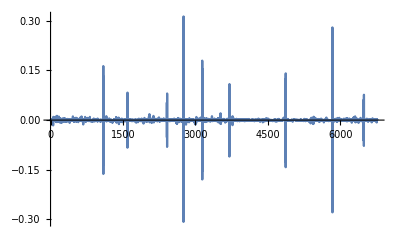

```mathematica
ListLinePlot[rsUniWeth120dFiltered, PlotRange->All]
```

```mathematica
edistUniWeth120dFiltered = EstimatedDistribution[rsUniWeth120dFiltered, StableDistribution[1, aUW120d, bUW120d, locUW120d, scaleUW120d]]
```

StableDistribution[1,1.28413,0.00661751,-0.0000924243,0.000844373]

```mathematica
twapsUniWeth120dFiltered1HourCandle = Table[twapsUniWeth120dFiltered[[i]], {i, 1, Length[twapsUniWeth120dFiltered], 6}]
```

{1.47173×10^16,1.4693×10^16,1.46469×10^16,1.43748×10^16,1.40033×10^16,1.40449×10^16,1.38472×10^16,1.38869×10^16,1.38774×10^16,1.35037×10^16,1.3682×10^16,1.36374×10^16,1.35337×10^16,1.36976×10^16,1.36601×10^16,1.3917×10^16,1.38837×10^16,1.38345×10^16,1.38449×10^16,1.40505×10^16,1.36956×10^16,1.35065×10^16,1.38932×10^16,1.45196×10^16,1.466×10^16,1.45299×10^16,1.43982×10^16,1.43212×10^16,1.42318×10^16,1.47221×10^16,1.49834×10^16,1.51981×10^16,1.49003×10^16,1.48635×10^16,1.51757×10^16,1.52058×10^16,1.48131×10^16,1.46801×10^16,1.43487×10^16,1.42228×10^16,1.39406×10^16,1.39542×10^16,1.40742×10^16,1.42533×10^16,1.44072×10^16,1.42455×10^16,1.41036×10^16,1.42542×10^16,1.44249×10^16,1.44542×10^16,1.4613×10^16,1.43907×10^16,1.41802×10^16,1.41657×10^16,1.39068×10^16,1.38949×10^16,1.37714×10^16,1.38673×10^16,1.398×10^16,1.37909×10^16,1.38676×10^16,1.39378×10^16,1.39108×10^16,1.40153×10^16,1.40463×10^16,1.40547×10^16,1.39936×10^16,1.38487×10^16,1.3741×10^16,1.36928×10^16,1.35974×10^16,1.36185×10^16,1.36479×10^16,1.37465×10^16,1.38294×10^16,1.38631×10^16,1.38408×10^16,1.4087×10^16,1.4509×10^16,1.45332×10^16,1.47338×10^16,1.46644×10^16,1.46307×10^16,1.46623×10^16,1.43935×10^16,1.45323×10^16,1.44951×10^16,1.45333×10^16,1.48334×10^16,1.46492×10^16,1.44315×10^16,1.4361×10^16,1.46602×10^16,1.45342×10^16,1.44985×10^16,1.45966×10^16,1.4303×10^16,1.43335×10^16,1.4311×10^16,1.42211×10^16,1.43928×10^16,1.45161×10^16,1.48971×10^16,1.50989×10^16,1.50077×10^16,1.5048×10^16,1.51143×10^16,1.54733×10^16,1.57624×10^16,1.55814×10^16,1.56392×10^16,1.57578×10^16,1.54617×10^16,1.51004×10^16,1.49264×10^16,1.48372×10^16,1.49064×10^16,1.49641×10^16,1.50069×10^16,1.5118×10^16,1.54348×10^16,1.53183×10^16,1.51531×10^16,1.49669×10^16,1.49442×10^16,1.5144×10^16,1.5109×10^16,1.51772×10^16,1.55007×10^16,1.5568×10^16,1.55353×10^16,1.56657×10^16,1.55756×10^16,1.54927×10^16,1.54111×10^16,1.54372×10^16,1.58355×10^16,1.58304×10^16,1.58508×10^16,1.56725×10^16,1.56905×10^16,1.54917×10^16,1.54598×10^16,1.53153×10^16,1.52804×10^16,1.51045×10^16,1.49524×10^16,1.47894×10^16,1.47805×10^16,1.4889×10^16,1.50384×10^16,1.5025×10^16,1.4911×10^16,1.47476×10^16,1.46494×10^16,1.46727×10^16,1.47677×10^16,1.4718×10^16,1.474×10^16,1.46977×10^16,1.45988×10^16,1.46679×10^16,1.45061×10^16,1.45261×10^16,1.4585×10^16,1.46362×10^16,1.46138×10^16,1.46088×10^16,1.46056×10^16,1.45213×10^16,1.44013×10^16,1.43942×10^16,1.43027×10^16,1.42072×10^16,1.40715×10^16,1.39924×10^16,1.39405×10^16,1.39718×10^16,1.39171×10^16,1.38053×10^16,1.37077×10^16,1.37026×10^16,1.36646×10^16,1.19101×10^16,1.35535×10^16,1.35975×10^16,1.36341×10^16,1.36204×10^16,1.3673×10^16,1.36949×10^16,1.37106×10^16,1.38937×10^16,1.39935×10^16,1.46003×10^16,1.44251×10^16,1.4534×10^16,1.44585×10^16,1.44377×10^16,1.44517×10^16,1.44127×10^16,1.43354×10^16,1.44534×10^16,1.43872×10^16,1.46269×10^16,1.46525×10^16,1.44969×10^16,1.43657×10^16,1.41447×10^16,1.39299×10^16,1.38926×10^16,1.382×10^16,1.37793×10^16,1.366×10^16,1.34048×10^16,1.30653×10^16,1.27759×10^16,1.2638×10^16,1.24818×10^16,1.237×10^16,1.23714×10^16,1.24633×10^16,1.25081×10^16,1.24171×10^16,1.23882×10^16,1.24476×10^16,1.24333×10^16,1.2274×10^16,1.27471×10^16,1.23891×10^16,1.25081×10^16,1.26116×10^16,1.26615×10^16,1.26891×10^16,1.28067×10^16,1.31064×10^16,1.33474×10^16,1.30522×10^16,1.29564×10^16,1.30418×10^16,1.30461×10^16,1.30848×10^16,1.31534×10^16,1.30482×10^16,1.29744×10^16,1.29321×10^16,1.28576×10^16,1.30236×10^16,1.28814×10^16,1.2562×10^16,1.26645×10^16,1.24347×10^16,1.23341×10^16,1.22056×10^16,1.20252×10^16,1.20162×10^16,1.19961×10^16,1.20588×10^16,1.20996×10^16,1.21693×10^16,1.21084×10^16,1.21759×10^16,1.20484×10^16,1.19467×10^16,1.19051×10^16,1.17518×10^16,1.16407×10^16,1.1642×10^16,1.16533×10^16,1.16594×10^16,1.15792×10^16,1.14592×10^16,1.14485×10^16,1.14178×10^16,1.13954×10^16,1.14663×10^16,1.15707×10^16,1.16709×10^16,1.16686×10^16,1.16995×10^16,1.16843×10^16,1.16748×10^16,1.15373×10^16,1.15035×10^16,1.14954×10^16,1.145×10^16,1.14155×10^16,1.13662×10^16,1.1315×10^16,1.1357×10^16,1.13287×10^16,1.12795×10^16,1.12115×10^16,1.12515×10^16,1.12208×10^16,1.09993×10^16,1.10353×10^16,1.07602×10^16,1.07018×10^16,1.05469×10^16,1.04034×10^16,1.04196×10^16,1.03714×10^16,1.01715×10^16,1.00438×10^16,1.00125×10^16,1.01433×10^16,1.01531×10^16,1.01818×10^16,1.01877×10^16,1.01671×10^16,1.00336×10^16,1.00385×10^16,1.00346×10^16,1.00403×10^16,1.0099×10^16,1.0193×10^16,1.0128×10^16,1.00215×10^16,9.914×10^15,9.78522×10^15,9.76249×10^15,9.56944×10^15,9.51435×10^15,9.33872×10^15,9.15182×10^15,9.27452×10^15,9.20575×10^15,9.23172×10^15,9.35322×10^15,9.36431×10^15,9.31467×10^15,9.34362×10^15,9.34365×10^15,9.29341×10^15,9.29754×10^15,9.2498×10^15,9.21057×10^15,9.21306×10^15,9.3271×10^15,9.34421×10^15,9.58157×10^15,9.68532×10^15,1.00054×10^16,9.84306×10^15,9.86214×10^15,9.85295×10^15,9.97194×10^15,1.0006×10^16,1.00046×10^16,9.93023×10^15,9.65536×10^15,9.68697×10^15,9.73155×10^15,9.93156×10^15,9.96341×10^15,1.0008×10^16,1.02765×10^16,1.00119×10^16,9.89287×10^15,9.94419×10^15,9.92122×10^15,9.98088×10^15,9.95708×10^15,9.93485×10^15,1.0009×10^16,9.98467×10^15,9.989×10^15,9.9578×10^15,9.86546×10^15,9.73455×10^15,9.82722×10^15,9.79832×10^15,9.79223×10^15,9.87357×10^15,1.00456×10^16,1.0299×10^16,1.0307×10^16,1.01465×10^16,1.01151×10^16,1.00867×10^16,1.00058×10^16,9.98654×10^15,1.01141×10^16,1.00806×10^16,1.00245×10^16,9.99389×10^15,9.99841×10^15,9.93624×10^15,9.96355×10^15,9.95628×10^15,9.96722×10^15,1.01549×10^16,1.02264×10^16,1.02008×10^16,1.02355×10^16,1.02006×10^16,1.02127×10^16,1.02105×10^16,1.02496×10^16,1.0319×10^16,1.02337×10^16,1.02228×10^16,1.0229×10^16,1.02005×10^16,1.0166×10^16,1.01577×10^16,1.00764×10^16,1.00092×10^16,1.00636×10^16,1.0108×10^16,1.01669×10^16,1.01754×10^16,1.01258×10^16,1.01423×10^16,1.0193×10^16,1.0158×10^16,1.01949×10^16,1.01836×10^16,1.0174×10^16,1.02712×10^16,1.02798×10^16,1.02814×10^16,1.02345×10^16,1.02686×10^16,1.03576×10^16,1.03299×10^16,1.02506×10^16,1.03684×10^16,1.03651×10^16,1.03628×10^16,1.02735×10^16,1.0312×10^16,1.02233×10^16,1.02471×10^16,1.02428×10^16,1.01491×10^16,9.94124×10^15,9.54085×10^15,9.61753×10^15,9.48064×10^15,9.57369×10^15,9.7507×10^15,9.84092×10^15,9.76248×10^15,9.63198×10^15,9.49568×10^15,9.58109×10^15,9.61753×10^15,9.59591×10^15,9.66941×10^15,9.69431×10^15,9.6835×10^15,9.63121×10^15,9.54082×10^15,9.4644×10^15,9.45946×10^15,9.45207×10^15,9.41065×10^15,9.4068×10^15,6.95814×10^15,9.47512×10^15,9.52407×10^15,9.54155×10^15,9.49288×10^15,9.55225×10^15,9.54645×10^15,9.51215×10^15,9.52019×10^15,9.14426×10^15,8.95673×10^15,9.00261×10^15,8.9959×10^15,8.93583×10^15,9.00053×10^15,8.99238×10^15,8.97661×10^15,9.0051×10^15,8.89641×10^15,8.78412×10^15,8.74131×10^15,8.81743×10^15,8.77753×10^15,8.82253×10^15,8.82822×10^15,8.85415×10^15,8.87584×10^15,8.87939×10^15,8.89407×10^15,8.89122×10^15,8.90429×10^15,8.89055×10^15,8.88963×10^15,8.91674×10^15,8.89876×10^15,8.92203×10^15,8.94477×10^15,8.87555×10^15,8.71841×10^15,8.44827×10^15,8.35427×10^15,8.17023×10^15,7.76162×10^15,7.78562×10^15,7.69374×10^15,7.92898×10^15,7.83174×10^15,7.8155×10^15,7.92531×10^15,8.03862×10^15,8.01859×10^15,7.98459×10^15,8.09221×10^15,8.12291×10^15,8.19817×10^15,8.22728×10^15,8.3486×10^15,8.4327×10^15,8.43866×10^15,8.54634×10^15,8.71654×10^15,8.6784×10^15,8.81024×10^15,8.98927×10^15,9.31187×10^15,9.35048×10^15,9.35743×10^15,9.33616×10^15,9.34642×10^15,9.54368×10^15,9.49361×10^15,9.40741×10^15,9.33175×10^15,9.3762×10^15,9.55794×10^15,9.44535×10^15,9.26234×10^15,9.13831×10^15,9.09453×10^15,9.11859×10^15,9.2764×10^15,9.36901×10^15,9.42751×10^15,9.37123×10^15,9.39548×10^15,9.31588×10^15,9.39767×10^15,9.45744×10^15,9.49359×10^15,9.48679×10^15,9.55813×10^15,9.48282×10^15,9.48253×10^15,9.50055×10^15,9.42691×10^15,9.48875×10^15,9.54754×10^15,9.52335×10^15,9.63439×10^15,1.01086×10^16,1.01007×10^16,9.9933×10^15,9.94493×10^15,9.91762×10^15,1.00343×10^16,1.00751×10^16,1.01438×10^16,1.0341×10^16,1.03251×10^16,1.02856×10^16,1.03636×10^16,1.04773×10^16,1.04418×10^16,1.04676×10^16,1.03545×10^16,1.0313×10^16,1.03988×10^16,1.0374×10^16,1.03804×10^16,1.0526×10^16,1.07025×10^16,1.04763×10^16,1.03799×10^16,1.03562×10^16,1.04174×10^16,1.03788×10^16,1.04284×10^16,1.0355×10^16,1.0582×10^16,1.07375×10^16,1.08411×10^16,1.08358×10^16,1.08144×10^16,1.06964×10^16,1.06799×10^16,1.07259×10^16,1.0718×10^16,1.0689×10^16,1.06501×10^16,1.07303×10^16,1.06942×10^16,1.0595×10^16,1.05994×10^16,1.05384×10^16,1.02239×10^16,1.01052×10^16,1.00466×10^16,9.91415×10^15,9.89614×10^15,9.96089×10^15,1.00419×10^16,1.00996×10^16,9.98001×10^15,9.99502×10^15,1.00831×10^16,1.0197×10^16,1.03428×10^16,1.03244×10^16,1.03293×10^16,1.03567×10^16,1.03512×10^16,1.03285×10^16,1.04514×10^16,1.05501×10^16,1.0715×10^16,1.07913×10^16,1.0795×10^16,1.0763×10^16,1.0656×10^16,1.04223×10^16,1.03761×10^16,1.03524×10^16,1.0388×10^16,1.04386×10^16,1.0457×10^16,1.04204×10^16,1.03495×10^16,1.03035×10^16,1.03732×10^16,1.04384×10^16,1.04561×10^16,1.03969×10^16,1.03443×10^16,1.03767×10^16,1.04644×10^16,1.04509×10^16,1.03689×10^16,1.02921×10^16,1.03107×10^16,1.03595×10^16,1.03984×10^16,1.03664×10^16,1.03295×10^16,1.0299×10^16,1.01805×10^16,1.02285×10^16,1.02418×10^16,1.02635×10^16,1.02444×10^16,1.01634×10^16,1.02×10^16,1.01845×10^16,1.0135×10^16,1.01347×10^16,1.01562×10^16,1.01242×10^16,1.01116×10^16,1.01385×10^16,1.01659×10^16,1.00864×10^16,1.00331×10^16,1.00939×10^16,1.00321×10^16,1.00331×10^16,9.9728×10^15,9.99438×10^15,9.95601×10^15,9.90624×10^15,9.86681×10^15,9.88682×10^15,9.91453×10^15,9.86033×10^15,9.84211×10^15,9.83074×10^15,9.85828×10^15,9.9164×10^15,9.85481×10^15,9.86116×10^15,9.85004×10^15,9.81399×10^15,9.82887×10^15,9.81844×10^15,9.81619×10^15,9.77846×10^15,9.79108×10^15,9.7922×10^15,9.73953×10^15,9.70259×10^15,9.76963×10^15,9.84043×10^15,9.79943×10^15,9.76594×10^15,9.73034×10^15,9.7524×10^15,9.70911×10^15,9.59549×10^15,9.52851×10^15,9.53481×10^15,9.56108×10^15,9.55702×10^15,9.55222×10^15,9.57054×10^15,9.54634×10^15,9.51276×10^15,9.49011×10^15,9.54397×10^15,9.51662×10^15,9.48675×10^15,9.45274×10^15,9.60053×10^15,9.63225×10^15,9.64456×10^15,9.64757×10^15,9.66278×10^15,9.57243×10^15,9.41723×10^15,9.3345×10^15,9.3401×10^15,9.3026×10^15,9.30949×10^15,9.31619×10^15,9.31707×10^15,9.28229×10^15,9.2335×10^15,9.08571×10^15,9.15127×10^15,9.19743×10^15,9.28804×10^15,9.33623×10^15,9.32923×10^15,9.22683×10^15,9.24602×10^15,9.28134×10^15,9.39159×10^15,9.35169×10^15,9.40093×10^15,9.47355×10^15,9.50759×10^15,9.50354×10^15,9.46285×10^15,9.44905×10^15,9.48002×10^15,9.62192×10^15,9.64757×10^15,9.60739×10^15,9.57404×10^15,9.5623×10^15,9.56627×10^15,9.5598×10^15,9.57718×10^15,9.57148×10^15,9.56176×10^15,9.54694×10^15,9.55064×10^15,9.5454×10^15,9.52381×10^15,9.52575×10^15,9.49515×10^15,9.46314×10^15,9.39309×10^15,9.38743×10^15,9.31735×10^15,9.3067×10^15,9.29826×10^15,9.35401×10^15,9.28408×10^15,9.26122×10^15,9.20588×10^15,9.2759×10^15,9.2492×10^15,9.14891×10^15,9.08403×10^15,9.01868×10^15,8.90018×10^15,8.915×10^15,8.8813×10^15,8.92053×10^15,8.91823×10^15,8.91392×10^15,8.97735×10^15,8.99762×10^15,9.01128×10^15,9.00488×10^15,9.00133×10^15,8.99179×10^15,8.98758×10^15,8.94082×10^15,8.90815×10^15,8.87666×10^15,8.85116×10^15,8.82647×10^15,8.8169×10^15,8.80756×10^15,8.91339×10^15,8.99651×10^15,9.0369×10^15,9.1233×10^15,9.25647×10^15,9.26609×10^15,9.24664×10^15,9.18889×10^15,9.20199×10^15,9.20047×10^15,9.16721×10^15,9.16156×10^15,9.21761×10^15,9.27175×10^15,9.25217×10^15,9.31896×10^15,9.29881×10^15,9.28326×10^15,9.2937×10^15,9.34589×10^15,9.33342×10^15,9.33072×10^15,9.3137×10^15,9.29153×10^15,9.26441×10^15,9.24654×10^15,9.23099×10^15,9.21772×10^15,9.22432×10^15,9.20814×10^15,9.17005×10^15,9.1996×10^15,9.21388×10^15,9.22207×10^15,9.11933×10^15,9.07432×10^15,9.09752×10^15,9.12113×10^15,9.15375×10^15,9.19429×10^15,9.25959×10^15,9.27409×10^15,9.30885×10^15,9.31881×10^15,9.30958×10^15,9.3128×10^15,9.30311×10^15,9.28705×10^15,9.28462×10^15,9.32352×10^15,9.29384×10^15,9.24987×10^15,9.26686×10^15,9.25693×10^15,9.23481×10^15,9.23752×10^15,9.16281×10^15,9.16549×10^15,9.15307×10^15,9.13819×10^15,9.13646×10^15,9.17695×10^15,9.16089×10^15,9.17166×10^15,9.1957×10^15,9.20057×10^15,9.21495×10^15,9.19045×10^15,9.18469×10^15,9.18808×10^15,9.17009×10^15,9.14766×10^15,9.05861×10^15,9.05047×10^15,9.13082×10^15,9.14851×10^15,9.16075×10^15,9.18834×10^15,9.15408×10^15,9.14182×10^15,9.18998×10^15,9.2025×10^15,9.20602×10^15,9.22869×10^15,9.25889×10^15,9.22074×10^15,9.22775×10^15,9.17968×10^15,9.13959×10^15,9.10109×10^15,9.02297×10^15,8.90071×10^15,8.80758×10^15,8.72826×10^15,8.76308×10^15,8.73393×10^15,8.45747×10^15,8.33382×10^15,8.37118×10^15,8.54613×10^15,8.52789×10^15,8.47576×10^15,8.43701×10^15,8.24261×10^15,8.1963×10^15,8.03588×10^15,8.17354×10^15,8.48533×10^15,8.6964×10^15,8.758×10^15,8.74107×10^15,8.71402×10^15,8.84078×10^15,8.99255×10^15,8.94851×10^15,8.91867×10^15,8.93575×10^15,8.91798×10^15,8.97674×10^15,9.02847×10^15,9.02278×10^15,8.97737×10^15,8.96277×10^15,8.97101×10^15,9.00621×10^15,9.02872×10^15,8.9274×10^15,8.82154×10^15,8.82261×10^15,8.86172×10^15,8.88748×10^15,8.87679×10^15,9.00343×10^15,9.07451×10^15,9.09239×10^15,9.11138×10^15,9.08485×10^15,9.04678×10^15,9.02664×10^15,8.99354×10^15,8.93362×10^15,8.90562×10^15,8.78731×10^15,8.7788×10^15,8.7857×10^15,8.77331×10^15,8.80495×10^15,8.82745×10^15,8.87606×10^15,8.8228×10^15,8.8485×10^15,8.96874×10^15,8.94886×10^15,8.94376×10^15,8.91991×10^15,8.87617×10^15,8.87357×10^15,8.84645×10^15,8.86086×10^15,8.78748×10^15,8.78137×10^15,8.72838×10^15,8.72353×10^15,8.67002×10^15,8.64458×10^15,8.61508×10^15,8.61698×10^15,8.61571×10^15,8.56278×10^15,8.46237×10^15,8.45014×10^15,1.11587×10^16,8.47205×10^15,8.5734×10^15,8.58127×10^15,8.5555×10^15,8.56662×10^15,8.65539×10^15,8.63451×10^15,8.52647×10^15,8.49714×10^15,8.50536×10^15,8.57192×10^15,8.57529×10^15,8.54093×10^15,8.47923×10^15,8.45105×10^15,8.31936×10^15,8.1622×10^15,8.2897×10^15,8.46026×10^15,8.42457×10^15,8.44044×10^15,8.48173×10^15,8.46936×10^15,8.57108×10^15,8.52739×10^15,8.49332×10^15,8.48059×10^15,8.46642×10^15,8.43774×10^15,8.43821×10^15,8.43117×10^15,8.46769×10^15,8.42856×10^15,8.42505×10^15,8.42546×10^15,8.42442×10^15,8.40294×10^15,8.40641×10^15,8.412×10^15,8.51966×10^15,8.52686×10^15,8.51921×10^15,8.49635×10^15,8.4949×10^15,8.51167×10^15,8.56438×10^15,8.60262×10^15,8.68525×10^15,8.68823×10^15,8.7078×10^15,8.86778×10^15,8.93189×10^15,8.94952×10^15,8.92733×10^15,8.91459×10^15,8.89331×10^15,8.92832×10^15,8.96478×10^15,9.03825×10^15,8.99365×10^15,8.98051×10^15,8.96761×10^15,8.99462×10^15,8.93814×10^15,8.91908×10^15,8.93137×10^15,8.78171×10^15,8.8046×10^15,8.87823×10^15,8.98548×10^15,9.03913×10^15,9.12878×10^15,9.30894×10^15,9.56108×10^15,9.56635×10^15,9.60335×10^15,9.60339×10^15,9.747×10^15,9.90256×10^15,9.66938×10^15,9.61926×10^15,9.49395×10^15,9.53663×10^15,9.66066×10^15,9.7266×10^15,9.6478×10^15,9.64925×10^15,9.65327×10^15,9.65912×10^15,9.53254×10^15,9.4077×10^15,9.38663×10^15,9.4785×10^15,9.51756×10^15,9.58006×10^15,9.61507×10^15,9.64415×10^15,9.74695×10^15,9.75722×10^15,9.76583×10^15,9.82743×10^15,9.75531×10^15,9.79233×10^15,9.80812×10^15,9.78796×10^15,9.71307×10^15,9.73479×10^15,9.7341×10^15,9.70728×10^15,9.64134×10^15,9.59543×10^15,9.60118×10^15,9.62379×10^15,9.6061×10^15,9.61308×10^15,9.61524×10^15,9.61862×10^15,9.60567×10^15,9.71896×10^15,9.77675×10^15,9.84373×10^15,9.82929×10^15,9.69883×10^15,9.68502×10^15,9.59595×10^15,9.57471×10^15,9.58398×10^15,9.59877×10^15,9.5749×10^15,9.50344×10^15,9.50806×10^15,9.48639×10^15,9.46636×10^15,9.46479×10^15,9.38896×10^15,9.13287×10^15,9.00334×10^15,8.91095×10^15,9.02465×10^15,8.99144×10^15,8.98756×10^15,8.95606×10^15,9.01714×10^15,8.97892×10^15,8.99035×10^15,8.96735×10^15,9.01742×10^15,8.98675×10^15,8.94527×10^15,8.88258×10^15,8.91781×10^15,8.84368×10^15,8.67263×10^15,8.70708×10^15,8.75789×10^15}

```mathematica
Length[twapsUniWeth120dFiltered1HourCandle]
```

1129

```mathematica
ListLinePlot[twapsUniWeth120dFiltered1HourCandle, PlotRange->All]
```

-Graphics-

```mathematica
rsUniWeth120dFiltered1HourCandle = Differences[Log[twapsUniWeth120dFiltered1HourCandle ]]
```

{-0.00164689,-0.00314585,-0.018749,-0.0261826,0.00296687,-0.0141804,0.0028644,-0.00068863,-0.0272957,0.0131172,-0.00326691,-0.00763258,0.0120404,-0.00273812,0.0186286,-0.00239637,-0.00354864,0.000752604,0.0147379,-0.0255852,-0.0138992,0.0282267,0.0441,0.00962452,-0.00891291,-0.00910471,-0.00536651,-0.00626198,0.0338695,0.0175948,0.0142269,-0.0197868,-0.00247271,0.0207855,0.00198185,-0.0261621,-0.00902233,-0.022835,-0.0088099,-0.020042,0.000975244,0.00856094,0.0126446,0.0107438,-0.0112883,-0.0100128,0.0106199,0.0119052,0.0020326,0.0109281,-0.0153302,-0.0147364,-0.00102594,-0.0184447,-0.000855064,-0.00893158,0.00694576,0.00809354,-0.0136222,0.00554901,0.00504766,-0.00193811,0.00748163,0.00221262,0.0005997,-0.00436351,-0.0104067,-0.00780666,-0.00351585,-0.00698726,0.00154983,0.00215743,0.00719503,0.00601236,0.00243582,-0.00161275,0.0176356,0.0295182,0.00166278,0.0137081,-0.00472114,-0.00230219,0.00215797,-0.0185033,0.00960191,-0.0025648,0.00262955,0.0204401,-0.0124946,-0.0149708,-0.00489913,0.0206194,-0.00862906,-0.00246024,0.00674103,-0.0203185,0.00213299,-0.00157012,-0.00630597,0.0120059,0.00852359,0.0259119,0.0134552,-0.00605967,0.00268414,0.00439251,0.0234741,0.0185171,-0.0115543,0.00370173,0.00755886,-0.0189689,-0.0236463,-0.0115872,-0.00599439,0.0046519,0.0038619,0.00285361,0.00738042,0.0207372,-0.00757951,-0.0108391,-0.0123663,-0.00151746,0.0132813,-0.00231519,0.00450418,0.0210944,0.00433115,-0.00210605,0.00836165,-0.00576747,-0.00533548,-0.00528404,0.00169163,0.0254755,-0.000322042,0.00128733,-0.0113107,0.00114632,-0.0127525,-0.00205625,-0.00939567,-0.00227836,-0.0115767,-0.0101228,-0.0109613,-0.000605166,0.00731787,0.00998297,-0.000893925,-0.00761403,-0.0110178,-0.00668373,0.00159054,0.00645379,-0.00336962,0.00149149,-0.00287195,-0.00675158,0.00472104,-0.0110942,0.00137928,0.00404749,0.003505,-0.00153277,-0.000345515,-0.000218632,-0.00578635,-0.00829774,-0.000492325,-0.0063808,-0.00669384,-0.00959942,-0.00563696,-0.00371364,0.00223789,-0.00392195,-0.00806348,-0.00709583,-0.000372428,-0.00277784,-0.13742,0.129256,0.0032436,0.00268832,-0.00100375,0.00385356,0.00159754,0.00114888,0.0132654,0.00715891,0.042444,-0.0120728,0.00752197,-0.0052076,-0.00143485,0.000964644,-0.00270299,-0.00537799,0.00819668,-0.00458785,0.0165214,0.00175003,-0.0106779,-0.00908589,-0.0155072,-0.0153034,-0.00267876,-0.00523819,-0.002948,-0.00870205,-0.0188559,-0.0256561,-0.0223959,-0.0108552,-0.0124366,-0.00899156,0.000105986,0.00740299,0.00359374,-0.00730877,-0.00233108,0.00478719,-0.00114926,-0.0128937,0.0378178,-0.0284876,0.00956284,0.00824292,0.00394759,0.00217268,0.00922525,0.0231359,0.0182229,-0.0223707,-0.00736087,0.00656666,0.000327603,0.00296415,0.00522461,-0.00802482,-0.00567154,-0.00326769,-0.00577584,0.0128244,-0.0109748,-0.0251073,0.00812592,-0.0183131,-0.00812089,-0.0104756,-0.0148916,-0.000751529,-0.00167082,0.00521596,0.00337541,0.00574768,-0.00501779,0.00555669,-0.010528,-0.00848005,-0.00348485,-0.0129623,-0.00949604,0.000107593,0.000970535,0.000523687,-0.00690203,-0.010413,-0.000937229,-0.00268242,-0.0019671,0.00620279,0.00906102,0.00862656,-0.000195704,0.00264324,-0.00129861,-0.000813554,-0.0118496,-0.00292932,-0.000711898,-0.00395436,-0.00301427,-0.00433047,-0.00451146,0.00370351,-0.00250006,-0.00435228,-0.00604714,0.00356921,-0.00273312,-0.0199422,0.0032724,-0.025248,-0.00544308,-0.0145823,-0.0137,0.00156007,-0.00464132,-0.0194584,-0.0126359,-0.00312038,0.0129771,0.000964758,0.00282775,0.000576861,-0.00202719,-0.0132174,0.000493099,-0.000389881,0.000572451,0.00582785,0.00925941,-0.00639577,-0.0105693,-0.0107852,-0.0130746,-0.0023254,-0.019973,-0.0057736,-0.0186317,-0.020217,0.0133177,-0.00744221,0.00281727,0.0130754,0.00118533,-0.00531534,0.00310278,2.92336×10^-6,-0.00539061,0.000443754,-0.00514723,-0.00425019,0.000269966,0.012302,0.001833,0.0250842,0.0107704,0.0325093,-0.0163545,0.00193631,-0.00093228,0.012004,0.00340745,-0.000138207,-0.00746022,-0.0280701,0.00326806,0.00459154,0.0203448,0.00320172,0.00446615,0.0264786,-0.026086,-0.0119643,0.00517382,-0.00231248,0.0059953,-0.00238727,-0.00223491,0.00743939,-0.00243699,0.00043329,-0.00312834,-0.00931582,-0.0133587,0.00947438,-0.00294448,-0.000622654,0.00827303,0.0172708,0.0249186,0.000773144,-0.0156964,-0.00309635,-0.002818,-0.00804477,-0.00193084,0.0126915,-0.00331324,-0.00558472,-0.0030579,0.000452652,-0.00623736,0.00274417,-0.000729729,0.0010982,0.0186559,0.00701352,-0.0025013,0.00338953,-0.00341512,0.00119166,-0.000221708,0.00382673,0.00674767,-0.00830506,-0.00106401,0.000608951,-0.00279018,-0.00339074,-0.00081959,-0.00802925,-0.00669293,0.00542063,0.00439621,0.00581008,0.000839077,-0.00488313,0.00162671,0.00498881,-0.00344637,0.0036263,-0.00110193,-0.000949498,0.00950779,0.000838544,0.00016244,-0.00457873,0.00333241,0.008621,-0.00266894,-0.00771207,0.0114284,-0.000319785,-0.000220846,-0.0086507,0.003738,-0.00864048,0.00232857,-0.000422754,-0.00919454,-0.0206893,-0.0411086,0.0080041,-0.0143357,0.00976727,0.01832,0.00921099,-0.00800359,-0.0134573,-0.0142514,0.00895451,0.00379577,-0.00225099,0.00763041,0.00257184,-0.00111585,-0.00541391,-0.00942933,-0.00804245,-0.00052243,-0.000781322,-0.00439126,-0.000409885,-0.30152,0.308757,0.00515263,0.00183389,-0.00511378,0.00623472,-0.000607885,-0.00359954,0.000844877,-0.0402885,-0.020721,0.00510938,-0.000745169,-0.00670055,0.00721424,-0.000904919,-0.0017556,0.00316903,-0.0121438,-0.0127016,-0.0048858,0.00866972,-0.00453479,0.00511372,0.00064404,0.00293304,0.00244653,0.000400672,0.00165112,-0.000320393,0.00146927,-0.00154408,-0.000103416,0.00304504,-0.00201869,0.00261167,0.00254506,-0.00776818,-0.0178639,-0.0314751,-0.0111888,-0.0222754,-0.0513067,0.00308731,-0.0118713,0.0301176,-0.01234,-0.0020756,0.013953,0.0141962,-0.00249458,-0.00424966,0.0133881,0.00378629,0.00922292,0.00354508,0.0146385,0.0100226,0.000706096,0.0126795,0.0197202,-0.00438606,0.0150782,0.0201163,0.0352587,0.00413748,0.000743718,-0.00227559,0.00109802,0.0208857,-0.0052604,-0.00912073,-0.00807514,0.00475183,0.0191977,-0.0118498,-0.0195657,-0.0134812,-0.00480271,0.00264203,0.0171578,0.0099341,0.00622471,-0.00598797,0.00258539,-0.00850913,0.00874205,0.00634004,0.0038141,-0.000716338,0.00749231,-0.0079104,-0.0000308849,0.00189884,-0.0077815,0.00653899,0.0061765,-0.00253767,0.0115927,0.048044,-0.000776992,-0.0106913,-0.00485162,-0.00275041,0.0117009,0.00405475,0.0067929,0.0192538,-0.00154145,-0.00382406,0.00754611,0.0109144,-0.00339315,0.00247152,-0.0108667,-0.00401639,0.00828574,-0.00239248,0.000619396,0.0139285,0.0166283,-0.0213635,-0.00924339,-0.00228251,0.00588818,-0.00371273,0.00477434,-0.00706417,0.0216853,0.0145878,0.00960398,-0.000495371,-0.00197785,-0.0109649,-0.00154395,0.00429491,-0.0007359,-0.00270981,-0.00364863,0.0075092,-0.00337081,-0.00932207,0.000411902,-0.00576521,-0.0303059,-0.0116703,-0.00582368,-0.013267,-0.00181831,0.00652212,0.00810074,0.00572849,-0.011912,0.00150296,0.00877214,0.0112381,0.0141961,-0.00178356,0.000473048,0.00265404,-0.000538319,-0.00219368,0.0118332,0.00939543,0.0155094,0.00709613,0.000346063,-0.00296663,-0.00999211,-0.0221793,-0.00443723,-0.00228971,0.00343492,0.00485497,0.00175867,-0.00349847,-0.00682876,-0.00445392,0.00674146,0.00626053,0.00169768,-0.00568389,-0.0050633,0.00312647,0.00841282,-0.00129474,-0.0078754,-0.00743085,0.00180298,0.00472252,0.00375028,-0.00308874,-0.00355683,-0.00296364,-0.0115719,0.00470554,0.00130178,0.00211457,-0.0018674,-0.007934,0.00359122,-0.00151833,-0.00487125,-0.0000273301,0.00211539,-0.00315551,-0.00124869,0.00266316,0.0026938,-0.00784602,-0.00530421,0.00605086,-0.00614724,0.000105003,-0.0060327,0.00216194,-0.00384658,-0.0050113,-0.00398843,0.00202596,0.00279835,-0.00548195,-0.00184937,-0.00115524,0.00279666,0.00587831,-0.0062301,0.000643996,-0.00112772,-0.00366709,0.00151499,-0.0010619,-0.000228797,-0.00385103,0.00128999,0.000113961,-0.00539333,-0.00379996,0.0068864,0.00722041,-0.00417568,-0.0034225,-0.0036527,0.00226533,-0.00444934,-0.0117718,-0.00700481,0.000661249,0.00275128,-0.000424134,-0.000502876,0.00191627,-0.00253151,-0.00352371,-0.00238482,0.00565943,-0.0028694,-0.00314383,-0.0035918,0.0155139,0.00329901,0.00127659,0.000312121,0.00157605,-0.0093946,-0.0163466,-0.00882291,0.000599265,-0.00402273,0.000740474,0.000718479,0.0000947894,-0.00373921,-0.00527071,-0.0161349,0.00718903,0.00503153,0.00980408,0.0051746,-0.000750092,-0.0110371,0.00207828,0.00381296,0.0118082,-0.00425721,0.00525076,0.0076955,0.00358638,-0.000425921,-0.00429053,-0.00145938,0.00327258,0.0148567,0.00266199,-0.00417296,-0.00347732,-0.00122701,0.000415062,-0.00067674,0.00181622,-0.000594709,-0.00101654,-0.00155097,0.000387069,-0.000548354,-0.00226412,0.000203553,-0.00321744,-0.00337688,-0.0074299,-0.000603043,-0.00749349,-0.0011437,-0.000907536,0.00597797,-0.00750355,-0.00246552,-0.00599352,0.00757727,-0.00288247,-0.0109026,-0.00711637,-0.00722027,-0.0132262,0.00166334,-0.00378659,0.00440665,-0.000257421,-0.000483825,0.00709103,0.00225551,0.00151723,-0.000710674,-0.000394541,-0.00106045,-0.000468116,-0.00521664,-0.00366088,-0.00354075,-0.0028775,-0.0027931,-0.00108467,-0.00105938,0.0119442,0.00928209,0.0044796,0.00951431,0.0144919,0.00103899,-0.00210165,-0.00626505,0.00142445,-0.000165482,-0.0036213,-0.000616833,0.00609944,0.00585638,-0.0021135,0.00719209,-0.00216372,-0.00167425,0.00112441,0.00560019,-0.00133602,-0.000288553,-0.00182648,-0.00238241,-0.00292378,-0.00193057,-0.00168315,-0.00143889,0.000716243,-0.00175605,-0.00414447,0.00321694,0.001551,0.000888187,-0.0112025,-0.00494866,0.00255375,0.00259247,0.00356991,0.00441806,0.00707725,0.0015656,0.00374076,0.0010687,-0.000990778,0.000345841,-0.00104066,-0.00172827,-0.000261112,0.00418037,-0.00318778,-0.00474279,0.00183526,-0.00107259,-0.00239144,0.000293483,-0.00812098,0.000292448,-0.00135586,-0.00162681,-0.000189679,0.00442135,-0.00175115,0.00117506,0.00261765,0.000529593,0.00156153,-0.00266227,-0.000627298,0.000369707,-0.00196012,-0.00244852,-0.00978258,-0.000899626,0.00883921,0.00193496,0.0013377,0.00300747,-0.00373633,-0.00133976,0.00525359,0.00136217,0.000382356,0.00245959,0.00326695,-0.00412876,0.00075996,-0.00522284,-0.00437705,-0.00422192,-0.00862057,-0.0136417,-0.0105183,-0.00904765,0.00398229,-0.00333194,-0.0321653,-0.0147292,0.00447306,0.0206844,-0.00213685,-0.00613203,-0.00458223,-0.0233113,-0.00563349,-0.0197664,0.0169853,0.0374372,0.0245706,0.00705757,-0.00193482,-0.00309916,0.0144422,0.0170208,-0.00490924,-0.00334035,0.00191314,-0.00199002,0.00656654,0.00574622,-0.000629672,-0.00504581,-0.00162803,0.000918935,0.00391628,0.00249594,-0.0112849,-0.0119287,0.000120856,0.00442321,0.00290255,-0.00120335,0.0141658,0.0078638,0.00196849,0.00208615,-0.00291573,-0.00419951,-0.00222842,-0.003674,-0.00668421,-0.00314001,-0.0133731,-0.000969224,0.000786133,-0.0014121,0.00360007,0.00255251,0.0054913,-0.00601814,0.00290877,0.013497,-0.00221866,-0.000570087,-0.00267124,-0.00491476,-0.000292871,-0.00306103,0.00162728,-0.0083161,-0.000695637,-0.00605242,-0.000555832,-0.00615266,-0.00293918,-0.00341852,0.000221516,-0.000147725,-0.00616307,-0.0117953,-0.00144661,0.278039,-0.275449,0.0118925,0.000917509,-0.00300818,0.00129913,0.0103092,-0.00241501,-0.012592,-0.00344556,0.000967535,0.00779483,0.000393347,-0.00401503,-0.007251,-0.00332886,-0.0157048,-0.0190718,0.0154995,0.0203664,-0.00422668,0.00188106,0.00488046,-0.00145969,0.0119392,-0.00511054,-0.00400377,-0.00149988,-0.00167232,-0.00339288,0.0000557614,-0.000835321,0.00432212,-0.00463121,-0.000416788,0.0000483757,-0.000122554,-0.00255375,0.000413473,0.000664586,0.0127176,0.000844321,-0.000898181,-0.00268661,-0.000170899,0.00197312,0.00617331,0.00445494,0.00955874,0.000343208,0.00225049,0.0182046,0.00720385,0.00197229,-0.00248324,-0.00142744,-0.00239063,0.0039298,0.00407506,0.00816225,-0.00494701,-0.00146186,-0.00143746,0.00300671,-0.00629823,-0.00213558,0.00137705,-0.0168988,0.00260364,0.0083276,0.0120078,0.00595309,0.00986962,0.0195427,0.0267254,0.000550961,0.00386007,4.26226×10^-6,0.0148442,0.0158335,-0.0238296,-0.00519663,-0.0131122,0.00448525,0.0129215,0.00680278,-0.00813465,0.000150161,0.000417057,0.000605765,-0.0131921,-0.0131822,-0.00224218,0.00973996,0.0041126,0.00654478,0.00364769,0.00301986,0.0106028,0.00105388,0.000881999,0.00628706,-0.00736512,0.00378731,0.00161094,-0.0020566,-0.00768148,0.00223388,-0.000070298,-0.00275946,-0.00681554,-0.00477374,0.000599308,0.00235215,-0.00184036,0.000726857,0.000224642,0.000351628,-0.00134736,0.0117254,0.00592776,0.00682805,-0.00146774,-0.0133618,-0.00142523,-0.00923906,-0.00221575,0.000967396,0.00154201,-0.00248932,-0.00749177,0.000486522,-0.00228187,-0.00211367,-0.000165591,-0.008045,-0.0276538,-0.0142845,-0.0103151,0.0126788,-0.00368651,-0.000431718,-0.00351122,0.0067967,-0.00424756,0.00127282,-0.00256193,0.00556782,-0.00340679,-0.00462663,-0.00703251,0.00395816,-0.00834743,-0.0195308,0.00396484,0.00581862}

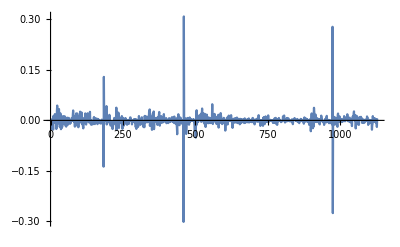

```mathematica
ListLinePlot[rsUniWeth120dFiltered1HourCandle, PlotRange->All]
```

```mathematica
edistUniWeth120dFiltered1HourCandle = EstimatedDistribution[rsUniWeth120dFiltered1HourCandle, StableDistribution[1, aUW120dC1h, bUW120dC1h, locUW120dC1h, scaleUW120dC1h]]
```

StableDistribution[1,1.44302,0.0429383,-0.000419763,0.00474788]

```mathematica
(* Compare w WETH/USDC *)
```

```mathematica
edistWethUsdc120dFiltered1HourCandle
```

StableDistribution[1,1.5843,-0.0493885,-0.000101694,0.0072772]

```mathematica
(* Interesting ... larger scale on WETH/USDC but smaller alpha. Translates to in terms of InverseCDF ? *)
```

```mathematica
InverseCDF[edistWethUsdc120dFiltered1HourCandle,0.99]
```

0.0459063

```mathematica
InverseCDF[edistWethUsdc120dFiltered1HourCandle,0.999]
```

0.183327

```mathematica
InverseCDF[edistUniWeth120dFiltered1HourCandle,0.99]
```

0.0422306

```mathematica
InverseCDF[edistUniWeth120dFiltered1HourCandle,0.999]
```

0.203319

```mathematica
(* Slight difference in alpha starts to become apparent at super extreme ends of cdf *)
```

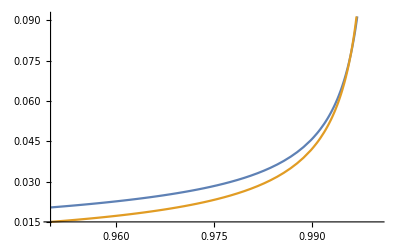

```mathematica
Plot[{InverseCDF[edistWethUsdc120dFiltered1HourCandle,q], InverseCDF[edistUniWeth120dFiltered1HourCandle,q]}, {q, 0.95, 1}]
```

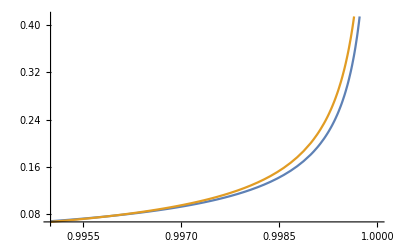

```mathematica
Plot[{InverseCDF[edistWethUsdc120dFiltered1HourCandle,q], InverseCDF[edistUniWeth120dFiltered1HourCandle,q]}, {q, 0.995, 1}]
```

```mathematica
(* What about a=1.3? *)
```

```mathematica
edistUniWeth120dFiltered1HourCandle
```

StableDistribution[1,1.44302,0.0429383,-0.000419763,0.00474788]

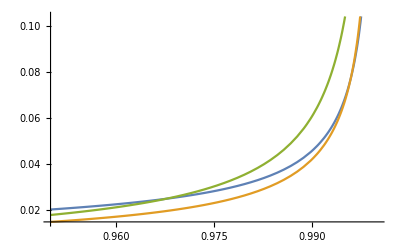

```mathematica
Plot[{InverseCDF[edistWethUsdc120dFiltered1HourCandle,q], InverseCDF[edistUniWeth120dFiltered1HourCandle,q], InverseCDF[StableDistribution[1,1.3,0.05160448032592783,-0.0005180625308600968,0.004823033038389856],q]}, {q, 0.95, 1}]
```

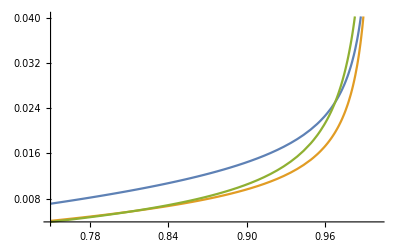

```mathematica
Plot[{InverseCDF[edistWethUsdc120dFiltered1HourCandle,q], InverseCDF[edistUniWeth120dFiltered1HourCandle,q], InverseCDF[StableDistribution[1,1.3,0.05160448032592783,-0.0005180625308600968,0.004823033038389856],q]}, {q, 0.75, 1}]
```

```mathematica
(* Yea so miscalc on a greatly changes things up, as expected. Lower a, means higher inverse CDF earlier in upper range we care about *)
```

```mathematica
(* Set up factor calcs *)
```

```mathematica
edistUniWeth120dFiltered1HourCandle
```

StableDistribution[1,1.43975,0.0516045,-0.000518063,0.00482303]

```mathematica
edistUniWeth120dFiltered1HourCandle
```

StableDistribution[1,1.44302,0.0429383,-0.000419763,0.00474788]

```mathematica
(* Looking goood ... *)
```

```mathematica
muUniWeth120dFiltered1HourCandle = mu[1.4430192097069168,-0.0004197632840157609]
```

-0.000419763

```mathematica
sigUniWeth120dFiltered1HourCandle = sig[1.4430192097069168,0.004747879945834797]
```

0.00612173

```mathematica
aUniWeth120dFiltered1HourCandle = 1.4430192097069168
```

1.44302

```mathematica
edistUniWeth120dFiltered1HourCandleNormalized  =  StableDistribution[1,aUniWeth120dFiltered1HourCandle,0,0,1]
```

StableDistribution[1,1.44302,0,0,1]

```mathematica
factorUniWeth120dFiltered1HourCandle[t_, alpha_]:= Exp[muUniWeth120dFiltered1HourCandle*t + sigUniWeth120dFiltered1HourCandle * (t/aUniWeth120dFiltered1HourCandle)^(1/aUniWeth120dFiltered1HourCandle) * InverseCDF[edistUniWeth120dFiltered1HourCandleNormalized,1-alpha]]
```

```mathematica
factorUniWeth120dFiltered1HourCandle[8, 0.05]
```

1.06319

```mathematica
factorWethUsdc120dFiltered1HourCandle[8, 0.05]
```

1.07915

```mathematica
dminUniWeth120dFiltered1HourCandle[t_, alpha_] := factorUniWeth120dFiltered1HourCandle[t, alpha]
```

```mathematica
rescaledKminUniWeth120dFiltered1HourCandle[t_, alpha_, m_] := (1-1/(dminUniWeth120dFiltered1HourCandle[m, alpha])^(t/m))/2
```

```mathematica
rescaledDrawDownMinUniWeth120dFiltered1HourCandle[t_,alpha_, m_, anchor_ ]:= 1- (1-rescaledKminUniWeth120dFiltered1HourCandle[m, alpha, anchor])^(Floor[t/m])
```

```mathematica
rescaledDrawDownMinUniWeth120dFiltered1HourCandle[24, 0.05, 1, 8]
```

0.0876495

```mathematica
(* Make sure anchor is consistent again ... *)
```

```mathematica
compoundFactorMinUniWeth120dFiltered1HourCandle[t_, alpha_, m_, anchor_]:= (1-2*rescaledKminUniWeth120dFiltered1HourCandle[m, alpha, anchor])^(Floor[t/m])
```

```mathematica
1- compoundFactorMinUniWeth120dFiltered1HourCandle[24, 0.05, 1, 8]
```

0.167909

```mathematica
rescaledDrawDownMinUniWeth120dFiltered1HourCandleContinuous[t_,alpha_, m_, anchor_ ]:= 1- (1-rescaledKminUniWeth120dFiltered1HourCandle[m, alpha, anchor])^(t/m)
```

```mathematica
(* UNI/WETH at 8% versus 11% for WETH/USDC ... so around 10% seems to be fine for a=~1.4 *)
```

```mathematica
(* Below is min funding rate required extended to per day rate, if apply funding payment every m hours  *)
```

```mathematica
Plot[rescaledDrawDownMinUniWeth120dFiltered1HourCandleContinuous[24,0.05,  m], {m, 1, 24}, PlotRange->All]
```

-Graphics-

```mathematica
(* Plot rescaled draw down over time *)
```

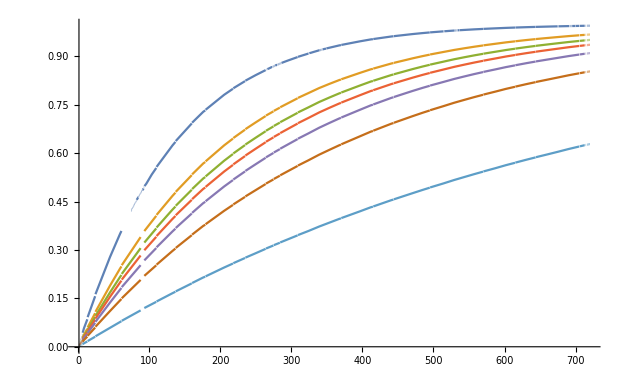

```mathematica
Plot[{rescaledDrawDownMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 1],  rescaledDrawDownMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 4],  rescaledDrawDownMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 6], rescaledDrawDownMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 8], rescaledDrawDownMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 12], rescaledDrawDownMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 24], rescaledDrawDownMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 168]}, {t, 1, 24*30}]
```

```mathematica
(* And anchor ... *)
```

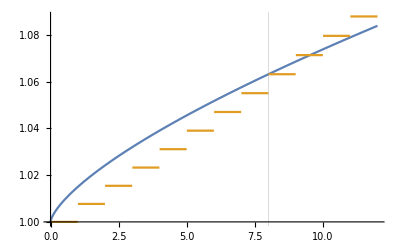

```mathematica
Plot[{factorUniWeth120dFiltered1HourCandle[t, 0.05], 1/compoundFactorMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 8]}, {t, 0, 12}, GridLines->{{8}}]
```

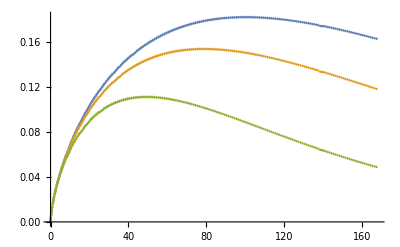

```mathematica
Plot[{(factorUniWeth120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 8], (factorUniWeth120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 4], (factorUniWeth120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*7}]
```

```mathematica
(* This is kind of bad. Lower funding rate is translating to slower draw down in VaR over time, even with same framework. *)
```

```mathematica
(* TODO: Should have a framework that has similar curves regardless of inverse CDF *)
```

```mathematica
Plot[{(factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8], (factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 4], (factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*7}]
```

-Graphics-

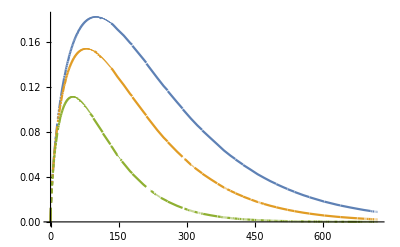

```mathematica
Plot[{(factorUniWeth120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 8], (factorUniWeth120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 4], (factorUniWeth120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinUniWeth120dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*30}]
```

```mathematica
Plot[{(factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 8], (factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 4], (factorWethUsdc120dFiltered1HourCandle[t, 0.05] - 1)*compoundFactorMinWethUsdc120dFiltered1HourCandle[t, 0.05, 1, 1]}, {t, 0, 24*30}]
```

-Graphics-

```mathematica
(* Use mathematica to obtain expression for critical points (or at least try to) .... *)
```

```mathematica
(* TODO: expected shortfall calc *)
```

```mathematica
(* TODO: Let's amp things up with something like ALCX/WETH which has 10m a < 1 ... Likely closer to what OVL/ETH and OVL/DAI will be. *)
```